## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

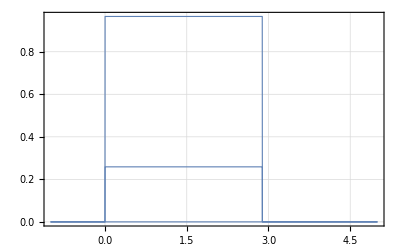

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

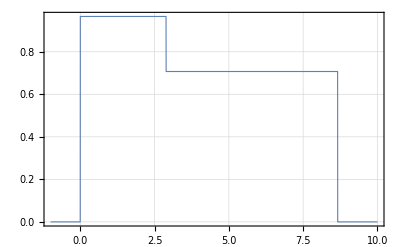

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

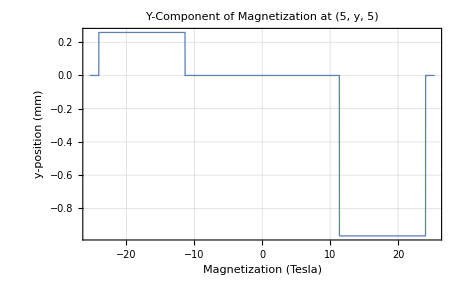

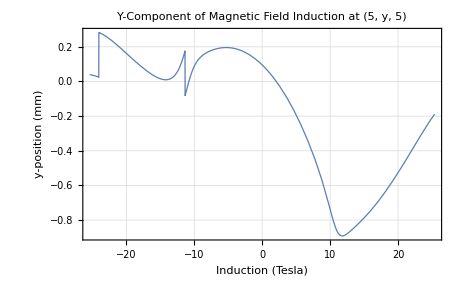

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

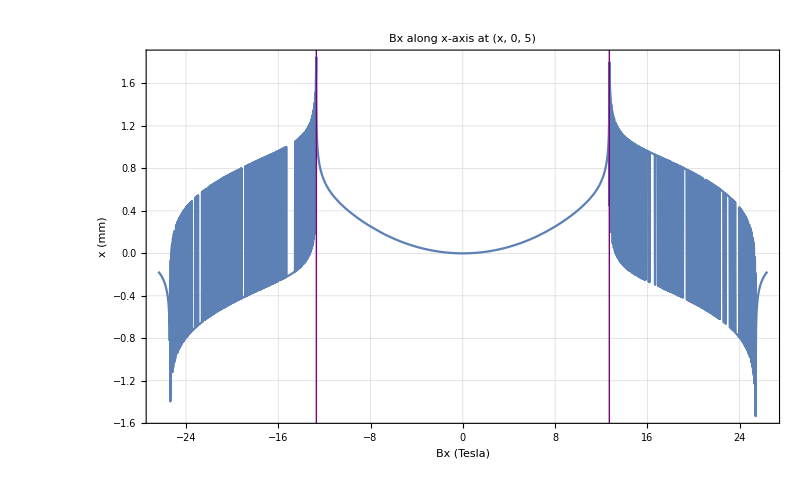

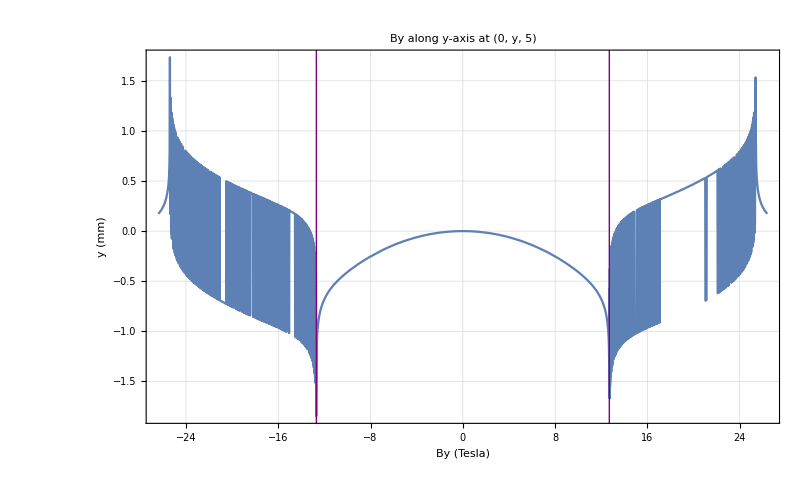

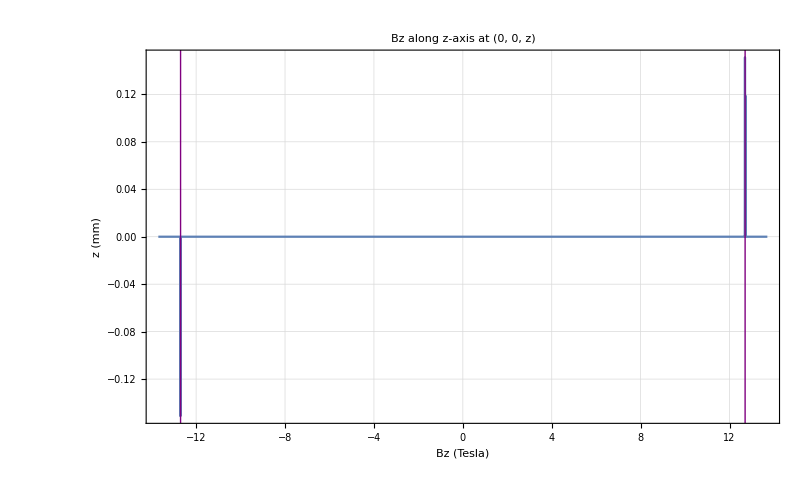

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

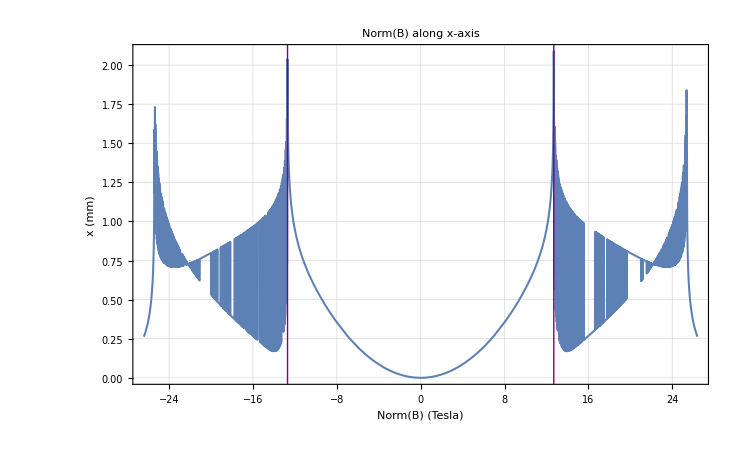

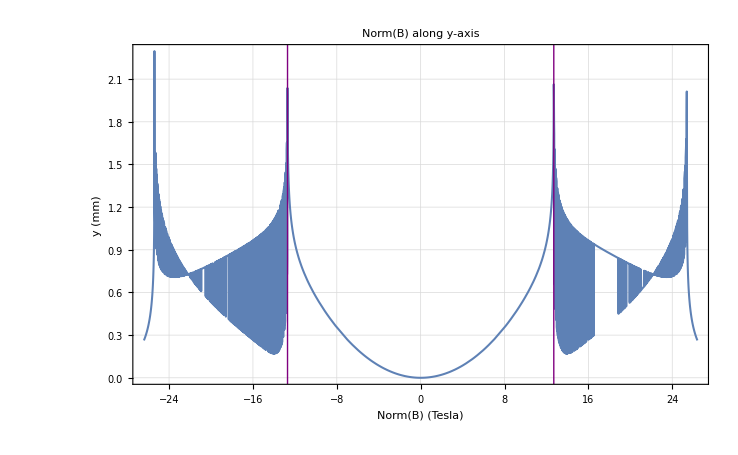

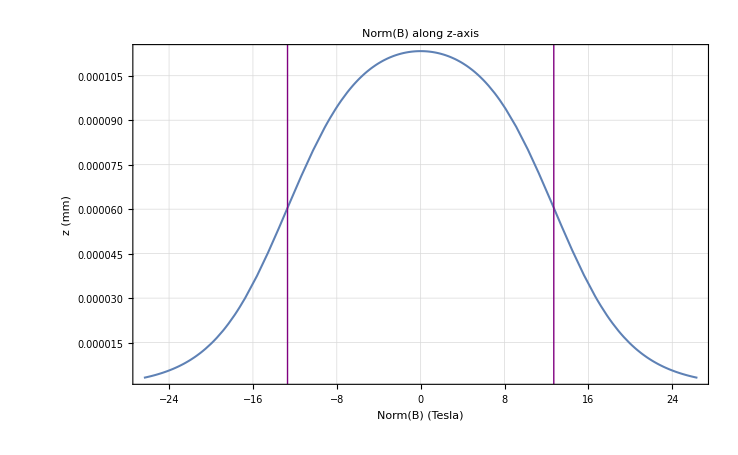

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "Bx", {x, y, z}];
by = radFld[halbach, "By", {x, y, z}];
bz = radFld[halbach, "Bz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a .csv file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=18;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "By", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "B", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/desktop/Andrew/2019-2020/Doyle Lab/Modeling Project/magnetic_lens_monte_carlo/bmatrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((0.248943
-0.389488
-0.333859
-0.294588
-0.268571
-0.251791
-0.241262
-0.235106
-0.232265
-0.232265
-0.235106
-0.241262
-0.251791
-0.268571
-0.294588
-0.333859
-0.389488
0.248943) | (0.251983
-0.382081
-0.325297
-0.286534
-0.261197
-0.244896
-0.234655
-0.228655
-0.225882
-0.225882
-0.228655
-0.234655
-0.244896
-0.261197
-0.286534
-0.325297
-0.382081
0.251983) | (0.264162
-0.351481
-0.292587
-0.256332
-0.233212
-0.218304
-0.208858
-0.203283
-0.200694
-0.200694
-0.203283
-0.208858
-0.218304
-0.233212
-0.256332
-0.292587
-0.351481
0.264162) | (0.288542
-0.278027
-0.227947
-0.198551
-0.179226
-0.166377
-0.158049
-0.153058
-0.15072
-0.15072
-0.153058
-0.158049
-0.166377
-0.179226
-0.198551
-0.227947
-0.278027
0.288542) | (0.0032602
0.879641
0.894916
0.913939
0.928875
0.939547
0.946722
0.951108
0.953184
0.953184
0.951108
0.946722
0.939547
0.928875
0.913939
0.894916
0.879641
0.969186) | (-0.0257768
0.85711
0.85205
0.863809
0.87558
0.884621
0.890887
0.894775
0.896628
0.896628
0.894775
0.890887
0.884621
0.87558
0.863809
0.85205
0.85711
0.940149) | (-0.0594931
0.794626
0.7895
0.800504
0.8114
0.819722
0.825467
0.829023
0.830717
0.830717
0.829023
0.825467
0.819722
0.8114
0.800504
0.7895
0.794626
0.906433) | (-0.0605529
0.773359
0.783819
0.799319
0.811241
0.819597
0.825147
0.828516
0.830105
0.830105
0.828516
0.825147
0.819597
0.811241
0.799319
0.783819
0.773359
0.905373) | (-0.000960405
0.86039
0.8972
0.918626
0.932007
0.940604
0.946067
0.949305
0.950814
0.950814
0.949305
0.946067
0.940604
0.932007
0.918626
0.8972
0.86039
0.964965) | (0.227008
0.0835765
0.128538
0.151692
0.165362
0.17384
0.179102
0.182173
0.183592
0.183592
0.182173
0.179102
0.17384
0.165362
0.151692
0.128538
0.0835765
-0.0318108) | (0.138985
-0.0726222
-0.0401195
-0.0200281
-0.0075673
0.000248659
0.00509876
0.00792126
0.00922143
0.00922143
0.00792126
0.00509876
0.000248659
-0.0075673
-0.0200281
-0.0401195
-0.0726222
0.138985) | (0.10883
-0.116449
-0.0913361
-0.0747615
-0.0640974
-0.0572714
-0.0529904
-0.0504869
-0.0493316
-0.0493316
-0.0504869
-0.0529904
-0.0572714
-0.0640974
-0.0747615
-0.0913361
-0.116449
0.10883) | (0.11908
-0.0892978
-0.0631287
-0.048696
-0.0397017
-0.0339008
-0.0302211
-0.028053
-0.0270489
-0.0270489
-0.028053
-0.0302211
-0.0339008
-0.0397017
-0.048696
-0.0631287
-0.0892978
0.11908) | (0.189422
0.0612039
0.0852213
0.0970284
0.104504
0.109437
0.112611
0.114493
0.115367
0.115367
0.114493
0.112611
0.109437
0.104504
0.0970284
0.0852213
0.0612039
0.189422) | (-0.040498
-0.818276
-0.815167
-0.807286
-0.800976
-0.796552
-0.793666
-0.791956
-0.791166
-0.791166
-0.791956
-0.793666
-0.796552
-0.800976
-0.807286
-0.815167
-0.818276
-0.747605) | (-0.696327
-0.712695
-0.710854
-0.703591
-0.697162
-0.69261
-0.68969
-0.687996
-0.687225
-0.687225
-0.687996
-0.68969
-0.69261
-0.697162
-0.703591
-0.710854
-0.712695
-0.696327) | (0.05604
-0.639731
-0.626856
-0.615356
-0.606985
-0.601532
-0.598225
-0.596384
-0.595569
-0.595569
-0.596384
-0.598225
-0.601532
-0.606985
-0.615356
-0.626856
-0.639731
-0.651067) | (0.103985
-0.569812
-0.542908
-0.52434
-0.512677
-0.505743
-0.501795
-0.499694
-0.498789
-0.498789
-0.499694
-0.501795
-0.505743
-0.512677
-0.52434
-0.542908
-0.569812
-0.603122)
(0.296848
-0.320027
-0.251824
-0.206624
-0.177584
-0.159043
-0.147432
-0.140642
-0.137508
-0.137508
-0.140642
-0.147432
-0.159043
-0.177584
-0.206624
-0.251824
-0.320027
0.296848) | (0.292739
-0.329345
-0.262501
-0.216783
-0.187058
-0.168046
-0.156156
-0.149217
-0.146017
-0.146017
-0.149217
-0.156156
-0.168046
-0.187058
-0.216783
-0.262501
-0.329345
0.292739) | (0.30087
-0.313062
-0.244061
-0.198741
-0.16965
-0.151069
-0.13943
-0.132624
-0.129482
-0.129482
-0.132624
-0.13943
-0.151069
-0.16965
-0.198741
-0.244061
-0.313062
0.30087) | (0.338665
-0.236066
-0.161755
-0.118264
-0.0910008
-0.0735661
-0.0625801
-0.0561224
-0.0531313
-0.0531313
-0.0561224
-0.0625801
-0.0735661
-0.0910008
-0.118264
-0.161755
-0.236066
0.338665) | (0.471571
0.0461397
0.115498
0.154432
0.179013
0.194926
0.205056
0.211053
0.213841
0.213841
0.211053
0.205056
0.194926
0.179013
0.154432
0.115498
0.0461397
0.471571) | (0.475256
0.786852
0.84211
0.875955
0.897974
0.91243
0.921705
0.927221
0.929792
0.929792
0.927221
0.921705
0.91243
0.897974
0.875955
0.84211
0.786852
0.475256) | (0.392347
0.627536
0.683933
0.715917
0.736405
0.74976
0.758294
0.763359
0.765717
0.765717
0.763359
0.758294
0.74976
0.736405
0.715917
0.683933
0.627536
0.392347) | (0.356406
0.551811
0.616071
0.648888
0.668692
0.681207
0.689072
0.693697
0.695841
0.695841
0.693697
0.689072
0.681207
0.668692
0.648888
0.616071
0.551811
0.356406) | (0.320971
0.484192
0.551141
0.58382
0.602597
0.614107
0.621211
0.625344
0.62725
0.62725
0.625344
0.621211
0.614107
0.602597
0.58382
0.551141
0.484192
0.320971) | (0.227268
0.324385
0.376981
0.404954
0.421221
0.431156
0.437251
0.44078
0.442403
0.442403
0.44078
0.437251
0.431156
0.421221
0.404954
0.376981
0.324385
0.227268) | (0.133669
0.177813
0.209249
0.229013
0.241342
0.249097
0.253914
0.256718
0.258009
0.258009
0.256718
0.253914
0.249097
0.241342
0.229013
0.209249
0.177813
0.133669) | (0.0724167
0.091509
0.107294
0.118856
0.126824
0.132129
0.135528
0.137538
0.13847
0.13847
0.137538
0.135528
0.132129
0.126824
0.118856
0.107294
0.091509
0.0724167) | (0.0279159
0.0318267
0.0364452
0.041408
0.0455471
0.0485876
0.0506374
0.05188
0.0524628
0.0524628
0.05188
0.0506374
0.0485876
0.0455471
0.041408
0.0364452
0.0318267
0.0279159) | (-0.0680646
-0.846841
-0.849459
-0.848541
-0.846978
-0.845611
-0.844631
-0.844024
-0.843739
-0.843739
-0.844024
-0.844631
-0.845611
-0.846978
-0.848541
-0.849459
-0.846841
-0.775171) | (0.00607108
-0.696512
-0.695698
-0.694848
-0.694049
-0.69348
-0.693136
-0.692956
-0.692881
-0.692881
-0.692956
-0.693136
-0.69348
-0.694049
-0.694848
-0.695698
-0.696512
-0.701036) | (0.0305005
-0.658692
-0.648967
-0.644571
-0.642693
-0.641985
-0.641796
-0.6418
-0.641836
-0.641836
-0.6418
-0.641796
-0.641985
-0.642693
-0.644571
-0.648967
-0.658692
-0.676606) | (0.0603476
-0.616299
-0.596478
-0.586636
-0.582413
-0.580838
-0.580397
-0.58037
-0.580423
-0.580423
-0.58037
-0.580397
-0.580838
-0.582413
-0.586636
-0.596478
-0.616299
-0.646759) | (-0.605934
-0.556383
-0.524421
-0.50848
-0.501455
-0.498662
-0.497732
-0.49753
-0.497532
-0.497532
-0.49753
-0.497732
-0.498662
-0.501455
-0.50848
-0.524421
-0.556383
-0.605934)
(0.342123
-0.235458
-0.157515
-0.112366
-0.0844109
-0.0665936
-0.0553652
-0.0487613
-0.0457016
-0.0457016
-0.0487613
-0.0553652
-0.0665936
-0.0844109
-0.112366
-0.157515
-0.235458
0.342123) | (0.322568
-0.279407
-0.204555
-0.157005
-0.126926
-0.107799
-0.0958309
-0.0888349
-0.085606
-0.085606
-0.0888349
-0.0958309
-0.107799
-0.126926
-0.157005
-0.204555
-0.279407
0.322568) | (0.311084
-0.301377
-0.229408
-0.181622
-0.150971
-0.131445
-0.119243
-0.112122
-0.108839
-0.108839
-0.112122
-0.119243
-0.131445
-0.150971
-0.181622
-0.229408
-0.301377
0.311084) | (0.329251
-0.268005
-0.191834
-0.14393
-0.113698
-0.0944961
-0.0824911
-0.0754782
-0.0722427
-0.0722427
-0.0754782
-0.0824911
-0.0944961
-0.113698
-0.14393
-0.191834
-0.268005
0.329251) | (0.382247
0.540973
0.62539
0.672838
0.701919
0.720294
0.731793
0.738522
0.74163
0.74163
0.738522
0.731793
0.720294
0.701919
0.672838
0.62539
0.540973
0.382247) | (0.374666
0.535312
0.617962
0.663089
0.690453
0.707702
0.718498
0.724821
0.727744
0.727744
0.724821
0.718498
0.707702
0.690453
0.663089
0.617962
0.535312
0.374666) | (0.324984
0.45399
0.528463
0.570346
0.595742
0.611692
0.621647
0.627468
0.630156
0.630156
0.627468
0.621647
0.611692
0.595742
0.570346
0.528463
0.45399
0.324984) | (0.281944
0.387572
0.453935
0.492258
0.515404
0.529821
0.53876
0.543966
0.546364
0.546364
0.543966
0.53876
0.529821
0.515404
0.492258
0.453935
0.387572
0.281944) | (0.233839
0.317392
0.373236
0.406394
0.426432
0.438838
0.446488
0.450924
0.452964
0.452964
0.450924
0.446488
0.438838
0.426432
0.406394
0.373236
0.317392
0.233839) | (0.168845
0.22467
0.264756
0.2899
0.305461
0.315179
0.321188
0.324674
0.326277
0.326277
0.324674
0.321188
0.315179
0.305461
0.2899
0.264756
0.22467
0.168845) | (0.0958211
0.123385
0.145095
0.160096
0.169998
0.176418
0.180469
0.182846
0.183944
0.183944
0.182846
0.180469
0.176418
0.169998
0.160096
0.145095
0.123385
0.0958211) | (0.0218343
0.0221901
0.0253024
0.0295761
0.0333892
0.0362544
0.0382038
0.0393914
0.0399499
0.0399499
0.0393914
0.0382038
0.0362544
0.0333892
0.0295761
0.0253024
0.0221901
0.0218343) | (-0.0713809
-0.116825
-0.134646
-0.14033
-0.14204
-0.142469
-0.142512
-0.14247
-0.142437
-0.142437
-0.14247
-0.142512
-0.142469
-0.14204
-0.14033
-0.134646
-0.116825
-0.0713809) | (-0.211706
-0.365109
-0.39643
-0.40787
-0.413274
-0.416183
-0.417847
-0.41878
-0.419203
-0.419203
-0.41878
-0.417847
-0.416183
-0.413274
-0.40787
-0.39643
-0.365109
-0.211706) | (-0.6436
-0.537053
-0.54724
-0.556635
-0.563001
-0.567225
-0.569962
-0.571606
-0.572379
-0.572379
-0.571606
-0.569962
-0.567225
-0.563001
-0.556635
-0.54724
-0.537053
-0.6436) | (0.0421533
-0.604487
-0.593134
-0.596198
-0.601358
-0.605813
-0.609059
-0.611126
-0.612125
-0.612125
-0.611126
-0.609059
-0.605813
-0.601358
-0.596198
-0.593134
-0.604487
-0.664953) | (0.0524168
-0.599952
-0.577979
-0.575333
-0.578575
-0.58262
-0.585946
-0.588183
-0.589292
-0.589292
-0.588183
-0.585946
-0.58262
-0.578575
-0.575333
-0.577979
-0.599952
-0.65469) | (0.0892201
-0.539359
-0.508436
-0.502307
-0.504065
-0.507547
-0.510716
-0.512946
-0.514076
-0.514076
-0.512946
-0.510716
-0.507547
-0.504065
-0.502307
-0.508436
-0.539359
-0.617887)
(0.393471
-0.0949407
-0.0292973
0.00580567
0.0281793
0.042883
0.0523428
0.0579745
0.0605998
0.0605998
0.0579745
0.0523428
0.042883
0.0281793
0.00580567
-0.0292973
-0.0949407
0.393471) | (0.347029
-0.210944
-0.136546
-0.0951998
-0.0694486
-0.0529166
-0.0424614
-0.036306
-0.0334542
-0.0334542
-0.036306
-0.0424614
-0.0529166
-0.0694486
-0.0951998
-0.136546
-0.210944
0.347029) | (0.289728
-0.322705
-0.256516
-0.21409
-0.186831
-0.169306
-0.158271
-0.151801
-0.148811
-0.148811
-0.151801
-0.158271
-0.169306
-0.186831
-0.21409
-0.256516
-0.322705
0.289728) | (0.272744
0.353283
0.415536
0.4578
0.48542
0.503237
0.514454
0.521025
0.524061
0.524061
0.521025
0.514454
0.503237
0.48542
0.4578
0.415536
0.353283
0.272744) | (0.277816
0.363263
0.426966
0.469124
0.496415
0.513975
0.525026
0.531502
0.534493
0.534493
0.531502
0.525026
0.513975
0.496415
0.469124
0.426966
0.363263
0.277816) | (0.271266
0.356358
0.418875
0.459652
0.485853
0.502665
0.513238
0.519433
0.522295
0.522295
0.519433
0.513238
0.502665
0.485853
0.459652
0.418875
0.356358
0.271266) | (0.246258
0.321516
0.378252
0.415865
0.440132
0.455701
0.465483
0.47121
0.473854
0.473854
0.47121
0.465483
0.455701
0.440132
0.415865
0.378252
0.321516
0.246258) | (0.212137
0.27498
0.32368
0.356669
0.378115
0.391884
0.400523
0.405574
0.407904
0.407904
0.405574
0.400523
0.391884
0.378115
0.356669
0.32368
0.27498
0.212137) | (0.169694
0.218576
0.257293
0.284048
0.301605
0.312905
0.319995
0.324137
0.326047
0.326047
0.324137
0.319995
0.312905
0.301605
0.284048
0.257293
0.218576
0.169694) | (0.116863
0.149214
0.17545
0.194072
0.206521
0.21462
0.219731
0.222726
0.224108
0.224108
0.222726
0.219731
0.21462
0.206521
0.194072
0.17545
0.149214
0.116863) | (0.0548165
0.0682632
0.0797863
0.088595
0.0948692
0.0991359
0.101904
0.103552
0.104319
0.104319
0.103552
0.101904
0.0991359
0.0948692
0.088595
0.0797863
0.0682632
0.0548165) | (-0.0160537
-0.0252033
-0.0306976
-0.0328622
-0.0333558
-0.0332517
-0.0330198
-0.0328285
-0.0327273
-0.0327273
-0.0328285
-0.0330198
-0.0332517
-0.0333558
-0.0328622
-0.0306976
-0.0252033
-0.0160537) | (-0.0997386
-0.141314
-0.166934
-0.18026
-0.1873
-0.191215
-0.193458
-0.194703
-0.195263
-0.195263
-0.194703
-0.193458
-0.191215
-0.1873
-0.18026
-0.166934
-0.141314
-0.0997386) | (-0.192626
-0.282913
-0.327174
-0.348936
-0.361052
-0.368281
-0.372664
-0.375188
-0.376345
-0.376345
-0.375188
-0.372664
-0.368281
-0.361052
-0.348936
-0.327174
-0.282913
-0.192626) | (-0.272933
-0.4304
-0.473973
-0.497418
-0.512069
-0.521503
-0.527492
-0.531034
-0.53268
-0.53268
-0.531034
-0.527492
-0.521503
-0.512069
-0.497418
-0.473973
-0.4304
-0.272933) | (0.0241463
-0.568386
-0.584054
-0.603197
-0.618143
-0.628708
-0.635733
-0.639989
-0.641992
-0.641992
-0.639989
-0.635733
-0.628708
-0.618143
-0.603197
-0.584054
-0.568386
-0.682961) | (0.0148077
-0.605415
-0.602598
-0.617725
-0.632277
-0.643321
-0.650918
-0.655606
-0.657832
-0.657832
-0.655606
-0.650918
-0.643321
-0.632277
-0.617725
-0.602598
-0.605415
-0.692299) | (0.0650451
-0.498867
-0.498549
-0.514244
-0.529024
-0.540331
-0.548188
-0.553074
-0.555406
-0.555406
-0.553074
-0.548188
-0.540331
-0.529024
-0.514244
-0.498549
-0.498867
-0.642062)
(-0.0604763
-0.463014
-0.448309
-0.430013
-0.415861
-0.405848
-0.399191
-0.395166
-0.393277
-0.393277
-0.395166
-0.399191
-0.405848
-0.415861
-0.430013
-0.448309
-0.463014
-0.319295) | (0.421241
0.00604902
0.0502058
0.0766414
0.0943066
0.106123
0.113768
0.118324
0.120447
0.120447
0.118324
0.113768
0.106123
0.0943066
0.0766414
0.0502058
0.00604902
0.421241) | (0.211425
0.283167
0.328574
0.358166
0.377943
0.391042
0.399444
0.404421
0.406733
0.406733
0.404421
0.399444
0.391042
0.377943
0.358166
0.328574
0.283167
0.211425) | (0.192442
0.244306
0.286348
0.316711
0.337535
0.351387
0.360264
0.365514
0.36795
0.36795
0.365514
0.360264
0.351387
0.337535
0.316711
0.286348
0.244306
0.192442) | (0.192197
0.242532
0.284314
0.315001
0.336178
0.350287
0.359329
0.364676
0.367157
0.367157
0.364676
0.359329
0.350287
0.336178
0.315001
0.284314
0.242532
0.192197) | (0.188347
0.237684
0.27863
0.308698
0.329449
0.343273
0.352134
0.357374
0.359805
0.359805
0.357374
0.352134
0.343273
0.329449
0.308698
0.27863
0.237684
0.188347) | (0.174308
0.219463
0.25721
0.285134
0.304485
0.317399
0.325681
0.330579
0.332851
0.332851
0.330579
0.325681
0.317399
0.304485
0.285134
0.25721
0.219463
0.174308) | (0.150332
0.18864
0.220985
0.245179
0.262059
0.273358
0.28061
0.2849
0.286889
0.286889
0.2849
0.28061
0.273358
0.262059
0.245179
0.220985
0.18864
0.150332) | (0.116949
0.146267
0.171241
0.190121
0.203394
0.212313
0.218048
0.221442
0.223017
0.223017
0.221442
0.218048
0.212313
0.203394
0.190121
0.171241
0.146267
0.116949) | (0.0739669
0.0920635
0.107635
0.119574
0.128075
0.133841
0.137571
0.139787
0.140817
0.140817
0.139787
0.137571
0.133841
0.128075
0.119574
0.107635
0.0920635
0.0739669) | (0.0214793
0.0258413
0.0298703
0.0332843
0.0359454
0.0378754
0.0391798
0.0399753
0.04035
0.04035
0.0399753
0.0391798
0.0378754
0.0359454
0.0332843
0.0298703
0.0258413
0.0214793) | (-0.0406034
-0.0534117
-0.06337
-0.0699049
-0.073878
-0.0762446
-0.0776399
-0.0784216
-0.0787738
-0.0787738
-0.0784216
-0.0776399
-0.0762446
-0.073878
-0.0699049
-0.06337
-0.0534117
-0.0406034) | (-0.11251
-0.147877
-0.174614
-0.192022
-0.202893
-0.209653
-0.213803
-0.216197
-0.217294
-0.217294
-0.216197
-0.213803
-0.209653
-0.202893
-0.192022
-0.174614
-0.147877
-0.11251) | (-0.192294
-0.258139
-0.30348
-0.331267
-0.348442
-0.359229
-0.365935
-0.369843
-0.371644
-0.371644
-0.369843
-0.365935
-0.359229
-0.348442
-0.331267
-0.30348
-0.258139
-0.192294) | (-0.277892
-0.388332
-0.450121
-0.485514
-0.507503
-0.521546
-0.530398
-0.535604
-0.538014
-0.538014
-0.535604
-0.530398
-0.521546
-0.507503
-0.485514
-0.450121
-0.388332
-0.277892) | (-0.382265
-0.575337
-0.64263
-0.681575
-0.70664
-0.723029
-0.73351
-0.739725
-0.742616
-0.742616
-0.739725
-0.73351
-0.723029
-0.70664
-0.681575
-0.64263
-0.575337
-0.382265) | (-0.117944
-0.746999
-0.810375
-0.85108
-0.878132
-0.8961
-0.907694
-0.914605
-0.917829
-0.917829
-0.914605
-0.907694
-0.8961
-0.878132
-0.85108
-0.810375
-0.746999
-0.825051) | (-0.486022
0.210984
0.135675
0.0918348
0.0631767
0.0442103
0.0319739
0.024674
0.0212654
0.0212654
0.024674
0.0319739
0.0442103
0.0631767
0.0918348
0.135675
0.210984
-0.486022)
(0.0100177
-0.267187
-0.267919
-0.261856
-0.255721
-0.251013
-0.247791
-0.245821
-0.244893
-0.244893
-0.245821
-0.247791
-0.251013
-0.255721
-0.261856
-0.267919
-0.267187
-0.248801) | (-0.0281821
-0.103169
-0.0959667
-0.0858552
-0.0775781
-0.0716054
-0.06761
-0.0651921
-0.0640578
-0.0640578
-0.0651921
-0.06761
-0.0716054
-0.0775781
-0.0858552
-0.0959667
-0.103169
-0.0281821) | (0.0711716
0.0783155
0.0929718
0.106495
0.116789
0.124035
0.128829
0.131714
0.133064
0.133064
0.131714
0.128829
0.124035
0.116789
0.106495
0.0929718
0.0783155
0.0711716) | (0.0995908
0.121539
0.14156
0.157778
0.169787
0.178153
0.183659
0.186964
0.188508
0.188508
0.186964
0.183659
0.178153
0.169787
0.157778
0.14156
0.121539
0.0995908) | (0.112421
0.138492
0.161388
0.179467
0.1927
0.201869
0.207886
0.211493
0.213177
0.213177
0.211493
0.207886
0.201869
0.1927
0.179467
0.161388
0.138492
0.112421) | (0.116879
0.14421
0.168104
0.186878
0.200575
0.210048
0.21626
0.219981
0.221719
0.221719
0.219981
0.21626
0.210048
0.200575
0.186878
0.168104
0.14421
0.116879) | (0.112139
0.138234
0.161099
0.179118
0.192294
0.20142
0.207408
0.210996
0.212671
0.212671
0.210996
0.207408
0.20142
0.192294
0.179118
0.161099
0.138234
0.112139) | (0.0978218
0.120369
0.14021
0.155934
0.167485
0.175509
0.180781
0.183943
0.18542
0.18542
0.183943
0.180781
0.175509
0.167485
0.155934
0.14021
0.120369
0.0978218) | (0.073961
0.0908448
0.10576
0.117647
0.12642
0.132535
0.13656
0.138977
0.140106
0.140106
0.138977
0.13656
0.132535
0.12642
0.117647
0.10576
0.0908448
0.073961) | (0.0405562
0.0496584
0.0577432
0.0642413
0.0690803
0.0724775
0.0747263
0.0760809
0.076715
0.076715
0.0760809
0.0747263
0.0724775
0.0690803
0.0642413
0.0577432
0.0496584
0.0405562) | (-0.0023922
-0.00340588
-0.00417215
-0.00461786
-0.00481851
-0.00488271
-0.00488867
-0.00487822
-0.00486977
-0.00486977
-0.00487822
-0.00488867
-0.00488271
-0.00481851
-0.00461786
-0.00417215
-0.00340588
-0.0023922) | (-0.0549008
-0.0688885
-0.0807703
-0.0896884
-0.0958906
-0.100012
-0.102637
-0.104181
-0.104895
-0.104895
-0.104181
-0.102637
-0.100012
-0.0958906
-0.0896884
-0.0807703
-0.0688885
-0.0549008) | (-0.116918
-0.147683
-0.173268
-0.192028
-0.204905
-0.21343
-0.218866
-0.222069
-0.223552
-0.223552
-0.222069
-0.218866
-0.21343
-0.204905
-0.192028
-0.173268
-0.147683
-0.116918) | (-0.188374
-0.241409
-0.283548
-0.313062
-0.332808
-0.345744
-0.353965
-0.358807
-0.361049
-0.361049
-0.358807
-0.353965
-0.345744
-0.332808
-0.313062
-0.283548
-0.241409
-0.188374) | (-0.271253
-0.356394
-0.418159
-0.458507
-0.484707
-0.501693
-0.512454
-0.518787
-0.52172
-0.52172
-0.518787
-0.512454
-0.501693
-0.484707
-0.458507
-0.418159
-0.356394
-0.271253) | (-0.374582
-0.514084
-0.597882
-0.647966
-0.679637
-0.700005
-0.712875
-0.720444
-0.723948
-0.723948
-0.720444
-0.712875
-0.700005
-0.679637
-0.647966
-0.597882
-0.514084
-0.374582) | (-0.47507
-0.677797
-0.778668
-0.83597
-0.871735
-0.894615
-0.909036
-0.917507
-0.921428
-0.921428
-0.917507
-0.909036
-0.894615
-0.871735
-0.83597
-0.778668
-0.677797
-0.47507) | (-0.456868
0.338162
0.235378
0.174372
0.136148
0.111758
0.0964262
0.0874331
0.0832738
0.0832738
0.0874331
0.0964262
0.111758
0.136148
0.174372
0.235378
0.338162
-0.456868)
(0.0204386
-0.212146
-0.210938
-0.212304
-0.213531
-0.214433
-0.215053
-0.215439
-0.215625
-0.215625
-0.215439
-0.215053
-0.214433
-0.213531
-0.212304
-0.210938
-0.212146
-0.23838) | (-0.072552
-0.131349
-0.140451
-0.143154
-0.144037
-0.144336
-0.144441
-0.14448
-0.144494
-0.144494
-0.14448
-0.144441
-0.144336
-0.144037
-0.143154
-0.140451
-0.131349
-0.072552) | (-0.0219515
-0.0408447
-0.0473484
-0.0482088
-0.047538
-0.0466614
-0.0459531
-0.045489
-0.0452637
-0.0452637
-0.045489
-0.0459531
-0.0466614
-0.047538
-0.0482088
-0.0473484
-0.0408447
-0.0219515) | (0.0159631
0.0154345
0.0171048
0.0200733
0.0230211
0.0253763
0.0270382
0.0280721
0.0285635
0.0285635
0.0280721
0.0270382
0.0253763
0.0230211
0.0200733
0.0171048
0.0154345
0.0159631) | (0.0405428
0.0483286
0.0557382
0.0622084
0.0673458
0.0711079
0.0736632
0.0752252
0.075962
0.075962
0.0752252
0.0736632
0.0711079
0.0673458
0.0622084
0.0557382
0.0483286
0.0405428) | (0.0548682
0.0665984
0.0771865
0.0859071
0.0925607
0.0973234
0.100519
0.102461
0.103374
0.103374
0.102461
0.100519
0.0973234
0.0925607
0.0859071
0.0771865
0.0665984
0.0548682) | (0.0596338
0.0725446
0.0841393
0.0936235
0.100818
0.105947
0.109381
0.111465
0.112444
0.112444
0.111465
0.109381
0.105947
0.100818
0.0936235
0.0841393
0.0725446
0.0596338) | (0.0548627
0.0666938
0.0773334
0.0860543
0.0926825
0.0974154
0.100587
0.102512
0.103418
0.103418
0.102512
0.100587
0.0974154
0.0926825
0.0860543
0.0773334
0.0666938
0.0548627) | (0.0405499
0.0492442
0.0570777
0.0635172
0.0684255
0.0719383
0.0742959
0.0757285
0.0764023
0.0764023
0.0757285
0.0742959
0.0719383
0.0684255
0.0635172
0.0570777
0.0492442
0.0405499) | (0.0166961
0.0202286
0.023423
0.0260648
0.0280918
0.0295512
0.0305351
0.0311347
0.0314173
0.0314173
0.0311347
0.0305351
0.0295512
0.0280918
0.0260648
0.023423
0.0202286
0.0166961) | (-0.0167008
-0.0204857
-0.0238431
-0.0265325
-0.0285245
-0.0299142
-0.030829
-0.0313777
-0.0316339
-0.0316339
-0.0313777
-0.030829
-0.0299142
-0.0285245
-0.0265325
-0.0238431
-0.0204857
-0.0167008) | (-0.0596449
-0.0732258
-0.0852321
-0.0948114
-0.101892
-0.106833
-0.110089
-0.112045
-0.112959
-0.112959
-0.112045
-0.110089
-0.106833
-0.101892
-0.0948114
-0.0852321
-0.0732258
-0.0596449) | (-0.112143
-0.138583
-0.161627
-0.179652
-0.192747
-0.201775
-0.207682
-0.211216
-0.212865
-0.212865
-0.211216
-0.207682
-0.201775
-0.192747
-0.179652
-0.161627
-0.138583
-0.112143) | (-0.174288
-0.217663
-0.254532
-0.28246
-0.302232
-0.315637
-0.324321
-0.329488
-0.331892
-0.331892
-0.329488
-0.324321
-0.315637
-0.302232
-0.28246
-0.254532
-0.217663
-0.174288) | (-0.24619
-0.31222
-0.366079
-0.405023
-0.431706
-0.449444
-0.460809
-0.467531
-0.47065
-0.47065
-0.467531
-0.460809
-0.449444
-0.431706
-0.405023
-0.366079
-0.31222
-0.24619) | (-0.32484
-0.419889
-0.493095
-0.543198
-0.576369
-0.597993
-0.611701
-0.619763
-0.623494
-0.623494
-0.619763
-0.611701
-0.597993
-0.576369
-0.543198
-0.493095
-0.419889
-0.32484) | (-0.392099
-0.513364
-0.603363
-0.66275
-0.701106
-0.725737
-0.741218
-0.750282
-0.754468
-0.754468
-0.750282
-0.741218
-0.725737
-0.701106
-0.66275
-0.603363
-0.513364
-0.392099) | (-0.423095
0.41273
0.314836
0.250235
0.208841
0.182454
0.165951
0.156315
0.151871
0.151871
0.156315
0.165951
0.182454
0.208841
0.250235
0.314836
0.41273
-0.423095)
(-0.00954371
-0.223763
-0.229655
-0.240999
-0.250713
-0.257815
-0.262603
-0.26552
-0.266896
-0.266896
-0.26552
-0.262603
-0.257815
-0.250713
-0.240999
-0.229655
-0.223763
-0.268363) | (-0.13367
-0.193002
-0.21764
-0.232916
-0.243136
-0.249942
-0.254334
-0.256949
-0.258168
-0.258168
-0.256949
-0.254334
-0.249942
-0.243136
-0.232916
-0.21764
-0.193002
-0.13367) | (-0.0958407
-0.128933
-0.150872
-0.164381
-0.172937
-0.178429
-0.181895
-0.183932
-0.184875
-0.184875
-0.183932
-0.181895
-0.178429
-0.172937
-0.164381
-0.150872
-0.128933
-0.0958407) | (-0.0548421
-0.0712189
-0.0838637
-0.092384
-0.0978959
-0.101421
-0.103628
-0.104916
-0.10551
-0.10551
-0.104916
-0.103628
-0.101421
-0.0978959
-0.092384
-0.0838637
-0.0712189
-0.0548421) | (-0.0215021
-0.0276196
-0.0325896
-0.0360798
-0.0383543
-0.0397896
-0.0406718
-0.0411792
-0.041411
-0.041411
-0.0411792
-0.0406718
-0.0397896
-0.0383543
-0.0360798
-0.0325896
-0.0276196
-0.0215021) | (0.00237684
0.00243938
0.00262729
0.00294611
0.00331302
0.00364637
0.00390325
0.00407193
0.00415443
0.00415443
0.00407193
0.00390325
0.00364637
0.00331302
0.00294611
0.00262729
0.00243938
0.00237684) | (0.0166935
0.0200868
0.0231905
0.025805
0.0278507
0.0293482
0.0303704
0.0309984
0.0312956
0.0312956
0.0309984
0.0303704
0.0293482
0.0278507
0.025805
0.0231905
0.0200868
0.0166935) | (0.0214644
0.0259013
0.0299389
0.033313
0.0359318
0.0378364
0.0391305
0.0399232
0.0402979
0.0402979
0.0399232
0.0391305
0.0378364
0.0359318
0.033313
0.0299389
0.0259013
0.0214644) | (0.0166943
0.0201367
0.0232715
0.025894
0.0279319
0.0294156
0.0304245
0.0310428
0.0313351
0.0313351
0.0310428
0.0304245
0.0294156
0.0279319
0.025894
0.0232715
0.0201367
0.0166943) | (0.0023847
0.00286699
0.00330834
0.00368064
0.00397267
0.0041871
0.00433387
0.00442425
0.00446708
0.00446708
0.00442425
0.00433387
0.0041871
0.00397267
0.00368064
0.00330834
0.00286699
0.0023847) | (-0.0214659
-0.0259771
-0.0300645
-0.0334554
-0.0360661
-0.0379509
-0.0392243
-0.0400015
-0.0403679
-0.0403679
-0.0400015
-0.0392243
-0.0379509
-0.0360661
-0.0334554
-0.0300645
-0.0259771
-0.0214659) | (-0.0548613
-0.0666157
-0.0772055
-0.0859116
-0.0925501
-0.0973041
-0.100497
-0.102438
-0.103351
-0.103351
-0.102438
-0.100497
-0.0973041
-0.0925501
-0.0859116
-0.0772055
-0.0666157
-0.0548613) | (-0.0978079
-0.119461
-0.138768
-0.154386
-0.1661
-0.174377
-0.179882
-0.183209
-0.184769
-0.184769
-0.183209
-0.179882
-0.174377
-0.1661
-0.154386
-0.138768
-0.119461
-0.0978079) | (-0.150291
-0.185175
-0.215758
-0.239885
-0.257554
-0.26981
-0.277862
-0.28269
-0.284946
-0.284946
-0.28269
-0.277862
-0.26981
-0.257554
-0.239885
-0.215758
-0.185175
-0.150291) | (-0.212047
-0.264511
-0.309293
-0.343353
-0.367511
-0.383893
-0.394503
-0.400813
-0.403749
-0.403749
-0.400813
-0.394503
-0.383893
-0.367511
-0.343353
-0.309293
-0.264511
-0.212047) | (-0.281784
-0.357491
-0.419423
-0.464179
-0.49472
-0.514932
-0.527838
-0.535456
-0.538986
-0.538986
-0.535456
-0.527838
-0.514932
-0.49472
-0.464179
-0.419423
-0.357491
-0.281784) | (-0.356153
-0.462554
-0.543433
-0.598068
-0.633887
-0.657088
-0.671738
-0.680336
-0.684311
-0.684311
-0.680336
-0.671738
-0.657088
-0.633887
-0.598068
-0.543433
-0.462554
-0.356153) | (-0.422041
0.402865
0.305979
0.244856
0.205975
0.18112
0.165517
0.156382
0.152163
0.152163
0.156382
0.165517
0.18112
0.205975
0.244856
0.305979
0.402865
-0.422041)
(-0.0974137
-0.316566
-0.354236
-0.383182
-0.403583
-0.417477
-0.426546
-0.43198
-0.43452
-0.43452
-0.43198
-0.426546
-0.417477
-0.403583
-0.383182
-0.354236
-0.316566
-0.356233) | (-0.22715
-0.309509
-0.357365
-0.387686
-0.407807
-0.421139
-0.429712
-0.434803
-0.437172
-0.437172
-0.434803
-0.429712
-0.421139
-0.407807
-0.387686
-0.357365
-0.309509
-0.22715) | (-0.168777
-0.217738
-0.254932
-0.28057
-0.297883
-0.309384
-0.316772
-0.321154
-0.323191
-0.323191
-0.321154
-0.316772
-0.309384
-0.297883
-0.28057
-0.254932
-0.217738
-0.168777) | (-0.116829
-0.14645
-0.171273
-0.18984
-0.202919
-0.211783
-0.217532
-0.220957
-0.222552
-0.222552
-0.220957
-0.217532
-0.211783
-0.202919
-0.18984
-0.171273
-0.14645
-0.116829) | (-0.0739535
-0.0911615
-0.106211
-0.118059
-0.126731
-0.132751
-0.13671
-0.139086
-0.140197
-0.140197
-0.139086
-0.13671
-0.132751
-0.126731
-0.118059
-0.106211
-0.0911615
-0.0739535) | (-0.0405529
-0.0494646
-0.0574283
-0.0638936
-0.0687615
-0.072212
-0.0745126
-0.0759049
-0.0765584
-0.0765584
-0.0759049
-0.0745126
-0.072212
-0.0687615
-0.0638936
-0.0574283
-0.0494646
-0.0405529) | (-0.0166961
-0.0202301
-0.0234253
-0.0260672
-0.0280939
-0.0295529
-0.0305364
-0.0311358
-0.0314182
-0.0314182
-0.0311358
-0.0305364
-0.0295529
-0.0280939
-0.0260672
-0.0234253
-0.0202301
-0.0166961) | (-0.00238503
-0.00288235
-0.00333397
-0.00370999
-0.0040006
-0.0042111
-0.00435367
-0.00444082
-0.00448194
-0.00448194
-0.00444082
-0.00435367
-0.0042111
-0.0040006
-0.00370999
-0.00333397
-0.00288235
-0.00238503) | (0.0023847
0.00286708
0.00330846
0.00368073
0.00397272
0.0041871
0.00433386
0.00442422
0.00446705
0.00446705
0.00442422
0.00433386
0.0041871
0.00397272
0.00368073
0.00330846
0.00286708
0.0023847) | (-0.00238472
-0.00286795
-0.00330993
-0.00368243
-0.00397434
-0.00418851
-0.00433503
-0.00442521
-0.00446793
-0.00446793
-0.00442521
-0.00433503
-0.00418851
-0.00397434
-0.00368243
-0.00330993
-0.00286795
-0.00238472) | (-0.0166938
-0.0201087
-0.0232247
-0.0258404
-0.027881
-0.0293718
-0.0303884
-0.0310126
-0.031308
-0.031308
-0.0310126
-0.0303884
-0.0293718
-0.027881
-0.0258404
-0.0232247
-0.0201087
-0.0166938) | (-0.0405455
-0.0490127
-0.0566967
-0.063089
-0.0680257
-0.0716002
-0.0740205
-0.0754999
-0.0761981
-0.0761981
-0.0754999
-0.0740205
-0.0716002
-0.0680257
-0.063089
-0.0566967
-0.0490127
-0.0405455) | (-0.0739457
-0.0899121
-0.104262
-0.116015
-0.124942
-0.131314
-0.135585
-0.138177
-0.139396
-0.139396
-0.138177
-0.135585
-0.131314
-0.124942
-0.116015
-0.104262
-0.0899121
-0.0739457) | (-0.116911
-0.143431
-0.166871
-0.185591
-0.199462
-0.209173
-0.215592
-0.219457
-0.221266
-0.221266
-0.219457
-0.215592
-0.209173
-0.199462
-0.185591
-0.166871
-0.143431
-0.116911) | (-0.169618
-0.210991
-0.246436
-0.2736
-0.293042
-0.306327
-0.314977
-0.32014
-0.322545
-0.322545
-0.32014
-0.314977
-0.306327
-0.293042
-0.2736
-0.246436
-0.210991
-0.169618) | (-0.233708
-0.297754
-0.34888
-0.38538
-0.410346
-0.426973
-0.43765
-0.443974
-0.446911
-0.446911
-0.443974
-0.43765
-0.426973
-0.410346
-0.38538
-0.34888
-0.297754
-0.233708) | (-0.320763
-0.430577
-0.501691
-0.546706
-0.57604
-0.595184
-0.607367
-0.614556
-0.617889
-0.617889
-0.614556
-0.607367
-0.595184
-0.57604
-0.546706
-0.501691
-0.430577
-0.320763) | (-0.4817
0.241997
0.153477
0.104068
0.0727437
0.052428
0.0395079
0.0318778
0.028337
0.028337
0.0318778
0.0395079
0.052428
0.0727437
0.104068
0.153477
0.241997
-0.4817)
(-0.4817
0.241997
0.153477
0.104068
0.0727437
0.052428
0.0395079
0.0318778
0.028337
0.028337
0.0318778
0.0395079
0.052428
0.0727437
0.104068
0.153477
0.241997
-0.4817) | (-0.320763
-0.430577
-0.501691
-0.546706
-0.57604
-0.595184
-0.607367
-0.614556
-0.617889
-0.617889
-0.614556
-0.607367
-0.595184
-0.57604
-0.546706
-0.501691
-0.430577
-0.320763) | (-0.233708
-0.297754
-0.34888
-0.38538
-0.410346
-0.426973
-0.43765
-0.443974
-0.446911
-0.446911
-0.443974
-0.43765
-0.426973
-0.410346
-0.38538
-0.34888
-0.297754
-0.233708) | (-0.169618
-0.210991
-0.246436
-0.2736
-0.293042
-0.306327
-0.314977
-0.32014
-0.322545
-0.322545
-0.32014
-0.314977
-0.306327
-0.293042
-0.2736
-0.246436
-0.210991
-0.169618) | (-0.116911
-0.143431
-0.166871
-0.185591
-0.199462
-0.209173
-0.215592
-0.219457
-0.221266
-0.221266
-0.219457
-0.215592
-0.209173
-0.199462
-0.185591
-0.166871
-0.143431
-0.116911) | (-0.0739457
-0.0899121
-0.104262
-0.116015
-0.124942
-0.131314
-0.135585
-0.138177
-0.139396
-0.139396
-0.138177
-0.135585
-0.131314
-0.124942
-0.116015
-0.104262
-0.0899121
-0.0739457) | (-0.0405455
-0.0490127
-0.0566967
-0.063089
-0.0680257
-0.0716002
-0.0740205
-0.0754999
-0.0761981
-0.0761981
-0.0754999
-0.0740205
-0.0716002
-0.0680257
-0.063089
-0.0566967
-0.0490127
-0.0405455) | (-0.0166938
-0.0201087
-0.0232247
-0.0258404
-0.027881
-0.0293718
-0.0303884
-0.0310126
-0.031308
-0.031308
-0.0310126
-0.0303884
-0.0293718
-0.027881
-0.0258404
-0.0232247
-0.0201087
-0.0166938) | (-0.00238472
-0.00286795
-0.00330993
-0.00368243
-0.00397434
-0.00418851
-0.00433503
-0.00442521
-0.00446793
-0.00446793
-0.00442521
-0.00433503
-0.00418851
-0.00397434
-0.00368243
-0.00330993
-0.00286795
-0.00238472) | (0.0023847
0.00286708
0.00330846
0.00368073
0.00397272
0.0041871
0.00433386
0.00442422
0.00446705
0.00446705
0.00442422
0.00433386
0.0041871
0.00397272
0.00368073
0.00330846
0.00286708
0.0023847) | (-0.00238503
-0.00288235
-0.00333397
-0.00370999
-0.0040006
-0.0042111
-0.00435367
-0.00444082
-0.00448194
-0.00448194
-0.00444082
-0.00435367
-0.0042111
-0.0040006
-0.00370999
-0.00333397
-0.00288235
-0.00238503) | (-0.0166961
-0.0202301
-0.0234253
-0.0260672
-0.0280939
-0.0295529
-0.0305364
-0.0311358
-0.0314182
-0.0314182
-0.0311358
-0.0305364
-0.0295529
-0.0280939
-0.0260672
-0.0234253
-0.0202301
-0.0166961) | (-0.0405529
-0.0494646
-0.0574283
-0.0638936
-0.0687615
-0.072212
-0.0745126
-0.0759049
-0.0765584
-0.0765584
-0.0759049
-0.0745126
-0.072212
-0.0687615
-0.0638936
-0.0574283
-0.0494646
-0.0405529) | (-0.0739535
-0.0911615
-0.106211
-0.118059
-0.126731
-0.132751
-0.13671
-0.139086
-0.140197
-0.140197
-0.139086
-0.13671
-0.132751
-0.126731
-0.118059
-0.106211
-0.0911615
-0.0739535) | (-0.116829
-0.14645
-0.171273
-0.18984
-0.202919
-0.211783
-0.217532
-0.220957
-0.222552
-0.222552
-0.220957
-0.217532
-0.211783
-0.202919
-0.18984
-0.171273
-0.14645
-0.116829) | (-0.168777
-0.217738
-0.254932
-0.28057
-0.297883
-0.309384
-0.316772
-0.321154
-0.323191
-0.323191
-0.321154
-0.316772
-0.309384
-0.297883
-0.28057
-0.254932
-0.217738
-0.168777) | (-0.22715
-0.309509
-0.357365
-0.387686
-0.407807
-0.421139
-0.429712
-0.434803
-0.437172
-0.437172
-0.434803
-0.429712
-0.421139
-0.407807
-0.387686
-0.357365
-0.309509
-0.22715) | (-0.0974137
-0.316566
-0.354236
-0.383182
-0.403583
-0.417477
-0.426546
-0.43198
-0.43452
-0.43452
-0.43198
-0.426546
-0.417477
-0.403583
-0.383182
-0.354236
-0.316566
-0.0974137)
(-0.422041
0.402865
0.305979
0.244856
0.205975
0.18112
0.165517
0.156382
0.152163
0.152163
0.156382
0.165517
0.18112
0.205975
0.244856
0.305979
0.402865
-0.422041) | (-0.356153
-0.462554
-0.543433
-0.598068
-0.633887
-0.657088
-0.671738
-0.680336
-0.684311
-0.684311
-0.680336
-0.671738
-0.657088
-0.633887
-0.598068
-0.543433
-0.462554
-0.356153) | (-0.281784
-0.357491
-0.419423
-0.464179
-0.49472
-0.514932
-0.527838
-0.535456
-0.538986
-0.538986
-0.535456
-0.527838
-0.514932
-0.49472
-0.464179
-0.419423
-0.357491
-0.281784) | (-0.212047
-0.264511
-0.309293
-0.343353
-0.367511
-0.383893
-0.394503
-0.400813
-0.403749
-0.403749
-0.400813
-0.394503
-0.383893
-0.367511
-0.343353
-0.309293
-0.264511
-0.212047) | (-0.150291
-0.185175
-0.215758
-0.239885
-0.257554
-0.26981
-0.277862
-0.28269
-0.284946
-0.284946
-0.28269
-0.277862
-0.26981
-0.257554
-0.239885
-0.215758
-0.185175
-0.150291) | (-0.0978079
-0.119461
-0.138768
-0.154386
-0.1661
-0.174377
-0.179882
-0.183209
-0.184769
-0.184769
-0.183209
-0.179882
-0.174377
-0.1661
-0.154386
-0.138768
-0.119461
-0.0978079) | (-0.0548613
-0.0666157
-0.0772055
-0.0859116
-0.0925501
-0.0973041
-0.100497
-0.102438
-0.103351
-0.103351
-0.102438
-0.100497
-0.0973041
-0.0925501
-0.0859116
-0.0772055
-0.0666157
-0.0548613) | (-0.0214659
-0.0259771
-0.0300645
-0.0334554
-0.0360661
-0.0379509
-0.0392243
-0.0400015
-0.0403679
-0.0403679
-0.0400015
-0.0392243
-0.0379509
-0.0360661
-0.0334554
-0.0300645
-0.0259771
-0.0214659) | (0.0023847
0.00286699
0.00330834
0.00368064
0.00397267
0.0041871
0.00433387
0.00442425
0.00446708
0.00446708
0.00442425
0.00433387
0.0041871
0.00397267
0.00368064
0.00330834
0.00286699
0.0023847) | (0.0166943
0.0201367
0.0232715
0.025894
0.0279319
0.0294156
0.0304245
0.0310428
0.0313351
0.0313351
0.0310428
0.0304245
0.0294156
0.0279319
0.025894
0.0232715
0.0201367
0.0166943) | (0.0214644
0.0259013
0.0299389
0.033313
0.0359318
0.0378364
0.0391305
0.0399232
0.0402979
0.0402979
0.0399232
0.0391305
0.0378364
0.0359318
0.033313
0.0299389
0.0259013
0.0214644) | (0.0166935
0.0200868
0.0231905
0.025805
0.0278507
0.0293482
0.0303704
0.0309984
0.0312956
0.0312956
0.0309984
0.0303704
0.0293482
0.0278507
0.025805
0.0231905
0.0200868
0.0166935) | (0.00237684
0.00243938
0.00262729
0.00294611
0.00331302
0.00364637
0.00390325
0.00407193
0.00415443
0.00415443
0.00407193
0.00390325
0.00364637
0.00331302
0.00294611
0.00262729
0.00243938
0.00237684) | (-0.0215021
-0.0276196
-0.0325896
-0.0360798
-0.0383543
-0.0397896
-0.0406718
-0.0411792
-0.041411
-0.041411
-0.0411792
-0.0406718
-0.0397896
-0.0383543
-0.0360798
-0.0325896
-0.0276196
-0.0215021) | (-0.0548421
-0.0712189
-0.0838637
-0.092384
-0.0978959
-0.101421
-0.103628
-0.104916
-0.10551
-0.10551
-0.104916
-0.103628
-0.101421
-0.0978959
-0.092384
-0.0838637
-0.0712189
-0.0548421) | (-0.0958407
-0.128933
-0.150872
-0.164381
-0.172937
-0.178429
-0.181895
-0.183932
-0.184875
-0.184875
-0.183932
-0.181895
-0.178429
-0.172937
-0.164381
-0.150872
-0.128933
-0.0958407) | (-0.13367
-0.193002
-0.21764
-0.232916
-0.243136
-0.249942
-0.254334
-0.256949
-0.258168
-0.258168
-0.256949
-0.254334
-0.249942
-0.243136
-0.232916
-0.21764
-0.193002
-0.13367) | (-0.00954371
-0.223763
-0.229655
-0.240999
-0.250713
-0.257815
-0.262603
-0.26552
-0.266896
-0.266896
-0.26552
-0.262603
-0.257815
-0.250713
-0.240999
-0.229655
-0.223763
-0.00954371)
(-0.423095
0.41273
0.314836
0.250235
0.208841
0.182454
0.165951
0.156315
0.151871
0.151871
0.156315
0.165951
0.182454
0.208841
0.250235
0.314836
0.41273
-0.423095) | (-0.392099
-0.513364
-0.603363
-0.66275
-0.701106
-0.725737
-0.741218
-0.750282
-0.754468
-0.754468
-0.750282
-0.741218
-0.725737
-0.701106
-0.66275
-0.603363
-0.513364
-0.392099) | (-0.32484
-0.419889
-0.493095
-0.543198
-0.576369
-0.597993
-0.611701
-0.619763
-0.623494
-0.623494
-0.619763
-0.611701
-0.597993
-0.576369
-0.543198
-0.493095
-0.419889
-0.32484) | (-0.24619
-0.31222
-0.366079
-0.405023
-0.431706
-0.449444
-0.460809
-0.467531
-0.47065
-0.47065
-0.467531
-0.460809
-0.449444
-0.431706
-0.405023
-0.366079
-0.31222
-0.24619) | (-0.174288
-0.217663
-0.254532
-0.28246
-0.302232
-0.315637
-0.324321
-0.329488
-0.331892
-0.331892
-0.329488
-0.324321
-0.315637
-0.302232
-0.28246
-0.254532
-0.217663
-0.174288) | (-0.112143
-0.138583
-0.161627
-0.179652
-0.192747
-0.201775
-0.207682
-0.211216
-0.212865
-0.212865
-0.211216
-0.207682
-0.201775
-0.192747
-0.179652
-0.161627
-0.138583
-0.112143) | (-0.0596449
-0.0732258
-0.0852321
-0.0948114
-0.101892
-0.106833
-0.110089
-0.112045
-0.112959
-0.112959
-0.112045
-0.110089
-0.106833
-0.101892
-0.0948114
-0.0852321
-0.0732258
-0.0596449) | (-0.0167008
-0.0204857
-0.0238431
-0.0265325
-0.0285245
-0.0299142
-0.030829
-0.0313777
-0.0316339
-0.0316339
-0.0313777
-0.030829
-0.0299142
-0.0285245
-0.0265325
-0.0238431
-0.0204857
-0.0167008) | (0.0166961
0.0202286
0.023423
0.0260648
0.0280918
0.0295512
0.0305351
0.0311347
0.0314173
0.0314173
0.0311347
0.0305351
0.0295512
0.0280918
0.0260648
0.023423
0.0202286
0.0166961) | (0.0405499
0.0492442
0.0570777
0.0635172
0.0684255
0.0719383
0.0742959
0.0757285
0.0764023
0.0764023
0.0757285
0.0742959
0.0719383
0.0684255
0.0635172
0.0570777
0.0492442
0.0405499) | (0.0548627
0.0666938
0.0773334
0.0860543
0.0926825
0.0974154
0.100587
0.102512
0.103418
0.103418
0.102512
0.100587
0.0974154
0.0926825
0.0860543
0.0773334
0.0666938
0.0548627) | (0.0596338
0.0725446
0.0841393
0.0936235
0.100818
0.105947
0.109381
0.111465
0.112444
0.112444
0.111465
0.109381
0.105947
0.100818
0.0936235
0.0841393
0.0725446
0.0596338) | (0.0548682
0.0665984
0.0771865
0.0859071
0.0925607
0.0973234
0.100519
0.102461
0.103374
0.103374
0.102461
0.100519
0.0973234
0.0925607
0.0859071
0.0771865
0.0665984
0.0548682) | (0.0405428
0.0483286
0.0557382
0.0622084
0.0673458
0.0711079
0.0736632
0.0752252
0.075962
0.075962
0.0752252
0.0736632
0.0711079
0.0673458
0.0622084
0.0557382
0.0483286
0.0405428) | (0.0159631
0.0154345
0.0171048
0.0200733
0.0230211
0.0253763
0.0270382
0.0280721
0.0285635
0.0285635
0.0280721
0.0270382
0.0253763
0.0230211
0.0200733
0.0171048
0.0154345
0.0159631) | (-0.0219515
-0.0408447
-0.0473484
-0.0482088
-0.047538
-0.0466614
-0.0459531
-0.045489
-0.0452637
-0.0452637
-0.045489
-0.0459531
-0.0466614
-0.047538
-0.0482088
-0.0473484
-0.0408447
-0.0219515) | (-0.072552
-0.131349
-0.140451
-0.143154
-0.144037
-0.144336
-0.144441
-0.14448
-0.144494
-0.144494
-0.14448
-0.144441
-0.144336
-0.144037
-0.143154
-0.140451
-0.131349
-0.072552) | (0.0204386
-0.212146
-0.210938
-0.212304
-0.213531
-0.214433
-0.215053
-0.215439
-0.215625
-0.215625
-0.215439
-0.215053
-0.214433
-0.213531
-0.212304
-0.210938
-0.212146
0.0204386)
(-0.456868
0.338162
0.235378
0.174372
0.136148
0.111758
0.0964262
0.0874331
0.0832738
0.0832738
0.0874331
0.0964262
0.111758
0.136148
0.174372
0.235378
0.338162
-0.456868) | (-0.47507
-0.677797
-0.778668
-0.83597
-0.871735
-0.894615
-0.909036
-0.917507
-0.921428
-0.921428
-0.917507
-0.909036
-0.894615
-0.871735
-0.83597
-0.778668
-0.677797
-0.47507) | (-0.374582
-0.514084
-0.597882
-0.647966
-0.679637
-0.700005
-0.712875
-0.720444
-0.723948
-0.723948
-0.720444
-0.712875
-0.700005
-0.679637
-0.647966
-0.597882
-0.514084
-0.374582) | (-0.271253
-0.356394
-0.418159
-0.458507
-0.484707
-0.501693
-0.512454
-0.518787
-0.52172
-0.52172
-0.518787
-0.512454
-0.501693
-0.484707
-0.458507
-0.418159
-0.356394
-0.271253) | (-0.188374
-0.241409
-0.283548
-0.313062
-0.332808
-0.345744
-0.353965
-0.358807
-0.361049
-0.361049
-0.358807
-0.353965
-0.345744
-0.332808
-0.313062
-0.283548
-0.241409
-0.188374) | (-0.116918
-0.147683
-0.173268
-0.192028
-0.204905
-0.21343
-0.218866
-0.222069
-0.223552
-0.223552
-0.222069
-0.218866
-0.21343
-0.204905
-0.192028
-0.173268
-0.147683
-0.116918) | (-0.0549008
-0.0688885
-0.0807703
-0.0896884
-0.0958906
-0.100012
-0.102637
-0.104181
-0.104895
-0.104895
-0.104181
-0.102637
-0.100012
-0.0958906
-0.0896884
-0.0807703
-0.0688885
-0.0549008) | (-0.0023922
-0.00340588
-0.00417215
-0.00461786
-0.00481851
-0.00488271
-0.00488867
-0.00487822
-0.00486977
-0.00486977
-0.00487822
-0.00488867
-0.00488271
-0.00481851
-0.00461786
-0.00417215
-0.00340588
-0.0023922) | (0.0405562
0.0496584
0.0577432
0.0642413
0.0690803
0.0724775
0.0747263
0.0760809
0.076715
0.076715
0.0760809
0.0747263
0.0724775
0.0690803
0.0642413
0.0577432
0.0496584
0.0405562) | (0.073961
0.0908448
0.10576
0.117647
0.12642
0.132535
0.13656
0.138977
0.140106
0.140106
0.138977
0.13656
0.132535
0.12642
0.117647
0.10576
0.0908448
0.073961) | (0.0978218
0.120369
0.14021
0.155934
0.167485
0.175509
0.180781
0.183943
0.18542
0.18542
0.183943
0.180781
0.175509
0.167485
0.155934
0.14021
0.120369
0.0978218) | (0.112139
0.138234
0.161099
0.179118
0.192294
0.20142
0.207408
0.210996
0.212671
0.212671
0.210996
0.207408
0.20142
0.192294
0.179118
0.161099
0.138234
0.112139) | (0.116879
0.14421
0.168104
0.186878
0.200575
0.210048
0.21626
0.219981
0.221719
0.221719
0.219981
0.21626
0.210048
0.200575
0.186878
0.168104
0.14421
0.116879) | (0.112421
0.138492
0.161388
0.179467
0.1927
0.201869
0.207886
0.211493
0.213177
0.213177
0.211493
0.207886
0.201869
0.1927
0.179467
0.161388
0.138492
0.112421) | (0.0995908
0.121539
0.14156
0.157778
0.169787
0.178153
0.183659
0.186964
0.188508
0.188508
0.186964
0.183659
0.178153
0.169787
0.157778
0.14156
0.121539
0.0995908) | (0.0711716
0.0783155
0.0929718
0.106495
0.116789
0.124035
0.128829
0.131714
0.133064
0.133064
0.131714
0.128829
0.124035
0.116789
0.106495
0.0929718
0.0783155
0.0711716) | (-0.0281821
-0.103169
-0.0959667
-0.0858552
-0.0775781
-0.0716054
-0.06761
-0.0651921
-0.0640578
-0.0640578
-0.0651921
-0.06761
-0.0716054
-0.0775781
-0.0858552
-0.0959667
-0.103169
-0.0281821) | (0.0100177
-0.267187
-0.267919
-0.261856
-0.255721
-0.251013
-0.247791
-0.245821
-0.244893
-0.244893
-0.245821
-0.247791
-0.251013
-0.255721
-0.261856
-0.267919
-0.267187
0.0100177)
(-0.486022
0.210984
0.135675
0.0918348
0.0631767
0.0442103
0.0319739
0.024674
0.0212654
0.0212654
0.024674
0.0319739
0.0442103
0.0631767
0.0918348
0.135675
0.210984
-0.486022) | (-0.825051
-0.746999
-0.810375
-0.85108
-0.878132
-0.8961
-0.907694
-0.914605
-0.917829
-0.917829
-0.914605
-0.907694
-0.8961
-0.878132
-0.85108
-0.810375
-0.746999
-0.825051) | (-0.382265
-0.575337
-0.64263
-0.681575
-0.70664
-0.723029
-0.73351
-0.739725
-0.742616
-0.742616
-0.739725
-0.73351
-0.723029
-0.70664
-0.681575
-0.64263
-0.575337
-0.382265) | (-0.277892
-0.388332
-0.450121
-0.485514
-0.507503
-0.521546
-0.530398
-0.535604
-0.538014
-0.538014
-0.535604
-0.530398
-0.521546
-0.507503
-0.485514
-0.450121
-0.388332
-0.277892) | (-0.192294
-0.258139
-0.30348
-0.331267
-0.348442
-0.359229
-0.365935
-0.369843
-0.371644
-0.371644
-0.369843
-0.365935
-0.359229
-0.348442
-0.331267
-0.30348
-0.258139
-0.192294) | (-0.11251
-0.147877
-0.174614
-0.192022
-0.202893
-0.209653
-0.213803
-0.216197
-0.217294
-0.217294
-0.216197
-0.213803
-0.209653
-0.202893
-0.192022
-0.174614
-0.147877
-0.11251) | (-0.0406034
-0.0534117
-0.06337
-0.0699049
-0.073878
-0.0762446
-0.0776399
-0.0784216
-0.0787738
-0.0787738
-0.0784216
-0.0776399
-0.0762446
-0.073878
-0.0699049
-0.06337
-0.0534117
-0.0406034) | (0.0214793
0.0258413
0.0298703
0.0332843
0.0359454
0.0378754
0.0391798
0.0399753
0.04035
0.04035
0.0399753
0.0391798
0.0378754
0.0359454
0.0332843
0.0298703
0.0258413
0.0214793) | (0.0739669
0.0920635
0.107635
0.119574
0.128075
0.133841
0.137571
0.139787
0.140817
0.140817
0.139787
0.137571
0.133841
0.128075
0.119574
0.107635
0.0920635
0.0739669) | (0.116949
0.146267
0.171241
0.190121
0.203394
0.212313
0.218048
0.221442
0.223017
0.223017
0.221442
0.218048
0.212313
0.203394
0.190121
0.171241
0.146267
0.116949) | (0.150332
0.18864
0.220985
0.245179
0.262059
0.273358
0.28061
0.2849
0.286889
0.286889
0.2849
0.28061
0.273358
0.262059
0.245179
0.220985
0.18864
0.150332) | (0.174308
0.219463
0.25721
0.285134
0.304485
0.317399
0.325681
0.330579
0.332851
0.332851
0.330579
0.325681
0.317399
0.304485
0.285134
0.25721
0.219463
0.174308) | (0.188347
0.237684
0.27863
0.308698
0.329449
0.343273
0.352134
0.357374
0.359805
0.359805
0.357374
0.352134
0.343273
0.329449
0.308698
0.27863
0.237684
0.188347) | (0.192197
0.242532
0.284314
0.315001
0.336178
0.350287
0.359329
0.364676
0.367157
0.367157
0.364676
0.359329
0.350287
0.336178
0.315001
0.284314
0.242532
0.192197) | (0.192442
0.244306
0.286348
0.316711
0.337535
0.351387
0.360264
0.365514
0.36795
0.36795
0.365514
0.360264
0.351387
0.337535
0.316711
0.286348
0.244306
0.192442) | (0.211425
0.283167
0.328574
0.358166
0.377943
0.391042
0.399444
0.404421
0.406733
0.406733
0.404421
0.399444
0.391042
0.377943
0.358166
0.328574
0.283167
0.211425) | (0.421241
0.00604902
0.0502058
0.0766414
0.0943066
0.106123
0.113768
0.118324
0.120447
0.120447
0.118324
0.113768
0.106123
0.0943066
0.0766414
0.0502058
0.00604902
0.421241) | (-0.0604763
-0.463014
-0.448309
-0.430013
-0.415861
-0.405848
-0.399191
-0.395166
-0.393277
-0.393277
-0.395166
-0.399191
-0.405848
-0.415861
-0.430013
-0.448309
-0.463014
-0.0604763)
(-0.642062
-0.498867
-0.498549
-0.514244
-0.529024
-0.540331
-0.548188
-0.553074
-0.555406
-0.555406
-0.553074
-0.548188
-0.540331
-0.529024
-0.514244
-0.498549
-0.498867
-0.642062) | (-0.692299
-0.605415
-0.602598
-0.617725
-0.632277
-0.643321
-0.650918
-0.655606
-0.657832
-0.657832
-0.655606
-0.650918
-0.643321
-0.632277
-0.617725
-0.602598
-0.605415
-0.692299) | (-0.682961
-0.568386
-0.584054
-0.603197
-0.618143
-0.628708
-0.635733
-0.639989
-0.641992
-0.641992
-0.639989
-0.635733
-0.628708
-0.618143
-0.603197
-0.584054
-0.568386
-0.682961) | (-0.272933
-0.4304
-0.473973
-0.497418
-0.512069
-0.521503
-0.527492
-0.531034
-0.53268
-0.53268
-0.531034
-0.527492
-0.521503
-0.512069
-0.497418
-0.473973
-0.4304
-0.272933) | (-0.192626
-0.282913
-0.327174
-0.348936
-0.361052
-0.368281
-0.372664
-0.375188
-0.376345
-0.376345
-0.375188
-0.372664
-0.368281
-0.361052
-0.348936
-0.327174
-0.282913
-0.192626) | (-0.0997386
-0.141314
-0.166934
-0.18026
-0.1873
-0.191215
-0.193458
-0.194703
-0.195263
-0.195263
-0.194703
-0.193458
-0.191215
-0.1873
-0.18026
-0.166934
-0.141314
-0.0997386) | (-0.0160537
-0.0252033
-0.0306976
-0.0328622
-0.0333558
-0.0332517
-0.0330198
-0.0328285
-0.0327273
-0.0327273
-0.0328285
-0.0330198
-0.0332517
-0.0333558
-0.0328622
-0.0306976
-0.0252033
-0.0160537) | (0.0548165
0.0682632
0.0797863
0.088595
0.0948692
0.0991359
0.101904
0.103552
0.104319
0.104319
0.103552
0.101904
0.0991359
0.0948692
0.088595
0.0797863
0.0682632
0.0548165) | (0.116863
0.149214
0.17545
0.194072
0.206521
0.21462
0.219731
0.222726
0.224108
0.224108
0.222726
0.219731
0.21462
0.206521
0.194072
0.17545
0.149214
0.116863) | (0.169694
0.218576
0.257293
0.284048
0.301605
0.312905
0.319995
0.324137
0.326047
0.326047
0.324137
0.319995
0.312905
0.301605
0.284048
0.257293
0.218576
0.169694) | (0.212137
0.27498
0.32368
0.356669
0.378115
0.391884
0.400523
0.405574
0.407904
0.407904
0.405574
0.400523
0.391884
0.378115
0.356669
0.32368
0.27498
0.212137) | (0.246258
0.321516
0.378252
0.415865
0.440132
0.455701
0.465483
0.47121
0.473854
0.473854
0.47121
0.465483
0.455701
0.440132
0.415865
0.378252
0.321516
0.246258) | (0.271266
0.356358
0.418875
0.459652
0.485853
0.502665
0.513238
0.519433
0.522295
0.522295
0.519433
0.513238
0.502665
0.485853
0.459652
0.418875
0.356358
0.271266) | (0.277816
0.363263
0.426966
0.469124
0.496415
0.513975
0.525026
0.531502
0.534493
0.534493
0.531502
0.525026
0.513975
0.496415
0.469124
0.426966
0.363263
0.277816) | (0.272744
0.353283
0.415536
0.4578
0.48542
0.503237
0.514454
0.521025
0.524061
0.524061
0.521025
0.514454
0.503237
0.48542
0.4578
0.415536
0.353283
0.272744) | (0.289728
-0.322705
-0.256516
-0.21409
-0.186831
-0.169306
-0.158271
-0.151801
-0.148811
-0.148811
-0.151801
-0.158271
-0.169306
-0.186831
-0.21409
-0.256516
-0.322705
0.289728) | (0.347029
-0.210944
-0.136546
-0.0951998
-0.0694486
-0.0529166
-0.0424614
-0.036306
-0.0334542
-0.0334542
-0.036306
-0.0424614
-0.0529166
-0.0694486
-0.0951998
-0.136546
-0.210944
0.347029) | (0.393471
-0.0949407
-0.0292973
0.00580567
0.0281793
0.042883
0.0523428
0.0579745
0.0605998
0.0605998
0.0579745
0.0523428
0.042883
0.0281793
0.00580567
-0.0292973
-0.0949407
0.393471)
(-0.617887
-0.539359
-0.508436
-0.502307
-0.504065
-0.507547
-0.510716
-0.512946
-0.514076
-0.514076
-0.512946
-0.510716
-0.507547
-0.504065
-0.502307
-0.508436
-0.539359
-0.617887) | (-0.65469
-0.599952
-0.577979
-0.575333
-0.578575
-0.58262
-0.585946
-0.588183
-0.589292
-0.589292
-0.588183
-0.585946
-0.58262
-0.578575
-0.575333
-0.577979
-0.599952
-0.65469) | (-0.664953
-0.604487
-0.593134
-0.596198
-0.601358
-0.605813
-0.609059
-0.611126
-0.612125
-0.612125
-0.611126
-0.609059
-0.605813
-0.601358
-0.596198
-0.593134
-0.604487
-0.664953) | (-0.6436
-0.537053
-0.54724
-0.556635
-0.563001
-0.567225
-0.569962
-0.571606
-0.572379
-0.572379
-0.571606
-0.569962
-0.567225
-0.563001
-0.556635
-0.54724
-0.537053
-0.6436) | (-0.211706
-0.365109
-0.39643
-0.40787
-0.413274
-0.416183
-0.417847
-0.41878
-0.419203
-0.419203
-0.41878
-0.417847
-0.416183
-0.413274
-0.40787
-0.39643
-0.365109
-0.211706) | (-0.0713809
-0.116825
-0.134646
-0.14033
-0.14204
-0.142469
-0.142512
-0.14247
-0.142437
-0.142437
-0.14247
-0.142512
-0.142469
-0.14204
-0.14033
-0.134646
-0.116825
-0.0713809) | (0.0218343
0.0221901
0.0253024
0.0295761
0.0333892
0.0362544
0.0382038
0.0393914
0.0399499
0.0399499
0.0393914
0.0382038
0.0362544
0.0333892
0.0295761
0.0253024
0.0221901
0.0218343) | (0.0958211
0.123385
0.145095
0.160096
0.169998
0.176418
0.180469
0.182846
0.183944
0.183944
0.182846
0.180469
0.176418
0.169998
0.160096
0.145095
0.123385
0.0958211) | (0.168845
0.22467
0.264756
0.2899
0.305461
0.315179
0.321188
0.324674
0.326277
0.326277
0.324674
0.321188
0.315179
0.305461
0.2899
0.264756
0.22467
0.168845) | (0.233839
0.317392
0.373236
0.406394
0.426432
0.438838
0.446488
0.450924
0.452964
0.452964
0.450924
0.446488
0.438838
0.426432
0.406394
0.373236
0.317392
0.233839) | (0.281944
0.387572
0.453935
0.492258
0.515404
0.529821
0.53876
0.543966
0.546364
0.546364
0.543966
0.53876
0.529821
0.515404
0.492258
0.453935
0.387572
0.281944) | (0.324984
0.45399
0.528463
0.570346
0.595742
0.611692
0.621647
0.627468
0.630156
0.630156
0.627468
0.621647
0.611692
0.595742
0.570346
0.528463
0.45399
0.324984) | (0.374666
0.535312
0.617962
0.663089
0.690453
0.707702
0.718498
0.724821
0.727744
0.727744
0.724821
0.718498
0.707702
0.690453
0.663089
0.617962
0.535312
0.374666) | (0.382247
0.540973
0.62539
0.672838
0.701919
0.720294
0.731793
0.738522
0.74163
0.74163
0.738522
0.731793
0.720294
0.701919
0.672838
0.62539
0.540973
0.382247) | (0.329251
-0.268005
-0.191834
-0.14393
-0.113698
-0.0944961
-0.0824911
-0.0754782
-0.0722427
-0.0722427
-0.0754782
-0.0824911
-0.0944961
-0.113698
-0.14393
-0.191834
-0.268005
0.329251) | (0.311084
-0.301377
-0.229408
-0.181622
-0.150971
-0.131445
-0.119243
-0.112122
-0.108839
-0.108839
-0.112122
-0.119243
-0.131445
-0.150971
-0.181622
-0.229408
-0.301377
0.311084) | (0.322568
-0.279407
-0.204555
-0.157005
-0.126926
-0.107799
-0.0958309
-0.0888349
-0.085606
-0.085606
-0.0888349
-0.0958309
-0.107799
-0.126926
-0.157005
-0.204555
-0.279407
0.322568) | (0.342123
-0.235458
-0.157515
-0.112366
-0.0844109
-0.0665936
-0.0553652
-0.0487613
-0.0457016
-0.0457016
-0.0487613
-0.0553652
-0.0665936
-0.0844109
-0.112366
-0.157515
-0.235458
0.342123)
(-0.605934
-0.556383
-0.524421
-0.50848
-0.501455
-0.498662
-0.497732
-0.49753
-0.497532
-0.497532
-0.49753
-0.497732
-0.498662
-0.501455
-0.50848
-0.524421
-0.556383
-0.605934) | (-0.646759
-0.616299
-0.596478
-0.586636
-0.582413
-0.580838
-0.580397
-0.58037
-0.580423
-0.580423
-0.58037
-0.580397
-0.580838
-0.582413
-0.586636
-0.596478
-0.616299
-0.646759) | (-0.676606
-0.658692
-0.648967
-0.644571
-0.642693
-0.641985
-0.641796
-0.6418
-0.641836
-0.641836
-0.6418
-0.641796
-0.641985
-0.642693
-0.644571
-0.648967
-0.658692
-0.676606) | (-0.701036
-0.696512
-0.695698
-0.694848
-0.694049
-0.69348
-0.693136
-0.692956
-0.692881
-0.692881
-0.692956
-0.693136
-0.69348
-0.694049
-0.694848
-0.695698
-0.696512
-0.701036) | (-0.775171
-0.846841
-0.849459
-0.848541
-0.846978
-0.845611
-0.844631
-0.844024
-0.843739
-0.843739
-0.844024
-0.844631
-0.845611
-0.846978
-0.848541
-0.849459
-0.846841
-0.775171) | (0.0279159
0.0318267
0.0364452
0.041408
0.0455471
0.0485876
0.0506374
0.05188
0.0524628
0.0524628
0.05188
0.0506374
0.0485876
0.0455471
0.041408
0.0364452
0.0318267
0.0279159) | (0.0724167
0.091509
0.107294
0.118856
0.126824
0.132129
0.135528
0.137538
0.13847
0.13847
0.137538
0.135528
0.132129
0.126824
0.118856
0.107294
0.091509
0.0724167) | (0.133669
0.177813
0.209249
0.229013
0.241342
0.249097
0.253914
0.256718
0.258009
0.258009
0.256718
0.253914
0.249097
0.241342
0.229013
0.209249
0.177813
0.133669) | (0.227268
0.324385
0.376981
0.404954
0.421221
0.431156
0.437251
0.44078
0.442403
0.442403
0.44078
0.437251
0.431156
0.421221
0.404954
0.376981
0.324385
0.227268) | (0.320971
0.484192
0.551141
0.58382
0.602597
0.614107
0.621211
0.625344
0.62725
0.62725
0.625344
0.621211
0.614107
0.602597
0.58382
0.551141
0.484192
0.320971) | (0.356406
0.551811
0.616071
0.648888
0.668692
0.681207
0.689072
0.693697
0.695841
0.695841
0.693697
0.689072
0.681207
0.668692
0.648888
0.616071
0.551811
0.356406) | (0.392347
0.627536
0.683933
0.715917
0.736405
0.74976
0.758294
0.763359
0.765717
0.765717
0.763359
0.758294
0.74976
0.736405
0.715917
0.683933
0.627536
0.392347) | (0.475256
0.786852
0.84211
0.875955
0.897974
0.91243
0.921705
0.927221
0.929792
0.929792
0.927221
0.921705
0.91243
0.897974
0.875955
0.84211
0.786852
0.475256) | (0.471571
0.0461397
0.115498
0.154432
0.179013
0.194926
0.205056
0.211053
0.213841
0.213841
0.211053
0.205056
0.194926
0.179013
0.154432
0.115498
0.0461397
0.471571) | (0.338665
-0.236066
-0.161755
-0.118264
-0.0910008
-0.0735661
-0.0625801
-0.0561224
-0.0531313
-0.0531313
-0.0561224
-0.0625801
-0.0735661
-0.0910008
-0.118264
-0.161755
-0.236066
0.338665) | (0.30087
-0.313062
-0.244061
-0.198741
-0.16965
-0.151069
-0.13943
-0.132624
-0.129482
-0.129482
-0.132624
-0.13943
-0.151069
-0.16965
-0.198741
-0.244061
-0.313062
0.30087) | (0.292739
-0.329345
-0.262501
-0.216783
-0.187058
-0.168046
-0.156156
-0.149217
-0.146017
-0.146017
-0.149217
-0.156156
-0.168046
-0.187058
-0.216783
-0.262501
-0.329345
0.292739) | (0.296848
-0.320027
-0.251824
-0.206624
-0.177584
-0.159043
-0.147432
-0.140642
-0.137508
-0.137508
-0.140642
-0.147432
-0.159043
-0.177584
-0.206624
-0.251824
-0.320027
0.296848)
(-0.603122
-0.569812
-0.542908
-0.52434
-0.512677
-0.505743
-0.501795
-0.499694
-0.498789
-0.498789
-0.499694
-0.501795
-0.505743
-0.512677
-0.52434
-0.542908
-0.569812
-0.603122) | (-0.651067
-0.639731
-0.626856
-0.615356
-0.606985
-0.601532
-0.598225
-0.596384
-0.595569
-0.595569
-0.596384
-0.598225
-0.601532
-0.606985
-0.615356
-0.626856
-0.639731
-0.651067) | (-0.696327
-0.712695
-0.710854
-0.703591
-0.697162
-0.69261
-0.68969
-0.687996
-0.687225
-0.687225
-0.687996
-0.68969
-0.69261
-0.697162
-0.703591
-0.710854
-0.712695
-0.696327) | (-0.747605
-0.818276
-0.815167
-0.807286
-0.800976
-0.796552
-0.793666
-0.791956
-0.791166
-0.791166
-0.791956
-0.793666
-0.796552
-0.800976
-0.807286
-0.815167
-0.818276
-0.747605) | (-0.0693971
0.0612039
0.0852213
0.0970284
0.104504
0.109437
0.112611
0.114493
0.115367
0.115367
0.114493
0.112611
0.109437
0.104504
0.0970284
0.0852213
0.0612039
0.189422) | (0.11908
-0.0892978
-0.0631287
-0.048696
-0.0397017
-0.0339008
-0.0302211
-0.028053
-0.0270489
-0.0270489
-0.028053
-0.0302211
-0.0339008
-0.0397017
-0.048696
-0.0631287
-0.0892978
0.11908) | (0.10883
-0.116449
-0.0913361
-0.0747615
-0.0640974
-0.0572714
-0.0529904
-0.0504869
-0.0493316
-0.0493316
-0.0504869
-0.0529904
-0.0572714
-0.0640974
-0.0747615
-0.0913361
-0.116449
0.10883) | (-0.119834
-0.0726222
-0.0401195
-0.0200281
-0.0075673
0.000248659
0.00509876
0.00792126
0.00922143
0.00922143
0.00792126
0.00509876
0.000248658
-0.0075673
-0.0200281
-0.0401195
-0.0726222
0.138985) | (-0.0318108
0.0835765
0.128538
0.151692
0.165362
0.17384
0.179102
0.182173
0.183592
0.183592
0.182173
0.179102
0.17384
0.165362
0.151692
0.128538
0.0835765
0.227008) | (-0.000960409
0.86039
0.8972
0.918626
0.932007
0.940604
0.946067
0.949305
0.950814
0.950814
0.949305
0.946067
0.940604
0.932007
0.918626
0.8972
0.86039
-0.000960406) | (-0.0605529
0.773359
0.783819
0.799319
0.811241
0.819597
0.825147
0.828516
0.830105
0.830105
0.828516
0.825147
0.819597
0.811241
0.799319
0.783819
0.773359
-0.0605529) | (-0.0594931
0.794626
0.7895
0.800504
0.8114
0.819722
0.825467
0.829023
0.830717
0.830717
0.829023
0.825467
0.819722
0.8114
0.800504
0.7895
0.794626
-0.0594931) | (-0.0257768
0.85711
0.85205
0.863809
0.87558
0.884621
0.890887
0.894775
0.896628
0.896628
0.894775
0.890887
0.884621
0.87558
0.863809
0.85205
0.85711
-0.0257768) | (0.0032602
0.879641
0.894916
0.913939
0.928875
0.939547
0.946722
0.951108
0.953184
0.953184
0.951108
0.946722
0.939547
0.928875
0.913939
0.894916
0.879641
0.0032602) | (0.288542
-0.278027
-0.227947
-0.198551
-0.179226
-0.166377
-0.158049
-0.153058
-0.15072
-0.15072
-0.153058
-0.158049
-0.166377
-0.179226
-0.198551
-0.227947
-0.278027
0.288542) | (0.264162
-0.351481
-0.292587
-0.256332
-0.233212
-0.218304
-0.208858
-0.203283
-0.200694
-0.200694
-0.203283
-0.208858
-0.218304
-0.233212
-0.256332
-0.292587
-0.351481
0.264162) | (0.251983
-0.382081
-0.325297
-0.286534
-0.261197
-0.244896
-0.234655
-0.228655
-0.225882
-0.225882
-0.228655
-0.234655
-0.244896
-0.261197
-0.286534
-0.325297
-0.382081
0.251983) | (0.248943
-0.389488
-0.333859
-0.294588
-0.268571
-0.251791
-0.241262
-0.235106
-0.232265
-0.232265
-0.235106
-0.241262
-0.251791
-0.268571
-0.294588
-0.333859
-0.389488
0.248943))

byMatrix: ((-0.248943
0.389488
0.333859
0.294588
0.268571
0.251791
0.241262
0.235106
0.232265
0.232265
0.235106
0.241262
0.251791
0.268571
0.294588
0.333859
0.389488
-0.248943) | (-0.296848
0.320027
0.251824
0.206624
0.177584
0.159043
0.147432
0.140642
0.137508
0.137508
0.140642
0.147432
0.159043
0.177584
0.206624
0.251824
0.320027
-0.296848) | (-0.342123
0.235458
0.157515
0.112366
0.0844109
0.0665936
0.0553652
0.0487613
0.0457016
0.0457016
0.0487613
0.0553652
0.0665936
0.0844109
0.112366
0.157515
0.235458
-0.342123) | (-0.393471
0.0949407
0.0292973
-0.00580567
-0.0281793
-0.042883
-0.0523428
-0.0579745
-0.0605998
-0.0605998
-0.0579745
-0.0523428
-0.042883
-0.0281793
-0.00580567
0.0292973
0.0949407
-0.393471) | (0.0604763
0.463014
0.448309
0.430013
0.415861
0.405848
0.399191
0.395166
0.393277
0.393277
0.395166
0.399191
0.405848
0.415861
0.430013
0.448309
0.463014
0.319295) | (-0.0100177
0.267187
0.267919
0.261856
0.255721
0.251013
0.247791
0.245821
0.244893
0.244893
0.245821
0.247791
0.251013
0.255721
0.261856
0.267919
0.267187
0.248801) | (-0.0204386
0.212146
0.210938
0.212304
0.213531
0.214433
0.215053
0.215439
0.215625
0.215625
0.215439
0.215053
0.214433
0.213531
0.212304
0.210938
0.212146
0.23838) | (0.00954371
0.223763
0.229655
0.240999
0.250713
0.257815
0.262603
0.26552
0.266896
0.266896
0.26552
0.262603
0.257815
0.250713
0.240999
0.229655
0.223763
0.268363) | (0.0974137
0.316566
0.354236
0.383182
0.403583
0.417477
0.426546
0.43198
0.43452
0.43452
0.43198
0.426546
0.417477
0.403583
0.383182
0.354236
0.316566
0.356233) | (0.4817
-0.241997
-0.153477
-0.104068
-0.0727437
-0.052428
-0.0395079
-0.0318778
-0.028337
-0.028337
-0.0318778
-0.0395079
-0.052428
-0.0727437
-0.104068
-0.153477
-0.241997
-0.484226) | (0.422041
-0.402865
-0.305979
-0.244856
-0.205975
-0.18112
-0.165517
-0.156382
-0.152163
-0.152163
-0.156382
-0.165517
-0.18112
-0.205975
-0.244856
-0.305979
-0.402865
-0.543885) | (0.423095
-0.41273
-0.314836
-0.250235
-0.208841
-0.182454
-0.165951
-0.156315
-0.151871
-0.151871
-0.156315
-0.165951
-0.182454
-0.208841
-0.250235
-0.314836
-0.41273
-0.542831) | (0.456868
-0.338162
-0.235378
-0.174372
-0.136148
-0.111758
-0.0964262
-0.0874331
-0.0832738
-0.0832738
-0.0874331
-0.0964262
-0.111758
-0.136148
-0.174372
-0.235378
-0.338162
-0.509058) | (0.486022
-0.210984
-0.135675
-0.0918348
-0.0631767
-0.0442103
-0.0319739
-0.024674
-0.0212654
-0.0212654
-0.024674
-0.0319739
-0.0442103
-0.0631767
-0.0918348
-0.135675
-0.210984
-0.479904) | (-0.0650451
0.498867
0.498549
0.514244
0.529024
0.540331
0.548188
0.553074
0.555406
0.555406
0.553074
0.548188
0.540331
0.529024
0.514244
0.498549
0.498867
0.642062) | (-0.0892201
0.539359
0.508436
0.502307
0.504065
0.507547
0.510716
0.512946
0.514076
0.514076
0.512946
0.510716
0.507547
0.504065
0.502307
0.508436
0.539359
0.617887) | (-0.101173
0.556383
0.524421
0.50848
0.501455
0.498662
0.497732
0.49753
0.497532
0.497532
0.49753
0.497732
0.498662
0.501455
0.50848
0.524421
0.556383
0.605934) | (-0.103985
0.569812
0.542908
0.52434
0.512677
0.505743
0.501795
0.499694
0.498789
0.498789
0.499694
0.501795
0.505743
0.512677
0.52434
0.542908
0.569812
0.603122)
(-0.251983
0.382081
0.325297
0.286534
0.261197
0.244896
0.234655
0.228655
0.225882
0.225882
0.228655
0.234655
0.244896
0.261197
0.286534
0.325297
0.382081
-0.251983) | (-0.292739
0.329345
0.262501
0.216783
0.187058
0.168046
0.156156
0.149217
0.146017
0.146017
0.149217
0.156156
0.168046
0.187058
0.216783
0.262501
0.329345
-0.292739) | (-0.322568
0.279407
0.204555
0.157005
0.126926
0.107799
0.0958309
0.0888349
0.085606
0.085606
0.0888349
0.0958309
0.107799
0.126926
0.157005
0.204555
0.279407
-0.322568) | (-0.347029
0.210944
0.136546
0.0951998
0.0694486
0.0529166
0.0424614
0.036306
0.0334542
0.0334542
0.036306
0.0424614
0.0529166
0.0694486
0.0951998
0.136546
0.210944
-0.347029) | (-0.421241
-0.00604902
-0.0502058
-0.0766414
-0.0943066
-0.106123
-0.113768
-0.118324
-0.120447
-0.120447
-0.118324
-0.113768
-0.106123
-0.0943066
-0.0766414
-0.0502058
-0.00604902
-0.421241) | (0.0281821
0.103169
0.0959667
0.0858552
0.0775781
0.0716054
0.06761
0.0651921
0.0640578
0.0640578
0.0651921
0.06761
0.0716054
0.0775781
0.0858552
0.0959667
0.103169
0.0281821) | (0.072552
0.131349
0.140451
0.143154
0.144037
0.144336
0.144441
0.14448
0.144494
0.144494
0.14448
0.144441
0.144336
0.144037
0.143154
0.140451
0.131349
0.072552) | (0.13367
0.193002
0.21764
0.232916
0.243136
0.249942
0.254334
0.256949
0.258168
0.258168
0.256949
0.254334
0.249942
0.243136
0.232916
0.21764
0.193002
0.13367) | (0.22715
0.309509
0.357365
0.387686
0.407807
0.421139
0.429712
0.434803
0.437172
0.437172
0.434803
0.429712
0.421139
0.407807
0.387686
0.357365
0.309509
0.22715) | (0.320763
0.430577
0.501691
0.546706
0.57604
0.595184
0.607367
0.614556
0.617889
0.617889
0.614556
0.607367
0.595184
0.57604
0.546706
0.501691
0.430577
0.320763) | (0.356153
0.462554
0.543433
0.598068
0.633887
0.657088
0.671738
0.680336
0.684311
0.684311
0.680336
0.671738
0.657088
0.633887
0.598068
0.543433
0.462554
0.356153) | (0.392099
0.513364
0.603363
0.66275
0.701106
0.725737
0.741218
0.750282
0.754468
0.754468
0.750282
0.741218
0.725737
0.701106
0.66275
0.603363
0.513364
0.392099) | (0.47507
0.677797
0.778668
0.83597
0.871735
0.894615
0.909036
0.917507
0.921428
0.921428
0.917507
0.909036
0.894615
0.871735
0.83597
0.778668
0.677797
0.47507) | (0.117944
0.746999
0.810375
0.85108
0.878132
0.8961
0.907694
0.914605
0.917829
0.917829
0.914605
0.907694
0.8961
0.878132
0.85108
0.810375
0.746999
0.825051) | (-0.0148077
0.605415
0.602598
0.617725
0.632277
0.643321
0.650918
0.655606
0.657832
0.657832
0.655606
0.650918
0.643321
0.632277
0.617725
0.602598
0.605415
0.692299) | (-0.0524168
0.599952
0.577979
0.575333
0.578575
0.58262
0.585946
0.588183
0.589292
0.589292
0.588183
0.585946
0.58262
0.578575
0.575333
0.577979
0.599952
0.65469) | (-0.0603476
0.616299
0.596478
0.586636
0.582413
0.580838
0.580397
0.58037
0.580423
0.580423
0.58037
0.580397
0.580838
0.582413
0.586636
0.596478
0.616299
0.646759) | (-0.05604
0.639731
0.626856
0.615356
0.606985
0.601532
0.598225
0.596384
0.595569
0.595569
0.596384
0.598225
0.601532
0.606985
0.615356
0.626856
0.639731
0.651067)
(-0.264162
0.351481
0.292587
0.256332
0.233212
0.218304
0.208858
0.203283
0.200694
0.200694
0.203283
0.208858
0.218304
0.233212
0.256332
0.292587
0.351481
-0.264162) | (-0.30087
0.313062
0.244061
0.198741
0.16965
0.151069
0.13943
0.132624
0.129482
0.129482
0.132624
0.13943
0.151069
0.16965
0.198741
0.244061
0.313062
-0.30087) | (-0.311084
0.301377
0.229408
0.181622
0.150971
0.131445
0.119243
0.112122
0.108839
0.108839
0.112122
0.119243
0.131445
0.150971
0.181622
0.229408
0.301377
-0.311084) | (-0.289728
0.322705
0.256516
0.21409
0.186831
0.169306
0.158271
0.151801
0.148811
0.148811
0.151801
0.158271
0.169306
0.186831
0.21409
0.256516
0.322705
-0.289728) | (-0.211425
-0.283167
-0.328574
-0.358166
-0.377943
-0.391042
-0.399444
-0.404421
-0.406733
-0.406733
-0.404421
-0.399444
-0.391042
-0.377943
-0.358166
-0.328574
-0.283167
-0.211425) | (-0.0711716
-0.0783155
-0.0929718
-0.106495
-0.116789
-0.124035
-0.128829
-0.131714
-0.133064
-0.133064
-0.131714
-0.128829
-0.124035
-0.116789
-0.106495
-0.0929718
-0.0783155
-0.0711716) | (0.0219515
0.0408447
0.0473484
0.0482088
0.047538
0.0466614
0.0459531
0.045489
0.0452637
0.0452637
0.045489
0.0459531
0.0466614
0.047538
0.0482088
0.0473484
0.0408447
0.0219515) | (0.0958407
0.128933
0.150872
0.164381
0.172937
0.178429
0.181895
0.183932
0.184875
0.184875
0.183932
0.181895
0.178429
0.172937
0.164381
0.150872
0.128933
0.0958407) | (0.168777
0.217738
0.254932
0.28057
0.297883
0.309384
0.316772
0.321154
0.323191
0.323191
0.321154
0.316772
0.309384
0.297883
0.28057
0.254932
0.217738
0.168777) | (0.233708
0.297754
0.34888
0.38538
0.410346
0.426973
0.43765
0.443974
0.446911
0.446911
0.443974
0.43765
0.426973
0.410346
0.38538
0.34888
0.297754
0.233708) | (0.281784
0.357491
0.419423
0.464179
0.49472
0.514932
0.527838
0.535456
0.538986
0.538986
0.535456
0.527838
0.514932
0.49472
0.464179
0.419423
0.357491
0.281784) | (0.32484
0.419889
0.493095
0.543198
0.576369
0.597993
0.611701
0.619763
0.623494
0.623494
0.619763
0.611701
0.597993
0.576369
0.543198
0.493095
0.419889
0.32484) | (0.374582
0.514084
0.597882
0.647966
0.679637
0.700005
0.712875
0.720444
0.723948
0.723948
0.720444
0.712875
0.700005
0.679637
0.647966
0.597882
0.514084
0.374582) | (0.382265
0.575337
0.64263
0.681575
0.70664
0.723029
0.73351
0.739725
0.742616
0.742616
0.739725
0.73351
0.723029
0.70664
0.681575
0.64263
0.575337
0.382265) | (-0.0241463
0.568386
0.584054
0.603197
0.618143
0.628708
0.635733
0.639989
0.641992
0.641992
0.639989
0.635733
0.628708
0.618143
0.603197
0.584054
0.568386
0.682961) | (-0.0421533
0.604487
0.593134
0.596198
0.601358
0.605813
0.609059
0.611126
0.612125
0.612125
0.611126
0.609059
0.605813
0.601358
0.596198
0.593134
0.604487
0.664953) | (-0.0305005
0.658692
0.648967
0.644571
0.642693
0.641985
0.641796
0.6418
0.641836
0.641836
0.6418
0.641796
0.641985
0.642693
0.644571
0.648967
0.658692
0.676606) | (-0.0107802
0.712695
0.710854
0.703591
0.697162
0.69261
0.68969
0.687996
0.687225
0.687225
0.687996
0.68969
0.69261
0.697162
0.703591
0.710854
0.712695
0.696327)
(-0.288542
0.278027
0.227947
0.198551
0.179226
0.166377
0.158049
0.153058
0.15072
0.15072
0.153058
0.158049
0.166377
0.179226
0.198551
0.227947
0.278027
-0.288542) | (-0.338665
0.236066
0.161755
0.118264
0.0910008
0.0735661
0.0625801
0.0561224
0.0531313
0.0531313
0.0561224
0.0625801
0.0735661
0.0910008
0.118264
0.161755
0.236066
-0.338665) | (-0.329251
0.268005
0.191834
0.14393
0.113698
0.0944961
0.0824911
0.0754782
0.0722427
0.0722427
0.0754782
0.0824911
0.0944961
0.113698
0.14393
0.191834
0.268005
-0.329251) | (-0.272744
-0.353283
-0.415536
-0.4578
-0.48542
-0.503237
-0.514454
-0.521025
-0.524061
-0.524061
-0.521025
-0.514454
-0.503237
-0.48542
-0.4578
-0.415536
-0.353283
-0.272744) | (-0.192442
-0.244306
-0.286348
-0.316711
-0.337535
-0.351387
-0.360264
-0.365514
-0.36795
-0.36795
-0.365514
-0.360264
-0.351387
-0.337535
-0.316711
-0.286348
-0.244306
-0.192442) | (-0.0995908
-0.121539
-0.14156
-0.157778
-0.169787
-0.178153
-0.183659
-0.186964
-0.188508
-0.188508
-0.186964
-0.183659
-0.178153
-0.169787
-0.157778
-0.14156
-0.121539
-0.0995908) | (-0.0159631
-0.0154345
-0.0171048
-0.0200733
-0.0230211
-0.0253763
-0.0270382
-0.0280721
-0.0285635
-0.0285635
-0.0280721
-0.0270382
-0.0253763
-0.0230211
-0.0200733
-0.0171048
-0.0154345
-0.0159631) | (0.0548421
0.0712189
0.0838637
0.092384
0.0978959
0.101421
0.103628
0.104916
0.10551
0.10551
0.104916
0.103628
0.101421
0.0978959
0.092384
0.0838637
0.0712189
0.0548421) | (0.116829
0.14645
0.171273
0.18984
0.202919
0.211783
0.217532
0.220957
0.222552
0.222552
0.220957
0.217532
0.211783
0.202919
0.18984
0.171273
0.14645
0.116829) | (0.169618
0.210991
0.246436
0.2736
0.293042
0.306327
0.314977
0.32014
0.322545
0.322545
0.32014
0.314977
0.306327
0.293042
0.2736
0.246436
0.210991
0.169618) | (0.212047
0.264511
0.309293
0.343353
0.367511
0.383893
0.394503
0.400813
0.403749
0.403749
0.400813
0.394503
0.383893
0.367511
0.343353
0.309293
0.264511
0.212047) | (0.24619
0.31222
0.366079
0.405023
0.431706
0.449444
0.460809
0.467531
0.47065
0.47065
0.467531
0.460809
0.449444
0.431706
0.405023
0.366079
0.31222
0.24619) | (0.271253
0.356394
0.418159
0.458507
0.484707
0.501693
0.512454
0.518787
0.52172
0.52172
0.518787
0.512454
0.501693
0.484707
0.458507
0.418159
0.356394
0.271253) | (0.277892
0.388332
0.450121
0.485514
0.507503
0.521546
0.530398
0.535604
0.538014
0.538014
0.535604
0.530398
0.521546
0.507503
0.485514
0.450121
0.388332
0.277892) | (0.272933
0.4304
0.473973
0.497418
0.512069
0.521503
0.527492
0.531034
0.53268
0.53268
0.531034
0.527492
0.521503
0.512069
0.497418
0.473973
0.4304
0.272933) | (-0.0635063
0.537053
0.54724
0.556635
0.563001
0.567225
0.569962
0.571606
0.572379
0.572379
0.571606
0.569962
0.567225
0.563001
0.556635
0.54724
0.537053
0.6436) | (-0.00607108
0.696512
0.695698
0.694848
0.694049
0.69348
0.693136
0.692956
0.692881
0.692881
0.692956
0.693136
0.69348
0.694049
0.694848
0.695698
0.696512
0.701036) | (0.040498
0.818276
0.815167
0.807286
0.800976
0.796552
0.793666
0.791956
0.791166
0.791166
0.791956
0.793666
0.796552
0.800976
0.807286
0.815167
0.818276
0.747605)
(-0.0032602
-0.879641
-0.894916
-0.913939
-0.928875
-0.939547
-0.946722
-0.951108
-0.953184
-0.953184
-0.951108
-0.946722
-0.939547
-0.928875
-0.913939
-0.894916
-0.879641
-0.969186) | (-0.471571
-0.0461397
-0.115498
-0.154432
-0.179013
-0.194926
-0.205056
-0.211053
-0.213841
-0.213841
-0.211053
-0.205056
-0.194926
-0.179013
-0.154432
-0.115498
-0.0461397
-0.471571) | (-0.382247
-0.540973
-0.62539
-0.672838
-0.701919
-0.720294
-0.731793
-0.738522
-0.74163
-0.74163
-0.738522
-0.731793
-0.720294
-0.701919
-0.672838
-0.62539
-0.540973
-0.382247) | (-0.277816
-0.363263
-0.426966
-0.469124
-0.496415
-0.513975
-0.525026
-0.531502
-0.534493
-0.534493
-0.531502
-0.525026
-0.513975
-0.496415
-0.469124
-0.426966
-0.363263
-0.277816) | (-0.192197
-0.242532
-0.284314
-0.315001
-0.336178
-0.350287
-0.359329
-0.364676
-0.367157
-0.367157
-0.364676
-0.359329
-0.350287
-0.336178
-0.315001
-0.284314
-0.242532
-0.192197) | (-0.112421
-0.138492
-0.161388
-0.179467
-0.1927
-0.201869
-0.207886
-0.211493
-0.213177
-0.213177
-0.211493
-0.207886
-0.201869
-0.1927
-0.179467
-0.161388
-0.138492
-0.112421) | (-0.0405428
-0.0483286
-0.0557382
-0.0622084
-0.0673458
-0.0711079
-0.0736632
-0.0752252
-0.075962
-0.075962
-0.0752252
-0.0736632
-0.0711079
-0.0673458
-0.0622084
-0.0557382
-0.0483286
-0.0405428) | (0.0215021
0.0276196
0.0325896
0.0360798
0.0383543
0.0397896
0.0406718
0.0411792
0.041411
0.041411
0.0411792
0.0406718
0.0397896
0.0383543
0.0360798
0.0325896
0.0276196
0.0215021) | (0.0739535
0.0911615
0.106211
0.118059
0.126731
0.132751
0.13671
0.139086
0.140197
0.140197
0.139086
0.13671
0.132751
0.126731
0.118059
0.106211
0.0911615
0.0739535) | (0.116911
0.143431
0.166871
0.185591
0.199462
0.209173
0.215592
0.219457
0.221266
0.221266
0.219457
0.215592
0.209173
0.199462
0.185591
0.166871
0.143431
0.116911) | (0.150291
0.185175
0.215758
0.239885
0.257554
0.26981
0.277862
0.28269
0.284946
0.284946
0.28269
0.277862
0.26981
0.257554
0.239885
0.215758
0.185175
0.150291) | (0.174288
0.217663
0.254532
0.28246
0.302232
0.315637
0.324321
0.329488
0.331892
0.331892
0.329488
0.324321
0.315637
0.302232
0.28246
0.254532
0.217663
0.174288) | (0.188374
0.241409
0.283548
0.313062
0.332808
0.345744
0.353965
0.358807
0.361049
0.361049
0.358807
0.353965
0.345744
0.332808
0.313062
0.283548
0.241409
0.188374) | (0.192294
0.258139
0.30348
0.331267
0.348442
0.359229
0.365935
0.369843
0.371644
0.371644
0.369843
0.365935
0.359229
0.348442
0.331267
0.30348
0.258139
0.192294) | (0.192626
0.282913
0.327174
0.348936
0.361052
0.368281
0.372664
0.375188
0.376345
0.376345
0.375188
0.372664
0.368281
0.361052
0.348936
0.327174
0.282913
0.192626) | (0.211706
0.365109
0.39643
0.40787
0.413274
0.416183
0.417847
0.41878
0.419203
0.419203
0.41878
0.417847
0.416183
0.413274
0.40787
0.39643
0.365109
0.211706) | (0.0680646
0.846841
0.849459
0.848541
0.846978
0.845611
0.844631
0.844024
0.843739
0.843739
0.844024
0.844631
0.845611
0.846978
0.848541
0.849459
0.846841
0.775171) | (-0.189422
-0.0612039
-0.0852213
-0.0970284
-0.104504
-0.109437
-0.112611
-0.114493
-0.115367
-0.115367
-0.114493
-0.112611
-0.109437
-0.104504
-0.0970284
-0.0852213
-0.0612039
-0.189422)
(0.0257768
-0.85711
-0.85205
-0.863809
-0.87558
-0.884621
-0.890887
-0.894775
-0.896628
-0.896628
-0.894775
-0.890887
-0.884621
-0.87558
-0.863809
-0.85205
-0.85711
-0.940149) | (-0.475256
-0.786852
-0.84211
-0.875955
-0.897974
-0.91243
-0.921705
-0.927221
-0.929792
-0.929792
-0.927221
-0.921705
-0.91243
-0.897974
-0.875955
-0.84211
-0.786852
-0.475256) | (-0.374666
-0.535312
-0.617962
-0.663089
-0.690453
-0.707702
-0.718498
-0.724821
-0.727744
-0.727744
-0.724821
-0.718498
-0.707702
-0.690453
-0.663089
-0.617962
-0.535312
-0.374666) | (-0.271266
-0.356358
-0.418875
-0.459652
-0.485853
-0.502665
-0.513238
-0.519433
-0.522295
-0.522295
-0.519433
-0.513238
-0.502665
-0.485853
-0.459652
-0.418875
-0.356358
-0.271266) | (-0.188347
-0.237684
-0.27863
-0.308698
-0.329449
-0.343273
-0.352134
-0.357374
-0.359805
-0.359805
-0.357374
-0.352134
-0.343273
-0.329449
-0.308698
-0.27863
-0.237684
-0.188347) | (-0.116879
-0.14421
-0.168104
-0.186878
-0.200575
-0.210048
-0.21626
-0.219981
-0.221719
-0.221719
-0.219981
-0.21626
-0.210048
-0.200575
-0.186878
-0.168104
-0.14421
-0.116879) | (-0.0548682
-0.0665984
-0.0771865
-0.0859071
-0.0925607
-0.0973234
-0.100519
-0.102461
-0.103374
-0.103374
-0.102461
-0.100519
-0.0973234
-0.0925607
-0.0859071
-0.0771865
-0.0665984
-0.0548682) | (-0.00237684
-0.00243938
-0.00262729
-0.00294611
-0.00331302
-0.00364637
-0.00390325
-0.00407193
-0.00415443
-0.00415443
-0.00407193
-0.00390325
-0.00364637
-0.00331302
-0.00294611
-0.00262729
-0.00243938
-0.00237684) | (0.0405529
0.0494646
0.0574283
0.0638936
0.0687615
0.072212
0.0745126
0.0759049
0.0765584
0.0765584
0.0759049
0.0745126
0.072212
0.0687615
0.0638936
0.0574283
0.0494646
0.0405529) | (0.0739457
0.0899121
0.104262
0.116015
0.124942
0.131314
0.135585
0.138177
0.139396
0.139396
0.138177
0.135585
0.131314
0.124942
0.116015
0.104262
0.0899121
0.0739457) | (0.0978079
0.119461
0.138768
0.154386
0.1661
0.174377
0.179882
0.183209
0.184769
0.184769
0.183209
0.179882
0.174377
0.1661
0.154386
0.138768
0.119461
0.0978079) | (0.112143
0.138583
0.161627
0.179652
0.192747
0.201775
0.207682
0.211216
0.212865
0.212865
0.211216
0.207682
0.201775
0.192747
0.179652
0.161627
0.138583
0.112143) | (0.116918
0.147683
0.173268
0.192028
0.204905
0.21343
0.218866
0.222069
0.223552
0.223552
0.222069
0.218866
0.21343
0.204905
0.192028
0.173268
0.147683
0.116918) | (0.11251
0.147877
0.174614
0.192022
0.202893
0.209653
0.213803
0.216197
0.217294
0.217294
0.216197
0.213803
0.209653
0.202893
0.192022
0.174614
0.147877
0.11251) | (0.0997386
0.141314
0.166934
0.18026
0.1873
0.191215
0.193458
0.194703
0.195263
0.195263
0.194703
0.193458
0.191215
0.1873
0.18026
0.166934
0.141314
0.0997386) | (0.0713809
0.116825
0.134646
0.14033
0.14204
0.142469
0.142512
0.14247
0.142437
0.142437
0.14247
0.142512
0.142469
0.14204
0.14033
0.134646
0.116825
0.0713809) | (-0.0279159
-0.0318267
-0.0364452
-0.041408
-0.0455471
-0.0485876
-0.0506374
-0.05188
-0.0524628
-0.0524628
-0.05188
-0.0506374
-0.0485876
-0.0455471
-0.041408
-0.0364452
-0.0318267
-0.0279159) | (-0.11908
0.0892978
0.0631287
0.048696
0.0397017
0.0339008
0.0302211
0.028053
0.0270489
0.0270489
0.028053
0.0302211
0.0339008
0.0397017
0.048696
0.0631287
0.0892978
-0.11908)
(0.0594931
-0.794626
-0.7895
-0.800504
-0.8114
-0.819722
-0.825467
-0.829023
-0.830717
-0.830717
-0.829023
-0.825467
-0.819722
-0.8114
-0.800504
-0.7895
-0.794626
-0.906433) | (-0.392347
-0.627536
-0.683933
-0.715917
-0.736405
-0.74976
-0.758294
-0.763359
-0.765717
-0.765717
-0.763359
-0.758294
-0.74976
-0.736405
-0.715917
-0.683933
-0.627536
-0.392347) | (-0.324984
-0.45399
-0.528463
-0.570346
-0.595742
-0.611692
-0.621647
-0.627468
-0.630156
-0.630156
-0.627468
-0.621647
-0.611692
-0.595742
-0.570346
-0.528463
-0.45399
-0.324984) | (-0.246258
-0.321516
-0.378252
-0.415865
-0.440132
-0.455701
-0.465483
-0.47121
-0.473854
-0.473854
-0.47121
-0.465483
-0.455701
-0.440132
-0.415865
-0.378252
-0.321516
-0.246258) | (-0.174308
-0.219463
-0.25721
-0.285134
-0.304485
-0.317399
-0.325681
-0.330579
-0.332851
-0.332851
-0.330579
-0.325681
-0.317399
-0.304485
-0.285134
-0.25721
-0.219463
-0.174308) | (-0.112139
-0.138234
-0.161099
-0.179118
-0.192294
-0.20142
-0.207408
-0.210996
-0.212671
-0.212671
-0.210996
-0.207408
-0.20142
-0.192294
-0.179118
-0.161099
-0.138234
-0.112139) | (-0.0596338
-0.0725446
-0.0841393
-0.0936235
-0.100818
-0.105947
-0.109381
-0.111465
-0.112444
-0.112444
-0.111465
-0.109381
-0.105947
-0.100818
-0.0936235
-0.0841393
-0.0725446
-0.0596338) | (-0.0166935
-0.0200868
-0.0231905
-0.025805
-0.0278507
-0.0293482
-0.0303704
-0.0309984
-0.0312956
-0.0312956
-0.0309984
-0.0303704
-0.0293482
-0.0278507
-0.025805
-0.0231905
-0.0200868
-0.0166935) | (0.0166961
0.0202301
0.0234253
0.0260672
0.0280939
0.0295529
0.0305364
0.0311358
0.0314182
0.0314182
0.0311358
0.0305364
0.0295529
0.0280939
0.0260672
0.0234253
0.0202301
0.0166961) | (0.0405455
0.0490127
0.0566967
0.063089
0.0680257
0.0716002
0.0740205
0.0754999
0.0761981
0.0761981
0.0754999
0.0740205
0.0716002
0.0680257
0.063089
0.0566967
0.0490127
0.0405455) | (0.0548613
0.0666157
0.0772055
0.0859116
0.0925501
0.0973041
0.100497
0.102438
0.103351
0.103351
0.102438
0.100497
0.0973041
0.0925501
0.0859116
0.0772055
0.0666157
0.0548613) | (0.0596449
0.0732258
0.0852321
0.0948114
0.101892
0.106833
0.110089
0.112045
0.112959
0.112959
0.112045
0.110089
0.106833
0.101892
0.0948114
0.0852321
0.0732258
0.0596449) | (0.0549008
0.0688885
0.0807703
0.0896884
0.0958906
0.100012
0.102637
0.104181
0.104895
0.104895
0.104181
0.102637
0.100012
0.0958906
0.0896884
0.0807703
0.0688885
0.0549008) | (0.0406034
0.0534117
0.06337
0.0699049
0.073878
0.0762446
0.0776399
0.0784216
0.0787738
0.0787738
0.0784216
0.0776399
0.0762446
0.073878
0.0699049
0.06337
0.0534117
0.0406034) | (0.0160537
0.0252033
0.0306976
0.0328622
0.0333558
0.0332517
0.0330198
0.0328285
0.0327273
0.0327273
0.0328285
0.0330198
0.0332517
0.0333558
0.0328622
0.0306976
0.0252033
0.0160537) | (-0.0218343
-0.0221901
-0.0253024
-0.0295761
-0.0333892
-0.0362544
-0.0382038
-0.0393914
-0.0399499
-0.0399499
-0.0393914
-0.0382038
-0.0362544
-0.0333892
-0.0295761
-0.0253024
-0.0221901
-0.0218343) | (-0.0724167
-0.091509
-0.107294
-0.118856
-0.126824
-0.132129
-0.135528
-0.137538
-0.13847
-0.13847
-0.137538
-0.135528
-0.132129
-0.126824
-0.118856
-0.107294
-0.091509
-0.0724167) | (-0.10883
0.116449
0.0913361
0.0747615
0.0640974
0.0572714
0.0529904
0.0504869
0.0493316
0.0493316
0.0504869
0.0529904
0.0572714
0.0640974
0.0747615
0.0913361
0.116449
-0.10883)
(0.0605529
-0.773359
-0.783819
-0.799319
-0.811241
-0.819597
-0.825147
-0.828516
-0.830105
-0.830105
-0.828516
-0.825147
-0.819597
-0.811241
-0.799319
-0.783819
-0.773359
-0.905373) | (-0.356406
-0.551811
-0.616071
-0.648888
-0.668692
-0.681207
-0.689072
-0.693697
-0.695841
-0.695841
-0.693697
-0.689072
-0.681207
-0.668692
-0.648888
-0.616071
-0.551811
-0.356406) | (-0.281944
-0.387572
-0.453935
-0.492258
-0.515404
-0.529821
-0.53876
-0.543966
-0.546364
-0.546364
-0.543966
-0.53876
-0.529821
-0.515404
-0.492258
-0.453935
-0.387572
-0.281944) | (-0.212137
-0.27498
-0.32368
-0.356669
-0.378115
-0.391884
-0.400523
-0.405574
-0.407904
-0.407904
-0.405574
-0.400523
-0.391884
-0.378115
-0.356669
-0.32368
-0.27498
-0.212137) | (-0.150332
-0.18864
-0.220985
-0.245179
-0.262059
-0.273358
-0.28061
-0.2849
-0.286889
-0.286889
-0.2849
-0.28061
-0.273358
-0.262059
-0.245179
-0.220985
-0.18864
-0.150332) | (-0.0978218
-0.120369
-0.14021
-0.155934
-0.167485
-0.175509
-0.180781
-0.183943
-0.18542
-0.18542
-0.183943
-0.180781
-0.175509
-0.167485
-0.155934
-0.14021
-0.120369
-0.0978218) | (-0.0548627
-0.0666938
-0.0773334
-0.0860543
-0.0926825
-0.0974154
-0.100587
-0.102512
-0.103418
-0.103418
-0.102512
-0.100587
-0.0974154
-0.0926825
-0.0860543
-0.0773334
-0.0666938
-0.0548627) | (-0.0214644
-0.0259013
-0.0299389
-0.033313
-0.0359318
-0.0378364
-0.0391305
-0.0399232
-0.0402979
-0.0402979
-0.0399232
-0.0391305
-0.0378364
-0.0359318
-0.033313
-0.0299389
-0.0259013
-0.0214644) | (0.00238503
0.00288235
0.00333397
0.00370999
0.0040006
0.0042111
0.00435367
0.00444082
0.00448194
0.00448194
0.00444082
0.00435367
0.0042111
0.0040006
0.00370999
0.00333397
0.00288235
0.00238503) | (0.0166938
0.0201087
0.0232247
0.0258404
0.027881
0.0293718
0.0303884
0.0310126
0.031308
0.031308
0.0310126
0.0303884
0.0293718
0.027881
0.0258404
0.0232247
0.0201087
0.0166938) | (0.0214659
0.0259771
0.0300645
0.0334554
0.0360661
0.0379509
0.0392243
0.0400015
0.0403679
0.0403679
0.0400015
0.0392243
0.0379509
0.0360661
0.0334554
0.0300645
0.0259771
0.0214659) | (0.0167008
0.0204857
0.0238431
0.0265325
0.0285245
0.0299142
0.030829
0.0313777
0.0316339
0.0316339
0.0313777
0.030829
0.0299142
0.0285245
0.0265325
0.0238431
0.0204857
0.0167008) | (0.0023922
0.00340588
0.00417215
0.00461786
0.00481851
0.00488271
0.00488867
0.00487822
0.00486977
0.00486977
0.00487822
0.00488867
0.00488271
0.00481851
0.00461786
0.00417215
0.00340588
0.0023922) | (-0.0214793
-0.0258413
-0.0298703
-0.0332843
-0.0359454
-0.0378754
-0.0391798
-0.0399753
-0.04035
-0.04035
-0.0399753
-0.0391798
-0.0378754
-0.0359454
-0.0332843
-0.0298703
-0.0258413
-0.0214793) | (-0.0548165
-0.0682632
-0.0797863
-0.088595
-0.0948692
-0.0991359
-0.101904
-0.103552
-0.104319
-0.104319
-0.103552
-0.101904
-0.0991359
-0.0948692
-0.088595
-0.0797863
-0.0682632
-0.0548165) | (-0.0958211
-0.123385
-0.145095
-0.160096
-0.169998
-0.176418
-0.180469
-0.182846
-0.183944
-0.183944
-0.182846
-0.180469
-0.176418
-0.169998
-0.160096
-0.145095
-0.123385
-0.0958211) | (-0.133669
-0.177813
-0.209249
-0.229013
-0.241342
-0.249097
-0.253914
-0.256718
-0.258009
-0.258009
-0.256718
-0.253914
-0.249097
-0.241342
-0.229013
-0.209249
-0.177813
-0.133669) | (-0.138985
0.0726222
0.0401195
0.0200281
0.0075673
-0.000248659
-0.00509876
-0.00792126
-0.00922143
-0.00922143
-0.00792126
-0.00509876
-0.000248659
0.0075673
0.0200281
0.0401195
0.0726222
-0.138985)
(0.000960407
-0.86039
-0.8972
-0.918626
-0.932007
-0.940604
-0.946067
-0.949305
-0.950814
-0.950814
-0.949305
-0.946067
-0.940604
-0.932007
-0.918626
-0.8972
-0.86039
-0.964965) | (-0.320971
-0.484192
-0.551141
-0.58382
-0.602597
-0.614107
-0.621211
-0.625344
-0.62725
-0.62725
-0.625344
-0.621211
-0.614107
-0.602597
-0.58382
-0.551141
-0.484192
-0.320971) | (-0.233839
-0.317392
-0.373236
-0.406394
-0.426432
-0.438838
-0.446488
-0.450924
-0.452964
-0.452964
-0.450924
-0.446488
-0.438838
-0.426432
-0.406394
-0.373236
-0.317392
-0.233839) | (-0.169694
-0.218576
-0.257293
-0.284048
-0.301605
-0.312905
-0.319995
-0.324137
-0.326047
-0.326047
-0.324137
-0.319995
-0.312905
-0.301605
-0.284048
-0.257293
-0.218576
-0.169694) | (-0.116949
-0.146267
-0.171241
-0.190121
-0.203394
-0.212313
-0.218048
-0.221442
-0.223017
-0.223017
-0.221442
-0.218048
-0.212313
-0.203394
-0.190121
-0.171241
-0.146267
-0.116949) | (-0.073961
-0.0908448
-0.10576
-0.117647
-0.12642
-0.132535
-0.13656
-0.138977
-0.140106
-0.140106
-0.138977
-0.13656
-0.132535
-0.12642
-0.117647
-0.10576
-0.0908448
-0.073961) | (-0.0405499
-0.0492442
-0.0570777
-0.0635172
-0.0684255
-0.0719383
-0.0742959
-0.0757285
-0.0764023
-0.0764023
-0.0757285
-0.0742959
-0.0719383
-0.0684255
-0.0635172
-0.0570777
-0.0492442
-0.0405499) | (-0.0166943
-0.0201367
-0.0232715
-0.025894
-0.0279319
-0.0294156
-0.0304245
-0.0310428
-0.0313351
-0.0313351
-0.0310428
-0.0304245
-0.0294156
-0.0279319
-0.025894
-0.0232715
-0.0201367
-0.0166943) | (-0.0023847
-0.00286708
-0.00330846
-0.00368073
-0.00397272
-0.0041871
-0.00433386
-0.00442422
-0.00446705
-0.00446705
-0.00442422
-0.00433386
-0.0041871
-0.00397272
-0.00368073
-0.00330846
-0.00286708
-0.0023847) | (0.00238472
0.00286795
0.00330993
0.00368243
0.00397434
0.00418851
0.00433503
0.00442521
0.00446793
0.00446793
0.00442521
0.00433503
0.00418851
0.00397434
0.00368243
0.00330993
0.00286795
0.00238472) | (-0.0023847
-0.00286699
-0.00330834
-0.00368064
-0.00397267
-0.0041871
-0.00433387
-0.00442425
-0.00446708
-0.00446708
-0.00442425
-0.00433387
-0.0041871
-0.00397267
-0.00368064
-0.00330834
-0.00286699
-0.0023847) | (-0.0166961
-0.0202286
-0.023423
-0.0260648
-0.0280918
-0.0295512
-0.0305351
-0.0311347
-0.0314173
-0.0314173
-0.0311347
-0.0305351
-0.0295512
-0.0280918
-0.0260648
-0.023423
-0.0202286
-0.0166961) | (-0.0405562
-0.0496584
-0.0577432
-0.0642413
-0.0690803
-0.0724775
-0.0747263
-0.0760809
-0.076715
-0.076715
-0.0760809
-0.0747263
-0.0724775
-0.0690803
-0.0642413
-0.0577432
-0.0496584
-0.0405562) | (-0.0739669
-0.0920635
-0.107635
-0.119574
-0.128075
-0.133841
-0.137571
-0.139787
-0.140817
-0.140817
-0.139787
-0.137571
-0.133841
-0.128075
-0.119574
-0.107635
-0.0920635
-0.0739669) | (-0.116863
-0.149214
-0.17545
-0.194072
-0.206521
-0.21462
-0.219731
-0.222726
-0.224108
-0.224108
-0.222726
-0.219731
-0.21462
-0.206521
-0.194072
-0.17545
-0.149214
-0.116863) | (-0.168845
-0.22467
-0.264756
-0.2899
-0.305461
-0.315179
-0.321188
-0.324674
-0.326277
-0.326277
-0.324674
-0.321188
-0.315179
-0.305461
-0.2899
-0.264756
-0.22467
-0.168845) | (-0.227268
-0.324385
-0.376981
-0.404954
-0.421221
-0.431156
-0.437251
-0.44078
-0.442403
-0.442403
-0.44078
-0.437251
-0.431156
-0.421221
-0.404954
-0.376981
-0.324385
-0.227268) | (-0.227008
-0.0835765
-0.128538
-0.151692
-0.165362
-0.17384
-0.179102
-0.182173
-0.183592
-0.183592
-0.182173
-0.179102
-0.17384
-0.165362
-0.151692
-0.128538
-0.0835765
-0.227008)
(-0.227008
-0.0835765
-0.128538
-0.151692
-0.165362
-0.17384
-0.179102
-0.182173
-0.183592
-0.183592
-0.182173
-0.179102
-0.17384
-0.165362
-0.151692
-0.128538
-0.0835765
-0.227008) | (-0.227268
-0.324385
-0.376981
-0.404954
-0.421221
-0.431156
-0.437251
-0.44078
-0.442403
-0.442403
-0.44078
-0.437251
-0.431156
-0.421221
-0.404954
-0.376981
-0.324385
-0.227268) | (-0.168845
-0.22467
-0.264756
-0.2899
-0.305461
-0.315179
-0.321188
-0.324674
-0.326277
-0.326277
-0.324674
-0.321188
-0.315179
-0.305461
-0.2899
-0.264756
-0.22467
-0.168845) | (-0.116863
-0.149214
-0.17545
-0.194072
-0.206521
-0.21462
-0.219731
-0.222726
-0.224108
-0.224108
-0.222726
-0.219731
-0.21462
-0.206521
-0.194072
-0.17545
-0.149214
-0.116863) | (-0.0739669
-0.0920635
-0.107635
-0.119574
-0.128075
-0.133841
-0.137571
-0.139787
-0.140817
-0.140817
-0.139787
-0.137571
-0.133841
-0.128075
-0.119574
-0.107635
-0.0920635
-0.0739669) | (-0.0405562
-0.0496584
-0.0577432
-0.0642413
-0.0690803
-0.0724775
-0.0747263
-0.0760809
-0.076715
-0.076715
-0.0760809
-0.0747263
-0.0724775
-0.0690803
-0.0642413
-0.0577432
-0.0496584
-0.0405562) | (-0.0166961
-0.0202286
-0.023423
-0.0260648
-0.0280918
-0.0295512
-0.0305351
-0.0311347
-0.0314173
-0.0314173
-0.0311347
-0.0305351
-0.0295512
-0.0280918
-0.0260648
-0.023423
-0.0202286
-0.0166961) | (-0.0023847
-0.00286699
-0.00330834
-0.00368064
-0.00397267
-0.0041871
-0.00433387
-0.00442425
-0.00446708
-0.00446708
-0.00442425
-0.00433387
-0.0041871
-0.00397267
-0.00368064
-0.00330834
-0.00286699
-0.0023847) | (0.00238472
0.00286795
0.00330993
0.00368243
0.00397434
0.00418851
0.00433503
0.00442521
0.00446793
0.00446793
0.00442521
0.00433503
0.00418851
0.00397434
0.00368243
0.00330993
0.00286795
0.00238472) | (-0.0023847
-0.00286708
-0.00330846
-0.00368073
-0.00397272
-0.0041871
-0.00433386
-0.00442422
-0.00446705
-0.00446705
-0.00442422
-0.00433386
-0.0041871
-0.00397272
-0.00368073
-0.00330846
-0.00286708
-0.0023847) | (-0.0166943
-0.0201367
-0.0232715
-0.025894
-0.0279319
-0.0294156
-0.0304245
-0.0310428
-0.0313351
-0.0313351
-0.0310428
-0.0304245
-0.0294156
-0.0279319
-0.025894
-0.0232715
-0.0201367
-0.0166943) | (-0.0405499
-0.0492442
-0.0570777
-0.0635172
-0.0684255
-0.0719383
-0.0742959
-0.0757285
-0.0764023
-0.0764023
-0.0757285
-0.0742959
-0.0719383
-0.0684255
-0.0635172
-0.0570777
-0.0492442
-0.0405499) | (-0.073961
-0.0908448
-0.10576
-0.117647
-0.12642
-0.132535
-0.13656
-0.138977
-0.140106
-0.140106
-0.138977
-0.13656
-0.132535
-0.12642
-0.117647
-0.10576
-0.0908448
-0.073961) | (-0.116949
-0.146267
-0.171241
-0.190121
-0.203394
-0.212313
-0.218048
-0.221442
-0.223017
-0.223017
-0.221442
-0.218048
-0.212313
-0.203394
-0.190121
-0.171241
-0.146267
-0.116949) | (-0.169694
-0.218576
-0.257293
-0.284048
-0.301605
-0.312905
-0.319995
-0.324137
-0.326047
-0.326047
-0.324137
-0.319995
-0.312905
-0.301605
-0.284048
-0.257293
-0.218576
-0.169694) | (-0.233839
-0.317392
-0.373236
-0.406394
-0.426432
-0.438838
-0.446488
-0.450924
-0.452964
-0.452964
-0.450924
-0.446488
-0.438838
-0.426432
-0.406394
-0.373236
-0.317392
-0.233839) | (-0.320971
-0.484192
-0.551141
-0.58382
-0.602597
-0.614107
-0.621211
-0.625344
-0.62725
-0.62725
-0.625344
-0.621211
-0.614107
-0.602597
-0.58382
-0.551141
-0.484192
-0.320971) | (0.00096041
-0.86039
-0.8972
-0.918626
-0.932007
-0.940604
-0.946067
-0.949305
-0.950814
-0.950814
-0.949305
-0.946067
-0.940604
-0.932007
-0.918626
-0.8972
-0.86039
0.000960406)
(-0.138985
0.0726222
0.0401195
0.0200281
0.0075673
-0.000248659
-0.00509876
-0.00792126
-0.00922143
-0.00922143
-0.00792126
-0.00509876
-0.000248658
0.0075673
0.0200281
0.0401195
0.0726222
-0.138985) | (-0.133669
-0.177813
-0.209249
-0.229013
-0.241342
-0.249097
-0.253914
-0.256718
-0.258009
-0.258009
-0.256718
-0.253914
-0.249097
-0.241342
-0.229013
-0.209249
-0.177813
-0.133669) | (-0.0958211
-0.123385
-0.145095
-0.160096
-0.169998
-0.176418
-0.180469
-0.182846
-0.183944
-0.183944
-0.182846
-0.180469
-0.176418
-0.169998
-0.160096
-0.145095
-0.123385
-0.0958211) | (-0.0548165
-0.0682632
-0.0797863
-0.088595
-0.0948692
-0.0991359
-0.101904
-0.103552
-0.104319
-0.104319
-0.103552
-0.101904
-0.0991359
-0.0948692
-0.088595
-0.0797863
-0.0682632
-0.0548165) | (-0.0214793
-0.0258413
-0.0298703
-0.0332843
-0.0359454
-0.0378754
-0.0391798
-0.0399753
-0.04035
-0.04035
-0.0399753
-0.0391798
-0.0378754
-0.0359454
-0.0332843
-0.0298703
-0.0258413
-0.0214793) | (0.0023922
0.00340588
0.00417215
0.00461786
0.00481851
0.00488271
0.00488867
0.00487822
0.00486977
0.00486977
0.00487822
0.00488867
0.00488271
0.00481851
0.00461786
0.00417215
0.00340588
0.0023922) | (0.0167008
0.0204857
0.0238431
0.0265325
0.0285245
0.0299142
0.030829
0.0313777
0.0316339
0.0316339
0.0313777
0.030829
0.0299142
0.0285245
0.0265325
0.0238431
0.0204857
0.0167008) | (0.0214659
0.0259771
0.0300645
0.0334554
0.0360661
0.0379509
0.0392243
0.0400015
0.0403679
0.0403679
0.0400015
0.0392243
0.0379509
0.0360661
0.0334554
0.0300645
0.0259771
0.0214659) | (0.0166938
0.0201087
0.0232247
0.0258404
0.027881
0.0293718
0.0303884
0.0310126
0.031308
0.031308
0.0310126
0.0303884
0.0293718
0.027881
0.0258404
0.0232247
0.0201087
0.0166938) | (0.00238503
0.00288235
0.00333397
0.00370999
0.0040006
0.0042111
0.00435367
0.00444082
0.00448194
0.00448194
0.00444082
0.00435367
0.0042111
0.0040006
0.00370999
0.00333397
0.00288235
0.00238503) | (-0.0214644
-0.0259013
-0.0299389
-0.033313
-0.0359318
-0.0378364
-0.0391305
-0.0399232
-0.0402979
-0.0402979
-0.0399232
-0.0391305
-0.0378364
-0.0359318
-0.033313
-0.0299389
-0.0259013
-0.0214644) | (-0.0548627
-0.0666938
-0.0773334
-0.0860543
-0.0926825
-0.0974154
-0.100587
-0.102512
-0.103418
-0.103418
-0.102512
-0.100587
-0.0974154
-0.0926825
-0.0860543
-0.0773334
-0.0666938
-0.0548627) | (-0.0978218
-0.120369
-0.14021
-0.155934
-0.167485
-0.175509
-0.180781
-0.183943
-0.18542
-0.18542
-0.183943
-0.180781
-0.175509
-0.167485
-0.155934
-0.14021
-0.120369
-0.0978218) | (-0.150332
-0.18864
-0.220985
-0.245179
-0.262059
-0.273358
-0.28061
-0.2849
-0.286889
-0.286889
-0.2849
-0.28061
-0.273358
-0.262059
-0.245179
-0.220985
-0.18864
-0.150332) | (-0.212137
-0.27498
-0.32368
-0.356669
-0.378115
-0.391884
-0.400523
-0.405574
-0.407904
-0.407904
-0.405574
-0.400523
-0.391884
-0.378115
-0.356669
-0.32368
-0.27498
-0.212137) | (-0.281944
-0.387572
-0.453935
-0.492258
-0.515404
-0.529821
-0.53876
-0.543966
-0.546364
-0.546364
-0.543966
-0.53876
-0.529821
-0.515404
-0.492258
-0.453935
-0.387572
-0.281944) | (-0.356406
-0.551811
-0.616071
-0.648888
-0.668692
-0.681207
-0.689072
-0.693697
-0.695841
-0.695841
-0.693697
-0.689072
-0.681207
-0.668692
-0.648888
-0.616071
-0.551811
-0.356406) | (0.0605529
-0.773359
-0.783819
-0.799319
-0.811241
-0.819597
-0.825147
-0.828516
-0.830105
-0.830105
-0.828516
-0.825147
-0.819597
-0.811241
-0.799319
-0.783819
-0.773359
0.0605529)
(-0.10883
0.116449
0.0913361
0.0747615
0.0640974
0.0572714
0.0529904
0.0504869
0.0493316
0.0493316
0.0504869
0.0529904
0.0572714
0.0640974
0.0747615
0.0913361
0.116449
-0.10883) | (-0.0724167
-0.091509
-0.107294
-0.118856
-0.126824
-0.132129
-0.135528
-0.137538
-0.13847
-0.13847
-0.137538
-0.135528
-0.132129
-0.126824
-0.118856
-0.107294
-0.091509
-0.0724167) | (-0.0218343
-0.0221901
-0.0253024
-0.0295761
-0.0333892
-0.0362544
-0.0382038
-0.0393914
-0.0399499
-0.0399499
-0.0393914
-0.0382038
-0.0362544
-0.0333892
-0.0295761
-0.0253024
-0.0221901
-0.0218343) | (0.0160537
0.0252033
0.0306976
0.0328622
0.0333558
0.0332517
0.0330198
0.0328285
0.0327273
0.0327273
0.0328285
0.0330198
0.0332517
0.0333558
0.0328622
0.0306976
0.0252033
0.0160537) | (0.0406034
0.0534117
0.06337
0.0699049
0.073878
0.0762446
0.0776399
0.0784216
0.0787738
0.0787738
0.0784216
0.0776399
0.0762446
0.073878
0.0699049
0.06337
0.0534117
0.0406034) | (0.0549008
0.0688885
0.0807703
0.0896884
0.0958906
0.100012
0.102637
0.104181
0.104895
0.104895
0.104181
0.102637
0.100012
0.0958906
0.0896884
0.0807703
0.0688885
0.0549008) | (0.0596449
0.0732258
0.0852321
0.0948114
0.101892
0.106833
0.110089
0.112045
0.112959
0.112959
0.112045
0.110089
0.106833
0.101892
0.0948114
0.0852321
0.0732258
0.0596449) | (0.0548613
0.0666157
0.0772055
0.0859116
0.0925501
0.0973041
0.100497
0.102438
0.103351
0.103351
0.102438
0.100497
0.0973041
0.0925501
0.0859116
0.0772055
0.0666157
0.0548613) | (0.0405455
0.0490127
0.0566967
0.063089
0.0680257
0.0716002
0.0740205
0.0754999
0.0761981
0.0761981
0.0754999
0.0740205
0.0716002
0.0680257
0.063089
0.0566967
0.0490127
0.0405455) | (0.0166961
0.0202301
0.0234253
0.0260672
0.0280939
0.0295529
0.0305364
0.0311358
0.0314182
0.0314182
0.0311358
0.0305364
0.0295529
0.0280939
0.0260672
0.0234253
0.0202301
0.0166961) | (-0.0166935
-0.0200868
-0.0231905
-0.025805
-0.0278507
-0.0293482
-0.0303704
-0.0309984
-0.0312956
-0.0312956
-0.0309984
-0.0303704
-0.0293482
-0.0278507
-0.025805
-0.0231905
-0.0200868
-0.0166935) | (-0.0596338
-0.0725446
-0.0841393
-0.0936235
-0.100818
-0.105947
-0.109381
-0.111465
-0.112444
-0.112444
-0.111465
-0.109381
-0.105947
-0.100818
-0.0936235
-0.0841393
-0.0725446
-0.0596338) | (-0.112139
-0.138234
-0.161099
-0.179118
-0.192294
-0.20142
-0.207408
-0.210996
-0.212671
-0.212671
-0.210996
-0.207408
-0.20142
-0.192294
-0.179118
-0.161099
-0.138234
-0.112139) | (-0.174308
-0.219463
-0.25721
-0.285134
-0.304485
-0.317399
-0.325681
-0.330579
-0.332851
-0.332851
-0.330579
-0.325681
-0.317399
-0.304485
-0.285134
-0.25721
-0.219463
-0.174308) | (-0.246258
-0.321516
-0.378252
-0.415865
-0.440132
-0.455701
-0.465483
-0.47121
-0.473854
-0.473854
-0.47121
-0.465483
-0.455701
-0.440132
-0.415865
-0.378252
-0.321516
-0.246258) | (-0.324984
-0.45399
-0.528463
-0.570346
-0.595742
-0.611692
-0.621647
-0.627468
-0.630156
-0.630156
-0.627468
-0.621647
-0.611692
-0.595742
-0.570346
-0.528463
-0.45399
-0.324984) | (-0.392347
-0.627536
-0.683933
-0.715917
-0.736405
-0.74976
-0.758294
-0.763359
-0.765717
-0.765717
-0.763359
-0.758294
-0.74976
-0.736405
-0.715917
-0.683933
-0.627536
-0.392347) | (0.0594931
-0.794626
-0.7895
-0.800504
-0.8114
-0.819722
-0.825467
-0.829023
-0.830717
-0.830717
-0.829023
-0.825467
-0.819722
-0.8114
-0.800504
-0.7895
-0.794626
0.0594931)
(-0.11908
0.0892978
0.0631287
0.048696
0.0397017
0.0339008
0.0302211
0.028053
0.0270489
0.0270489
0.028053
0.0302211
0.0339008
0.0397017
0.048696
0.0631287
0.0892978
-0.11908) | (-0.0279159
-0.0318267
-0.0364452
-0.041408
-0.0455471
-0.0485876
-0.0506374
-0.05188
-0.0524628
-0.0524628
-0.05188
-0.0506374
-0.0485876
-0.0455471
-0.041408
-0.0364452
-0.0318267
-0.0279159) | (0.0713809
0.116825
0.134646
0.14033
0.14204
0.142469
0.142512
0.14247
0.142437
0.142437
0.14247
0.142512
0.142469
0.14204
0.14033
0.134646
0.116825
0.0713809) | (0.0997386
0.141314
0.166934
0.18026
0.1873
0.191215
0.193458
0.194703
0.195263
0.195263
0.194703
0.193458
0.191215
0.1873
0.18026
0.166934
0.141314
0.0997386) | (0.11251
0.147877
0.174614
0.192022
0.202893
0.209653
0.213803
0.216197
0.217294
0.217294
0.216197
0.213803
0.209653
0.202893
0.192022
0.174614
0.147877
0.11251) | (0.116918
0.147683
0.173268
0.192028
0.204905
0.21343
0.218866
0.222069
0.223552
0.223552
0.222069
0.218866
0.21343
0.204905
0.192028
0.173268
0.147683
0.116918) | (0.112143
0.138583
0.161627
0.179652
0.192747
0.201775
0.207682
0.211216
0.212865
0.212865
0.211216
0.207682
0.201775
0.192747
0.179652
0.161627
0.138583
0.112143) | (0.0978079
0.119461
0.138768
0.154386
0.1661
0.174377
0.179882
0.183209
0.184769
0.184769
0.183209
0.179882
0.174377
0.1661
0.154386
0.138768
0.119461
0.0978079) | (0.0739457
0.0899121
0.104262
0.116015
0.124942
0.131314
0.135585
0.138177
0.139396
0.139396
0.138177
0.135585
0.131314
0.124942
0.116015
0.104262
0.0899121
0.0739457) | (0.0405529
0.0494646
0.0574283
0.0638936
0.0687615
0.072212
0.0745126
0.0759049
0.0765584
0.0765584
0.0759049
0.0745126
0.072212
0.0687615
0.0638936
0.0574283
0.0494646
0.0405529) | (-0.00237684
-0.00243938
-0.00262729
-0.00294611
-0.00331302
-0.00364637
-0.00390325
-0.00407193
-0.00415443
-0.00415443
-0.00407193
-0.00390325
-0.00364637
-0.00331302
-0.00294611
-0.00262729
-0.00243938
-0.00237684) | (-0.0548682
-0.0665984
-0.0771865
-0.0859071
-0.0925607
-0.0973234
-0.100519
-0.102461
-0.103374
-0.103374
-0.102461
-0.100519
-0.0973234
-0.0925607
-0.0859071
-0.0771865
-0.0665984
-0.0548682) | (-0.116879
-0.14421
-0.168104
-0.186878
-0.200575
-0.210048
-0.21626
-0.219981
-0.221719
-0.221719
-0.219981
-0.21626
-0.210048
-0.200575
-0.186878
-0.168104
-0.14421
-0.116879) | (-0.188347
-0.237684
-0.27863
-0.308698
-0.329449
-0.343273
-0.352134
-0.357374
-0.359805
-0.359805
-0.357374
-0.352134
-0.343273
-0.329449
-0.308698
-0.27863
-0.237684
-0.188347) | (-0.271266
-0.356358
-0.418875
-0.459652
-0.485853
-0.502665
-0.513238
-0.519433
-0.522295
-0.522295
-0.519433
-0.513238
-0.502665
-0.485853
-0.459652
-0.418875
-0.356358
-0.271266) | (-0.374666
-0.535312
-0.617962
-0.663089
-0.690453
-0.707702
-0.718498
-0.724821
-0.727744
-0.727744
-0.724821
-0.718498
-0.707702
-0.690453
-0.663089
-0.617962
-0.535312
-0.374666) | (-0.475256
-0.786852
-0.84211
-0.875955
-0.897974
-0.91243
-0.921705
-0.927221
-0.929792
-0.929792
-0.927221
-0.921705
-0.91243
-0.897974
-0.875955
-0.84211
-0.786852
-0.475256) | (0.0257768
-0.85711
-0.85205
-0.863809
-0.87558
-0.884621
-0.890887
-0.894775
-0.896628
-0.896628
-0.894775
-0.890887
-0.884621
-0.87558
-0.863809
-0.85205
-0.85711
0.0257768)
(-0.189422
-0.0612039
-0.0852213
-0.0970284
-0.104504
-0.109437
-0.112611
-0.114493
-0.115367
-0.115367
-0.114493
-0.112611
-0.109437
-0.104504
-0.0970284
-0.0852213
-0.0612039
-0.189422) | (0.775171
0.846841
0.849459
0.848541
0.846978
0.845611
0.844631
0.844024
0.843739
0.843739
0.844024
0.844631
0.845611
0.846978
0.848541
0.849459
0.846841
0.775171) | (0.211706
0.365109
0.39643
0.40787
0.413274
0.416183
0.417847
0.41878
0.419203
0.419203
0.41878
0.417847
0.416183
0.413274
0.40787
0.39643
0.365109
0.211706) | (0.192626
0.282913
0.327174
0.348936
0.361052
0.368281
0.372664
0.375188
0.376345
0.376345
0.375188
0.372664
0.368281
0.361052
0.348936
0.327174
0.282913
0.192626) | (0.192294
0.258139
0.30348
0.331267
0.348442
0.359229
0.365935
0.369843
0.371644
0.371644
0.369843
0.365935
0.359229
0.348442
0.331267
0.30348
0.258139
0.192294) | (0.188374
0.241409
0.283548
0.313062
0.332808
0.345744
0.353965
0.358807
0.361049
0.361049
0.358807
0.353965
0.345744
0.332808
0.313062
0.283548
0.241409
0.188374) | (0.174288
0.217663
0.254532
0.28246
0.302232
0.315637
0.324321
0.329488
0.331892
0.331892
0.329488
0.324321
0.315637
0.302232
0.28246
0.254532
0.217663
0.174288) | (0.150291
0.185175
0.215758
0.239885
0.257554
0.26981
0.277862
0.28269
0.284946
0.284946
0.28269
0.277862
0.26981
0.257554
0.239885
0.215758
0.185175
0.150291) | (0.116911
0.143431
0.166871
0.185591
0.199462
0.209173
0.215592
0.219457
0.221266
0.221266
0.219457
0.215592
0.209173
0.199462
0.185591
0.166871
0.143431
0.116911) | (0.0739535
0.0911615
0.106211
0.118059
0.126731
0.132751
0.13671
0.139086
0.140197
0.140197
0.139086
0.13671
0.132751
0.126731
0.118059
0.106211
0.0911615
0.0739535) | (0.0215021
0.0276196
0.0325896
0.0360798
0.0383543
0.0397896
0.0406718
0.0411792
0.041411
0.041411
0.0411792
0.0406718
0.0397896
0.0383543
0.0360798
0.0325896
0.0276196
0.0215021) | (-0.0405428
-0.0483286
-0.0557382
-0.0622084
-0.0673458
-0.0711079
-0.0736632
-0.0752252
-0.075962
-0.075962
-0.0752252
-0.0736632
-0.0711079
-0.0673458
-0.0622084
-0.0557382
-0.0483286
-0.0405428) | (-0.112421
-0.138492
-0.161388
-0.179467
-0.1927
-0.201869
-0.207886
-0.211493
-0.213177
-0.213177
-0.211493
-0.207886
-0.201869
-0.1927
-0.179467
-0.161388
-0.138492
-0.112421) | (-0.192197
-0.242532
-0.284314
-0.315001
-0.336178
-0.350287
-0.359329
-0.364676
-0.367157
-0.367157
-0.364676
-0.359329
-0.350287
-0.336178
-0.315001
-0.284314
-0.242532
-0.192197) | (-0.277816
-0.363263
-0.426966
-0.469124
-0.496415
-0.513975
-0.525026
-0.531502
-0.534493
-0.534493
-0.531502
-0.525026
-0.513975
-0.496415
-0.469124
-0.426966
-0.363263
-0.277816) | (-0.382247
-0.540973
-0.62539
-0.672838
-0.701919
-0.720294
-0.731793
-0.738522
-0.74163
-0.74163
-0.738522
-0.731793
-0.720294
-0.701919
-0.672838
-0.62539
-0.540973
-0.382247) | (-0.471571
-0.0461397
-0.115498
-0.154432
-0.179013
-0.194926
-0.205056
-0.211053
-0.213841
-0.213841
-0.211053
-0.205056
-0.194926
-0.179013
-0.154432
-0.115498
-0.0461397
-0.471571) | (-0.0032602
-0.879641
-0.894916
-0.913939
-0.928875
-0.939547
-0.946722
-0.951108
-0.953184
-0.953184
-0.951108
-0.946722
-0.939547
-0.928875
-0.913939
-0.894916
-0.879641
-0.0032602)
(0.747605
0.818276
0.815167
0.807286
0.800976
0.796552
0.793666
0.791956
0.791166
0.791166
0.791956
0.793666
0.796552
0.800976
0.807286
0.815167
0.818276
0.747605) | (0.701036
0.696512
0.695698
0.694848
0.694049
0.69348
0.693136
0.692956
0.692881
0.692881
0.692956
0.693136
0.69348
0.694049
0.694848
0.695698
0.696512
0.701036) | (0.6436
0.537053
0.54724
0.556635
0.563001
0.567225
0.569962
0.571606
0.572379
0.572379
0.571606
0.569962
0.567225
0.563001
0.556635
0.54724
0.537053
0.6436) | (0.272933
0.4304
0.473973
0.497418
0.512069
0.521503
0.527492
0.531034
0.53268
0.53268
0.531034
0.527492
0.521503
0.512069
0.497418
0.473973
0.4304
0.272933) | (0.277892
0.388332
0.450121
0.485514
0.507503
0.521546
0.530398
0.535604
0.538014
0.538014
0.535604
0.530398
0.521546
0.507503
0.485514
0.450121
0.388332
0.277892) | (0.271253
0.356394
0.418159
0.458507
0.484707
0.501693
0.512454
0.518787
0.52172
0.52172
0.518787
0.512454
0.501693
0.484707
0.458507
0.418159
0.356394
0.271253) | (0.24619
0.31222
0.366079
0.405023
0.431706
0.449444
0.460809
0.467531
0.47065
0.47065
0.467531
0.460809
0.449444
0.431706
0.405023
0.366079
0.31222
0.24619) | (0.212047
0.264511
0.309293
0.343353
0.367511
0.383893
0.394503
0.400813
0.403749
0.403749
0.400813
0.394503
0.383893
0.367511
0.343353
0.309293
0.264511
0.212047) | (0.169618
0.210991
0.246436
0.2736
0.293042
0.306327
0.314977
0.32014
0.322545
0.322545
0.32014
0.314977
0.306327
0.293042
0.2736
0.246436
0.210991
0.169618) | (0.116829
0.14645
0.171273
0.18984
0.202919
0.211783
0.217532
0.220957
0.222552
0.222552
0.220957
0.217532
0.211783
0.202919
0.18984
0.171273
0.14645
0.116829) | (0.0548421
0.0712189
0.0838637
0.092384
0.0978959
0.101421
0.103628
0.104916
0.10551
0.10551
0.104916
0.103628
0.101421
0.0978959
0.092384
0.0838637
0.0712189
0.0548421) | (-0.0159631
-0.0154345
-0.0171048
-0.0200733
-0.0230211
-0.0253763
-0.0270382
-0.0280721
-0.0285635
-0.0285635
-0.0280721
-0.0270382
-0.0253763
-0.0230211
-0.0200733
-0.0171048
-0.0154345
-0.0159631) | (-0.0995908
-0.121539
-0.14156
-0.157778
-0.169787
-0.178153
-0.183659
-0.186964
-0.188508
-0.188508
-0.186964
-0.183659
-0.178153
-0.169787
-0.157778
-0.14156
-0.121539
-0.0995908) | (-0.192442
-0.244306
-0.286348
-0.316711
-0.337535
-0.351387
-0.360264
-0.365514
-0.36795
-0.36795
-0.365514
-0.360264
-0.351387
-0.337535
-0.316711
-0.286348
-0.244306
-0.192442) | (-0.272744
-0.353283
-0.415536
-0.4578
-0.48542
-0.503237
-0.514454
-0.521025
-0.524061
-0.524061
-0.521025
-0.514454
-0.503237
-0.48542
-0.4578
-0.415536
-0.353283
-0.272744) | (-0.329251
0.268005
0.191834
0.14393
0.113698
0.0944961
0.0824911
0.0754782
0.0722427
0.0722427
0.0754782
0.0824911
0.0944961
0.113698
0.14393
0.191834
0.268005
-0.329251) | (-0.338665
0.236066
0.161755
0.118264
0.0910008
0.0735661
0.0625801
0.0561224
0.0531313
0.0531313
0.0561224
0.0625801
0.0735661
0.0910008
0.118264
0.161755
0.236066
-0.338665) | (-0.288542
0.278027
0.227947
0.198551
0.179226
0.166377
0.158049
0.153058
0.15072
0.15072
0.153058
0.158049
0.166377
0.179226
0.198551
0.227947
0.278027
-0.288542)
(0.696327
0.712695
0.710854
0.703591
0.697162
0.69261
0.68969
0.687996
0.687225
0.687225
0.687996
0.68969
0.69261
0.697162
0.703591
0.710854
0.712695
0.696327) | (0.676606
0.658692
0.648967
0.644571
0.642693
0.641985
0.641796
0.6418
0.641836
0.641836
0.6418
0.641796
0.641985
0.642693
0.644571
0.648967
0.658692
0.676606) | (0.664953
0.604487
0.593134
0.596198
0.601358
0.605813
0.609059
0.611126
0.612125
0.612125
0.611126
0.609059
0.605813
0.601358
0.596198
0.593134
0.604487
0.664953) | (0.682961
0.568386
0.584054
0.603197
0.618143
0.628708
0.635733
0.639989
0.641992
0.641992
0.639989
0.635733
0.628708
0.618143
0.603197
0.584054
0.568386
0.682961) | (0.382265
0.575337
0.64263
0.681575
0.70664
0.723029
0.73351
0.739725
0.742616
0.742616
0.739725
0.73351
0.723029
0.70664
0.681575
0.64263
0.575337
0.382265) | (0.374582
0.514084
0.597882
0.647966
0.679637
0.700005
0.712875
0.720444
0.723948
0.723948
0.720444
0.712875
0.700005
0.679637
0.647966
0.597882
0.514084
0.374582) | (0.32484
0.419889
0.493095
0.543198
0.576369
0.597993
0.611701
0.619763
0.623494
0.623494
0.619763
0.611701
0.597993
0.576369
0.543198
0.493095
0.419889
0.32484) | (0.281784
0.357491
0.419423
0.464179
0.49472
0.514932
0.527838
0.535456
0.538986
0.538986
0.535456
0.527838
0.514932
0.49472
0.464179
0.419423
0.357491
0.281784) | (0.233708
0.297754
0.34888
0.38538
0.410346
0.426973
0.43765
0.443974
0.446911
0.446911
0.443974
0.43765
0.426973
0.410346
0.38538
0.34888
0.297754
0.233708) | (0.168777
0.217738
0.254932
0.28057
0.297883
0.309384
0.316772
0.321154
0.323191
0.323191
0.321154
0.316772
0.309384
0.297883
0.28057
0.254932
0.217738
0.168777) | (0.0958407
0.128933
0.150872
0.164381
0.172937
0.178429
0.181895
0.183932
0.184875
0.184875
0.183932
0.181895
0.178429
0.172937
0.164381
0.150872
0.128933
0.0958407) | (0.0219515
0.0408447
0.0473484
0.0482088
0.047538
0.0466614
0.0459531
0.045489
0.0452637
0.0452637
0.045489
0.0459531
0.0466614
0.047538
0.0482088
0.0473484
0.0408447
0.0219515) | (-0.0711716
-0.0783155
-0.0929718
-0.106495
-0.116789
-0.124035
-0.128829
-0.131714
-0.133064
-0.133064
-0.131714
-0.128829
-0.124035
-0.116789
-0.106495
-0.0929718
-0.0783155
-0.0711716) | (-0.211425
-0.283167
-0.328574
-0.358166
-0.377943
-0.391042
-0.399444
-0.404421
-0.406733
-0.406733
-0.404421
-0.399444
-0.391042
-0.377943
-0.358166
-0.328574
-0.283167
-0.211425) | (-0.289728
0.322705
0.256516
0.21409
0.186831
0.169306
0.158271
0.151801
0.148811
0.148811
0.151801
0.158271
0.169306
0.186831
0.21409
0.256516
0.322705
-0.289728) | (-0.311084
0.301377
0.229408
0.181622
0.150971
0.131445
0.119243
0.112122
0.108839
0.108839
0.112122
0.119243
0.131445
0.150971
0.181622
0.229408
0.301377
-0.311084) | (-0.30087
0.313062
0.244061
0.198741
0.16965
0.151069
0.13943
0.132624
0.129482
0.129482
0.132624
0.13943
0.151069
0.16965
0.198741
0.244061
0.313062
-0.30087) | (-0.264162
0.351481
0.292587
0.256332
0.233212
0.218304
0.208858
0.203283
0.200694
0.200694
0.203283
0.208858
0.218304
0.233212
0.256332
0.292587
0.351481
-0.264162)
(0.651067
0.639731
0.626856
0.615356
0.606985
0.601532
0.598225
0.596384
0.595569
0.595569
0.596384
0.598225
0.601532
0.606985
0.615356
0.626856
0.639731
0.651067) | (0.646759
0.616299
0.596478
0.586636
0.582413
0.580838
0.580397
0.58037
0.580423
0.580423
0.58037
0.580397
0.580838
0.582413
0.586636
0.596478
0.616299
0.646759) | (0.65469
0.599952
0.577979
0.575333
0.578575
0.58262
0.585946
0.588183
0.589292
0.589292
0.588183
0.585946
0.58262
0.578575
0.575333
0.577979
0.599952
0.65469) | (0.692299
0.605415
0.602598
0.617725
0.632277
0.643321
0.650918
0.655606
0.657832
0.657832
0.655606
0.650918
0.643321
0.632277
0.617725
0.602598
0.605415
0.692299) | (0.825051
0.746999
0.810375
0.85108
0.878132
0.8961
0.907694
0.914605
0.917829
0.917829
0.914605
0.907694
0.8961
0.878132
0.85108
0.810375
0.746999
0.825051) | (0.47507
0.677797
0.778668
0.83597
0.871735
0.894615
0.909036
0.917507
0.921428
0.921428
0.917507
0.909036
0.894615
0.871735
0.83597
0.778668
0.677797
0.47507) | (0.392099
0.513364
0.603363
0.66275
0.701106
0.725737
0.741218
0.750282
0.754468
0.754468
0.750282
0.741218
0.725737
0.701106
0.66275
0.603363
0.513364
0.392099) | (0.356153
0.462554
0.543433
0.598068
0.633887
0.657088
0.671738
0.680336
0.684311
0.684311
0.680336
0.671738
0.657088
0.633887
0.598068
0.543433
0.462554
0.356153) | (0.320763
0.430577
0.501691
0.546706
0.57604
0.595184
0.607367
0.614556
0.617889
0.617889
0.614556
0.607367
0.595184
0.57604
0.546706
0.501691
0.430577
0.320763) | (0.22715
0.309509
0.357365
0.387686
0.407807
0.421139
0.429712
0.434803
0.437172
0.437172
0.434803
0.429712
0.421139
0.407807
0.387686
0.357365
0.309509
0.22715) | (0.13367
0.193002
0.21764
0.232916
0.243136
0.249942
0.254334
0.256949
0.258168
0.258168
0.256949
0.254334
0.249942
0.243136
0.232916
0.21764
0.193002
0.13367) | (0.072552
0.131349
0.140451
0.143154
0.144037
0.144336
0.144441
0.14448
0.144494
0.144494
0.14448
0.144441
0.144336
0.144037
0.143154
0.140451
0.131349
0.072552) | (0.0281821
0.103169
0.0959667
0.0858552
0.0775781
0.0716054
0.06761
0.0651921
0.0640578
0.0640578
0.0651921
0.06761
0.0716054
0.0775781
0.0858552
0.0959667
0.103169
0.0281821) | (-0.421241
-0.00604902
-0.0502058
-0.0766414
-0.0943066
-0.106123
-0.113768
-0.118324
-0.120447
-0.120447
-0.118324
-0.113768
-0.106123
-0.0943066
-0.0766414
-0.0502058
-0.00604902
-0.421241) | (-0.347029
0.210944
0.136546
0.0951998
0.0694486
0.0529166
0.0424614
0.036306
0.0334542
0.0334542
0.036306
0.0424614
0.0529166
0.0694486
0.0951998
0.136546
0.210944
-0.347029) | (-0.322568
0.279407
0.204555
0.157005
0.126926
0.107799
0.0958309
0.0888349
0.085606
0.085606
0.0888349
0.0958309
0.107799
0.126926
0.157005
0.204555
0.279407
-0.322568) | (-0.292739
0.329345
0.262501
0.216783
0.187058
0.168046
0.156156
0.149217
0.146017
0.146017
0.149217
0.156156
0.168046
0.187058
0.216783
0.262501
0.329345
-0.292739) | (-0.251983
0.382081
0.325297
0.286534
0.261197
0.244896
0.234655
0.228655
0.225882
0.225882
0.228655
0.234655
0.244896
0.261197
0.286534
0.325297
0.382081
-0.251983)
(0.603122
0.569812
0.542908
0.52434
0.512677
0.505743
0.501795
0.499694
0.498789
0.498789
0.499694
0.501795
0.505743
0.512677
0.52434
0.542908
0.569812
0.603122) | (0.605934
0.556383
0.524421
0.50848
0.501455
0.498662
0.497732
0.49753
0.497532
0.497532
0.49753
0.497732
0.498662
0.501455
0.50848
0.524421
0.556383
0.605934) | (0.617887
0.539359
0.508436
0.502307
0.504065
0.507547
0.510716
0.512946
0.514076
0.514076
0.512946
0.510716
0.507547
0.504065
0.502307
0.508436
0.539359
0.617887) | (0.642062
0.498867
0.498549
0.514244
0.529024
0.540331
0.548188
0.553074
0.555406
0.555406
0.553074
0.548188
0.540331
0.529024
0.514244
0.498549
0.498867
0.642062) | (-0.479904
-0.210984
-0.135675
-0.0918348
-0.0631767
-0.0442103
-0.0319739
-0.024674
-0.0212654
-0.0212654
-0.024674
-0.0319739
-0.0442103
-0.0631767
-0.0918348
-0.135675
-0.210984
0.486022) | (-0.509058
-0.338162
-0.235378
-0.174372
-0.136148
-0.111758
-0.0964262
-0.0874331
-0.0832738
-0.0832738
-0.0874331
-0.0964262
-0.111758
-0.136148
-0.174372
-0.235378
-0.338162
0.456868) | (0.423095
-0.41273
-0.314836
-0.250235
-0.208841
-0.182454
-0.165951
-0.156315
-0.151871
-0.151871
-0.156315
-0.165951
-0.182454
-0.208841
-0.250235
-0.314836
-0.41273
0.423095) | (-0.543885
-0.402865
-0.305979
-0.244856
-0.205975
-0.18112
-0.165517
-0.156382
-0.152163
-0.152163
-0.156382
-0.165517
-0.18112
-0.205975
-0.244856
-0.305979
-0.402865
0.422041) | (-0.484226
-0.241997
-0.153477
-0.104068
-0.0727437
-0.052428
-0.0395079
-0.0318778
-0.028337
-0.028337
-0.0318778
-0.0395079
-0.052428
-0.0727437
-0.104068
-0.153477
-0.241997
0.4817) | (0.0974137
0.316566
0.354236
0.383182
0.403583
0.417477
0.426546
0.43198
0.43452
0.43452
0.43198
0.426546
0.417477
0.403583
0.383182
0.354236
0.316566
0.0974137) | (0.00954371
0.223763
0.229655
0.240999
0.250713
0.257815
0.262603
0.26552
0.266896
0.266896
0.26552
0.262603
0.257815
0.250713
0.240999
0.229655
0.223763
0.00954371) | (-0.0204386
0.212146
0.210938
0.212304
0.213531
0.214433
0.215053
0.215439
0.215625
0.215625
0.215439
0.215053
0.214433
0.213531
0.212304
0.210938
0.212146
-0.0204386) | (-0.0100177
0.267187
0.267919
0.261856
0.255721
0.251013
0.247791
0.245821
0.244893
0.244893
0.245821
0.247791
0.251013
0.255721
0.261856
0.267919
0.267187
-0.0100177) | (0.0604763
0.463014
0.448309
0.430013
0.415861
0.405848
0.399191
0.395166
0.393277
0.393277
0.395166
0.399191
0.405848
0.415861
0.430013
0.448309
0.463014
0.0604763) | (-0.393471
0.0949407
0.0292973
-0.00580567
-0.0281793
-0.042883
-0.0523428
-0.0579745
-0.0605998
-0.0605998
-0.0579745
-0.0523428
-0.042883
-0.0281793
-0.00580567
0.0292973
0.0949407
-0.393471) | (-0.342123
0.235458
0.157515
0.112366
0.0844109
0.0665936
0.0553652
0.0487613
0.0457016
0.0457016
0.0487613
0.0553652
0.0665936
0.0844109
0.112366
0.157515
0.235458
-0.342123) | (-0.296848
0.320027
0.251824
0.206624
0.177584
0.159043
0.147432
0.140642
0.137508
0.137508
0.140642
0.147432
0.159043
0.177584
0.206624
0.251824
0.320027
-0.296848) | (-0.248943
0.389488
0.333859
0.294588
0.268571
0.251791
0.241262
0.235106
0.232265
0.232265
0.235106
0.241262
0.251791
0.268571
0.294588
0.333859
0.389488
-0.248943))

bzMatrix: ((2.45923×10^-12
-4.26006×10^-12
-2.57198×10^-11
-1.22983×10^-14
-9.29473×10^-12
-8.09985×10^-12
-4.19026×10^-12
-5.40833×10^-12
-4.73598×10^-12
-3.5943×10^-12
-4.47606×10^-12
-4.52128×10^-12
-4.62846×10^-13
-5.67915×10^-12
-2.1665×10^-13
-2.02005×10^-11
-2.36223×10^-11
-2.32302×10^-12) | (-0.0822383
-0.0718649
-0.0517296
-0.0342977
-0.0221584
-0.014091
-0.00861202
-0.00464834
-0.00146882
0.00146882
0.00464834
0.00861202
0.014091
0.0221584
0.0342977
0.0517296
0.0718649
0.0822383) | (-0.199236
-0.163544
-0.10934
-0.0702543
-0.0450098
-0.0286127
-0.017513
-0.00946451
-0.00299253
0.00299253
0.00946451
0.017513
0.0286127
0.0450098
0.0702543
0.10934
0.163544
0.199236) | (-0.420396
-0.270814
-0.162319
-0.101945
-0.0652946
-0.0416854
-0.025614
-0.013877
-0.00439272
0.00439272
0.013877
0.025614
0.0416854
0.0652946
0.101945
0.162319
0.270814
0.420396) | (-0.543428
-0.322943
-0.194611
-0.123963
-0.0803732
-0.0517554
-0.0319727
-0.0173735
-0.00550663
0.00550663
0.0173735
0.0319727
0.0517554
0.0803732
0.123963
0.194611
0.322943
0.543428) | (-0.398219
-0.310629
-0.205317
-0.135228
-0.0890967
-0.0578613
-0.0359058
-0.0195546
-0.00620362
0.00620362
0.0195546
0.0359058
0.0578613
0.0890967
0.135228
0.205317
0.310629
0.398219) | (-0.415522
-0.310723
-0.206893
-0.137802
-0.0913385
-0.0594864
-0.0369605
-0.0201386
-0.00638976
0.00638976
0.0201386
0.0369605
0.0594864
0.0913385
0.137802
0.206893
0.310723
0.415522) | (-0.489055
-0.317534
-0.201709
-0.13193
-0.0867053
-0.0562121
-0.0348332
-0.0189502
-0.00600835
0.00600835
0.0189502
0.0348332
0.0562121
0.0867053
0.13193
0.201709
0.317534
0.489055) | (-0.670596
-0.306286
-0.180662
-0.114603
-0.0741545
-0.0476569
-0.0293819
-0.0159389
-0.00504703
0.00504703
0.0159389
0.0293819
0.0476569
0.0741545
0.114603
0.180662
0.306286
0.670596) | (-0.331124
-0.217628
-0.131673
-0.0829092
-0.0531117
-0.033871
-0.0207763
-0.0112367
-0.00355319
0.00355319
0.0112367
0.0207763
0.033871
0.0531117
0.0829092
0.131673
0.217628
0.331124) | (-0.109316
-0.0904644
-0.0606604
-0.0389033
-0.0248895
-0.015806
-0.00966185
-0.00521424
-0.00164713
0.00164713
0.00521424
0.00966185
0.015806
0.0248895
0.0389033
0.0606604
0.0904644
0.109316) | (0.0303023
0.0257314
0.0176847
0.0114096
0.00729509
0.00462507
0.00282357
0.00152264
0.000480829
-0.000480829
-0.00152264
-0.00282357
-0.00462507
-0.00729509
-0.0114096
-0.0176847
-0.0257314
-0.0303023) | (0.189054
0.150146
0.097114
0.0615313
0.0392269
0.0248893
0.0152149
0.00821352
0.00259518
-0.00259518
-0.00821352
-0.0152149
-0.0248893
-0.0392269
-0.0615313
-0.097114
-0.150146
-0.189054) | (0.493548
0.282082
0.16555
0.10357
0.0662995
0.0423258
0.0260032
0.0140839
0.00445727
-0.00445727
-0.0140839
-0.0260032
-0.0423258
-0.0662995
-0.10357
-0.16555
-0.282082
-0.493548) | (0.474827
0.319257
0.199762
0.129307
0.0845863
0.0547791
0.0339717
0.018506
0.00587291
-0.00587291
-0.018506
-0.0339717
-0.0547791
-0.0845863
-0.129307
-0.199762
-0.319257
-0.474827) | (0.316083
0.271449
0.197276
0.136595
0.092602
0.0612501
0.0384855
0.0211296
0.00673039
-0.00673039
-0.0211296
-0.0384855
-0.0612501
-0.092602
-0.136595
-0.197276
-0.271449
-0.316083) | (0.244924
0.223617
0.177618
0.130516
0.0917522
0.0620893
0.0395884
0.0219302
0.00701535
-0.00701535
-0.0219302
-0.0395884
-0.0620893
-0.0917522
-0.130516
-0.177618
-0.223617
-0.244924) | (0.201604
0.187478
0.154572
0.117565
0.0848666
0.0585585
0.0378558
0.0211583
0.00679831
-0.00679831
-0.0211583
-0.0378558
-0.0585585
-0.0848666
-0.117565
-0.154572
-0.187478
-0.201604)
(0.0822383
0.0718649
0.0517296
0.0342977
0.0221584
0.014091
0.00861202
0.00464834
0.00146882
-0.00146882
-0.00464834
-0.00861202
-0.014091
-0.0221584
-0.0342977
-0.0517296
-0.0718649
-0.0822383) | (4.06929×10^-12
1.96416×10^-11
-3.00639×10^-11
-1.69×10^-11
-1.22428×10^-11
-8.36241×10^-12
-8.73533×10^-12
-6.42905×10^-12
-4.52897×10^-12
-4.86882×10^-12
-3.80212×10^-12
-8.93602×10^-12
-8.26937×10^-12
-3.73921×10^-12
-1.00409×10^-11
8.8183×10^-12
-2.5326×10^-11
2.98551×10^-11) | (-0.0994087
-0.0843849
-0.0581029
-0.0375436
-0.024003
-0.0152093
-0.00928259
-0.00500606
-0.00158107
0.00158107
0.00500606
0.00928259
0.0152093
0.024003
0.0375436
0.0581029
0.0843849
0.0994087) | (-0.239634
-0.183066
-0.115511
-0.0727956
-0.0463995
-0.0294646
-0.0180265
-0.00973693
-0.00307742
0.00307742
0.00973693
0.0180265
0.0294646
0.0463995
0.0727956
0.115511
0.183066
0.239634) | (-0.635517
-0.275013
-0.159367
-0.0997948
-0.0639903
-0.0408859
-0.0251197
-0.0136008
-0.00430311
0.00430311
0.0136008
0.0251197
0.0408859
0.0639903
0.0997948
0.159367
0.275013
0.635517) | (-0.762682
-0.300344
-0.180151
-0.115139
-0.0747835
-0.0481544
-0.0297166
-0.016127
-0.00510733
0.00510733
0.016127
0.0297166
0.0481544
0.0747835
0.115139
0.180151
0.300344
0.762682) | (-0.484177
-0.29136
-0.182584
-0.119043
-0.0780999
-0.050554
-0.0312818
-0.0169986
-0.00538614
0.00538614
0.0169986
0.0312818
0.050554
0.0780999
0.119043
0.182584
0.29136
0.484177) | (-0.378777
-0.266671
-0.171205
-0.112203
-0.0737287
-0.0477455
-0.0295438
-0.016052
-0.00508564
0.00508564
0.016052
0.0295438
0.0477455
0.0737287
0.112203
0.171205
0.266671
0.378777) | (-0.289913
-0.220289
-0.143591
-0.0938427
-0.0614118
-0.0396424
-0.0244767
-0.0132813
-0.0042052
0.0042052
0.0132813
0.0244767
0.0396424
0.0614118
0.0938427
0.143591
0.220289
0.289913) | (-0.175072
-0.142832
-0.0966658
-0.063429
-0.0413566
-0.0265878
-0.0163675
-0.0088651
-0.00280456
0.00280456
0.0088651
0.0163675
0.0265878
0.0413566
0.063429
0.0966658
0.142832
0.175072) | (-0.0576536
-0.0494974
-0.0348992
-0.0230751
-0.0150085
-0.00961448
-0.00590301
-0.00319214
-0.00100913
0.00100913
0.00319214
0.00590301
0.00961448
0.0150085
0.0230751
0.0348992
0.0494974
0.0576536) | (0.0593396
0.0505413
0.0351717
0.0230369
0.0149001
0.00951547
0.00583266
0.00315158
0.000995994
-0.000995994
-0.00315158
-0.00583266
-0.00951547
-0.0149001
-0.0230369
-0.0351717
-0.0505413
-0.0593396) | (0.231575
0.17302
0.109464
0.0696348
0.0447079
0.028516
0.0174854
0.00945336
0.00298861
-0.00298861
-0.00945336
-0.0174854
-0.028516
-0.0447079
-0.0696348
-0.109464
-0.17302
-0.231575) | (0.70918
0.300101
0.173543
0.109059
0.0701786
0.0449563
0.0276672
0.014995
0.0047464
-0.0047464
-0.014995
-0.0276672
-0.0449563
-0.0701786
-0.109059
-0.173543
-0.300101
-0.70918) | (0.406593
0.313044
0.204075
0.133528
0.0877002
0.0568656
0.0352609
0.0191966
0.00608926
-0.00608926
-0.0191966
-0.0352609
-0.0568656
-0.0877002
-0.133528
-0.204075
-0.313044
-0.406593) | (0.313922
0.275124
0.203761
0.141803
0.0960511
0.0633537
0.0396844
0.0217332
0.00691306
-0.00691306
-0.0217332
-0.0396844
-0.0633537
-0.0960511
-0.141803
-0.203761
-0.275124
-0.313922) | (0.266304
0.24263
0.191237
0.13896
0.0965981
0.064739
0.0409652
0.0225739
0.00720186
-0.00720186
-0.0225739
-0.0409652
-0.064739
-0.0965981
-0.13896
-0.191237
-0.24263
-0.266304) | (0.244924
0.223617
0.177618
0.130516
0.0917522
0.0620893
0.0395884
0.0219302
0.00701535
-0.00701535
-0.0219302
-0.0395884
-0.0620893
-0.0917522
-0.130516
-0.177618
-0.223617
-0.244924)
(0.199236
0.163544
0.10934
0.0702543
0.0450098
0.0286127
0.017513
0.00946451
0.00299253
-0.00299253
-0.00946451
-0.017513
-0.0286127
-0.0450098
-0.0702543
-0.10934
-0.163544
-0.199236) | (0.0994087
0.0843849
0.0581029
0.0375436
0.024003
0.0152093
0.00928259
0.00500606
0.00158107
-0.00158107
-0.00500606
-0.00928259
-0.0152093
-0.024003
-0.0375436
-0.0581029
-0.0843849
-0.0994087) | (-3.93184×10^-12
1.74801×10^-11
-5.06379×10^-12
-1.06204×10^-11
-3.19872×10^-12
-8.19023×10^-12
-3.89001×10^-12
-6.4882×10^-12
-5.65753×10^-12
-4.90093×10^-12
-6.55931×10^-12
-1.05087×10^-11
-4.61502×10^-12
-3.7508×10^-12
3.72841×10^-12
-3.67971×10^-12
-2.90724×10^-11
6.14859×10^-13) | (-0.101096
-0.0839907
-0.0565797
-0.036374
-0.0232994
-0.0148053
-0.00905279
-0.00488611
-0.00154354
0.00154354
0.00488611
0.00905279
0.0148053
0.0232994
0.036374
0.0565797
0.0839907
0.101096) | (-0.199426
-0.155887
-0.10172
-0.0655775
-0.0423742
-0.0271143
-0.0166518
-0.00900882
-0.00284877
0.00284877
0.00900882
0.0166518
0.0271143
0.0423742
0.0655775
0.10172
0.155887
0.199426) | (-0.239203
-0.190147
-0.127094
-0.0836226
-0.0548105
-0.0353862
-0.021844
-0.01185
-0.00375148
0.00375148
0.01185
0.021844
0.0353862
0.0548105
0.0836226
0.127094
0.190147
0.239203) | (-0.225819
-0.18912
-0.132805
-0.0896568
-0.0595951
-0.0387767
-0.0240392
-0.0130693
-0.00414125
0.00414125
0.0130693
0.0240392
0.0387767
0.0595951
0.0896568
0.132805
0.18912
0.225819) | (-0.195834
-0.169147
-0.122902
-0.0844366
-0.0566149
-0.0370012
-0.0229902
-0.0125125
-0.00396655
0.00396655
0.0125125
0.0229902
0.0370012
0.0566149
0.0844366
0.122902
0.169147
0.195834) | (-0.151979
-0.133518
-0.0989547
-0.0685873
-0.0461299
-0.0301751
-0.0187512
-0.0102046
-0.00323465
0.00323465
0.0102046
0.0187512
0.0301751
0.0461299
0.0685873
0.0989547
0.133518
0.151979) | (-0.0921368
-0.0819304
-0.0615889
-0.0428733
-0.0288185
-0.0188195
-0.0116777
-0.00634916
-0.00201166
0.00201166
0.00634916
0.0116777
0.0188195
0.0288185
0.0428733
0.0615889
0.0819304
0.0921368) | (-0.0194145
-0.0173467
-0.0130846
-0.00908399
-0.00607935
-0.00395583
-0.00244889
-0.00132968
-0.000421043
0.000421043
0.00132968
0.00244889
0.00395583
0.00607935
0.00908399
0.0130846
0.0173467
0.0194145) | (0.0683032
0.0599916
0.0440214
0.0300086
0.0198874
0.012876
0.00795093
0.00431193
0.00136472
-0.00136472
-0.00431193
-0.00795093
-0.012876
-0.0198874
-0.0300086
-0.0440214
-0.0599916
-0.0683032) | (0.193202
0.157457
0.106869
0.0704566
0.0461174
0.0297249
0.0183269
0.00993453
0.00314399
-0.00314399
-0.00993453
-0.0183269
-0.0297249
-0.0461174
-0.0704566
-0.106869
-0.157457
-0.193202) | (0.418685
0.267145
0.164828
0.106093
0.0690614
0.0444945
0.0274561
0.0148966
0.00471682
-0.00471682
-0.0148966
-0.0274561
-0.0444945
-0.0690614
-0.106093
-0.164828
-0.267145
-0.418685) | (0.537326
0.317603
0.199686
0.130309
0.0855585
0.0554369
0.034339
0.0186761
0.00592061
-0.00592061
-0.0186761
-0.034339
-0.0554369
-0.0855585
-0.130309
-0.199686
-0.317603
-0.537326) | (0.363232
0.297911
0.208172
0.141112
0.0942886
0.0616788
0.0384255
0.0209709
0.00665907
-0.00665907
-0.0209709
-0.0384255
-0.0616788
-0.0942886
-0.141112
-0.208172
-0.297911
-0.363232) | (0.313922
0.275124
0.203761
0.141803
0.0960511
0.0633537
0.0396844
0.0217332
0.00691306
-0.00691306
-0.0217332
-0.0396844
-0.0633537
-0.0960511
-0.141803
-0.203761
-0.275124
-0.313922) | (0.316083
0.271449
0.197276
0.136595
0.092602
0.0612501
0.0384855
0.0211296
0.00673039
-0.00673039
-0.0211296
-0.0384855
-0.0612501
-0.092602
-0.136595
-0.197276
-0.271449
-0.316083)
(0.420396
0.270814
0.162319
0.101945
0.0652946
0.0416854
0.025614
0.013877
0.00439272
-0.00439272
-0.013877
-0.025614
-0.0416854
-0.0652946
-0.101945
-0.162319
-0.270814
-0.420396) | (0.239634
0.183066
0.115511
0.0727956
0.0463995
0.0294646
0.0180265
0.00973693
0.00307742
-0.00307742
-0.00973693
-0.0180265
-0.0294646
-0.0463995
-0.0727956
-0.115511
-0.183066
-0.239634) | (0.101096
0.0839907
0.0565797
0.036374
0.0232994
0.0148053
0.00905279
0.00488611
0.00154354
-0.00154354
-0.00488611
-0.00905279
-0.0148053
-0.0232994
-0.036374
-0.0565797
-0.0839907
-0.101096) | (-4.87138×10^-11
-2.02487×10^-11
-3.79338×10^-11
-1.574×10^-11
-1.61927×10^-11
-3.24722×10^-12
-6.83574×10^-12
-5.19718×10^-12
-6.09714×10^-12
-6.56711×10^-12
-5.00842×10^-12
-7.0341×10^-12
-8.98247×10^-12
-7.60826×10^-12
9.64687×10^-12
1.72004×10^-11
-1.35082×10^-11
-1.15617×10^-11) | (-0.0695905
-0.0607635
-0.0441484
-0.0298779
-0.0197152
-0.0127337
-0.00785289
-0.004256
-0.00134666
0.00134666
0.004256
0.00785289
0.0127337
0.0197152
0.0298779
0.0441484
0.0607635
0.0695905) | (-0.107375
-0.0951857
-0.0712775
-0.0495493
-0.0333045
-0.0217555
-0.0135035
-0.00734326
-0.00232685
0.00232685
0.00734326
0.0135035
0.0217555
0.0333045
0.0495493
0.0712775
0.0951857
0.107375) | (-0.117072
-0.105544
-0.0814855
-0.0580709
-0.0396795
-0.026181
-0.0163442
-0.0089152
-0.00282863
0.00282863
0.0089152
0.0163442
0.026181
0.0396795
0.0580709
0.0814855
0.105544
0.117072) | (-0.107532
-0.098076
-0.0773789
-0.0561266
-0.0387937
-0.0257731
-0.0161526
-0.00882887
-0.00280369
0.00280369
0.00882887
0.0161526
0.0257731
0.0387937
0.0561266
0.0773789
0.098076
0.107532) | (-0.0834872
-0.0766375
-0.0611986
-0.0448125
-0.0311498
-0.020759
-0.0130312
-0.00712843
-0.00226443
0.00226443
0.00712843
0.0130312
0.020759
0.0311498
0.0448125
0.0611986
0.0766375
0.0834872) | (-0.0467864
-0.0430623
-0.0345342
-0.0253404
-0.0176177
-0.0117347
-0.00736206
-0.0040256
-0.00127852
0.00127852
0.0040256
0.00736206
0.0117347
0.0176177
0.0253404
0.0345342
0.0430623
0.0467864) | (0.0014146
0.00129908
0.00103583
0.000754998
0.000521984
0.000346331
0.000216755
0.000118363
0.0000375697
-0.0000375697
-0.000118363
-0.000216755
-0.000346331
-0.000521984
-0.000754998
-0.00103583
-0.00129908
-0.0014146) | (0.0622501
0.0564936
0.0440242
0.0314902
0.0215161
0.0141802
0.00884262
0.00481976
0.00152867
-0.00152867
-0.00481976
-0.00884262
-0.0141802
-0.0215161
-0.0314902
-0.0440242
-0.0564936
-0.0622501) | (0.141331
0.124414
0.0924056
0.0640774
0.0430841
0.0281711
0.0175002
0.00952184
0.00301795
-0.00301795
-0.00952184
-0.0175002
-0.0281711
-0.0430841
-0.0640774
-0.0924056
-0.124414
-0.141331) | (0.249234
0.204302
0.140821
0.0943355
0.0624966
0.0406033
0.0251544
0.0136717
0.00433171
-0.00433171
-0.0136717
-0.0251544
-0.0406033
-0.0624966
-0.0943355
-0.140821
-0.204302
-0.249234) | (0.432035
0.282597
0.179339
0.117401
0.0771581
0.049984
0.0309395
0.0168146
0.005328
-0.005328
-0.0168146
-0.0309395
-0.049984
-0.0771581
-0.117401
-0.179339
-0.282597
-0.432035) | (0.537326
0.317603
0.199686
0.130309
0.0855585
0.0554369
0.034339
0.0186761
0.00592061
-0.00592061
-0.0186761
-0.034339
-0.0554369
-0.0855585
-0.130309
-0.199686
-0.317603
-0.537326) | (0.406593
0.313044
0.204075
0.133528
0.0877002
0.0568656
0.0352609
0.0191966
0.00608926
-0.00608926
-0.0191966
-0.0352609
-0.0568656
-0.0877002
-0.133528
-0.204075
-0.313044
-0.406593) | (0.474827
0.319257
0.199762
0.129307
0.0845863
0.0547791
0.0339717
0.018506
0.00587291
-0.00587291
-0.018506
-0.0339717
-0.0547791
-0.0845863
-0.129307
-0.199762
-0.319257
-0.474827)
(0.543428
0.322943
0.194611
0.123963
0.0803732
0.0517554
0.0319727
0.0173735
0.00550663
-0.00550663
-0.0173735
-0.0319727
-0.0517554
-0.0803732
-0.123963
-0.194611
-0.322943
-0.543428) | (0.635517
0.275013
0.159367
0.0997948
0.0639903
0.0408859
0.0251197
0.0136008
0.00430311
-0.00430311
-0.0136008
-0.0251197
-0.0408859
-0.0639903
-0.0997948
-0.159367
-0.275013
-0.635517) | (0.199426
0.155887
0.10172
0.0655775
0.0423742
0.0271143
0.0166518
0.00900882
0.00284877
-0.00284877
-0.00900882
-0.0166518
-0.0271143
-0.0423742
-0.0655775
-0.10172
-0.155887
-0.199426) | (0.0695905
0.0607635
0.0441484
0.0298779
0.0197152
0.0127337
0.00785289
0.004256
0.00134666
-0.00134666
-0.004256
-0.00785289
-0.0127337
-0.0197152
-0.0298779
-0.0441484
-0.0607635
-0.0695905) | (3.89473×10^-13
-3.57783×10^-11
-3.60502×10^-12
-1.29139×10^-11
-1.00102×10^-11
-9.3084×10^-12
-2.89864×10^-12
-5.47475×10^-12
-5.00384×10^-12
-4.26683×10^-12
-5.60491×10^-12
-4.94876×10^-12
-9.70037×10^-12
-1.24176×10^-11
-7.82073×10^-12
6.82261×10^-12
-7.23322×10^-12
3.62339×10^-12) | (-0.0387308
-0.0355253
-0.0282717
-0.0205864
-0.0142302
-0.00944276
-0.00591083
-0.00322811
-0.0010247
0.0010247
0.00322811
0.00591083
0.00944276
0.0142302
0.0205864
0.0282717
0.0355253
0.0387308) | (-0.0555217
-0.0514498
-0.0418939
-0.0312187
-0.0219614
-0.0147425
-0.00929292
-0.00509464
-0.00161989
0.00161989
0.00509464
0.00929292
0.0147425
0.0219614
0.0312187
0.0418939
0.0514498
0.0555217) | (-0.0559551
-0.052185
-0.0431211
-0.0326265
-0.0232268
-0.0157182
-0.00995736
-0.00547406
-0.00174265
0.00174265
0.00547406
0.00995736
0.0157182
0.0232268
0.0326265
0.0431211
0.052185
0.0559551) | (-0.0437797
-0.0409663
-0.0341098
-0.0260112
-0.0186292
-0.0126576
-0.00803814
-0.00442495
-0.00140951
0.00140951
0.00442495
0.00803814
0.0126576
0.0186292
0.0260112
0.0341098
0.0409663
0.0437797) | (-0.0212982
-0.0199418
-0.0166233
-0.0126859
-0.00908715
-0.00617353
-0.00391975
-0.0021575
-0.000687191
0.000687191
0.0021575
0.00391975
0.00617353
0.00908715
0.0126859
0.0166233
0.0199418
0.0212982) | (0.0101382
0.00946786
0.00784258
0.00594277
0.00423195
0.00286311
0.00181307
0.000996448
0.00031717
-0.00031717
-0.000996448
-0.00181307
-0.00286311
-0.00423195
-0.00594277
-0.00784258
-0.00946786
-0.0101382) | (0.0502462
0.046574
0.0379417
0.0282809
0.0198956
0.013355
0.00841771
0.00461458
0.00146721
-0.00146721
-0.00461458
-0.00841771
-0.013355
-0.0198956
-0.0282809
-0.0379417
-0.046574
-0.0502462) | (0.10008
0.0913355
0.0721236
0.0523303
0.0361658
0.0240218
0.015052
0.00822622
0.00261215
-0.00261215
-0.00822622
-0.015052
-0.0240218
-0.0361658
-0.0523303
-0.0721236
-0.0913355
-0.10008) | (0.162689
0.143869
0.107838
0.0754211
0.0510339
0.0335095
0.0208697
0.0113712
0.00360636
-0.00360636
-0.0113712
-0.0208697
-0.0335095
-0.0510339
-0.0754211
-0.107838
-0.143869
-0.162689) | (0.249234
0.204302
0.140821
0.0943355
0.0624966
0.0406033
0.0251544
0.0136717
0.00433171
-0.00433171
-0.0136717
-0.0251544
-0.0406033
-0.0624966
-0.0943355
-0.140821
-0.204302
-0.249234) | (0.418685
0.267145
0.164828
0.106093
0.0690614
0.0444945
0.0274561
0.0148966
0.00471682
-0.00471682
-0.0148966
-0.0274561
-0.0444945
-0.0690614
-0.106093
-0.164828
-0.267145
-0.418685) | (0.70918
0.300101
0.173543
0.109059
0.0701786
0.0449563
0.0276672
0.014995
0.0047464
-0.0047464
-0.014995
-0.0276672
-0.0449563
-0.0701786
-0.109059
-0.173543
-0.300101
-0.70918) | (0.493548
0.282082
0.16555
0.10357
0.0662995
0.0423258
0.0260032
0.0140839
0.00445727
-0.00445727
-0.0140839
-0.0260032
-0.0423258
-0.0662995
-0.10357
-0.16555
-0.282082
-0.493548)
(0.398219
0.310629
0.205317
0.135228
0.0890967
0.0578613
0.0359058
0.0195546
0.00620362
-0.00620362
-0.0195546
-0.0359058
-0.0578613
-0.0890967
-0.135228
-0.205317
-0.310629
-0.398219) | (0.762682
0.300344
0.180151
0.115139
0.0747835
0.0481544
0.0297166
0.016127
0.00510733
-0.00510733
-0.016127
-0.0297166
-0.0481544
-0.0747835
-0.115139
-0.180151
-0.300344
-0.762682) | (0.239203
0.190147
0.127094
0.0836226
0.0548105
0.0353862
0.021844
0.01185
0.00375148
-0.00375148
-0.01185
-0.021844
-0.0353862
-0.0548105
-0.0836226
-0.127094
-0.190147
-0.239203) | (0.107375
0.0951857
0.0712775
0.0495493
0.0333045
0.0217555
0.0135035
0.00734326
0.00232685
-0.00232685
-0.00734326
-0.0135035
-0.0217555
-0.0333045
-0.0495493
-0.0712775
-0.0951857
-0.107375) | (0.0387308
0.0355253
0.0282717
0.0205864
0.0142302
0.00944276
0.00591083
0.00322811
0.0010247
-0.0010247
-0.00322811
-0.00591083
-0.00944276
-0.0142302
-0.0205864
-0.0282717
-0.0355253
-0.0387308) | (8.79025×10^-12
-1.04198×10^-11
-6.57902×10^-12
-1.24764×10^-11
1.18425×10^-12
-4.47217×10^-12
-3.17754×10^-12
-2.16926×10^-12
-3.21752×10^-12
-3.47528×10^-12
-4.27393×10^-12
-2.73471×10^-12
-3.74529×10^-12
-2.19099×10^-12
-7.56993×10^-12
2.24767×10^-12
8.88187×10^-13
-2.83792×10^-12) | (-0.0195418
-0.0183455
-0.0153904
-0.0118288
-0.00852348
-0.00581491
-0.00370192
-0.0020407
-0.00065043
0.00065043
0.0020407
0.00370192
0.00581491
0.00852348
0.0118288
0.0153904
0.0183455
0.0195418) | (-0.0252539
-0.0238174
-0.0202115
-0.015743
-0.0114763
-0.00789655
-0.00505536
-0.00279587
-0.000892437
0.000892437
0.00279587
0.00505536
0.00789655
0.0114763
0.015743
0.0202115
0.0238174
0.0252539) | (-0.0205353
-0.0194098
-0.0165624
-0.0129851
-0.00952045
-0.00657897
-0.00422387
-0.00233993
-0.000747473
0.000747473
0.00233993
0.00422387
0.00657897
0.00952045
0.0129851
0.0165624
0.0194098
0.0205353) | (-0.00771973
-0.00729755
-0.00622863
-0.00488426
-0.00358129
-0.00247476
-0.00158879
-0.000880123
-0.000281143
0.000281143
0.000880123
0.00158879
0.00247476
0.00358129
0.00488426
0.00622863
0.00729755
0.00771973) | (0.0115537
0.0108985
0.00925188
0.00720835
0.00525518
0.00361585
0.00231472
0.00128009
0.000408592
-0.000408592
-0.00128009
-0.00231472
-0.00361585
-0.00525518
-0.00720835
-0.00925188
-0.0108985
-0.0115537) | (0.0361985
0.0339699
0.0284777
0.0218771
0.015762
0.0107539
0.00684699
0.00377478
0.00120319
-0.00120319
-0.00377478
-0.00684699
-0.0107539
-0.015762
-0.0218771
-0.0284777
-0.0339699
-0.0361985) | (0.0656514
0.0610095
0.0500115
0.037539
0.026564
0.017906
0.0113164
0.0062131
0.0019768
-0.0019768
-0.0062131
-0.0113164
-0.017906
-0.026564
-0.037539
-0.0500115
-0.0610095
-0.0656514) | (0.10008
0.0913355
0.0721236
0.0523303
0.0361658
0.0240218
0.015052
0.00822622
0.00261215
-0.00261215
-0.00822622
-0.015052
-0.0240218
-0.0361658
-0.0523303
-0.0721236
-0.0913355
-0.10008) | (0.141331
0.124414
0.0924056
0.0640774
0.0430841
0.0281711
0.0175002
0.00952184
0.00301795
-0.00301795
-0.00952184
-0.0175002
-0.0281711
-0.0430841
-0.0640774
-0.0924056
-0.124414
-0.141331) | (0.193202
0.157457
0.106869
0.0704566
0.0461174
0.0297249
0.0183269
0.00993453
0.00314399
-0.00314399
-0.00993453
-0.0183269
-0.0297249
-0.0461174
-0.0704566
-0.106869
-0.157457
-0.193202) | (0.231575
0.17302
0.109464
0.0696348
0.0447079
0.028516
0.0174854
0.00945336
0.00298861
-0.00298861
-0.00945336
-0.0174854
-0.028516
-0.0447079
-0.0696348
-0.109464
-0.17302
-0.231575) | (0.189054
0.150146
0.097114
0.0615313
0.0392269
0.0248893
0.0152149
0.00821352
0.00259518
-0.00259518
-0.00821352
-0.0152149
-0.0248893
-0.0392269
-0.0615313
-0.097114
-0.150146
-0.189054)
(0.415522
0.310723
0.206893
0.137802
0.0913385
0.0594864
0.0369605
0.0201386
0.00638976
-0.00638976
-0.0201386
-0.0369605
-0.0594864
-0.0913385
-0.137802
-0.206893
-0.310723
-0.415522) | (0.484177
0.29136
0.182584
0.119043
0.0780999
0.050554
0.0312818
0.0169986
0.00538614
-0.00538614
-0.0169986
-0.0312818
-0.050554
-0.0780999
-0.119043
-0.182584
-0.29136
-0.484177) | (0.225819
0.18912
0.132805
0.0896568
0.0595951
0.0387767
0.0240392
0.0130693
0.00414125
-0.00414125
-0.0130693
-0.0240392
-0.0387767
-0.0595951
-0.0896568
-0.132805
-0.18912
-0.225819) | (0.117072
0.105544
0.0814855
0.0580709
0.0396795
0.026181
0.0163442
0.0089152
0.00282863
-0.00282863
-0.0089152
-0.0163442
-0.026181
-0.0396795
-0.0580709
-0.0814855
-0.105544
-0.117072) | (0.0555217
0.0514498
0.0418939
0.0312187
0.0219614
0.0147425
0.00929292
0.00509464
0.00161989
-0.00161989
-0.00509464
-0.00929292
-0.0147425
-0.0219614
-0.0312187
-0.0418939
-0.0514498
-0.0555217) | (0.0195418
0.0183455
0.0153904
0.0118288
0.00852348
0.00581491
0.00370192
0.0020407
0.00065043
-0.00065043
-0.0020407
-0.00370192
-0.00581491
-0.00852348
-0.0118288
-0.0153904
-0.0183455
-0.0195418) | (5.42023×10^-12
-7.77711×10^-12
-4.1633×10^-12
2.66157×10^-13
-5.03841×10^-12
3.38937×10^-13
-6.86773×10^-13
-2.13906×10^-13
-1.38614×10^-12
-1.84509×10^-12
-2.58281×10^-12
-2.09343×10^-12
-1.1836×10^-12
-3.18504×10^-12
-7.02761×10^-12
-6.35605×10^-12
6.02332×10^-12
-9.30808×10^-13) | (-0.00804262
-0.00763184
-0.00657853
-0.00522158
-0.00387165
-0.00269869
-0.00174285
-0.000968902
-0.000310009
0.000310009
0.000968902
0.00174285
0.00269869
0.00387165
0.00522158
0.00657853
0.00763184
0.00804262) | (-0.00777713
-0.00739266
-0.00640134
-0.00511015
-0.00380969
-0.00266704
-0.00172765
-0.000962228
-0.000308139
0.000308139
0.000962228
0.00172765
0.00266704
0.00380969
0.00511015
0.00640134
0.00739266
0.00777713) | (-0.00152152
-0.00144633
-0.00125243
-0.000999842
-0.000745407
-0.000521835
-0.00033803
-0.000188268
-0.0000602897
0.0000602897
0.000188268
0.00033803
0.000521835
0.000745407
0.000999842
0.00125243
0.00144633
0.00152152) | (0.00889835
0.00844383
0.00727837
0.00577703
0.00428349
0.00298575
0.00192825
0.00107197
0.000342987
-0.000342987
-0.00107197
-0.00192825
-0.00298575
-0.00428349
-0.00577703
-0.00727837
-0.00844383
-0.00889835) | (0.0219407
0.0207378
0.0176948
0.0138725
0.010171
0.00702852
0.00451253
0.00249986
0.000798562
-0.000798562
-0.00249986
-0.00451253
-0.00702852
-0.010171
-0.0138725
-0.0176948
-0.0207378
-0.0219407) | (0.0361985
0.0339699
0.0284777
0.0218771
0.015762
0.0107539
0.00684699
0.00377478
0.00120319
-0.00120319
-0.00377478
-0.00684699
-0.0107539
-0.015762
-0.0218771
-0.0284777
-0.0339699
-0.0361985) | (0.0502462
0.046574
0.0379417
0.0282809
0.0198956
0.013355
0.00841771
0.00461458
0.00146721
-0.00146721
-0.00461458
-0.00841771
-0.013355
-0.0198956
-0.0282809
-0.0379417
-0.046574
-0.0502462) | (0.0622501
0.0564936
0.0440242
0.0314902
0.0215161
0.0141802
0.00884262
0.00481976
0.00152867
-0.00152867
-0.00481976
-0.00884262
-0.0141802
-0.0215161
-0.0314902
-0.0440242
-0.0564936
-0.0622501) | (0.0683032
0.0599916
0.0440214
0.0300086
0.0198874
0.012876
0.00795093
0.00431193
0.00136472
-0.00136472
-0.00431193
-0.00795093
-0.012876
-0.0198874
-0.0300086
-0.0440214
-0.0599916
-0.0683032) | (0.0593396
0.0505413
0.0351717
0.0230369
0.0149001
0.00951547
0.00583266
0.00315158
0.000995994
-0.000995994
-0.00315158
-0.00583266
-0.00951547
-0.0149001
-0.0230369
-0.0351717
-0.0505413
-0.0593396) | (0.0303023
0.0257314
0.0176847
0.0114096
0.00729509
0.00462507
0.00282357
0.00152264
0.000480829
-0.000480829
-0.00152264
-0.00282357
-0.00462507
-0.00729509
-0.0114096
-0.0176847
-0.0257314
-0.0303023)
(0.489055
0.317534
0.201709
0.13193
0.0867053
0.0562121
0.0348332
0.0189502
0.00600835
-0.00600835
-0.0189502
-0.0348332
-0.0562121
-0.0867053
-0.13193
-0.201709
-0.317534
-0.489055) | (0.378777
0.266671
0.171205
0.112203
0.0737287
0.0477455
0.0295438
0.016052
0.00508564
-0.00508564
-0.016052
-0.0295438
-0.0477455
-0.0737287
-0.112203
-0.171205
-0.266671
-0.378777) | (0.195834
0.169147
0.122902
0.0844366
0.0566149
0.0370012
0.0229902
0.0125125
0.00396655
-0.00396655
-0.0125125
-0.0229902
-0.0370012
-0.0566149
-0.0844366
-0.122902
-0.169147
-0.195834) | (0.107532
0.098076
0.0773789
0.0561266
0.0387937
0.0257731
0.0161526
0.00882887
0.00280369
-0.00280369
-0.00882887
-0.0161526
-0.0257731
-0.0387937
-0.0561266
-0.0773789
-0.098076
-0.107532) | (0.0559551
0.052185
0.0431211
0.0326265
0.0232268
0.0157182
0.00995736
0.00547406
0.00174265
-0.00174265
-0.00547406
-0.00995736
-0.0157182
-0.0232268
-0.0326265
-0.0431211
-0.052185
-0.0559551) | (0.0252539
0.0238174
0.0202115
0.015743
0.0114763
0.00789655
0.00505536
0.00279587
0.000892437
-0.000892437
-0.00279587
-0.00505536
-0.00789655
-0.0114763
-0.015743
-0.0202115
-0.0238174
-0.0252539) | (0.00804262
0.00763184
0.00657853
0.00522158
0.00387165
0.00269869
0.00174285
0.000968902
0.000310009
-0.000310009
-0.000968902
-0.00174285
-0.00269869
-0.00387165
-0.00522158
-0.00657853
-0.00763184
-0.00804262) | (4.68708×10^-13
-9.69294×10^-14
-1.12249×10^-13
5.01536×10^-13
5.98353×10^-13
1.49181×10^-13
4.78285×10^-13
5.6223×10^-13
1.20541×10^-13
-3.26728×10^-13
-1.18247×10^-12
-1.3366×10^-12
-2.01452×10^-12
-2.05845×10^-12
-2.83824×10^-12
-1.10052×10^-12
-1.72901×10^-12
1.01853×10^-12) | (-0.00181687
-0.00173247
-0.00151278
-0.00122079
-0.000919773
-0.000649488
-0.00042333
-0.000236683
-0.0000759311
0.0000759311
0.000236683
0.00042333
0.000649488
0.000919773
0.00122079
0.00151278
0.00173247
0.00181687) | (0.000330339
0.000314994
0.000275051
0.000221962
0.000167232
0.000118089
0.0000769693
0.0000430333
0.0000138057
-0.0000138057
-0.0000430333
-0.0000769693
-0.000118089
-0.000167232
-0.000221962
-0.000275051
-0.000314994
-0.000330339) | (0.00451123
0.00429517
0.0037353
0.0029984
0.00224731
0.00158009
0.00102669
0.00057291
0.000183629
-0.000183629
-0.00057291
-0.00102669
-0.00158009
-0.00224731
-0.0029984
-0.0037353
-0.00429517
-0.00451123) | (0.00889835
0.00844383
0.00727837
0.00577703
0.00428349
0.00298575
0.00192825
0.00107197
0.000342987
-0.000342987
-0.00107197
-0.00192825
-0.00298575
-0.00428349
-0.00577703
-0.00727837
-0.00844383
-0.00889835) | (0.0115537
0.0108985
0.00925188
0.00720835
0.00525518
0.00361585
0.00231472
0.00128009
0.000408592
-0.000408592
-0.00128009
-0.00231472
-0.00361585
-0.00525518
-0.00720835
-0.00925188
-0.0108985
-0.0115537) | (0.0101382
0.00946786
0.00784258
0.00594277
0.00423195
0.00286311
0.00181307
0.000996448
0.00031717
-0.00031717
-0.000996448
-0.00181307
-0.00286311
-0.00423195
-0.00594277
-0.00784258
-0.00946786
-0.0101382) | (0.0014146
0.00129908
0.00103583
0.000754998
0.000521984
0.000346331
0.000216755
0.000118363
0.0000375697
-0.0000375697
-0.000118363
-0.000216755
-0.000346331
-0.000521984
-0.000754998
-0.00103583
-0.00129908
-0.0014146) | (-0.0194145
-0.0173467
-0.0130846
-0.00908399
-0.00607935
-0.00395583
-0.00244889
-0.00132968
-0.000421043
0.000421043
0.00132968
0.00244889
0.00395583
0.00607935
0.00908399
0.0130846
0.0173467
0.0194145) | (-0.0576536
-0.0494974
-0.0348992
-0.0230751
-0.0150085
-0.00961448
-0.00590301
-0.00319214
-0.00100913
0.00100913
0.00319214
0.00590301
0.00961448
0.0150085
0.0230751
0.0348992
0.0494974
0.0576536) | (-0.109316
-0.0904644
-0.0606604
-0.0389033
-0.0248895
-0.015806
-0.00966185
-0.00521424
-0.00164713
0.00164713
0.00521424
0.00966185
0.015806
0.0248895
0.0389033
0.0606604
0.0904644
0.109316)
(0.670596
0.306286
0.180662
0.114603
0.0741545
0.0476569
0.0293819
0.0159389
0.00504703
-0.00504703
-0.0159389
-0.0293819
-0.0476569
-0.0741545
-0.114603
-0.180662
-0.306286
-0.670596) | (0.289913
0.220289
0.143591
0.0938427
0.0614118
0.0396424
0.0244767
0.0132813
0.0042052
-0.0042052
-0.0132813
-0.0244767
-0.0396424
-0.0614118
-0.0938427
-0.143591
-0.220289
-0.289913) | (0.151979
0.133518
0.0989547
0.0685873
0.0461299
0.0301751
0.0187512
0.0102046
0.00323465
-0.00323465
-0.0102046
-0.0187512
-0.0301751
-0.0461299
-0.0685873
-0.0989547
-0.133518
-0.151979) | (0.0834872
0.0766375
0.0611986
0.0448125
0.0311498
0.020759
0.0130312
0.00712843
0.00226443
-0.00226443
-0.00712843
-0.0130312
-0.020759
-0.0311498
-0.0448125
-0.0611986
-0.0766375
-0.0834872) | (0.0437797
0.0409663
0.0341098
0.0260112
0.0186292
0.0126576
0.00803814
0.00442495
0.00140951
-0.00140951
-0.00442495
-0.00803814
-0.0126576
-0.0186292
-0.0260112
-0.0341098
-0.0409663
-0.0437797) | (0.0205353
0.0194098
0.0165624
0.0129851
0.00952045
0.00657897
0.00422387
0.00233993
0.000747473
-0.000747473
-0.00233993
-0.00422387
-0.00657897
-0.00952045
-0.0129851
-0.0165624
-0.0194098
-0.0205353) | (0.00777713
0.00739266
0.00640134
0.00511015
0.00380969
0.00266704
0.00172765
0.000962228
0.000308139
-0.000308139
-0.000962228
-0.00172765
-0.00266704
-0.00380969
-0.00511015
-0.00640134
-0.00739266
-0.00777713) | (0.00181687
0.00173247
0.00151278
0.00122079
0.000919773
0.000649488
0.00042333
0.000236683
0.0000759311
-0.0000759311
-0.000236683
-0.00042333
-0.000649488
-0.000919773
-0.00122079
-0.00151278
-0.00173247
-0.00181687) | (-8.65162×10^-13
3.02737×10^-13
1.08509×10^-12
1.67188×10^-12
2.15839×10^-12
2.34276×10^-12
2.0941×10^-12
1.70344×10^-12
1.22049×10^-12
6.70865×10^-13
1.58361×10^-13
-3.81983×10^-13
-6.99696×10^-13
-6.13627×10^-13
-7.01762×10^-13
-1.92193×10^-13
5.69145×10^-13
1.22685×10^-12) | (0.000163325
0.000155958
0.000136704
0.00011088
0.000083966
0.0000595463
0.0000389336
0.0000218109
7.00382×10^-6
-7.00382×10^-6
-0.0000218109
-0.0000389336
-0.0000595463
-0.000083966
-0.00011088
-0.000136704
-0.000155958
-0.000163325) | (0.000330339
0.000314994
0.000275051
0.000221962
0.000167232
0.000118089
0.0000769693
0.0000430333
0.0000138057
-0.0000138057
-0.0000430333
-0.0000769693
-0.000118089
-0.000167232
-0.000221962
-0.000275051
-0.000314994
-0.000330339) | (-0.00152152
-0.00144633
-0.00125243
-0.000999842
-0.000745407
-0.000521835
-0.00033803
-0.000188268
-0.0000602897
0.0000602897
0.000188268
0.00033803
0.000521835
0.000745407
0.000999842
0.00125243
0.00144633
0.00152152) | (-0.00771973
-0.00729755
-0.00622863
-0.00488426
-0.00358129
-0.00247476
-0.00158879
-0.000880123
-0.000281143
0.000281143
0.000880123
0.00158879
0.00247476
0.00358129
0.00488426
0.00622863
0.00729755
0.00771973) | (-0.0212982
-0.0199418
-0.0166233
-0.0126859
-0.00908715
-0.00617353
-0.00391975
-0.0021575
-0.000687191
0.000687191
0.0021575
0.00391975
0.00617353
0.00908715
0.0126859
0.0166233
0.0199418
0.0212982) | (-0.0467864
-0.0430623
-0.0345342
-0.0253404
-0.0176177
-0.0117347
-0.00736206
-0.0040256
-0.00127852
0.00127852
0.0040256
0.00736206
0.0117347
0.0176177
0.0253404
0.0345342
0.0430623
0.0467864) | (-0.0921368
-0.0819304
-0.0615889
-0.0428733
-0.0288185
-0.0188195
-0.0116777
-0.00634916
-0.00201166
0.00201166
0.00634916
0.0116777
0.0188195
0.0288185
0.0428733
0.0615889
0.0819304
0.0921368) | (-0.175072
-0.142832
-0.0966658
-0.063429
-0.0413566
-0.0265878
-0.0163675
-0.0088651
-0.00280456
0.00280456
0.0088651
0.0163675
0.0265878
0.0413566
0.063429
0.0966658
0.142832
0.175072) | (-0.331124
-0.217628
-0.131673
-0.0829092
-0.0531117
-0.033871
-0.0207763
-0.0112367
-0.00355319
0.00355319
0.0112367
0.0207763
0.033871
0.0531117
0.0829092
0.131673
0.217628
0.331124)
(0.331124
0.217628
0.131673
0.0829092
0.0531117
0.033871
0.0207763
0.0112367
0.00355319
-0.00355319
-0.0112367
-0.0207763
-0.033871
-0.0531117
-0.0829092
-0.131673
-0.217628
-0.331124) | (0.175072
0.142832
0.0966658
0.063429
0.0413566
0.0265878
0.0163675
0.0088651
0.00280456
-0.00280456
-0.0088651
-0.0163675
-0.0265878
-0.0413566
-0.063429
-0.0966658
-0.142832
-0.175072) | (0.0921368
0.0819304
0.0615889
0.0428733
0.0288185
0.0188195
0.0116777
0.00634916
0.00201166
-0.00201166
-0.00634916
-0.0116777
-0.0188195
-0.0288185
-0.0428733
-0.0615889
-0.0819304
-0.0921368) | (0.0467864
0.0430623
0.0345342
0.0253404
0.0176177
0.0117347
0.00736206
0.0040256
0.00127852
-0.00127852
-0.0040256
-0.00736206
-0.0117347
-0.0176177
-0.0253404
-0.0345342
-0.0430623
-0.0467864) | (0.0212982
0.0199418
0.0166233
0.0126859
0.00908715
0.00617353
0.00391975
0.0021575
0.000687191
-0.000687191
-0.0021575
-0.00391975
-0.00617353
-0.00908715
-0.0126859
-0.0166233
-0.0199418
-0.0212982) | (0.00771973
0.00729755
0.00622863
0.00488426
0.00358129
0.00247476
0.00158879
0.000880123
0.000281143
-0.000281143
-0.000880123
-0.00158879
-0.00247476
-0.00358129
-0.00488426
-0.00622863
-0.00729755
-0.00771973) | (0.00152152
0.00144633
0.00125243
0.000999842
0.000745407
0.000521835
0.00033803
0.000188268
0.0000602897
-0.0000602897
-0.000188268
-0.00033803
-0.000521835
-0.000745407
-0.000999842
-0.00125243
-0.00144633
-0.00152152) | (-0.000330339
-0.000314994
-0.000275051
-0.000221962
-0.000167232
-0.000118089
-0.0000769693
-0.0000430333
-0.0000138057
0.0000138057
0.0000430333
0.0000769693
0.000118089
0.000167232
0.000221962
0.000275051
0.000314994
0.000330339) | (-0.000163325
-0.000155958
-0.000136704
-0.00011088
-0.000083966
-0.0000595463
-0.0000389336
-0.0000218109
-7.00382×10^-6
7.00383×10^-6
0.0000218109
0.0000389336
0.0000595463
0.000083966
0.00011088
0.000136704
0.000155958
0.000163325) | (-4.20969×10^-13
2.35832×10^-13
1.53657×10^-12
2.28274×10^-12
2.64843×10^-12
2.73413×10^-12
2.37849×10^-12
1.97656×10^-12
1.47372×10^-12
9.20277×10^-13
4.20879×10^-13
-2.93637×10^-14
-4.05696×10^-13
-5.47026×10^-13
-2.43788×10^-13
-1.20754×10^-13
4.31443×10^-13
1.04726×10^-12) | (-0.00181687
-0.00173247
-0.00151278
-0.00122079
-0.000919773
-0.000649488
-0.00042333
-0.000236683
-0.0000759311
0.0000759311
0.000236683
0.00042333
0.000649488
0.000919773
0.00122079
0.00151278
0.00173247
0.00181687) | (-0.00777713
-0.00739266
-0.00640134
-0.00511015
-0.00380969
-0.00266704
-0.00172765
-0.000962228
-0.000308139
0.000308139
0.000962228
0.00172765
0.00266704
0.00380969
0.00511015
0.00640134
0.00739266
0.00777713) | (-0.0205353
-0.0194098
-0.0165624
-0.0129851
-0.00952045
-0.00657897
-0.00422387
-0.00233993
-0.000747473
0.000747473
0.00233993
0.00422387
0.00657897
0.00952045
0.0129851
0.0165624
0.0194098
0.0205353) | (-0.0437797
-0.0409663
-0.0341098
-0.0260112
-0.0186292
-0.0126576
-0.00803814
-0.00442495
-0.00140951
0.00140951
0.00442495
0.00803814
0.0126576
0.0186292
0.0260112
0.0341098
0.0409663
0.0437797) | (-0.0834872
-0.0766375
-0.0611986
-0.0448125
-0.0311498
-0.020759
-0.0130312
-0.00712843
-0.00226443
0.00226443
0.00712843
0.0130312
0.020759
0.0311498
0.0448125
0.0611986
0.0766375
0.0834872) | (-0.151979
-0.133518
-0.0989547
-0.0685873
-0.0461299
-0.0301751
-0.0187512
-0.0102046
-0.00323465
0.00323465
0.0102046
0.0187512
0.0301751
0.0461299
0.0685873
0.0989547
0.133518
0.151979) | (-0.289913
-0.220289
-0.143591
-0.0938427
-0.0614118
-0.0396424
-0.0244767
-0.0132813
-0.0042052
0.0042052
0.0132813
0.0244767
0.0396424
0.0614118
0.0938427
0.143591
0.220289
0.289913) | (-0.670596
-0.306286
-0.180662
-0.114603
-0.0741545
-0.0476569
-0.0293819
-0.0159389
-0.00504703
0.00504703
0.0159389
0.0293819
0.0476569
0.0741545
0.114603
0.180662
0.306286
0.670596)
(0.109316
0.0904644
0.0606604
0.0389033
0.0248895
0.015806
0.00966185
0.00521424
0.00164713
-0.00164713
-0.00521424
-0.00966185
-0.015806
-0.0248895
-0.0389033
-0.0606604
-0.0904644
-0.109316) | (0.0576536
0.0494974
0.0348992
0.0230751
0.0150085
0.00961448
0.00590301
0.00319214
0.00100913
-0.00100913
-0.00319214
-0.00590301
-0.00961448
-0.0150085
-0.0230751
-0.0348992
-0.0494974
-0.0576536) | (0.0194145
0.0173467
0.0130846
0.00908399
0.00607935
0.00395583
0.00244889
0.00132968
0.000421043
-0.000421043
-0.00132968
-0.00244889
-0.00395583
-0.00607935
-0.00908399
-0.0130846
-0.0173467
-0.0194145) | (-0.0014146
-0.00129908
-0.00103583
-0.000754998
-0.000521984
-0.000346331
-0.000216755
-0.000118363
-0.0000375697
0.0000375697
0.000118363
0.000216755
0.000346331
0.000521984
0.000754998
0.00103583
0.00129908
0.0014146) | (-0.0101382
-0.00946786
-0.00784258
-0.00594277
-0.00423195
-0.00286311
-0.00181307
-0.000996448
-0.00031717
0.00031717
0.000996448
0.00181307
0.00286311
0.00423195
0.00594277
0.00784258
0.00946786
0.0101382) | (-0.0115537
-0.0108985
-0.00925188
-0.00720835
-0.00525518
-0.00361585
-0.00231472
-0.00128009
-0.000408592
0.000408592
0.00128009
0.00231472
0.00361585
0.00525518
0.00720835
0.00925188
0.0108985
0.0115537) | (-0.00889835
-0.00844383
-0.00727837
-0.00577703
-0.00428349
-0.00298575
-0.00192825
-0.00107197
-0.000342987
0.000342987
0.00107197
0.00192825
0.00298575
0.00428349
0.00577703
0.00727837
0.00844383
0.00889835) | (-0.00451123
-0.00429517
-0.0037353
-0.0029984
-0.00224731
-0.00158009
-0.00102669
-0.00057291
-0.000183629
0.000183629
0.00057291
0.00102669
0.00158009
0.00224731
0.0029984
0.0037353
0.00429517
0.00451123) | (-0.000330339
-0.000314994
-0.000275051
-0.000221962
-0.000167232
-0.000118089
-0.0000769693
-0.0000430333
-0.0000138057
0.0000138057
0.0000430333
0.0000769693
0.000118089
0.000167232
0.000221962
0.000275051
0.000314994
0.000330339) | (0.00181687
0.00173247
0.00151278
0.00122079
0.000919773
0.000649488
0.00042333
0.000236683
0.0000759311
-0.0000759311
-0.000236683
-0.00042333
-0.000649488
-0.000919773
-0.00122079
-0.00151278
-0.00173247
-0.00181687) | (-2.27263×10^-13
2.24316×10^-12
1.03443×10^-12
3.48265×10^-12
1.26142×10^-12
1.73556×10^-12
1.38251×10^-12
1.09451×10^-12
1.02541×10^-12
4.75328×10^-13
-3.28826×10^-13
-3.55098×10^-13
-6.0219×10^-13
-3.94859×10^-13
-2.38285×10^-12
-1.24496×10^-12
2.29695×10^-12
6.47406×10^-13) | (-0.00804262
-0.00763184
-0.00657853
-0.00522158
-0.00387165
-0.00269869
-0.00174285
-0.000968902
-0.000310009
0.000310009
0.000968902
0.00174285
0.00269869
0.00387165
0.00522158
0.00657853
0.00763184
0.00804262) | (-0.0252539
-0.0238174
-0.0202115
-0.015743
-0.0114763
-0.00789655
-0.00505536
-0.00279587
-0.000892437
0.000892437
0.00279587
0.00505536
0.00789655
0.0114763
0.015743
0.0202115
0.0238174
0.0252539) | (-0.0559551
-0.052185
-0.0431211
-0.0326265
-0.0232268
-0.0157182
-0.00995736
-0.00547406
-0.00174265
0.00174265
0.00547406
0.00995736
0.0157182
0.0232268
0.0326265
0.0431211
0.052185
0.0559551) | (-0.107532
-0.098076
-0.0773789
-0.0561266
-0.0387937
-0.0257731
-0.0161526
-0.00882887
-0.00280369
0.00280369
0.00882887
0.0161526
0.0257731
0.0387937
0.0561266
0.0773789
0.098076
0.107532) | (-0.195834
-0.169147
-0.122902
-0.0844366
-0.0566149
-0.0370012
-0.0229902
-0.0125125
-0.00396655
0.00396655
0.0125125
0.0229902
0.0370012
0.0566149
0.0844366
0.122902
0.169147
0.195834) | (-0.378777
-0.266671
-0.171205
-0.112203
-0.0737287
-0.0477455
-0.0295438
-0.016052
-0.00508564
0.00508564
0.016052
0.0295438
0.0477455
0.0737287
0.112203
0.171205
0.266671
0.378777) | (-0.489055
-0.317534
-0.201709
-0.13193
-0.0867053
-0.0562121
-0.0348332
-0.0189502
-0.00600835
0.00600835
0.0189502
0.0348332
0.0562121
0.0867053
0.13193
0.201709
0.317534
0.489055)
(-0.0303023
-0.0257314
-0.0176847
-0.0114096
-0.00729509
-0.00462507
-0.00282357
-0.00152264
-0.000480829
0.000480829
0.00152264
0.00282357
0.00462507
0.00729509
0.0114096
0.0176847
0.0257314
0.0303023) | (-0.0593396
-0.0505413
-0.0351717
-0.0230369
-0.0149001
-0.00951547
-0.00583266
-0.00315158
-0.000995994
0.000995994
0.00315158
0.00583266
0.00951547
0.0149001
0.0230369
0.0351717
0.0505413
0.0593396) | (-0.0683032
-0.0599916
-0.0440214
-0.0300086
-0.0198874
-0.012876
-0.00795093
-0.00431193
-0.00136472
0.00136472
0.00431193
0.00795093
0.012876
0.0198874
0.0300086
0.0440214
0.0599916
0.0683032) | (-0.0622501
-0.0564936
-0.0440242
-0.0314902
-0.0215161
-0.0141802
-0.00884262
-0.00481976
-0.00152867
0.00152867
0.00481976
0.00884262
0.0141802
0.0215161
0.0314902
0.0440242
0.0564936
0.0622501) | (-0.0502462
-0.046574
-0.0379417
-0.0282809
-0.0198956
-0.013355
-0.00841771
-0.00461458
-0.00146721
0.00146721
0.00461458
0.00841771
0.013355
0.0198956
0.0282809
0.0379417
0.046574
0.0502462) | (-0.0361985
-0.0339699
-0.0284777
-0.0218771
-0.015762
-0.0107539
-0.00684699
-0.00377478
-0.00120319
0.00120319
0.00377478
0.00684699
0.0107539
0.015762
0.0218771
0.0284777
0.0339699
0.0361985) | (-0.0219407
-0.0207378
-0.0176948
-0.0138725
-0.010171
-0.00702852
-0.00451253
-0.00249986
-0.000798562
0.000798562
0.00249986
0.00451253
0.00702852
0.010171
0.0138725
0.0176948
0.0207378
0.0219407) | (-0.00889835
-0.00844383
-0.00727837
-0.00577703
-0.00428349
-0.00298575
-0.00192825
-0.00107197
-0.000342987
0.000342987
0.00107197
0.00192825
0.00298575
0.00428349
0.00577703
0.00727837
0.00844383
0.00889835) | (0.00152152
0.00144633
0.00125243
0.000999842
0.000745407
0.000521835
0.00033803
0.000188268
0.0000602897
-0.0000602897
-0.000188268
-0.00033803
-0.000521835
-0.000745407
-0.000999842
-0.00125243
-0.00144633
-0.00152152) | (0.00777713
0.00739266
0.00640134
0.00511015
0.00380969
0.00266704
0.00172765
0.000962228
0.000308139
-0.000308139
-0.000962228
-0.00172765
-0.00266704
-0.00380969
-0.00511015
-0.00640134
-0.00739266
-0.00777713) | (0.00804262
0.00763184
0.00657853
0.00522158
0.00387165
0.00269869
0.00174285
0.000968902
0.000310009
-0.000310009
-0.000968902
-0.00174285
-0.00269869
-0.00387165
-0.00522158
-0.00657853
-0.00763184
-0.00804262) | (-2.1416×10^-12
-9.29408×10^-13
-1.38534×10^-12
-2.91893×10^-12
6.83623×10^-13
-1.85348×10^-13
5.02987×10^-13
-4.80391×10^-13
-9.71239×10^-14
-5.33282×10^-13
-1.09095×10^-12
-4.9642×10^-13
-9.2581×10^-13
-8.60518×10^-13
-5.27913×10^-12
-6.42403×10^-12
-1.40529×10^-12
7.12867×10^-12) | (-0.0195418
-0.0183455
-0.0153904
-0.0118288
-0.00852348
-0.00581491
-0.00370192
-0.0020407
-0.00065043
0.00065043
0.0020407
0.00370192
0.00581491
0.00852348
0.0118288
0.0153904
0.0183455
0.0195418) | (-0.0555217
-0.0514498
-0.0418939
-0.0312187
-0.0219614
-0.0147425
-0.00929292
-0.00509464
-0.00161989
0.00161989
0.00509464
0.00929292
0.0147425
0.0219614
0.0312187
0.0418939
0.0514498
0.0555217) | (-0.117072
-0.105544
-0.0814855
-0.0580709
-0.0396795
-0.026181
-0.0163442
-0.0089152
-0.00282863
0.00282863
0.0089152
0.0163442
0.026181
0.0396795
0.0580709
0.0814855
0.105544
0.117072) | (-0.225819
-0.18912
-0.132805
-0.0896568
-0.0595951
-0.0387767
-0.0240392
-0.0130693
-0.00414125
0.00414125
0.0130693
0.0240392
0.0387767
0.0595951
0.0896568
0.132805
0.18912
0.225819) | (-0.484177
-0.29136
-0.182584
-0.119043
-0.0780999
-0.050554
-0.0312818
-0.0169986
-0.00538614
0.00538614
0.0169986
0.0312818
0.050554
0.0780999
0.119043
0.182584
0.29136
0.484177) | (-0.415522
-0.310723
-0.206893
-0.137802
-0.0913385
-0.0594864
-0.0369605
-0.0201386
-0.00638976
0.00638976
0.0201386
0.0369605
0.0594864
0.0913385
0.137802
0.206893
0.310723
0.415522)
(-0.189054
-0.150146
-0.097114
-0.0615313
-0.0392269
-0.0248893
-0.0152149
-0.00821352
-0.00259518
0.00259518
0.00821352
0.0152149
0.0248893
0.0392269
0.0615313
0.097114
0.150146
0.189054) | (-0.231575
-0.17302
-0.109464
-0.0696348
-0.0447079
-0.028516
-0.0174854
-0.00945336
-0.00298861
0.00298861
0.00945336
0.0174854
0.028516
0.0447079
0.0696348
0.109464
0.17302
0.231575) | (-0.193202
-0.157457
-0.106869
-0.0704566
-0.0461174
-0.0297249
-0.0183269
-0.00993453
-0.00314399
0.00314399
0.00993453
0.0183269
0.0297249
0.0461174
0.0704566
0.106869
0.157457
0.193202) | (-0.141331
-0.124414
-0.0924056
-0.0640774
-0.0430841
-0.0281711
-0.0175002
-0.00952184
-0.00301795
0.00301795
0.00952184
0.0175002
0.0281711
0.0430841
0.0640774
0.0924056
0.124414
0.141331) | (-0.10008
-0.0913355
-0.0721236
-0.0523303
-0.0361658
-0.0240218
-0.015052
-0.00822622
-0.00261215
0.00261215
0.00822622
0.015052
0.0240218
0.0361658
0.0523303
0.0721236
0.0913355
0.10008) | (-0.0656514
-0.0610095
-0.0500115
-0.037539
-0.026564
-0.017906
-0.0113164
-0.0062131
-0.0019768
0.0019768
0.0062131
0.0113164
0.017906
0.026564
0.037539
0.0500115
0.0610095
0.0656514) | (-0.0361985
-0.0339699
-0.0284777
-0.0218771
-0.015762
-0.0107539
-0.00684699
-0.00377478
-0.00120319
0.00120319
0.00377478
0.00684699
0.0107539
0.015762
0.0218771
0.0284777
0.0339699
0.0361985) | (-0.0115537
-0.0108985
-0.00925188
-0.00720835
-0.00525518
-0.00361585
-0.00231472
-0.00128009
-0.000408592
0.000408592
0.00128009
0.00231472
0.00361585
0.00525518
0.00720835
0.00925188
0.0108985
0.0115537) | (0.00771973
0.00729755
0.00622863
0.00488426
0.00358129
0.00247476
0.00158879
0.000880123
0.000281143
-0.000281143
-0.000880123
-0.00158879
-0.00247476
-0.00358129
-0.00488426
-0.00622863
-0.00729755
-0.00771973) | (0.0205353
0.0194098
0.0165624
0.0129851
0.00952045
0.00657897
0.00422387
0.00233993
0.000747473
-0.000747473
-0.00233993
-0.00422387
-0.00657897
-0.00952045
-0.0129851
-0.0165624
-0.0194098
-0.0205353) | (0.0252539
0.0238174
0.0202115
0.015743
0.0114763
0.00789655
0.00505536
0.00279587
0.000892437
-0.000892437
-0.00279587
-0.00505536
-0.00789655
-0.0114763
-0.015743
-0.0202115
-0.0238174
-0.0252539) | (0.0195418
0.0183455
0.0153904
0.0118288
0.00852348
0.00581491
0.00370192
0.0020407
0.00065043
-0.00065043
-0.0020407
-0.00370192
-0.00581491
-0.00852348
-0.0118288
-0.0153904
-0.0183455
-0.0195418) | (-1.08045×10^-11
-7.68259×10^-12
5.98204×10^-13
-5.2194×10^-12
4.01546×10^-12
-1.60559×10^-12
-4.48221×10^-13
-1.54555×10^-12
-1.74833×10^-12
-1.84523×10^-12
-2.09876×10^-12
-2.21537×10^-12
-3.9709×10^-12
-6.24584×10^-12
-3.66145×10^-12
-2.35666×10^-12
3.30685×10^-12
6.05505×10^-12) | (-0.0387308
-0.0355253
-0.0282717
-0.0205864
-0.0142302
-0.00944276
-0.00591083
-0.00322811
-0.0010247
0.0010247
0.00322811
0.00591083
0.00944276
0.0142302
0.0205864
0.0282717
0.0355253
0.0387308) | (-0.107375
-0.0951857
-0.0712775
-0.0495493
-0.0333045
-0.0217555
-0.0135035
-0.00734326
-0.00232685
0.00232685
0.00734326
0.0135035
0.0217555
0.0333045
0.0495493
0.0712775
0.0951857
0.107375) | (-0.239203
-0.190147
-0.127094
-0.0836226
-0.0548105
-0.0353862
-0.021844
-0.01185
-0.00375148
0.00375148
0.01185
0.021844
0.0353862
0.0548105
0.0836226
0.127094
0.190147
0.239203) | (-0.762682
-0.300344
-0.180151
-0.115139
-0.0747835
-0.0481544
-0.0297166
-0.016127
-0.00510733
0.00510733
0.016127
0.0297166
0.0481544
0.0747835
0.115139
0.180151
0.300344
0.762682) | (-0.398219
-0.310629
-0.205317
-0.135228
-0.0890967
-0.0578613
-0.0359058
-0.0195546
-0.00620362
0.00620362
0.0195546
0.0359058
0.0578613
0.0890967
0.135228
0.205317
0.310629
0.398219)
(-0.493548
-0.282082
-0.16555
-0.10357
-0.0662995
-0.0423258
-0.0260032
-0.0140839
-0.00445727
0.00445727
0.0140839
0.0260032
0.0423258
0.0662995
0.10357
0.16555
0.282082
0.493548) | (-0.70918
-0.300101
-0.173543
-0.109059
-0.0701786
-0.0449563
-0.0276672
-0.014995
-0.0047464
0.0047464
0.014995
0.0276672
0.0449563
0.0701786
0.109059
0.173543
0.300101
0.70918) | (-0.418685
-0.267145
-0.164828
-0.106093
-0.0690614
-0.0444945
-0.0274561
-0.0148966
-0.00471682
0.00471682
0.0148966
0.0274561
0.0444945
0.0690614
0.106093
0.164828
0.267145
0.418685) | (-0.249234
-0.204302
-0.140821
-0.0943355
-0.0624966
-0.0406033
-0.0251544
-0.0136717
-0.00433171
0.00433171
0.0136717
0.0251544
0.0406033
0.0624966
0.0943355
0.140821
0.204302
0.249234) | (-0.162689
-0.143869
-0.107838
-0.0754211
-0.0510339
-0.0335095
-0.0208697
-0.0113712
-0.00360636
0.00360636
0.0113712
0.0208697
0.0335095
0.0510339
0.0754211
0.107838
0.143869
0.162689) | (-0.10008
-0.0913355
-0.0721236
-0.0523303
-0.0361658
-0.0240218
-0.015052
-0.00822622
-0.00261215
0.00261215
0.00822622
0.015052
0.0240218
0.0361658
0.0523303
0.0721236
0.0913355
0.10008) | (-0.0502462
-0.046574
-0.0379417
-0.0282809
-0.0198956
-0.013355
-0.00841771
-0.00461458
-0.00146721
0.00146721
0.00461458
0.00841771
0.013355
0.0198956
0.0282809
0.0379417
0.046574
0.0502462) | (-0.0101382
-0.00946786
-0.00784258
-0.00594277
-0.00423195
-0.00286311
-0.00181307
-0.000996448
-0.00031717
0.00031717
0.000996448
0.00181307
0.00286311
0.00423195
0.00594277
0.00784258
0.00946786
0.0101382) | (0.0212982
0.0199418
0.0166233
0.0126859
0.00908715
0.00617353
0.00391975
0.0021575
0.000687191
-0.000687191
-0.0021575
-0.00391975
-0.00617353
-0.00908715
-0.0126859
-0.0166233
-0.0199418
-0.0212982) | (0.0437797
0.0409663
0.0341098
0.0260112
0.0186292
0.0126576
0.00803814
0.00442495
0.00140951
-0.00140951
-0.00442495
-0.00803814
-0.0126576
-0.0186292
-0.0260112
-0.0341098
-0.0409663
-0.0437797) | (0.0559551
0.052185
0.0431211
0.0326265
0.0232268
0.0157182
0.00995736
0.00547406
0.00174265
-0.00174265
-0.00547406
-0.00995736
-0.0157182
-0.0232268
-0.0326265
-0.0431211
-0.052185
-0.0559551) | (0.0555217
0.0514498
0.0418939
0.0312187
0.0219614
0.0147425
0.00929292
0.00509464
0.00161989
-0.00161989
-0.00509464
-0.00929292
-0.0147425
-0.0219614
-0.0312187
-0.0418939
-0.0514498
-0.0555217) | (0.0387308
0.0355253
0.0282717
0.0205864
0.0142302
0.00944276
0.00591083
0.00322811
0.0010247
-0.0010247
-0.00322811
-0.00591083
-0.00944276
-0.0142302
-0.0205864
-0.0282717
-0.0355253
-0.0387308) | (-8.41126×10^-12
1.37173×10^-11
8.14313×10^-12
-8.97248×10^-12
3.08179×10^-12
-5.97412×10^-12
-3.01744×10^-12
-2.30724×10^-12
-3.03674×10^-12
-4.058×10^-12
-3.0283×10^-12
-5.03282×10^-12
-3.00914×10^-12
-1.95139×10^-12
-1.45523×10^-11
7.46807×10^-12
3.67877×10^-12
1.72649×10^-11) | (-0.0695905
-0.0607635
-0.0441484
-0.0298779
-0.0197152
-0.0127337
-0.00785289
-0.004256
-0.00134666
0.00134666
0.004256
0.00785289
0.0127337
0.0197152
0.0298779
0.0441484
0.0607635
0.0695905) | (-0.199426
-0.155887
-0.10172
-0.0655775
-0.0423742
-0.0271143
-0.0166518
-0.00900882
-0.00284877
0.00284877
0.00900882
0.0166518
0.0271143
0.0423742
0.0655775
0.10172
0.155887
0.199426) | (-0.635517
-0.275013
-0.159367
-0.0997948
-0.0639903
-0.0408859
-0.0251197
-0.0136008
-0.00430311
0.00430311
0.0136008
0.0251197
0.0408859
0.0639903
0.0997948
0.159367
0.275013
0.635517) | (-0.543428
-0.322943
-0.194611
-0.123963
-0.0803732
-0.0517554
-0.0319727
-0.0173735
-0.00550663
0.00550663
0.0173735
0.0319727
0.0517554
0.0803732
0.123963
0.194611
0.322943
0.543428)
(-0.474827
-0.319257
-0.199762
-0.129307
-0.0845863
-0.0547791
-0.0339717
-0.018506
-0.00587291
0.00587291
0.018506
0.0339717
0.0547791
0.0845863
0.129307
0.199762
0.319257
0.474827) | (-0.406593
-0.313044
-0.204075
-0.133528
-0.0877002
-0.0568656
-0.0352609
-0.0191966
-0.00608926
0.00608926
0.0191966
0.0352609
0.0568656
0.0877002
0.133528
0.204075
0.313044
0.406593) | (-0.537326
-0.317603
-0.199686
-0.130309
-0.0855585
-0.0554369
-0.034339
-0.0186761
-0.00592061
0.00592061
0.0186761
0.034339
0.0554369
0.0855585
0.130309
0.199686
0.317603
0.537326) | (-0.432035
-0.282597
-0.179339
-0.117401
-0.0771581
-0.049984
-0.0309395
-0.0168146
-0.005328
0.005328
0.0168146
0.0309395
0.049984
0.0771581
0.117401
0.179339
0.282597
0.432035) | (-0.249234
-0.204302
-0.140821
-0.0943355
-0.0624966
-0.0406033
-0.0251544
-0.0136717
-0.00433171
0.00433171
0.0136717
0.0251544
0.0406033
0.0624966
0.0943355
0.140821
0.204302
0.249234) | (-0.141331
-0.124414
-0.0924056
-0.0640774
-0.0430841
-0.0281711
-0.0175002
-0.00952184
-0.00301795
0.00301795
0.00952184
0.0175002
0.0281711
0.0430841
0.0640774
0.0924056
0.124414
0.141331) | (-0.0622501
-0.0564936
-0.0440242
-0.0314902
-0.0215161
-0.0141802
-0.00884262
-0.00481976
-0.00152867
0.00152867
0.00481976
0.00884262
0.0141802
0.0215161
0.0314902
0.0440242
0.0564936
0.0622501) | (-0.0014146
-0.00129908
-0.00103583
-0.000754998
-0.000521984
-0.000346331
-0.000216755
-0.000118363
-0.0000375697
0.0000375697
0.000118363
0.000216755
0.000346331
0.000521984
0.000754998
0.00103583
0.00129908
0.0014146) | (0.0467864
0.0430623
0.0345342
0.0253404
0.0176177
0.0117347
0.00736206
0.0040256
0.00127852
-0.00127852
-0.0040256
-0.00736206
-0.0117347
-0.0176177
-0.0253404
-0.0345342
-0.0430623
-0.0467864) | (0.0834872
0.0766375
0.0611986
0.0448125
0.0311498
0.020759
0.0130312
0.00712843
0.00226443
-0.00226443
-0.00712843
-0.0130312
-0.020759
-0.0311498
-0.0448125
-0.0611986
-0.0766375
-0.0834872) | (0.107532
0.098076
0.0773789
0.0561266
0.0387937
0.0257731
0.0161526
0.00882887
0.00280369
-0.00280369
-0.00882887
-0.0161526
-0.0257731
-0.0387937
-0.0561266
-0.0773789
-0.098076
-0.107532) | (0.117072
0.105544
0.0814855
0.0580709
0.0396795
0.026181
0.0163442
0.0089152
0.00282863
-0.00282863
-0.0089152
-0.0163442
-0.026181
-0.0396795
-0.0580709
-0.0814855
-0.105544
-0.117072) | (0.107375
0.0951857
0.0712775
0.0495493
0.0333045
0.0217555
0.0135035
0.00734326
0.00232685
-0.00232685
-0.00734326
-0.0135035
-0.0217555
-0.0333045
-0.0495493
-0.0712775
-0.0951857
-0.107375) | (0.0695905
0.0607635
0.0441484
0.0298779
0.0197152
0.0127337
0.00785289
0.004256
0.00134666
-0.00134666
-0.004256
-0.00785289
-0.0127337
-0.0197152
-0.0298779
-0.0441484
-0.0607635
-0.0695905) | (9.9161×10^-12
3.15607×10^-11
1.21543×10^-12
2.06339×10^-12
-1.89819×10^-12
-1.79848×10^-12
-4.91004×10^-12
-4.18584×10^-12
-4.83188×10^-12
-4.37455×10^-12
-2.25115×10^-12
1.69068×10^-13
-6.88561×10^-12
-3.41733×10^-12
-1.85025×10^-11
-3.00751×10^-11
-1.30623×10^-11
-1.62844×10^-11) | (-0.101096
-0.0839907
-0.0565797
-0.036374
-0.0232994
-0.0148053
-0.00905279
-0.00488611
-0.00154354
0.00154354
0.00488611
0.00905279
0.0148053
0.0232994
0.036374
0.0565797
0.0839907
0.101096) | (-0.239634
-0.183066
-0.115511
-0.0727956
-0.0463995
-0.0294646
-0.0180265
-0.00973693
-0.00307742
0.00307742
0.00973693
0.0180265
0.0294646
0.0463995
0.0727956
0.115511
0.183066
0.239634) | (-0.420396
-0.270814
-0.162319
-0.101945
-0.0652946
-0.0416854
-0.025614
-0.013877
-0.00439272
0.00439272
0.013877
0.025614
0.0416854
0.0652946
0.101945
0.162319
0.270814
0.420396)
(-0.316083
-0.271449
-0.197276
-0.136595
-0.092602
-0.0612501
-0.0384855
-0.0211296
-0.00673039
0.00673039
0.0211296
0.0384855
0.0612501
0.092602
0.136595
0.197276
0.271449
0.316083) | (-0.313922
-0.275124
-0.203761
-0.141803
-0.0960511
-0.0633537
-0.0396844
-0.0217332
-0.00691306
0.00691306
0.0217332
0.0396844
0.0633537
0.0960511
0.141803
0.203761
0.275124
0.313922) | (-0.363232
-0.297911
-0.208172
-0.141112
-0.0942886
-0.0616788
-0.0384255
-0.0209709
-0.00665907
0.00665907
0.0209709
0.0384255
0.0616788
0.0942886
0.141112
0.208172
0.297911
0.363232) | (-0.537326
-0.317603
-0.199686
-0.130309
-0.0855585
-0.0554369
-0.034339
-0.0186761
-0.00592061
0.00592061
0.0186761
0.034339
0.0554369
0.0855585
0.130309
0.199686
0.317603
0.537326) | (-0.418685
-0.267145
-0.164828
-0.106093
-0.0690614
-0.0444945
-0.0274561
-0.0148966
-0.00471682
0.00471682
0.0148966
0.0274561
0.0444945
0.0690614
0.106093
0.164828
0.267145
0.418685) | (-0.193202
-0.157457
-0.106869
-0.0704566
-0.0461174
-0.0297249
-0.0183269
-0.00993453
-0.00314399
0.00314399
0.00993453
0.0183269
0.0297249
0.0461174
0.0704566
0.106869
0.157457
0.193202) | (-0.0683032
-0.0599916
-0.0440214
-0.0300086
-0.0198874
-0.012876
-0.00795093
-0.00431193
-0.00136472
0.00136472
0.00431193
0.00795093
0.012876
0.0198874
0.0300086
0.0440214
0.0599916
0.0683032) | (0.0194145
0.0173467
0.0130846
0.00908399
0.00607935
0.00395583
0.00244889
0.00132968
0.000421043
-0.000421043
-0.00132968
-0.00244889
-0.00395583
-0.00607935
-0.00908399
-0.0130846
-0.0173467
-0.0194145) | (0.0921368
0.0819304
0.0615889
0.0428733
0.0288185
0.0188195
0.0116777
0.00634916
0.00201166
-0.00201166
-0.00634916
-0.0116777
-0.0188195
-0.0288185
-0.0428733
-0.0615889
-0.0819304
-0.0921368) | (0.151979
0.133518
0.0989547
0.0685873
0.0461299
0.0301751
0.0187512
0.0102046
0.00323465
-0.00323465
-0.0102046
-0.0187512
-0.0301751
-0.0461299
-0.0685873
-0.0989547
-0.133518
-0.151979) | (0.195834
0.169147
0.122902
0.0844366
0.0566149
0.0370012
0.0229902
0.0125125
0.00396655
-0.00396655
-0.0125125
-0.0229902
-0.0370012
-0.0566149
-0.0844366
-0.122902
-0.169147
-0.195834) | (0.225819
0.18912
0.132805
0.0896568
0.0595951
0.0387767
0.0240392
0.0130693
0.00414125
-0.00414125
-0.0130693
-0.0240392
-0.0387767
-0.0595951
-0.0896568
-0.132805
-0.18912
-0.225819) | (0.239203
0.190147
0.127094
0.0836226
0.0548105
0.0353862
0.021844
0.01185
0.00375148
-0.00375148
-0.01185
-0.021844
-0.0353862
-0.0548105
-0.0836226
-0.127094
-0.190147
-0.239203) | (0.199426
0.155887
0.10172
0.0655775
0.0423742
0.0271143
0.0166518
0.00900882
0.00284877
-0.00284877
-0.00900882
-0.0166518
-0.0271143
-0.0423742
-0.0655775
-0.10172
-0.155887
-0.199426) | (0.101096
0.0839907
0.0565797
0.036374
0.0232994
0.0148053
0.00905279
0.00488611
0.00154354
-0.00154354
-0.00488611
-0.00905279
-0.0148053
-0.0232994
-0.036374
-0.0565797
-0.0839907
-0.101096) | (-2.16991×10^-11
-6.99604×10^-12
2.29316×10^-12
9.60888×10^-12
3.06999×10^-12
-5.4716×10^-12
-9.50206×10^-12
-5.59762×10^-12
-4.69173×10^-12
-4.7725×10^-12
-6.18513×10^-12
-6.92443×10^-12
-7.5407×10^-12
-7.46519×10^-13
-3.73045×10^-12
1.27177×10^-11
6.0092×10^-12
5.41101×10^-11) | (-0.0994087
-0.0843849
-0.0581029
-0.0375436
-0.024003
-0.0152093
-0.00928259
-0.00500606
-0.00158107
0.00158107
0.00500606
0.00928259
0.0152093
0.024003
0.0375436
0.0581029
0.0843849
0.0994087) | (-0.199236
-0.163544
-0.10934
-0.0702543
-0.0450098
-0.0286127
-0.017513
-0.00946451
-0.00299253
0.00299253
0.00946451
0.017513
0.0286127
0.0450098
0.0702543
0.10934
0.163544
0.199236)
(-0.244924
-0.223617
-0.177618
-0.130516
-0.0917522
-0.0620893
-0.0395884
-0.0219302
-0.00701535
0.00701535
0.0219302
0.0395884
0.0620893
0.0917522
0.130516
0.177618
0.223617
0.244924) | (-0.266304
-0.24263
-0.191237
-0.13896
-0.0965981
-0.064739
-0.0409652
-0.0225739
-0.00720186
0.00720186
0.0225739
0.0409652
0.064739
0.0965981
0.13896
0.191237
0.24263
0.266304) | (-0.313922
-0.275124
-0.203761
-0.141803
-0.0960511
-0.0633537
-0.0396844
-0.0217332
-0.00691306
0.00691306
0.0217332
0.0396844
0.0633537
0.0960511
0.141803
0.203761
0.275124
0.313922) | (-0.406593
-0.313044
-0.204075
-0.133528
-0.0877002
-0.0568656
-0.0352609
-0.0191966
-0.00608926
0.00608926
0.0191966
0.0352609
0.0568656
0.0877002
0.133528
0.204075
0.313044
0.406593) | (-0.70918
-0.300101
-0.173543
-0.109059
-0.0701786
-0.0449563
-0.0276672
-0.014995
-0.0047464
0.0047464
0.014995
0.0276672
0.0449563
0.0701786
0.109059
0.173543
0.300101
0.70918) | (-0.231575
-0.17302
-0.109464
-0.0696348
-0.0447079
-0.028516
-0.0174854
-0.00945336
-0.00298861
0.00298861
0.00945336
0.0174854
0.028516
0.0447079
0.0696348
0.109464
0.17302
0.231575) | (-0.0593396
-0.0505413
-0.0351717
-0.0230369
-0.0149001
-0.00951547
-0.00583266
-0.00315158
-0.000995994
0.000995994
0.00315158
0.00583266
0.00951547
0.0149001
0.0230369
0.0351717
0.0505413
0.0593396) | (0.0576536
0.0494974
0.0348992
0.0230751
0.0150085
0.00961448
0.00590301
0.00319214
0.00100913
-0.00100913
-0.00319214
-0.00590301
-0.00961448
-0.0150085
-0.0230751
-0.0348992
-0.0494974
-0.0576536) | (0.175072
0.142832
0.0966658
0.063429
0.0413566
0.0265878
0.0163675
0.0088651
0.00280456
-0.00280456
-0.0088651
-0.0163675
-0.0265878
-0.0413566
-0.063429
-0.0966658
-0.142832
-0.175072) | (0.289913
0.220289
0.143591
0.0938427
0.0614118
0.0396424
0.0244767
0.0132813
0.0042052
-0.0042052
-0.0132813
-0.0244767
-0.0396424
-0.0614118
-0.0938427
-0.143591
-0.220289
-0.289913) | (0.378777
0.266671
0.171205
0.112203
0.0737287
0.0477455
0.0295438
0.016052
0.00508564
-0.00508564
-0.016052
-0.0295438
-0.0477455
-0.0737287
-0.112203
-0.171205
-0.266671
-0.378777) | (0.484177
0.29136
0.182584
0.119043
0.0780999
0.050554
0.0312818
0.0169986
0.00538614
-0.00538614
-0.0169986
-0.0312818
-0.050554
-0.0780999
-0.119043
-0.182584
-0.29136
-0.484177) | (0.762682
0.300344
0.180151
0.115139
0.0747835
0.0481544
0.0297166
0.016127
0.00510733
-0.00510733
-0.016127
-0.0297166
-0.0481544
-0.0747835
-0.115139
-0.180151
-0.300344
-0.762682) | (0.635517
0.275013
0.159367
0.0997948
0.0639903
0.0408859
0.0251197
0.0136008
0.00430311
-0.00430311
-0.0136008
-0.0251197
-0.0408859
-0.0639903
-0.0997948
-0.159367
-0.275013
-0.635517) | (0.239634
0.183066
0.115511
0.0727956
0.0463995
0.0294646
0.0180265
0.00973693
0.00307742
-0.00307742
-0.00973693
-0.0180265
-0.0294646
-0.0463995
-0.0727956
-0.115511
-0.183066
-0.239634) | (0.0994087
0.0843849
0.0581029
0.0375436
0.024003
0.0152093
0.00928259
0.00500606
0.00158107
-0.00158107
-0.00500606
-0.00928259
-0.0152093
-0.024003
-0.0375436
-0.0581029
-0.0843849
-0.0994087) | (-4.39149×10^-11
3.98793×10^-11
-1.93781×10^-12
-1.88502×10^-11
-1.68291×10^-11
-6.91389×10^-12
-6.69411×10^-12
-7.67848×10^-12
-6.3456×10^-12
-5.28285×10^-12
-2.84166×10^-12
-5.20831×10^-12
3.3686×10^-12
1.61818×10^-12
-2.74407×10^-11
1.15553×10^-11
8.54473×10^-12
-2.98288×10^-11) | (-0.0822383
-0.0718649
-0.0517296
-0.0342977
-0.0221584
-0.014091
-0.00861202
-0.00464834
-0.00146882
0.00146882
0.00464834
0.00861202
0.014091
0.0221584
0.0342977
0.0517296
0.0718649
0.0822383)
(-0.201604
-0.187478
-0.154572
-0.117565
-0.0848666
-0.0585585
-0.0378558
-0.0211583
-0.00679831
0.00679831
0.0211583
0.0378558
0.0585585
0.0848666
0.117565
0.154572
0.187478
0.201604) | (-0.244924
-0.223617
-0.177618
-0.130516
-0.0917522
-0.0620893
-0.0395884
-0.0219302
-0.00701535
0.00701535
0.0219302
0.0395884
0.0620893
0.0917522
0.130516
0.177618
0.223617
0.244924) | (-0.316083
-0.271449
-0.197276
-0.136595
-0.092602
-0.0612501
-0.0384855
-0.0211296
-0.00673039
0.00673039
0.0211296
0.0384855
0.0612501
0.092602
0.136595
0.197276
0.271449
0.316083) | (-0.474827
-0.319257
-0.199762
-0.129307
-0.0845863
-0.0547791
-0.0339717
-0.018506
-0.00587291
0.00587291
0.018506
0.0339717
0.0547791
0.0845863
0.129307
0.199762
0.319257
0.474827) | (-0.493548
-0.282082
-0.16555
-0.10357
-0.0662995
-0.0423258
-0.0260032
-0.0140839
-0.00445727
0.00445727
0.0140839
0.0260032
0.0423258
0.0662995
0.10357
0.16555
0.282082
0.493548) | (-0.189054
-0.150146
-0.097114
-0.0615313
-0.0392269
-0.0248893
-0.0152149
-0.00821352
-0.00259518
0.00259518
0.00821352
0.0152149
0.0248893
0.0392269
0.0615313
0.097114
0.150146
0.189054) | (-0.0303023
-0.0257314
-0.0176847
-0.0114096
-0.00729509
-0.00462507
-0.00282357
-0.00152264
-0.000480829
0.000480829
0.00152264
0.00282357
0.00462507
0.00729509
0.0114096
0.0176847
0.0257314
0.0303023) | (0.109316
0.0904644
0.0606604
0.0389033
0.0248895
0.015806
0.00966185
0.00521424
0.00164713
-0.00164713
-0.00521424
-0.00966185
-0.015806
-0.0248895
-0.0389033
-0.0606604
-0.0904644
-0.109316) | (0.331124
0.217628
0.131673
0.0829092
0.0531117
0.033871
0.0207763
0.0112367
0.00355319
-0.00355319
-0.0112367
-0.0207763
-0.033871
-0.0531117
-0.0829092
-0.131673
-0.217628
-0.331124) | (0.670596
0.306286
0.180662
0.114603
0.0741545
0.0476569
0.0293819
0.0159389
0.00504703
-0.00504703
-0.0159389
-0.0293819
-0.0476569
-0.0741545
-0.114603
-0.180662
-0.306286
-0.670596) | (0.489055
0.317534
0.201709
0.13193
0.0867053
0.0562121
0.0348332
0.0189502
0.00600835
-0.00600835
-0.0189502
-0.0348332
-0.0562121
-0.0867053
-0.13193
-0.201709
-0.317534
-0.489055) | (0.415522
0.310723
0.206893
0.137802
0.0913385
0.0594864
0.0369605
0.0201386
0.00638976
-0.00638976
-0.0201386
-0.0369605
-0.0594864
-0.0913385
-0.137802
-0.206893
-0.310723
-0.415522) | (0.398219
0.310629
0.205317
0.135228
0.0890967
0.0578613
0.0359058
0.0195546
0.00620362
-0.00620362
-0.0195546
-0.0359058
-0.0578613
-0.0890967
-0.135228
-0.205317
-0.310629
-0.398219) | (0.543428
0.322943
0.194611
0.123963
0.0803732
0.0517554
0.0319727
0.0173735
0.00550663
-0.00550663
-0.0173735
-0.0319727
-0.0517554
-0.0803732
-0.123963
-0.194611
-0.322943
-0.543428) | (0.420396
0.270814
0.162319
0.101945
0.0652946
0.0416854
0.025614
0.013877
0.00439272
-0.00439272
-0.013877
-0.025614
-0.0416854
-0.0652946
-0.101945
-0.162319
-0.270814
-0.420396) | (0.199236
0.163544
0.10934
0.0702543
0.0450098
0.0286127
0.017513
0.00946451
0.00299253
-0.00299253
-0.00946451
-0.017513
-0.0286127
-0.0450098
-0.0702543
-0.10934
-0.163544
-0.199236) | (0.0822383
0.0718649
0.0517296
0.0342977
0.0221584
0.014091
0.00861202
0.00464834
0.00146882
-0.00146882
-0.00464834
-0.00861202
-0.014091
-0.0221584
-0.0342977
-0.0517296
-0.0718649
-0.0822383) | (2.66232×10^-11
7.66976×10^-12
-1.41034×10^-11
-1.35087×10^-11
-9.60004×10^-12
-4.16362×10^-12
-7.7824×10^-12
-5.50349×10^-12
-5.51884×10^-12
-6.35863×10^-12
-4.43828×10^-12
-5.9677×10^-12
-1.00945×10^-11
2.74395×10^-12
-2.14452×10^-11
-6.00671×10^-12
-1.38875×10^-11
-1.53534×10^-11))

normbMatrix: ((0.352059
0.550819
0.472147
0.41661
0.379817
0.356087
0.341196
0.33249
0.328472
0.328472
0.33249
0.341196
0.356087
0.379817
0.41661
0.472147
0.550819
0.352059) | (0.397967
0.503555
0.41462
0.354925
0.316624
0.292348
0.27726
0.268487
0.264449
0.264449
0.268487
0.27726
0.292348
0.316624
0.354925
0.41462
0.503555
0.397967) | (0.475946
0.45357
0.34982
0.288562
0.252069
0.230022
0.216781
0.209264
0.205853
0.205853
0.209264
0.216781
0.230022
0.252069
0.288562
0.34982
0.45357
0.475946) | (0.644056
0.399566
0.281364
0.223269
0.19282
0.176799
0.168449
0.164257
0.162506
0.162506
0.164257
0.168449
0.176799
0.19282
0.223269
0.281364
0.399566
0.644056) | (0.546792
1.0452
1.01967
1.01763
1.02089
1.02476
1.02794
1.03008
1.03114
1.03114
1.03008
1.02794
1.02476
1.02089
1.01763
1.01967
1.0452
1.15611) | (0.399179
0.950008
0.916475
0.9127
0.9165
0.921363
0.925402
0.928134
0.929491
0.929491
0.928134
0.925402
0.921363
0.9165
0.9127
0.916475
0.950008
1.05089) | (0.420256
0.879196
0.842977
0.839565
0.843984
0.84939
0.85382
0.856796
0.858269
0.858269
0.856796
0.85382
0.84939
0.843984
0.839565
0.842977
0.879196
1.02523) | (0.492882
0.865437
0.841309
0.84522
0.853514
0.861028
0.866627
0.870229
0.871977
0.871977
0.870229
0.866627
0.861028
0.853514
0.84522
0.841309
0.865437
1.06343) | (0.677635
0.96659
0.981371
1.00192
1.01834
1.03019
1.03819
1.04309
1.04541
1.04541
1.04309
1.03819
1.03019
1.01834
1.00192
0.981371
0.96659
1.22791) | (0.627065
0.336021
0.239614
0.201779
0.1883
0.184706
0.18458
0.185282
0.1858
0.1858
0.185282
0.18458
0.184706
0.1883
0.201779
0.239614
0.336021
0.587477) | (0.457587
0.419235
0.314503
0.248735
0.207611
0.181808
0.165877
0.156669
0.152451
0.152451
0.156669
0.165877
0.181808
0.207611
0.248735
0.314503
0.419235
0.452138) | (0.437917
0.429615
0.328293
0.261414
0.218577
0.191287
0.174229
0.164273
0.159683
0.159683
0.164273
0.174229
0.191287
0.218577
0.261414
0.328293
0.429615
0.449915) | (0.508576
0.380619
0.262334
0.191215
0.147143
0.119409
0.10219
0.0921899
0.0875951
0.0875951
0.0921899
0.10219
0.119409
0.147143
0.191215
0.262334
0.380619
0.560721) | (0.718114
0.357534
0.230385
0.169041
0.138953
0.125389
0.119915
0.117966
0.117396
0.117396
0.117966
0.119915
0.125389
0.138953
0.169041
0.230385
0.357534
0.691891) | (0.48097
1.01013
0.976193
0.965856
0.963631
0.964082
0.965179
0.966141
0.966671
0.966671
0.966141
0.965179
0.964082
0.963631
0.965856
0.976193
1.01013
1.0939) | (0.328611
0.934091
0.895957
0.87522
0.86527
0.860851
0.85906
0.858428
0.858252
0.858252
0.858428
0.85906
0.860851
0.86527
0.87522
0.895957
0.934091
0.98314) | (0.65596
0.876825
0.83637
0.808857
0.792657
0.783811
0.779216
0.776976
0.776073
0.776073
0.776976
0.779216
0.783811
0.792657
0.808857
0.83637
0.876825
0.922514) | (0.249539
0.827357
0.783193
0.75079
0.729985
0.717622
0.710655
0.706991
0.705427
0.705427
0.706991
0.710655
0.717622
0.729985
0.75079
0.783193
0.827357
0.876445)
(0.397967
0.503555
0.41462
0.354925
0.316624
0.292348
0.27726
0.268487
0.264449
0.264449
0.268487
0.27726
0.292348
0.316624
0.354925
0.41462
0.503555
0.397967) | (0.413996
0.465764
0.371232
0.306578
0.26454
0.237653
0.220838
0.211024
0.206499
0.206499
0.211024
0.220838
0.237653
0.26454
0.306578
0.371232
0.465764
0.413996) | (0.452167
0.428015
0.323704
0.256043
0.213231
0.186209
0.169442
0.159706
0.155231
0.155231
0.159706
0.169442
0.186209
0.213231
0.256043
0.323704
0.428015
0.452167) | (0.540876
0.365701
0.241148
0.16837
0.12352
0.0952906
0.0777444
0.0675474
0.0628616
0.0628616
0.0675474
0.0777444
0.0952906
0.12352
0.16837
0.241148
0.365701
0.540876) | (0.896496
0.278922
0.203121
0.199203
0.212213
0.225677
0.235844
0.24234
0.245467
0.245467
0.24234
0.235844
0.225677
0.212213
0.199203
0.203121
0.278922
0.896496) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.722136
1.16842
1.18676
1.20675
1.22205
1.23291
1.24019
1.24463
1.24673
1.24673
1.24463
1.24019
1.23291
1.22205
1.20675
1.18676
1.16842
1.33587) | (0.406908
0.974502
0.942744
0.93927
0.942958
0.947634
0.951512
0.954136
0.95544
0.95544
0.954136
0.951512
0.947634
0.942958
0.93927
0.942744
0.974502
1.06585) | (0.319726
0.932475
0.892601
0.87555
0.870074
0.869255
0.869948
0.870827
0.871359
0.871359
0.870827
0.869948
0.869255
0.870074
0.87555
0.892601
0.932475
0.992453) | (0.279646
0.90472
0.864953
0.841186
0.829302
0.823976
0.821827
0.821078
0.820874
0.820874
0.821078
0.821827
0.823976
0.829302
0.841186
0.864953
0.90472
0.952635) | (0.702931
0.876825
0.83637
0.808857
0.792657
0.783811
0.779216
0.776976
0.776073
0.776073
0.776976
0.779216
0.783811
0.792657
0.808857
0.83637
0.876825
0.922514)
(0.475946
0.45357
0.34982
0.288562
0.252069
0.230022
0.216781
0.209264
0.205853
0.205853
0.209264
0.216781
0.230022
0.252069
0.288562
0.34982
0.45357
0.475946) | (0.452167
0.428015
0.323704
0.256043
0.213231
0.186209
0.169442
0.159706
0.155231
0.155231
0.159706
0.169442
0.186209
0.213231
0.256043
0.323704
0.428015
0.452167) | (0.43994
0.426211
0.324431
0.256852
0.213505
0.185892
0.168636
0.158565
0.153922
0.153922
0.158565
0.168636
0.185892
0.213505
0.256852
0.324431
0.426211
0.43994) | (0.450077
0.427808
0.325272
0.260525
0.219945
0.194456
0.178707
0.1696
0.165427
0.165427
0.1696
0.178707
0.194456
0.219945
0.260525
0.325272
0.427808
0.450077) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.541604
0.844014
0.824903
0.831065
0.840471
0.848582
0.854513
0.858294
0.86012
0.86012
0.858294
0.854513
0.848582
0.840471
0.831065
0.824903
0.844014
1.08138) | (0.368091
0.905296
0.864264
0.854879
0.85566
0.858966
0.862196
0.864517
0.865701
0.865701
0.864517
0.862196
0.858966
0.85566
0.854879
0.864264
0.905296
1.0081) | (0.319726
0.932475
0.892601
0.87555
0.870074
0.869255
0.869948
0.870827
0.871359
0.871359
0.870827
0.869948
0.869255
0.870074
0.87555
0.892601
0.932475
0.992453) | (0.769896
0.934091
0.895957
0.87522
0.86527
0.860851
0.85906
0.858428
0.858252
0.858252
0.858428
0.85906
0.860851
0.86527
0.87522
0.895957
0.934091
0.98314)
(0.644056
0.399566
0.281364
0.223269
0.19282
0.176799
0.168449
0.164257
0.162506
0.162506
0.164257
0.168449
0.176799
0.19282
0.223269
0.281364
0.399566
0.644056) | (0.540876
0.365701
0.241148
0.16837
0.12352
0.0952906
0.0777444
0.0675474
0.0628616
0.0628616
0.0675474
0.0777444
0.0952906
0.12352
0.16837
0.241148
0.365701
0.540876) | (0.450077
0.427808
0.325272
0.260525
0.219945
0.194456
0.178707
0.1696
0.165427
0.165427
0.1696
0.178707
0.194456
0.219945
0.260525
0.325272
0.427808
0.450077) | (0.385718
0.499617
0.587657
0.647427
0.686488
0.711685
0.727548
0.736841
0.741134
0.741134
0.736841
0.727548
0.711685
0.686488
0.647427
0.587657
0.499617
0.385718) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.579343
0.67108
0.693876
0.713184
0.728274
0.739208
0.746628
0.751184
0.753343
0.753343
0.751184
0.746628
0.739208
0.728274
0.713184
0.693876
0.67108
0.579343) | (0.541604
0.844014
0.824903
0.831065
0.840471
0.848582
0.854513
0.858294
0.86012
0.86012
0.858294
0.854513
0.848582
0.840471
0.831065
0.824903
0.844014
1.08138) | (0.406908
0.974502
0.942744
0.93927
0.942958
0.947634
0.951512
0.954136
0.95544
0.95544
0.954136
0.951512
0.947634
0.942958
0.93927
0.942744
0.974502
1.06585) | (0.48097
1.01013
0.976193
0.965856
0.963631
0.964082
0.965179
0.966141
0.966671
0.966671
0.966141
0.965179
0.964082
0.963631
0.965856
0.976193
1.01013
1.0939)
(0.546792
1.0452
1.01967
1.01763
1.02089
1.02476
1.02794
1.03008
1.03114
1.03114
1.03008
1.02794
1.02476
1.02089
1.01763
1.01967
1.0452
1.15611) | (0.896496
0.278922
0.203121
0.199203
0.212213
0.225677
0.235844
0.24234
0.245467
0.245467
0.24234
0.235844
0.225677
0.212213
0.199203
0.203121
0.278922
0.896496) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.271808
0.342992
0.40208
0.445478
0.475428
0.495381
0.508168
0.51573
0.519238
0.519238
0.51573
0.508168
0.495381
0.475428
0.445478
0.40208
0.342992
0.271808) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.316894
0.39239
0.442526
0.474515
0.495407
0.50913
0.517931
0.523161
0.525596
0.525596
0.523161
0.517931
0.50913
0.495407
0.474515
0.442526
0.39239
0.316894) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.722136
1.16842
1.18676
1.20675
1.22205
1.23291
1.24019
1.24463
1.24673
1.24673
1.24463
1.24019
1.23291
1.22205
1.20675
1.18676
1.16842
1.33587) | (0.718114
0.357534
0.230385
0.169041
0.138953
0.125389
0.119915
0.117966
0.117396
0.117396
0.117966
0.119915
0.125389
0.138953
0.169041
0.230385
0.357534
0.718114)
(0.399179
0.950008
0.916475
0.9127
0.9165
0.921363
0.925402
0.928134
0.929491
0.929491
0.928134
0.925402
0.921363
0.9165
0.9127
0.916475
0.950008
1.05089) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.165292
0.203943
0.237734
0.264285
0.283655
0.297053
0.305838
0.3111
0.313557
0.313557
0.3111
0.305838
0.297053
0.283655
0.264285
0.237734
0.203943
0.165292) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.177904
0.217584
0.250089
0.274151
0.290994
0.302366
0.309729
0.314114
0.316156
0.316156
0.314114
0.309729
0.302366
0.290994
0.274151
0.250089
0.217584
0.177904) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.508576
0.380619
0.262334
0.191215
0.147143
0.119409
0.10219
0.0921899
0.0875951
0.0875951
0.0921899
0.10219
0.119409
0.147143
0.191215
0.262334
0.380619
0.508576)
(0.420256
0.879196
0.842977
0.839565
0.843984
0.84939
0.85382
0.856796
0.858269
0.858269
0.856796
0.85382
0.84939
0.843984
0.839565
0.842977
0.879196
1.02523) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.084335
0.102594
0.118991
0.132404
0.142578
0.149832
0.154688
0.157635
0.15902
0.15902
0.157635
0.154688
0.149832
0.142578
0.132404
0.118991
0.102594
0.084335) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.0871574
0.105613
0.121828
0.134799
0.144456
0.151248
0.155755
0.158475
0.15975
0.15975
0.158475
0.155755
0.151248
0.144456
0.134799
0.121828
0.105613
0.0871574) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.437917
0.429615
0.328293
0.261414
0.218577
0.191287
0.174229
0.164273
0.159683
0.159683
0.164273
0.174229
0.191287
0.218577
0.261414
0.328293
0.429615
0.437917)
(0.492882
0.865437
0.841309
0.84522
0.853514
0.861028
0.866627
0.870229
0.871977
0.871977
0.870229
0.866627
0.861028
0.853514
0.84522
0.841309
0.865437
1.06343) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.0303552
0.0366299
0.04234
0.0471117
0.0508152
0.0535088
0.0553388
0.05646
0.0569898
0.0569898
0.05646
0.0553388
0.0535088
0.0508152
0.0471117
0.04234
0.0366299
0.0303552) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.0306907
0.0369874
0.0426813
0.0474081
0.0510547
0.053694
0.0554811
0.0565735
0.0570891
0.0570891
0.0565735
0.0554811
0.053694
0.0510547
0.0474081
0.0426813
0.0369874
0.0306907) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.457587
0.419235
0.314503
0.248735
0.207611
0.181808
0.165877
0.156669
0.152451
0.152451
0.156669
0.165877
0.181808
0.207611
0.248735
0.314503
0.419235
0.457587)
(0.677635
0.96659
0.981371
1.00192
1.01834
1.03019
1.03819
1.04309
1.04541
1.04541
1.04309
1.03819
1.03019
1.01834
1.00192
0.981371
0.96659
1.22791) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.00337248
0.00405466
0.00467886
0.00520534
0.00561827
0.00592146
0.006129
0.0062568
0.00631736
0.00631736
0.0062568
0.006129
0.00592146
0.00561827
0.00520534
0.00467886
0.00405466
0.00337248) | (0.00337646
0.0040589
0.00468294
0.00520892
0.0056212
0.00592375
0.00613078
0.00625822
0.00631861
0.00631861
0.00625822
0.00613078
0.00592375
0.0056212
0.00520892
0.00468294
0.0040589
0.00337646) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.627065
0.336021
0.239614
0.201779
0.1883
0.184706
0.18458
0.185282
0.1858
0.1858
0.185282
0.18458
0.184706
0.1883
0.201779
0.239614
0.336021
0.627065)
(0.627065
0.336021
0.239614
0.201779
0.1883
0.184706
0.18458
0.185282
0.1858
0.1858
0.185282
0.18458
0.184706
0.1883
0.201779
0.239614
0.336021
0.627065) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.00337646
0.0040589
0.00468294
0.00520892
0.0056212
0.00592375
0.00613078
0.00625822
0.00631861
0.00631861
0.00625822
0.00613078
0.00592375
0.0056212
0.00520892
0.00468294
0.0040589
0.00337646) | (0.00337248
0.00405466
0.00467886
0.00520534
0.00561827
0.00592146
0.006129
0.0062568
0.00631736
0.00631736
0.0062568
0.006129
0.00592146
0.00561827
0.00520534
0.00467886
0.00405466
0.00337248) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.677635
0.96659
0.981371
1.00192
1.01834
1.03019
1.03819
1.04309
1.04541
1.04541
1.04309
1.03819
1.03019
1.01834
1.00192
0.981371
0.96659
0.677635)
(0.457587
0.419235
0.314503
0.248735
0.207611
0.181808
0.165877
0.156669
0.152451
0.152451
0.156669
0.165877
0.181808
0.207611
0.248735
0.314503
0.419235
0.457587) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.0306907
0.0369874
0.0426813
0.0474081
0.0510547
0.053694
0.0554811
0.0565735
0.0570891
0.0570891
0.0565735
0.0554811
0.053694
0.0510547
0.0474081
0.0426813
0.0369874
0.0306907) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.0303552
0.0366299
0.04234
0.0471117
0.0508152
0.0535088
0.0553388
0.05646
0.0569898
0.0569898
0.05646
0.0553388
0.0535088
0.0508152
0.0471117
0.04234
0.0366299
0.0303552) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.492882
0.865437
0.841309
0.84522
0.853514
0.861028
0.866627
0.870229
0.871977
0.871977
0.870229
0.866627
0.861028
0.853514
0.84522
0.841309
0.865437
0.492882)
(0.437917
0.429615
0.328293
0.261414
0.218577
0.191287
0.174229
0.164273
0.159683
0.159683
0.164273
0.174229
0.191287
0.218577
0.261414
0.328293
0.429615
0.437917) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.0871574
0.105613
0.121828
0.134799
0.144456
0.151248
0.155755
0.158475
0.15975
0.15975
0.158475
0.155755
0.151248
0.144456
0.134799
0.121828
0.105613
0.0871574) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.084335
0.102594
0.118991
0.132404
0.142578
0.149832
0.154688
0.157635
0.15902
0.15902
0.157635
0.154688
0.149832
0.142578
0.132404
0.118991
0.102594
0.084335) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.420256
0.879196
0.842977
0.839565
0.843984
0.84939
0.85382
0.856796
0.858269
0.858269
0.856796
0.85382
0.84939
0.843984
0.839565
0.842977
0.879196
0.420256)
(0.508576
0.380619
0.262334
0.191215
0.147143
0.119409
0.10219
0.0921899
0.0875951
0.0875951
0.0921899
0.10219
0.119409
0.147143
0.191215
0.262334
0.380619
0.508576) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.177904
0.217584
0.250089
0.274151
0.290994
0.302366
0.309729
0.314114
0.316156
0.316156
0.314114
0.309729
0.302366
0.290994
0.274151
0.250089
0.217584
0.177904) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.165292
0.203943
0.237734
0.264285
0.283655
0.297053
0.305838
0.3111
0.313557
0.313557
0.3111
0.305838
0.297053
0.283655
0.264285
0.237734
0.203943
0.165292) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (1.02106
0.950008
0.916475
0.9127
0.9165
0.921363
0.925402
0.928134
0.929491
0.929491
0.928134
0.925402
0.921363
0.9165
0.9127
0.916475
0.950008
0.399179)
(0.718114
0.357534
0.230385
0.169041
0.138953
0.125389
0.119915
0.117966
0.117396
0.117396
0.117966
0.119915
0.125389
0.138953
0.169041
0.230385
0.357534
0.718114) | (1.33587
1.16842
1.18676
1.20675
1.22205
1.23291
1.24019
1.24463
1.24673
1.24673
1.24463
1.24019
1.23291
1.22205
1.20675
1.18676
1.16842
1.33587) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.316894
0.39239
0.442526
0.474515
0.495407
0.50913
0.517931
0.523161
0.525596
0.525596
0.523161
0.517931
0.50913
0.495407
0.474515
0.442526
0.39239
0.316894) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.271808
0.342992
0.40208
0.445478
0.475428
0.495381
0.508168
0.51573
0.519238
0.519238
0.51573
0.508168
0.495381
0.475428
0.445478
0.40208
0.342992
0.271808) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.896496
0.278922
0.203121
0.199203
0.212213
0.225677
0.235844
0.24234
0.245467
0.245467
0.24234
0.235844
0.225677
0.212213
0.199203
0.203121
0.278922
0.896496) | (0.546792
1.0452
1.01967
1.01763
1.02089
1.02476
1.02794
1.03008
1.03114
1.03114
1.03008
1.02794
1.02476
1.02089
1.01763
1.01967
1.0452
0.546792)
(1.0939
1.01013
0.976193
0.965856
0.963631
0.964082
0.965179
0.966141
0.966671
0.966671
0.966141
0.965179
0.964082
0.963631
0.965856
0.976193
1.01013
1.0939) | (1.06585
0.974502
0.942744
0.93927
0.942958
0.947634
0.951512
0.954136
0.95544
0.95544
0.954136
0.951512
0.947634
0.942958
0.93927
0.942744
0.974502
1.06585) | (1.08138
0.844014
0.824903
0.831065
0.840471
0.848582
0.854513
0.858294
0.86012
0.86012
0.858294
0.854513
0.848582
0.840471
0.831065
0.824903
0.844014
1.08138) | (0.579343
0.67108
0.693876
0.713184
0.728274
0.739208
0.746628
0.751184
0.753343
0.753343
0.751184
0.746628
0.739208
0.728274
0.713184
0.693876
0.67108
0.579343) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.385718
0.499617
0.587657
0.647427
0.686488
0.711685
0.727548
0.736841
0.741134
0.741134
0.736841
0.727548
0.711685
0.686488
0.647427
0.587657
0.499617
0.385718) | (0.450077
0.427808
0.325272
0.260525
0.219945
0.194456
0.178707
0.1696
0.165427
0.165427
0.1696
0.178707
0.194456
0.219945
0.260525
0.325272
0.427808
0.450077) | (0.540876
0.365701
0.241148
0.16837
0.12352
0.0952906
0.0777444
0.0675474
0.0628616
0.0628616
0.0675474
0.0777444
0.0952906
0.12352
0.16837
0.241148
0.365701
0.540876) | (0.644056
0.399566
0.281364
0.223269
0.19282
0.176799
0.168449
0.164257
0.162506
0.162506
0.164257
0.168449
0.176799
0.19282
0.223269
0.281364
0.399566
0.644056)
(0.98314
0.934091
0.895957
0.87522
0.86527
0.860851
0.85906
0.858428
0.858252
0.858252
0.858428
0.85906
0.860851
0.86527
0.87522
0.895957
0.934091
0.98314) | (0.992453
0.932475
0.892601
0.87555
0.870074
0.869255
0.869948
0.870827
0.871359
0.871359
0.870827
0.869948
0.869255
0.870074
0.87555
0.892601
0.932475
0.992453) | (1.0081
0.905296
0.864264
0.854879
0.85566
0.858966
0.862196
0.864517
0.865701
0.865701
0.864517
0.862196
0.858966
0.85566
0.854879
0.864264
0.905296
1.0081) | (1.08138
0.844014
0.824903
0.831065
0.840471
0.848582
0.854513
0.858294
0.86012
0.86012
0.858294
0.854513
0.848582
0.840471
0.831065
0.824903
0.844014
1.08138) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.450077
0.427808
0.325272
0.260525
0.219945
0.194456
0.178707
0.1696
0.165427
0.165427
0.1696
0.178707
0.194456
0.219945
0.260525
0.325272
0.427808
0.450077) | (0.43994
0.426211
0.324431
0.256852
0.213505
0.185892
0.168636
0.158565
0.153922
0.153922
0.158565
0.168636
0.185892
0.213505
0.256852
0.324431
0.426211
0.43994) | (0.452167
0.428015
0.323704
0.256043
0.213231
0.186209
0.169442
0.159706
0.155231
0.155231
0.159706
0.169442
0.186209
0.213231
0.256043
0.323704
0.428015
0.452167) | (0.475946
0.45357
0.34982
0.288562
0.252069
0.230022
0.216781
0.209264
0.205853
0.205853
0.209264
0.216781
0.230022
0.252069
0.288562
0.34982
0.45357
0.475946)
(0.922514
0.876825
0.83637
0.808857
0.792657
0.783811
0.779216
0.776976
0.776073
0.776073
0.776976
0.779216
0.783811
0.792657
0.808857
0.83637
0.876825
0.922514) | (0.952635
0.90472
0.864953
0.841186
0.829302
0.823976
0.821827
0.821078
0.820874
0.820874
0.821078
0.821827
0.823976
0.829302
0.841186
0.864953
0.90472
0.952635) | (0.992453
0.932475
0.892601
0.87555
0.870074
0.869255
0.869948
0.870827
0.871359
0.871359
0.870827
0.869948
0.869255
0.870074
0.87555
0.892601
0.932475
0.992453) | (1.06585
0.974502
0.942744
0.93927
0.942958
0.947634
0.951512
0.954136
0.95544
0.95544
0.954136
0.951512
0.947634
0.942958
0.93927
0.942744
0.974502
1.06585) | (1.33587
1.16842
1.18676
1.20675
1.22205
1.23291
1.24019
1.24463
1.24673
1.24673
1.24463
1.24019
1.23291
1.22205
1.20675
1.18676
1.16842
1.33587) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.896496
0.278922
0.203121
0.199203
0.212213
0.225677
0.235844
0.24234
0.245467
0.245467
0.24234
0.235844
0.225677
0.212213
0.199203
0.203121
0.278922
0.896496) | (0.540876
0.365701
0.241148
0.16837
0.12352
0.0952906
0.0777444
0.0675474
0.0628616
0.0628616
0.0675474
0.0777444
0.0952906
0.12352
0.16837
0.241148
0.365701
0.540876) | (0.452167
0.428015
0.323704
0.256043
0.213231
0.186209
0.169442
0.159706
0.155231
0.155231
0.159706
0.169442
0.186209
0.213231
0.256043
0.323704
0.428015
0.452167) | (0.413996
0.465764
0.371232
0.306578
0.26454
0.237653
0.220838
0.211024
0.206499
0.206499
0.211024
0.220838
0.237653
0.26454
0.306578
0.371232
0.465764
0.413996) | (0.397967
0.503555
0.41462
0.354925
0.316624
0.292348
0.27726
0.268487
0.264449
0.264449
0.268487
0.27726
0.292348
0.316624
0.354925
0.41462
0.503555
0.397967)
(0.876445
0.827357
0.783193
0.75079
0.729985
0.717622
0.710655
0.706991
0.705427
0.705427
0.706991
0.710655
0.717622
0.729985
0.75079
0.783193
0.827357
0.876445) | (0.922514
0.876825
0.83637
0.808857
0.792657
0.783811
0.779216
0.776976
0.776073
0.776073
0.776976
0.779216
0.783811
0.792657
0.808857
0.83637
0.876825
0.922514) | (0.98314
0.934091
0.895957
0.87522
0.86527
0.860851
0.85906
0.858428
0.858252
0.858252
0.858428
0.85906
0.860851
0.86527
0.87522
0.895957
0.934091
0.98314) | (1.0939
1.01013
0.976193
0.965856
0.963631
0.964082
0.965179
0.966141
0.966671
0.966671
0.966141
0.965179
0.964082
0.963631
0.965856
0.976193
1.01013
1.0939) | (0.691891
0.357534
0.230385
0.169041
0.138953
0.125389
0.119915
0.117966
0.117396
0.117396
0.117966
0.119915
0.125389
0.138953
0.169041
0.230385
0.357534
0.718114) | (0.555933
0.380619
0.262334
0.191215
0.147143
0.119409
0.10219
0.0921899
0.0875951
0.0875951
0.0921899
0.10219
0.119409
0.147143
0.191215
0.262334
0.380619
0.508576) | (0.449915
0.429615
0.328293
0.261414
0.218577
0.191287
0.174229
0.164273
0.159683
0.159683
0.164273
0.174229
0.191287
0.218577
0.261414
0.328293
0.429615
0.437917) | (0.567557
0.419235
0.314503
0.248735
0.207611
0.181808
0.165877
0.156669
0.152451
0.152451
0.156669
0.165877
0.181808
0.207611
0.248735
0.314503
0.419235
0.457587) | (0.627065
0.336021
0.239614
0.201779
0.1883
0.184706
0.18458
0.185282
0.1858
0.1858
0.185282
0.18458
0.184706
0.1883
0.201779
0.239614
0.336021
0.627065) | (0.677635
0.96659
0.981371
1.00192
1.01834
1.03019
1.03819
1.04309
1.04541
1.04541
1.04309
1.03819
1.03019
1.01834
1.00192
0.981371
0.96659
0.677635) | (0.492882
0.865437
0.841309
0.84522
0.853514
0.861028
0.866627
0.870229
0.871977
0.871977
0.870229
0.866627
0.861028
0.853514
0.84522
0.841309
0.865437
0.492882) | (0.420256
0.879196
0.842977
0.839565
0.843984
0.84939
0.85382
0.856796
0.858269
0.858269
0.856796
0.85382
0.84939
0.843984
0.839565
0.842977
0.879196
0.420256) | (0.399179
0.950008
0.916475
0.9127
0.9165
0.921363
0.925402
0.928134
0.929491
0.929491
0.928134
0.925402
0.921363
0.9165
0.9127
0.916475
0.950008
0.399179) | (0.546792
1.0452
1.01967
1.01763
1.02089
1.02476
1.02794
1.03008
1.03114
1.03114
1.03008
1.02794
1.02476
1.02089
1.01763
1.01967
1.0452
0.546792) | (0.644056
0.399566
0.281364
0.223269
0.19282
0.176799
0.168449
0.164257
0.162506
0.162506
0.164257
0.168449
0.176799
0.19282
0.223269
0.281364
0.399566
0.644056) | (0.475946
0.45357
0.34982
0.288562
0.252069
0.230022
0.216781
0.209264
0.205853
0.205853
0.209264
0.216781
0.230022
0.252069
0.288562
0.34982
0.45357
0.475946) | (0.397967
0.503555
0.41462
0.354925
0.316624
0.292348
0.27726
0.268487
0.264449
0.264449
0.268487
0.27726
0.292348
0.316624
0.354925
0.41462
0.503555
0.397967) | (0.352059
0.550819
0.472147
0.41661
0.379817
0.356087
0.341196
0.33249
0.328472
0.328472
0.33249
0.341196
0.356087
0.379817
0.41661
0.472147
0.550819
0.352059))

bMatrix: ((0.248943 | -0.248943 | 2.93684×10^-11
-0.389488 | 0.389488 | -2.17193×10^-11
-0.333859 | 0.333859 | -1.98954×10^-11
-0.294588 | 0.294588 | -1.05023×10^-11
-0.268571 | 0.268571 | -6.80727×10^-12
-0.251791 | 0.251791 | -1.1486×10^-11
-0.241262 | 0.241262 | -6.67503×10^-12
-0.235106 | 0.235106 | -3.37697×10^-12
-0.232265 | 0.232265 | -3.98333×10^-12
-0.232265 | 0.232265 | -4.10499×10^-12
-0.235106 | 0.235106 | -4.12104×10^-12
-0.241262 | 0.241262 | -8.45085×10^-12
-0.251791 | 0.251791 | -6.64864×10^-12
-0.268571 | 0.268571 | -9.54377×10^-12
-0.294588 | 0.294588 | -3.04285×10^-12
-0.333859 | 0.333859 | -6.88992×10^-12
-0.389488 | 0.389488 | 2.61928×10^-13
0.248943 | -0.248943 | 1.7847×10^-11) | (0.251983 | -0.296848 | -0.0822383
-0.382081 | 0.320027 | -0.0718649
-0.325297 | 0.251824 | -0.0517296
-0.286534 | 0.206624 | -0.0342977
-0.261197 | 0.177584 | -0.0221584
-0.244896 | 0.159043 | -0.014091
-0.234655 | 0.147432 | -0.00861202
-0.228655 | 0.140642 | -0.00464834
-0.225882 | 0.137508 | -0.00146882
-0.225882 | 0.137508 | 0.00146882
-0.228655 | 0.140642 | 0.00464834
-0.234655 | 0.147432 | 0.00861202
-0.244896 | 0.159043 | 0.014091
-0.261197 | 0.177584 | 0.0221584
-0.286534 | 0.206624 | 0.0342977
-0.325297 | 0.251824 | 0.0517296
-0.382081 | 0.320027 | 0.0718649
0.251983 | -0.296848 | 0.0822383) | (0.264162 | -0.342123 | -0.199236
-0.351481 | 0.235458 | -0.163544
-0.292587 | 0.157515 | -0.10934
-0.256332 | 0.112366 | -0.0702543
-0.233212 | 0.0844109 | -0.0450098
-0.218304 | 0.0665936 | -0.0286127
-0.208858 | 0.0553652 | -0.017513
-0.203283 | 0.0487613 | -0.00946451
-0.200694 | 0.0457016 | -0.00299253
-0.200694 | 0.0457016 | 0.00299253
-0.203283 | 0.0487613 | 0.00946451
-0.208858 | 0.0553652 | 0.017513
-0.218304 | 0.0665936 | 0.0286127
-0.233212 | 0.0844109 | 0.0450098
-0.256332 | 0.112366 | 0.0702543
-0.292587 | 0.157515 | 0.10934
-0.351481 | 0.235458 | 0.163544
0.264162 | -0.342123 | 0.199236) | (0.288542 | -0.393471 | -0.420396
-0.278027 | 0.0949407 | -0.270814
-0.227947 | 0.0292973 | -0.162319
-0.198551 | -0.00580567 | -0.101945
-0.179226 | -0.0281793 | -0.0652946
-0.166377 | -0.042883 | -0.0416854
-0.158049 | -0.0523428 | -0.025614
-0.153058 | -0.0579745 | -0.013877
-0.15072 | -0.0605998 | -0.00439272
-0.15072 | -0.0605998 | 0.00439272
-0.153058 | -0.0579745 | 0.013877
-0.158049 | -0.0523428 | 0.025614
-0.166377 | -0.042883 | 0.0416854
-0.179226 | -0.0281793 | 0.0652946
-0.198551 | -0.00580567 | 0.101945
-0.227947 | 0.0292973 | 0.162319
-0.278027 | 0.0949407 | 0.270814
0.288542 | -0.393471 | 0.420396) | (0.0032602 | 0.0604763 | -0.543428
0.879641 | 0.463014 | -0.322943
0.894916 | 0.448309 | -0.194611
0.913939 | 0.430013 | -0.123963
0.928875 | 0.415861 | -0.0803732
0.939547 | 0.405848 | -0.0517554
0.946722 | 0.399191 | -0.0319727
0.951108 | 0.395166 | -0.0173735
0.953184 | 0.393277 | -0.00550663
0.953184 | 0.393277 | 0.00550663
0.951108 | 0.395166 | 0.0173735
0.946722 | 0.399191 | 0.0319727
0.939547 | 0.405848 | 0.0517554
0.928875 | 0.415861 | 0.0803732
0.913939 | 0.430013 | 0.123963
0.894916 | 0.448309 | 0.194611
0.879641 | 0.463014 | 0.322943
0.969186 | 0.319295 | 0.543428) | (-0.0257768 | -0.0100177 | -0.398219
0.85711 | 0.267187 | -0.310629
0.85205 | 0.267919 | -0.205317
0.863809 | 0.261856 | -0.135228
0.87558 | 0.255721 | -0.0890967
0.884621 | 0.251013 | -0.0578613
0.890887 | 0.247791 | -0.0359058
0.894775 | 0.245821 | -0.0195546
0.896628 | 0.244893 | -0.00620362
0.896628 | 0.244893 | 0.00620362
0.894775 | 0.245821 | 0.0195546
0.890887 | 0.247791 | 0.0359058
0.884621 | 0.251013 | 0.0578613
0.87558 | 0.255721 | 0.0890967
0.863809 | 0.261856 | 0.135228
0.85205 | 0.267919 | 0.205317
0.85711 | 0.267187 | 0.310629
0.940149 | 0.248801 | 0.398219) | (-0.0594931 | -0.0204386 | -0.415522
0.794626 | 0.212146 | -0.310723
0.7895 | 0.210938 | -0.206893
0.800504 | 0.212304 | -0.137802
0.8114 | 0.213531 | -0.0913385
0.819722 | 0.214433 | -0.0594864
0.825467 | 0.215053 | -0.0369605
0.829023 | 0.215439 | -0.0201386
0.830717 | 0.215625 | -0.00638976
0.830717 | 0.215625 | 0.00638976
0.829023 | 0.215439 | 0.0201386
0.825467 | 0.215053 | 0.0369605
0.819722 | 0.214433 | 0.0594864
0.8114 | 0.213531 | 0.0913385
0.800504 | 0.212304 | 0.137802
0.7895 | 0.210938 | 0.206893
0.794626 | 0.212146 | 0.310723
0.906433 | 0.23838 | 0.415522) | (-0.0605529 | 0.00954371 | -0.489055
0.773359 | 0.223763 | -0.317534
0.783819 | 0.229655 | -0.201709
0.799319 | 0.240999 | -0.13193
0.811241 | 0.250713 | -0.0867053
0.819597 | 0.257815 | -0.0562121
0.825147 | 0.262603 | -0.0348332
0.828516 | 0.26552 | -0.0189502
0.830105 | 0.266896 | -0.00600835
0.830105 | 0.266896 | 0.00600835
0.828516 | 0.26552 | 0.0189502
0.825147 | 0.262603 | 0.0348332
0.819597 | 0.257815 | 0.0562121
0.811241 | 0.250713 | 0.0867053
0.799319 | 0.240999 | 0.13193
0.783819 | 0.229655 | 0.201709
0.773359 | 0.223763 | 0.317534
0.905373 | 0.268363 | 0.489055) | (-0.000960405 | 0.0974137 | -0.670596
0.86039 | 0.316566 | -0.306286
0.8972 | 0.354236 | -0.180662
0.918626 | 0.383182 | -0.114603
0.932007 | 0.403583 | -0.0741545
0.940604 | 0.417477 | -0.0476569
0.946067 | 0.426546 | -0.0293819
0.949305 | 0.43198 | -0.0159389
0.950814 | 0.43452 | -0.00504703
0.950814 | 0.43452 | 0.00504703
0.949305 | 0.43198 | 0.0159389
0.946067 | 0.426546 | 0.0293819
0.940604 | 0.417477 | 0.0476569
0.932007 | 0.403583 | 0.0741545
0.918626 | 0.383182 | 0.114603
0.8972 | 0.354236 | 0.180662
0.86039 | 0.316566 | 0.306286
0.964965 | 0.356233 | 0.670596) | (0.227008 | 0.4817 | -0.331124
0.0835765 | -0.241997 | -0.217628
0.128538 | -0.153477 | -0.131673
0.151692 | -0.104068 | -0.0829092
0.165362 | -0.0727437 | -0.0531117
0.17384 | -0.052428 | -0.033871
0.179102 | -0.0395079 | -0.0207763
0.182173 | -0.0318778 | -0.0112367
0.183592 | -0.028337 | -0.00355319
0.183592 | -0.028337 | 0.00355319
0.182173 | -0.0318778 | 0.0112367
0.179102 | -0.0395079 | 0.0207763
0.17384 | -0.052428 | 0.033871
0.165362 | -0.0727437 | 0.0531117
0.151692 | -0.104068 | 0.0829092
0.128538 | -0.153477 | 0.131673
0.0835765 | -0.241997 | 0.217628
-0.0318108 | -0.484226 | 0.331124) | (0.138985 | 0.422041 | -0.109316
-0.0726222 | -0.402865 | -0.0904644
-0.0401195 | -0.305979 | -0.0606604
-0.0200281 | -0.244856 | -0.0389033
-0.0075673 | -0.205975 | -0.0248895
0.000248658 | -0.18112 | -0.015806
0.00509876 | -0.165517 | -0.00966185
0.00792126 | -0.156382 | -0.00521424
0.00922143 | -0.152163 | -0.00164713
0.00922143 | -0.152163 | 0.00164713
0.00792126 | -0.156382 | 0.00521424
0.00509876 | -0.165517 | 0.00966185
0.000248659 | -0.18112 | 0.015806
-0.0075673 | -0.205975 | 0.0248895
-0.0200281 | -0.244856 | 0.0389033
-0.0401195 | -0.305979 | 0.0606604
-0.0726222 | -0.402865 | 0.0904644
-0.119834 | -0.543885 | 0.109316) | (0.10883 | 0.423095 | 0.0303023
-0.116449 | -0.41273 | 0.0257314
-0.0913361 | -0.314836 | 0.0176847
-0.0747615 | -0.250235 | 0.0114096
-0.0640974 | -0.208841 | 0.00729509
-0.0572714 | -0.182454 | 0.00462507
-0.0529904 | -0.165951 | 0.00282357
-0.0504869 | -0.156315 | 0.00152264
-0.0493316 | -0.151871 | 0.000480829
-0.0493316 | -0.151871 | -0.000480829
-0.0504869 | -0.156315 | -0.00152264
-0.0529904 | -0.165951 | -0.00282357
-0.0572714 | -0.182454 | -0.00462507
-0.0640974 | -0.208841 | -0.00729509
-0.0747615 | -0.250235 | -0.0114096
-0.0913361 | -0.314836 | -0.0176847
-0.116449 | -0.41273 | -0.0257314
-0.149989 | -0.542831 | -0.0303023) | (0.11908 | 0.456868 | 0.189054
-0.0892978 | -0.338162 | 0.150146
-0.0631287 | -0.235378 | 0.097114
-0.048696 | -0.174372 | 0.0615313
-0.0397017 | -0.136148 | 0.0392269
-0.0339008 | -0.111758 | 0.0248893
-0.0302211 | -0.0964262 | 0.0152149
-0.028053 | -0.0874331 | 0.00821352
-0.0270489 | -0.0832738 | 0.00259518
-0.0270489 | -0.0832738 | -0.00259518
-0.028053 | -0.0874331 | -0.00821352
-0.0302211 | -0.0964262 | -0.0152149
-0.0339008 | -0.111758 | -0.0248893
-0.0397017 | -0.136148 | -0.0392269
-0.048696 | -0.174372 | -0.0615313
-0.0631287 | -0.235378 | -0.097114
-0.0892978 | -0.338162 | -0.150146
-0.139739 | -0.509058 | -0.189054) | (0.189422 | 0.486022 | 0.493548
0.0612039 | -0.210984 | 0.282082
0.0852213 | -0.135675 | 0.16555
0.0970284 | -0.0918348 | 0.10357
0.104504 | -0.0631767 | 0.0662995
0.109437 | -0.0442103 | 0.0423258
0.112611 | -0.0319739 | 0.0260032
0.114493 | -0.024674 | 0.0140839
0.115367 | -0.0212654 | 0.00445727
0.115367 | -0.0212654 | -0.00445727
0.114493 | -0.024674 | -0.0140839
0.112611 | -0.0319739 | -0.0260032
0.109437 | -0.0442103 | -0.0423258
0.104504 | -0.0631767 | -0.0662995
0.0970284 | -0.0918348 | -0.10357
0.0852213 | -0.135675 | -0.16555
0.0612039 | -0.210984 | -0.282082
-0.0693971 | -0.479904 | -0.493548) | (-0.040498 | -0.0650451 | 0.474827
-0.818276 | 0.498867 | 0.319257
-0.815167 | 0.498549 | 0.199762
-0.807286 | 0.514244 | 0.129307
-0.800976 | 0.529024 | 0.0845863
-0.796552 | 0.540331 | 0.0547791
-0.793666 | 0.548188 | 0.0339717
-0.791956 | 0.553074 | 0.018506
-0.791166 | 0.555406 | 0.00587291
-0.791166 | 0.555406 | -0.00587291
-0.791956 | 0.553074 | -0.018506
-0.793666 | 0.548188 | -0.0339717
-0.796552 | 0.540331 | -0.0547791
-0.800976 | 0.529024 | -0.0845863
-0.807286 | 0.514244 | -0.129307
-0.815167 | 0.498549 | -0.199762
-0.818276 | 0.498867 | -0.319257
-0.747605 | 0.642062 | -0.474827) | (0.0107802 | -0.0892201 | 0.316083
-0.712695 | 0.539359 | 0.271449
-0.710854 | 0.508436 | 0.197276
-0.703591 | 0.502307 | 0.136595
-0.697162 | 0.504065 | 0.092602
-0.69261 | 0.507547 | 0.0612501
-0.68969 | 0.510716 | 0.0384855
-0.687996 | 0.512946 | 0.0211296
-0.687225 | 0.514076 | 0.00673039
-0.687225 | 0.514076 | -0.00673039
-0.687996 | 0.512946 | -0.0211296
-0.68969 | 0.510716 | -0.0384855
-0.69261 | 0.507547 | -0.0612501
-0.697162 | 0.504065 | -0.092602
-0.703591 | 0.502307 | -0.136595
-0.710854 | 0.508436 | -0.197276
-0.712695 | 0.539359 | -0.271449
-0.696327 | 0.617887 | -0.316083) | (0.05604 | -0.101173 | 0.244924
-0.639731 | 0.556383 | 0.223617
-0.626856 | 0.524421 | 0.177618
-0.615356 | 0.50848 | 0.130516
-0.606985 | 0.501455 | 0.0917522
-0.601532 | 0.498662 | 0.0620893
-0.598225 | 0.497732 | 0.0395884
-0.596384 | 0.49753 | 0.0219302
-0.595569 | 0.497532 | 0.00701535
-0.595569 | 0.497532 | -0.00701535
-0.596384 | 0.49753 | -0.0219302
-0.598225 | 0.497732 | -0.0395884
-0.601532 | 0.498662 | -0.0620893
-0.606985 | 0.501455 | -0.0917522
-0.615356 | 0.50848 | -0.130516
-0.626856 | 0.524421 | -0.177618
-0.639731 | 0.556383 | -0.223617
-0.651067 | 0.605934 | -0.244924) | (0.103985 | -0.103985 | 0.201604
-0.569812 | 0.569812 | 0.187478
-0.542908 | 0.542908 | 0.154572
-0.52434 | 0.52434 | 0.117565
-0.512677 | 0.512677 | 0.0848666
-0.505743 | 0.505743 | 0.0585585
-0.501795 | 0.501795 | 0.0378558
-0.499694 | 0.499694 | 0.0211583
-0.498789 | 0.498789 | 0.00679831
-0.498789 | 0.498789 | -0.00679831
-0.499694 | 0.499694 | -0.0211583
-0.501795 | 0.501795 | -0.0378558
-0.505743 | 0.505743 | -0.0585585
-0.512677 | 0.512677 | -0.0848666
-0.52434 | 0.52434 | -0.117565
-0.542908 | 0.542908 | -0.154572
-0.569812 | 0.569812 | -0.187478
-0.603122 | 0.603122 | -0.201604)
(0.296848 | -0.251983 | 0.0822383
-0.320027 | 0.382081 | 0.0718649
-0.251824 | 0.325297 | 0.0517296
-0.206624 | 0.286534 | 0.0342977
-0.177584 | 0.261197 | 0.0221584
-0.159043 | 0.244896 | 0.014091
-0.147432 | 0.234655 | 0.00861202
-0.140642 | 0.228655 | 0.00464834
-0.137508 | 0.225882 | 0.00146882
-0.137508 | 0.225882 | -0.00146882
-0.140642 | 0.228655 | -0.00464834
-0.147432 | 0.234655 | -0.00861202
-0.159043 | 0.244896 | -0.014091
-0.177584 | 0.261197 | -0.0221584
-0.206624 | 0.286534 | -0.0342977
-0.251824 | 0.325297 | -0.0517296
-0.320027 | 0.382081 | -0.0718649
0.296848 | -0.251983 | -0.0822383) | (0.292739 | -0.292739 | 2.6122×10^-11
-0.329345 | 0.329345 | -4.35028×10^-11
-0.262501 | 0.262501 | -1.43164×10^-11
-0.216783 | 0.216783 | -5.0898×10^-12
-0.187058 | 0.187058 | 2.61216×10^-13
-0.168046 | 0.168046 | -1.33475×10^-11
-0.156156 | 0.156156 | -9.46382×10^-13
-0.149217 | 0.149217 | -3.98971×10^-12
-0.146017 | 0.146017 | -5.05013×10^-12
-0.146017 | 0.146017 | -5.47098×10^-12
-0.149217 | 0.149217 | -6.94125×10^-12
-0.156156 | 0.156156 | -4.20629×10^-12
-0.168046 | 0.168046 | -1.30336×10^-11
-0.187058 | 0.187058 | -5.65507×10^-12
-0.216783 | 0.216783 | -1.66972×10^-11
-0.262501 | 0.262501 | -1.42256×10^-11
-0.329345 | 0.329345 | -1.80431×10^-11
0.292739 | -0.292739 | -7.06172×10^-12) | (0.30087 | -0.322568 | -0.0994087
-0.313062 | 0.279407 | -0.0843849
-0.244061 | 0.204555 | -0.0581029
-0.198741 | 0.157005 | -0.0375436
-0.16965 | 0.126926 | -0.024003
-0.151069 | 0.107799 | -0.0152093
-0.13943 | 0.0958309 | -0.00928259
-0.132624 | 0.0888349 | -0.00500606
-0.129482 | 0.085606 | -0.00158107
-0.129482 | 0.085606 | 0.00158107
-0.132624 | 0.0888349 | 0.00500606
-0.13943 | 0.0958309 | 0.00928259
-0.151069 | 0.107799 | 0.0152093
-0.16965 | 0.126926 | 0.024003
-0.198741 | 0.157005 | 0.0375436
-0.244061 | 0.204555 | 0.0581029
-0.313062 | 0.279407 | 0.0843849
0.30087 | -0.322568 | 0.0994087) | (0.338665 | -0.347029 | -0.239634
-0.236066 | 0.210944 | -0.183066
-0.161755 | 0.136546 | -0.115511
-0.118264 | 0.0951998 | -0.0727956
-0.0910008 | 0.0694486 | -0.0463995
-0.0735661 | 0.0529166 | -0.0294646
-0.0625801 | 0.0424614 | -0.0180265
-0.0561224 | 0.036306 | -0.00973693
-0.0531313 | 0.0334542 | -0.00307742
-0.0531313 | 0.0334542 | 0.00307742
-0.0561224 | 0.036306 | 0.00973693
-0.0625801 | 0.0424614 | 0.0180265
-0.0735661 | 0.0529166 | 0.0294646
-0.0910008 | 0.0694486 | 0.0463995
-0.118264 | 0.0951998 | 0.0727956
-0.161755 | 0.136546 | 0.115511
-0.236066 | 0.210944 | 0.183066
0.338665 | -0.347029 | 0.239634) | (0.471571 | -0.421241 | -0.635517
0.0461397 | -0.00604902 | -0.275013
0.115498 | -0.0502058 | -0.159367
0.154432 | -0.0766414 | -0.0997948
0.179013 | -0.0943066 | -0.0639903
0.194926 | -0.106123 | -0.0408859
0.205056 | -0.113768 | -0.0251197
0.211053 | -0.118324 | -0.0136008
0.213841 | -0.120447 | -0.00430311
0.213841 | -0.120447 | 0.00430311
0.211053 | -0.118324 | 0.0136008
0.205056 | -0.113768 | 0.0251197
0.194926 | -0.106123 | 0.0408859
0.179013 | -0.0943066 | 0.0639903
0.154432 | -0.0766414 | 0.0997948
0.115498 | -0.0502058 | 0.159367
0.0461397 | -0.00604902 | 0.275013
0.471571 | -0.421241 | 0.635517) | (0.475256 | 0.0281821 | -0.762682
0.786852 | 0.103169 | -0.300344
0.84211 | 0.0959667 | -0.180151
0.875955 | 0.0858552 | -0.115139
0.897974 | 0.0775781 | -0.0747835
0.91243 | 0.0716054 | -0.0481544
0.921705 | 0.06761 | -0.0297166
0.927221 | 0.0651921 | -0.016127
0.929792 | 0.0640578 | -0.00510733
0.929792 | 0.0640578 | 0.00510733
0.927221 | 0.0651921 | 0.016127
0.921705 | 0.06761 | 0.0297166
0.91243 | 0.0716054 | 0.0481544
0.897974 | 0.0775781 | 0.0747835
0.875955 | 0.0858552 | 0.115139
0.84211 | 0.0959667 | 0.180151
0.786852 | 0.103169 | 0.300344
0.475256 | 0.0281821 | 0.762682) | (0.392347 | 0.072552 | -0.484177
0.627536 | 0.131349 | -0.29136
0.683933 | 0.140451 | -0.182584
0.715917 | 0.143154 | -0.119043
0.736405 | 0.144037 | -0.0780999
0.74976 | 0.144336 | -0.050554
0.758294 | 0.144441 | -0.0312818
0.763359 | 0.14448 | -0.0169986
0.765717 | 0.144494 | -0.00538614
0.765717 | 0.144494 | 0.00538614
0.763359 | 0.14448 | 0.0169986
0.758294 | 0.144441 | 0.0312818
0.74976 | 0.144336 | 0.050554
0.736405 | 0.144037 | 0.0780999
0.715917 | 0.143154 | 0.119043
0.683933 | 0.140451 | 0.182584
0.627536 | 0.131349 | 0.29136
0.392347 | 0.072552 | 0.484177) | (0.356406 | 0.13367 | -0.378777
0.551811 | 0.193002 | -0.266671
0.616071 | 0.21764 | -0.171205
0.648888 | 0.232916 | -0.112203
0.668692 | 0.243136 | -0.0737287
0.681207 | 0.249942 | -0.0477455
0.689072 | 0.254334 | -0.0295438
0.693697 | 0.256949 | -0.016052
0.695841 | 0.258168 | -0.00508564
0.695841 | 0.258168 | 0.00508564
0.693697 | 0.256949 | 0.016052
0.689072 | 0.254334 | 0.0295438
0.681207 | 0.249942 | 0.0477455
0.668692 | 0.243136 | 0.0737287
0.648888 | 0.232916 | 0.112203
0.616071 | 0.21764 | 0.171205
0.551811 | 0.193002 | 0.266671
0.356406 | 0.13367 | 0.378777) | (0.320971 | 0.22715 | -0.289913
0.484192 | 0.309509 | -0.220289
0.551141 | 0.357365 | -0.143591
0.58382 | 0.387686 | -0.0938427
0.602597 | 0.407807 | -0.0614118
0.614107 | 0.421139 | -0.0396424
0.621211 | 0.429712 | -0.0244767
0.625344 | 0.434803 | -0.0132813
0.62725 | 0.437172 | -0.0042052
0.62725 | 0.437172 | 0.0042052
0.625344 | 0.434803 | 0.0132813
0.621211 | 0.429712 | 0.0244767
0.614107 | 0.421139 | 0.0396424
0.602597 | 0.407807 | 0.0614118
0.58382 | 0.387686 | 0.0938427
0.551141 | 0.357365 | 0.143591
0.484192 | 0.309509 | 0.220289
0.320971 | 0.22715 | 0.289913) | (0.227268 | 0.320763 | -0.175072
0.324385 | 0.430577 | -0.142832
0.376981 | 0.501691 | -0.0966658
0.404954 | 0.546706 | -0.063429
0.421221 | 0.57604 | -0.0413566
0.431156 | 0.595184 | -0.0265878
0.437251 | 0.607367 | -0.0163675
0.44078 | 0.614556 | -0.0088651
0.442403 | 0.617889 | -0.00280456
0.442403 | 0.617889 | 0.00280456
0.44078 | 0.614556 | 0.0088651
0.437251 | 0.607367 | 0.0163675
0.431156 | 0.595184 | 0.0265878
0.421221 | 0.57604 | 0.0413566
0.404954 | 0.546706 | 0.063429
0.376981 | 0.501691 | 0.0966658
0.324385 | 0.430577 | 0.142832
0.227268 | 0.320763 | 0.175072) | (0.133669 | 0.356153 | -0.0576536
0.177813 | 0.462554 | -0.0494974
0.209249 | 0.543433 | -0.0348992
0.229013 | 0.598068 | -0.0230751
0.241342 | 0.633887 | -0.0150085
0.249097 | 0.657088 | -0.00961448
0.253914 | 0.671738 | -0.00590301
0.256718 | 0.680336 | -0.00319214
0.258009 | 0.684311 | -0.00100913
0.258009 | 0.684311 | 0.00100913
0.256718 | 0.680336 | 0.00319214
0.253914 | 0.671738 | 0.00590301
0.249097 | 0.657088 | 0.00961448
0.241342 | 0.633887 | 0.0150085
0.229013 | 0.598068 | 0.0230751
0.209249 | 0.543433 | 0.0348992
0.177813 | 0.462554 | 0.0494974
0.133669 | 0.356153 | 0.0576536) | (0.0724167 | 0.392099 | 0.0593396
0.091509 | 0.513364 | 0.0505413
0.107294 | 0.603363 | 0.0351717
0.118856 | 0.66275 | 0.0230369
0.126824 | 0.701106 | 0.0149001
0.132129 | 0.725737 | 0.00951547
0.135528 | 0.741218 | 0.00583266
0.137538 | 0.750282 | 0.00315158
0.13847 | 0.754468 | 0.000995994
0.13847 | 0.754468 | -0.000995994
0.137538 | 0.750282 | -0.00315158
0.135528 | 0.741218 | -0.00583266
0.132129 | 0.725737 | -0.00951547
0.126824 | 0.701106 | -0.0149001
0.118856 | 0.66275 | -0.0230369
0.107294 | 0.603363 | -0.0351717
0.091509 | 0.513364 | -0.0505413
0.0724167 | 0.392099 | -0.0593396) | (0.0279159 | 0.47507 | 0.231575
0.0318267 | 0.677797 | 0.17302
0.0364452 | 0.778668 | 0.109464
0.041408 | 0.83597 | 0.0696348
0.0455471 | 0.871735 | 0.0447079
0.0485876 | 0.894615 | 0.028516
0.0506374 | 0.909036 | 0.0174854
0.05188 | 0.917507 | 0.00945336
0.0524628 | 0.921428 | 0.00298861
0.0524628 | 0.921428 | -0.00298861
0.05188 | 0.917507 | -0.00945336
0.0506374 | 0.909036 | -0.0174854
0.0485876 | 0.894615 | -0.028516
0.0455471 | 0.871735 | -0.0447079
0.041408 | 0.83597 | -0.0696348
0.0364452 | 0.778668 | -0.109464
0.0318267 | 0.677797 | -0.17302
0.0279159 | 0.47507 | -0.231575) | (-0.0680646 | 0.117944 | 0.70918
-0.846841 | 0.746999 | 0.300101
-0.849459 | 0.810375 | 0.173543
-0.848541 | 0.85108 | 0.109059
-0.846978 | 0.878132 | 0.0701786
-0.845611 | 0.8961 | 0.0449563
-0.844631 | 0.907694 | 0.0276672
-0.844024 | 0.914605 | 0.014995
-0.843739 | 0.917829 | 0.0047464
-0.843739 | 0.917829 | -0.0047464
-0.844024 | 0.914605 | -0.014995
-0.844631 | 0.907694 | -0.0276672
-0.845611 | 0.8961 | -0.0449563
-0.846978 | 0.878132 | -0.0701786
-0.848541 | 0.85108 | -0.109059
-0.849459 | 0.810375 | -0.173543
-0.846841 | 0.746999 | -0.300101
-0.775171 | 0.825051 | -0.70918) | (0.00607108 | -0.0148077 | 0.406593
-0.696512 | 0.605415 | 0.313044
-0.695698 | 0.602598 | 0.204075
-0.694848 | 0.617725 | 0.133528
-0.694049 | 0.632277 | 0.0877002
-0.69348 | 0.643321 | 0.0568656
-0.693136 | 0.650918 | 0.0352609
-0.692956 | 0.655606 | 0.0191966
-0.692881 | 0.657832 | 0.00608926
-0.692881 | 0.657832 | -0.00608926
-0.692956 | 0.655606 | -0.0191966
-0.693136 | 0.650918 | -0.0352609
-0.69348 | 0.643321 | -0.0568656
-0.694049 | 0.632277 | -0.0877002
-0.694848 | 0.617725 | -0.133528
-0.695698 | 0.602598 | -0.204075
-0.696512 | 0.605415 | -0.313044
-0.701036 | 0.692299 | -0.406593) | (0.0305005 | -0.0524168 | 0.313922
-0.658692 | 0.599952 | 0.275124
-0.648967 | 0.577979 | 0.203761
-0.644571 | 0.575333 | 0.141803
-0.642693 | 0.578575 | 0.0960511
-0.641985 | 0.58262 | 0.0633537
-0.641796 | 0.585946 | 0.0396844
-0.6418 | 0.588183 | 0.0217332
-0.641836 | 0.589292 | 0.00691306
-0.641836 | 0.589292 | -0.00691306
-0.6418 | 0.588183 | -0.0217332
-0.641796 | 0.585946 | -0.0396844
-0.641985 | 0.58262 | -0.0633537
-0.642693 | 0.578575 | -0.0960511
-0.644571 | 0.575333 | -0.141803
-0.648967 | 0.577979 | -0.203761
-0.658692 | 0.599952 | -0.275124
-0.676606 | 0.65469 | -0.313922) | (0.0603476 | -0.0603476 | 0.266304
-0.616299 | 0.616299 | 0.24263
-0.596478 | 0.596478 | 0.191237
-0.586636 | 0.586636 | 0.13896
-0.582413 | 0.582413 | 0.0965981
-0.580838 | 0.580838 | 0.064739
-0.580397 | 0.580397 | 0.0409652
-0.58037 | 0.58037 | 0.0225739
-0.580423 | 0.580423 | 0.00720186
-0.580423 | 0.580423 | -0.00720186
-0.58037 | 0.58037 | -0.0225739
-0.580397 | 0.580397 | -0.0409652
-0.580838 | 0.580838 | -0.064739
-0.582413 | 0.582413 | -0.0965981
-0.586636 | 0.586636 | -0.13896
-0.596478 | 0.596478 | -0.191237
-0.616299 | 0.616299 | -0.24263
-0.646759 | 0.646759 | -0.266304) | (0.101173 | -0.05604 | 0.244924
-0.556383 | 0.639731 | 0.223617
-0.524421 | 0.626856 | 0.177618
-0.50848 | 0.615356 | 0.130516
-0.501455 | 0.606985 | 0.0917522
-0.498662 | 0.601532 | 0.0620893
-0.497732 | 0.598225 | 0.0395884
-0.49753 | 0.596384 | 0.0219302
-0.497532 | 0.595569 | 0.00701535
-0.497532 | 0.595569 | -0.00701535
-0.49753 | 0.596384 | -0.0219302
-0.497732 | 0.598225 | -0.0395884
-0.498662 | 0.601532 | -0.0620893
-0.501455 | 0.606985 | -0.0917522
-0.50848 | 0.615356 | -0.130516
-0.524421 | 0.626856 | -0.177618
-0.556383 | 0.639731 | -0.223617
-0.605934 | 0.651067 | -0.244924)
(0.342123 | -0.264162 | 0.199236
-0.235458 | 0.351481 | 0.163544
-0.157515 | 0.292587 | 0.10934
-0.112366 | 0.256332 | 0.0702543
-0.0844109 | 0.233212 | 0.0450098
-0.0665936 | 0.218304 | 0.0286127
-0.0553652 | 0.208858 | 0.017513
-0.0487613 | 0.203283 | 0.00946451
-0.0457016 | 0.200694 | 0.00299253
-0.0457016 | 0.200694 | -0.00299253
-0.0487613 | 0.203283 | -0.00946451
-0.0553652 | 0.208858 | -0.017513
-0.0665936 | 0.218304 | -0.0286127
-0.0844109 | 0.233212 | -0.0450098
-0.112366 | 0.256332 | -0.0702543
-0.157515 | 0.292587 | -0.10934
-0.235458 | 0.351481 | -0.163544
0.342123 | -0.264162 | -0.199236) | (0.322568 | -0.30087 | 0.0994087
-0.279407 | 0.313062 | 0.0843849
-0.204555 | 0.244061 | 0.0581029
-0.157005 | 0.198741 | 0.0375436
-0.126926 | 0.16965 | 0.024003
-0.107799 | 0.151069 | 0.0152093
-0.0958309 | 0.13943 | 0.00928259
-0.0888349 | 0.132624 | 0.00500606
-0.085606 | 0.129482 | 0.00158107
-0.085606 | 0.129482 | -0.00158107
-0.0888349 | 0.132624 | -0.00500606
-0.0958309 | 0.13943 | -0.00928259
-0.107799 | 0.151069 | -0.0152093
-0.126926 | 0.16965 | -0.024003
-0.157005 | 0.198741 | -0.0375436
-0.204555 | 0.244061 | -0.0581029
-0.279407 | 0.313062 | -0.0843849
0.322568 | -0.30087 | -0.0994087) | (0.311084 | -0.311084 | -2.18702×10^-12
-0.301377 | 0.301377 | -1.75869×10^-11
-0.229408 | 0.229408 | -1.96657×10^-11
-0.181622 | 0.181622 | -1.19586×10^-11
-0.150971 | 0.150971 | -1.29509×10^-11
-0.131445 | 0.131445 | -9.47448×10^-12
-0.119243 | 0.119243 | -8.21998×10^-12
-0.112122 | 0.112122 | -6.04397×10^-12
-0.108839 | 0.108839 | -6.2212×10^-12
-0.108839 | 0.108839 | -5.85861×10^-12
-0.112122 | 0.112122 | -8.07889×10^-12
-0.119243 | 0.119243 | -9.93406×10^-12
-0.131445 | 0.131445 | -1.0971×10^-11
-0.150971 | 0.150971 | -1.46208×10^-11
-0.181622 | 0.181622 | 5.90853×10^-12
-0.229408 | 0.229408 | -4.31013×10^-12
-0.301377 | 0.301377 | -5.06201×10^-12
0.311084 | -0.311084 | 1.26024×10^-12) | (0.329251 | -0.289728 | -0.101096
-0.268005 | 0.322705 | -0.0839907
-0.191834 | 0.256516 | -0.0565797
-0.14393 | 0.21409 | -0.036374
-0.113698 | 0.186831 | -0.0232994
-0.0944961 | 0.169306 | -0.0148053
-0.0824911 | 0.158271 | -0.00905279
-0.0754782 | 0.151801 | -0.00488611
-0.0722427 | 0.148811 | -0.00154354
-0.0722427 | 0.148811 | 0.00154354
-0.0754782 | 0.151801 | 0.00488611
-0.0824911 | 0.158271 | 0.00905279
-0.0944961 | 0.169306 | 0.0148053
-0.113698 | 0.186831 | 0.0232994
-0.14393 | 0.21409 | 0.036374
-0.191834 | 0.256516 | 0.0565797
-0.268005 | 0.322705 | 0.0839907
0.329251 | -0.289728 | 0.101096) | (0.382247 | -0.211425 | -0.199426
0.540973 | -0.283167 | -0.155887
0.62539 | -0.328574 | -0.10172
0.672838 | -0.358166 | -0.0655775
0.701919 | -0.377943 | -0.0423742
0.720294 | -0.391042 | -0.0271143
0.731793 | -0.399444 | -0.0166518
0.738522 | -0.404421 | -0.00900882
0.74163 | -0.406733 | -0.00284877
0.74163 | -0.406733 | 0.00284877
0.738522 | -0.404421 | 0.00900882
0.731793 | -0.399444 | 0.0166518
0.720294 | -0.391042 | 0.0271143
0.701919 | -0.377943 | 0.0423742
0.672838 | -0.358166 | 0.0655775
0.62539 | -0.328574 | 0.10172
0.540973 | -0.283167 | 0.155887
0.382247 | -0.211425 | 0.199426) | (0.374666 | -0.0711716 | -0.239203
0.535312 | -0.0783155 | -0.190147
0.617962 | -0.0929718 | -0.127094
0.663089 | -0.106495 | -0.0836226
0.690453 | -0.116789 | -0.0548105
0.707702 | -0.124035 | -0.0353862
0.718498 | -0.128829 | -0.021844
0.724821 | -0.131714 | -0.01185
0.727744 | -0.133064 | -0.00375148
0.727744 | -0.133064 | 0.00375148
0.724821 | -0.131714 | 0.01185
0.718498 | -0.128829 | 0.021844
0.707702 | -0.124035 | 0.0353862
0.690453 | -0.116789 | 0.0548105
0.663089 | -0.106495 | 0.0836226
0.617962 | -0.0929718 | 0.127094
0.535312 | -0.0783155 | 0.190147
0.374666 | -0.0711716 | 0.239203) | (0.324984 | 0.0219515 | -0.225819
0.45399 | 0.0408447 | -0.18912
0.528463 | 0.0473484 | -0.132805
0.570346 | 0.0482088 | -0.0896568
0.595742 | 0.047538 | -0.0595951
0.611692 | 0.0466614 | -0.0387767
0.621647 | 0.0459531 | -0.0240392
0.627468 | 0.045489 | -0.0130693
0.630156 | 0.0452637 | -0.00414125
0.630156 | 0.0452637 | 0.00414125
0.627468 | 0.045489 | 0.0130693
0.621647 | 0.0459531 | 0.0240392
0.611692 | 0.0466614 | 0.0387767
0.595742 | 0.047538 | 0.0595951
0.570346 | 0.0482088 | 0.0896568
0.528463 | 0.0473484 | 0.132805
0.45399 | 0.0408447 | 0.18912
0.324984 | 0.0219515 | 0.225819) | (0.281944 | 0.0958407 | -0.195834
0.387572 | 0.128933 | -0.169147
0.453935 | 0.150872 | -0.122902
0.492258 | 0.164381 | -0.0844366
0.515404 | 0.172937 | -0.0566149
0.529821 | 0.178429 | -0.0370012
0.53876 | 0.181895 | -0.0229902
0.543966 | 0.183932 | -0.0125125
0.546364 | 0.184875 | -0.00396655
0.546364 | 0.184875 | 0.00396655
0.543966 | 0.183932 | 0.0125125
0.53876 | 0.181895 | 0.0229902
0.529821 | 0.178429 | 0.0370012
0.515404 | 0.172937 | 0.0566149
0.492258 | 0.164381 | 0.0844366
0.453935 | 0.150872 | 0.122902
0.387572 | 0.128933 | 0.169147
0.281944 | 0.0958407 | 0.195834) | (0.233839 | 0.168777 | -0.151979
0.317392 | 0.217738 | -0.133518
0.373236 | 0.254932 | -0.0989547
0.406394 | 0.28057 | -0.0685873
0.426432 | 0.297883 | -0.0461299
0.438838 | 0.309384 | -0.0301751
0.446488 | 0.316772 | -0.0187512
0.450924 | 0.321154 | -0.0102046
0.452964 | 0.323191 | -0.00323465
0.452964 | 0.323191 | 0.00323465
0.450924 | 0.321154 | 0.0102046
0.446488 | 0.316772 | 0.0187512
0.438838 | 0.309384 | 0.0301751
0.426432 | 0.297883 | 0.0461299
0.406394 | 0.28057 | 0.0685873
0.373236 | 0.254932 | 0.0989547
0.317392 | 0.217738 | 0.133518
0.233839 | 0.168777 | 0.151979) | (0.168845 | 0.233708 | -0.0921368
0.22467 | 0.297754 | -0.0819304
0.264756 | 0.34888 | -0.0615889
0.2899 | 0.38538 | -0.0428733
0.305461 | 0.410346 | -0.0288185
0.315179 | 0.426973 | -0.0188195
0.321188 | 0.43765 | -0.0116777
0.324674 | 0.443974 | -0.00634916
0.326277 | 0.446911 | -0.00201166
0.326277 | 0.446911 | 0.00201166
0.324674 | 0.443974 | 0.00634916
0.321188 | 0.43765 | 0.0116777
0.315179 | 0.426973 | 0.0188195
0.305461 | 0.410346 | 0.0288185
0.2899 | 0.38538 | 0.0428733
0.264756 | 0.34888 | 0.0615889
0.22467 | 0.297754 | 0.0819304
0.168845 | 0.233708 | 0.0921368) | (0.0958211 | 0.281784 | -0.0194145
0.123385 | 0.357491 | -0.0173467
0.145095 | 0.419423 | -0.0130846
0.160096 | 0.464179 | -0.00908399
0.169998 | 0.49472 | -0.00607935
0.176418 | 0.514932 | -0.00395583
0.180469 | 0.527838 | -0.00244889
0.182846 | 0.535456 | -0.00132968
0.183944 | 0.538986 | -0.000421043
0.183944 | 0.538986 | 0.000421043
0.182846 | 0.535456 | 0.00132968
0.180469 | 0.527838 | 0.00244889
0.176418 | 0.514932 | 0.00395583
0.169998 | 0.49472 | 0.00607935
0.160096 | 0.464179 | 0.00908399
0.145095 | 0.419423 | 0.0130846
0.123385 | 0.357491 | 0.0173467
0.0958211 | 0.281784 | 0.0194145) | (0.0218343 | 0.32484 | 0.0683032
0.0221901 | 0.419889 | 0.0599916
0.0253024 | 0.493095 | 0.0440214
0.0295761 | 0.543198 | 0.0300086
0.0333892 | 0.576369 | 0.0198874
0.0362544 | 0.597993 | 0.012876
0.0382038 | 0.611701 | 0.00795093
0.0393914 | 0.619763 | 0.00431193
0.0399499 | 0.623494 | 0.00136472
0.0399499 | 0.623494 | -0.00136472
0.0393914 | 0.619763 | -0.00431193
0.0382038 | 0.611701 | -0.00795093
0.0362544 | 0.597993 | -0.012876
0.0333892 | 0.576369 | -0.0198874
0.0295761 | 0.543198 | -0.0300086
0.0253024 | 0.493095 | -0.0440214
0.0221901 | 0.419889 | -0.0599916
0.0218343 | 0.32484 | -0.0683032) | (-0.0713809 | 0.374582 | 0.193202
-0.116825 | 0.514084 | 0.157457
-0.134646 | 0.597882 | 0.106869
-0.14033 | 0.647966 | 0.0704566
-0.14204 | 0.679637 | 0.0461174
-0.142469 | 0.700005 | 0.0297249
-0.142512 | 0.712875 | 0.0183269
-0.14247 | 0.720444 | 0.00993453
-0.142437 | 0.723948 | 0.00314399
-0.142437 | 0.723948 | -0.00314399
-0.14247 | 0.720444 | -0.00993453
-0.142512 | 0.712875 | -0.0183269
-0.142469 | 0.700005 | -0.0297249
-0.14204 | 0.679637 | -0.0461174
-0.14033 | 0.647966 | -0.0704566
-0.134646 | 0.597882 | -0.106869
-0.116825 | 0.514084 | -0.157457
-0.0713809 | 0.374582 | -0.193202) | (-0.211706 | 0.382265 | 0.418685
-0.365109 | 0.575337 | 0.267145
-0.39643 | 0.64263 | 0.164828
-0.40787 | 0.681575 | 0.106093
-0.413274 | 0.70664 | 0.0690614
-0.416183 | 0.723029 | 0.0444945
-0.417847 | 0.73351 | 0.0274561
-0.41878 | 0.739725 | 0.0148966
-0.419203 | 0.742616 | 0.00471682
-0.419203 | 0.742616 | -0.00471682
-0.41878 | 0.739725 | -0.0148966
-0.417847 | 0.73351 | -0.0274561
-0.416183 | 0.723029 | -0.0444945
-0.413274 | 0.70664 | -0.0690614
-0.40787 | 0.681575 | -0.106093
-0.39643 | 0.64263 | -0.164828
-0.365109 | 0.575337 | -0.267145
-0.211706 | 0.382265 | -0.418685) | (0.0635063 | -0.0241463 | 0.537326
-0.537053 | 0.568386 | 0.317603
-0.54724 | 0.584054 | 0.199686
-0.556635 | 0.603197 | 0.130309
-0.563001 | 0.618143 | 0.0855585
-0.567225 | 0.628708 | 0.0554369
-0.569962 | 0.635733 | 0.034339
-0.571606 | 0.639989 | 0.0186761
-0.572379 | 0.641992 | 0.00592061
-0.572379 | 0.641992 | -0.00592061
-0.571606 | 0.639989 | -0.0186761
-0.569962 | 0.635733 | -0.034339
-0.567225 | 0.628708 | -0.0554369
-0.563001 | 0.618143 | -0.0855585
-0.556635 | 0.603197 | -0.130309
-0.54724 | 0.584054 | -0.199686
-0.537053 | 0.568386 | -0.317603
-0.6436 | 0.682961 | -0.537326) | (0.0421533 | -0.0421533 | 0.363232
-0.604487 | 0.604487 | 0.297911
-0.593134 | 0.593134 | 0.208172
-0.596198 | 0.596198 | 0.141112
-0.601358 | 0.601358 | 0.0942886
-0.605813 | 0.605813 | 0.0616788
-0.609059 | 0.609059 | 0.0384255
-0.611126 | 0.611126 | 0.0209709
-0.612125 | 0.612125 | 0.00665907
-0.612125 | 0.612125 | -0.00665907
-0.611126 | 0.611126 | -0.0209709
-0.609059 | 0.609059 | -0.0384255
-0.605813 | 0.605813 | -0.0616788
-0.601358 | 0.601358 | -0.0942886
-0.596198 | 0.596198 | -0.141112
-0.593134 | 0.593134 | -0.208172
-0.604487 | 0.604487 | -0.297911
-0.664953 | 0.664953 | -0.363232) | (0.0524168 | -0.0305005 | 0.313922
-0.599952 | 0.658692 | 0.275124
-0.577979 | 0.648967 | 0.203761
-0.575333 | 0.644571 | 0.141803
-0.578575 | 0.642693 | 0.0960511
-0.58262 | 0.641985 | 0.0633537
-0.585946 | 0.641796 | 0.0396844
-0.588183 | 0.6418 | 0.0217332
-0.589292 | 0.641836 | 0.00691306
-0.589292 | 0.641836 | -0.00691306
-0.588183 | 0.6418 | -0.0217332
-0.585946 | 0.641796 | -0.0396844
-0.58262 | 0.641985 | -0.0633537
-0.578575 | 0.642693 | -0.0960511
-0.575333 | 0.644571 | -0.141803
-0.577979 | 0.648967 | -0.203761
-0.599952 | 0.658692 | -0.275124
-0.65469 | 0.676606 | -0.313922) | (0.0892201 | -0.0107802 | 0.316083
-0.539359 | 0.712695 | 0.271449
-0.508436 | 0.710854 | 0.197276
-0.502307 | 0.703591 | 0.136595
-0.504065 | 0.697162 | 0.092602
-0.507547 | 0.69261 | 0.0612501
-0.510716 | 0.68969 | 0.0384855
-0.512946 | 0.687996 | 0.0211296
-0.514076 | 0.687225 | 0.00673039
-0.514076 | 0.687225 | -0.00673039
-0.512946 | 0.687996 | -0.0211296
-0.510716 | 0.68969 | -0.0384855
-0.507547 | 0.69261 | -0.0612501
-0.504065 | 0.697162 | -0.092602
-0.502307 | 0.703591 | -0.136595
-0.508436 | 0.710854 | -0.197276
-0.539359 | 0.712695 | -0.271449
-0.617887 | 0.696327 | -0.316083)
(0.393471 | -0.288542 | 0.420396
-0.0949407 | 0.278027 | 0.270814
-0.0292973 | 0.227947 | 0.162319
0.00580567 | 0.198551 | 0.101945
0.0281793 | 0.179226 | 0.0652946
0.042883 | 0.166377 | 0.0416854
0.0523428 | 0.158049 | 0.025614
0.0579745 | 0.153058 | 0.013877
0.0605998 | 0.15072 | 0.00439272
0.0605998 | 0.15072 | -0.00439272
0.0579745 | 0.153058 | -0.013877
0.0523428 | 0.158049 | -0.025614
0.042883 | 0.166377 | -0.0416854
0.0281793 | 0.179226 | -0.0652946
0.00580567 | 0.198551 | -0.101945
-0.0292973 | 0.227947 | -0.162319
-0.0949407 | 0.278027 | -0.270814
0.393471 | -0.288542 | -0.420396) | (0.347029 | -0.338665 | 0.239634
-0.210944 | 0.236066 | 0.183066
-0.136546 | 0.161755 | 0.115511
-0.0951998 | 0.118264 | 0.0727956
-0.0694486 | 0.0910008 | 0.0463995
-0.0529166 | 0.0735661 | 0.0294646
-0.0424614 | 0.0625801 | 0.0180265
-0.036306 | 0.0561224 | 0.00973693
-0.0334542 | 0.0531313 | 0.00307742
-0.0334542 | 0.0531313 | -0.00307742
-0.036306 | 0.0561224 | -0.00973693
-0.0424614 | 0.0625801 | -0.0180265
-0.0529166 | 0.0735661 | -0.0294646
-0.0694486 | 0.0910008 | -0.0463995
-0.0951998 | 0.118264 | -0.0727956
-0.136546 | 0.161755 | -0.115511
-0.210944 | 0.236066 | -0.183066
0.347029 | -0.338665 | -0.239634) | (0.289728 | -0.329251 | 0.101096
-0.322705 | 0.268005 | 0.0839907
-0.256516 | 0.191834 | 0.0565797
-0.21409 | 0.14393 | 0.036374
-0.186831 | 0.113698 | 0.0232994
-0.169306 | 0.0944961 | 0.0148053
-0.158271 | 0.0824911 | 0.00905279
-0.151801 | 0.0754782 | 0.00488611
-0.148811 | 0.0722427 | 0.00154354
-0.148811 | 0.0722427 | -0.00154354
-0.151801 | 0.0754782 | -0.00488611
-0.158271 | 0.0824911 | -0.00905279
-0.169306 | 0.0944961 | -0.0148053
-0.186831 | 0.113698 | -0.0232994
-0.21409 | 0.14393 | -0.036374
-0.256516 | 0.191834 | -0.0565797
-0.322705 | 0.268005 | -0.0839907
0.289728 | -0.329251 | -0.101096) | (0.272744 | -0.272744 | -2.90444×10^-11
0.353283 | -0.353283 | -4.52775×10^-11
0.415536 | -0.415536 | -1.33182×10^-11
0.4578 | -0.4578 | -1.05835×10^-11
0.48542 | -0.48542 | -1.28136×10^-11
0.503237 | -0.503237 | -1.06711×10^-11
0.514454 | -0.514454 | -8.19644×10^-12
0.521025 | -0.521025 | -7.10873×10^-12
0.524061 | -0.524061 | -6.03093×10^-12
0.524061 | -0.524061 | -6.15698×10^-12
0.521025 | -0.521025 | -5.99098×10^-12
0.514454 | -0.514454 | -7.05158×10^-12
0.503237 | -0.503237 | -5.94808×10^-12
0.48542 | -0.48542 | -3.60311×10^-12
0.4578 | -0.4578 | -1.10445×10^-11
0.415536 | -0.415536 | -8.12045×10^-12
0.353283 | -0.353283 | 2.54499×10^-11
0.272744 | -0.272744 | 2.0383×10^-11) | (0.277816 | -0.192442 | -0.0695905
0.363263 | -0.244306 | -0.0607635
0.426966 | -0.286348 | -0.0441484
0.469124 | -0.316711 | -0.0298779
0.496415 | -0.337535 | -0.0197152
0.513975 | -0.351387 | -0.0127337
0.525026 | -0.360264 | -0.00785289
0.531502 | -0.365514 | -0.004256
0.534493 | -0.36795 | -0.00134666
0.534493 | -0.36795 | 0.00134666
0.531502 | -0.365514 | 0.004256
0.525026 | -0.360264 | 0.00785289
0.513975 | -0.351387 | 0.0127337
0.496415 | -0.337535 | 0.0197152
0.469124 | -0.316711 | 0.0298779
0.426966 | -0.286348 | 0.0441484
0.363263 | -0.244306 | 0.0607635
0.277816 | -0.192442 | 0.0695905) | (0.271266 | -0.0995908 | -0.107375
0.356358 | -0.121539 | -0.0951857
0.418875 | -0.14156 | -0.0712775
0.459652 | -0.157778 | -0.0495493
0.485853 | -0.169787 | -0.0333045
0.502665 | -0.178153 | -0.0217555
0.513238 | -0.183659 | -0.0135035
0.519433 | -0.186964 | -0.00734326
0.522295 | -0.188508 | -0.00232685
0.522295 | -0.188508 | 0.00232685
0.519433 | -0.186964 | 0.00734326
0.513238 | -0.183659 | 0.0135035
0.502665 | -0.178153 | 0.0217555
0.485853 | -0.169787 | 0.0333045
0.459652 | -0.157778 | 0.0495493
0.418875 | -0.14156 | 0.0712775
0.356358 | -0.121539 | 0.0951857
0.271266 | -0.0995908 | 0.107375) | (0.246258 | -0.0159631 | -0.117072
0.321516 | -0.0154345 | -0.105544
0.378252 | -0.0171048 | -0.0814855
0.415865 | -0.0200733 | -0.0580709
0.440132 | -0.0230211 | -0.0396795
0.455701 | -0.0253763 | -0.026181
0.465483 | -0.0270382 | -0.0163442
0.47121 | -0.0280721 | -0.0089152
0.473854 | -0.0285635 | -0.00282863
0.473854 | -0.0285635 | 0.00282863
0.47121 | -0.0280721 | 0.0089152
0.465483 | -0.0270382 | 0.0163442
0.455701 | -0.0253763 | 0.026181
0.440132 | -0.0230211 | 0.0396795
0.415865 | -0.0200733 | 0.0580709
0.378252 | -0.0171048 | 0.0814855
0.321516 | -0.0154345 | 0.105544
0.246258 | -0.0159631 | 0.117072) | (0.212137 | 0.0548421 | -0.107532
0.27498 | 0.0712189 | -0.098076
0.32368 | 0.0838637 | -0.0773789
0.356669 | 0.092384 | -0.0561266
0.378115 | 0.0978959 | -0.0387937
0.391884 | 0.101421 | -0.0257731
0.400523 | 0.103628 | -0.0161526
0.405574 | 0.104916 | -0.00882887
0.407904 | 0.10551 | -0.00280369
0.407904 | 0.10551 | 0.00280369
0.405574 | 0.104916 | 0.00882887
0.400523 | 0.103628 | 0.0161526
0.391884 | 0.101421 | 0.0257731
0.378115 | 0.0978959 | 0.0387937
0.356669 | 0.092384 | 0.0561266
0.32368 | 0.0838637 | 0.0773789
0.27498 | 0.0712189 | 0.098076
0.212137 | 0.0548421 | 0.107532) | (0.169694 | 0.116829 | -0.0834872
0.218576 | 0.14645 | -0.0766375
0.257293 | 0.171273 | -0.0611986
0.284048 | 0.18984 | -0.0448125
0.301605 | 0.202919 | -0.0311498
0.312905 | 0.211783 | -0.020759
0.319995 | 0.217532 | -0.0130312
0.324137 | 0.220957 | -0.00712843
0.326047 | 0.222552 | -0.00226443
0.326047 | 0.222552 | 0.00226443
0.324137 | 0.220957 | 0.00712843
0.319995 | 0.217532 | 0.0130312
0.312905 | 0.211783 | 0.020759
0.301605 | 0.202919 | 0.0311498
0.284048 | 0.18984 | 0.0448125
0.257293 | 0.171273 | 0.0611986
0.218576 | 0.14645 | 0.0766375
0.169694 | 0.116829 | 0.0834872) | (0.116863 | 0.169618 | -0.0467864
0.149214 | 0.210991 | -0.0430623
0.17545 | 0.246436 | -0.0345342
0.194072 | 0.2736 | -0.0253404
0.206521 | 0.293042 | -0.0176177
0.21462 | 0.306327 | -0.0117347
0.219731 | 0.314977 | -0.00736206
0.222726 | 0.32014 | -0.0040256
0.224108 | 0.322545 | -0.00127852
0.224108 | 0.322545 | 0.00127852
0.222726 | 0.32014 | 0.0040256
0.219731 | 0.314977 | 0.00736206
0.21462 | 0.306327 | 0.0117347
0.206521 | 0.293042 | 0.0176177
0.194072 | 0.2736 | 0.0253404
0.17545 | 0.246436 | 0.0345342
0.149214 | 0.210991 | 0.0430623
0.116863 | 0.169618 | 0.0467864) | (0.0548165 | 0.212047 | 0.0014146
0.0682632 | 0.264511 | 0.00129908
0.0797863 | 0.309293 | 0.00103583
0.088595 | 0.343353 | 0.000754998
0.0948692 | 0.367511 | 0.000521984
0.0991359 | 0.383893 | 0.000346331
0.101904 | 0.394503 | 0.000216755
0.103552 | 0.400813 | 0.000118363
0.104319 | 0.403749 | 0.0000375697
0.104319 | 0.403749 | -0.0000375697
0.103552 | 0.400813 | -0.000118363
0.101904 | 0.394503 | -0.000216755
0.0991359 | 0.383893 | -0.000346331
0.0948692 | 0.367511 | -0.000521984
0.088595 | 0.343353 | -0.000754998
0.0797863 | 0.309293 | -0.00103583
0.0682632 | 0.264511 | -0.00129908
0.0548165 | 0.212047 | -0.0014146) | (-0.0160537 | 0.24619 | 0.0622501
-0.0252033 | 0.31222 | 0.0564936
-0.0306976 | 0.366079 | 0.0440242
-0.0328622 | 0.405023 | 0.0314902
-0.0333558 | 0.431706 | 0.0215161
-0.0332517 | 0.449444 | 0.0141802
-0.0330198 | 0.460809 | 0.00884262
-0.0328285 | 0.467531 | 0.00481976
-0.0327273 | 0.47065 | 0.00152867
-0.0327273 | 0.47065 | -0.00152867
-0.0328285 | 0.467531 | -0.00481976
-0.0330198 | 0.460809 | -0.00884262
-0.0332517 | 0.449444 | -0.0141802
-0.0333558 | 0.431706 | -0.0215161
-0.0328622 | 0.405023 | -0.0314902
-0.0306976 | 0.366079 | -0.0440242
-0.0252033 | 0.31222 | -0.0564936
-0.0160537 | 0.24619 | -0.0622501) | (-0.0997386 | 0.271253 | 0.141331
-0.141314 | 0.356394 | 0.124414
-0.166934 | 0.418159 | 0.0924056
-0.18026 | 0.458507 | 0.0640774
-0.1873 | 0.484707 | 0.0430841
-0.191215 | 0.501693 | 0.0281711
-0.193458 | 0.512454 | 0.0175002
-0.194703 | 0.518787 | 0.00952184
-0.195263 | 0.52172 | 0.00301795
-0.195263 | 0.52172 | -0.00301795
-0.194703 | 0.518787 | -0.00952184
-0.193458 | 0.512454 | -0.0175002
-0.191215 | 0.501693 | -0.0281711
-0.1873 | 0.484707 | -0.0430841
-0.18026 | 0.458507 | -0.0640774
-0.166934 | 0.418159 | -0.0924056
-0.141314 | 0.356394 | -0.124414
-0.0997386 | 0.271253 | -0.141331) | (-0.192626 | 0.277892 | 0.249234
-0.282913 | 0.388332 | 0.204302
-0.327174 | 0.450121 | 0.140821
-0.348936 | 0.485514 | 0.0943355
-0.361052 | 0.507503 | 0.0624966
-0.368281 | 0.521546 | 0.0406033
-0.372664 | 0.530398 | 0.0251544
-0.375188 | 0.535604 | 0.0136717
-0.376345 | 0.538014 | 0.00433171
-0.376345 | 0.538014 | -0.00433171
-0.375188 | 0.535604 | -0.0136717
-0.372664 | 0.530398 | -0.0251544
-0.368281 | 0.521546 | -0.0406033
-0.361052 | 0.507503 | -0.0624966
-0.348936 | 0.485514 | -0.0943355
-0.327174 | 0.450121 | -0.140821
-0.282913 | 0.388332 | -0.204302
-0.192626 | 0.277892 | -0.249234) | (-0.272933 | 0.272933 | 0.432035
-0.4304 | 0.4304 | 0.282597
-0.473973 | 0.473973 | 0.179339
-0.497418 | 0.497418 | 0.117401
-0.512069 | 0.512069 | 0.0771581
-0.521503 | 0.521503 | 0.049984
-0.527492 | 0.527492 | 0.0309395
-0.531034 | 0.531034 | 0.0168146
-0.53268 | 0.53268 | 0.005328
-0.53268 | 0.53268 | -0.005328
-0.531034 | 0.531034 | -0.0168146
-0.527492 | 0.527492 | -0.0309395
-0.521503 | 0.521503 | -0.049984
-0.512069 | 0.512069 | -0.0771581
-0.497418 | 0.497418 | -0.117401
-0.473973 | 0.473973 | -0.179339
-0.4304 | 0.4304 | -0.282597
-0.272933 | 0.272933 | -0.432035) | (0.0241463 | -0.0635063 | 0.537326
-0.568386 | 0.537053 | 0.317603
-0.584054 | 0.54724 | 0.199686
-0.603197 | 0.556635 | 0.130309
-0.618143 | 0.563001 | 0.0855585
-0.628708 | 0.567225 | 0.0554369
-0.635733 | 0.569962 | 0.034339
-0.639989 | 0.571606 | 0.0186761
-0.641992 | 0.572379 | 0.00592061
-0.641992 | 0.572379 | -0.00592061
-0.639989 | 0.571606 | -0.0186761
-0.635733 | 0.569962 | -0.034339
-0.628708 | 0.567225 | -0.0554369
-0.618143 | 0.563001 | -0.0855585
-0.603197 | 0.556635 | -0.130309
-0.584054 | 0.54724 | -0.199686
-0.568386 | 0.537053 | -0.317603
-0.682961 | 0.6436 | -0.537326) | (0.0148077 | -0.00607108 | 0.406593
-0.605415 | 0.696512 | 0.313044
-0.602598 | 0.695698 | 0.204075
-0.617725 | 0.694848 | 0.133528
-0.632277 | 0.694049 | 0.0877002
-0.643321 | 0.69348 | 0.0568656
-0.650918 | 0.693136 | 0.0352609
-0.655606 | 0.692956 | 0.0191966
-0.657832 | 0.692881 | 0.00608926
-0.657832 | 0.692881 | -0.00608926
-0.655606 | 0.692956 | -0.0191966
-0.650918 | 0.693136 | -0.0352609
-0.643321 | 0.69348 | -0.0568656
-0.632277 | 0.694049 | -0.0877002
-0.617725 | 0.694848 | -0.133528
-0.602598 | 0.695698 | -0.204075
-0.605415 | 0.696512 | -0.313044
-0.692299 | 0.701036 | -0.406593) | (0.0650451 | 0.040498 | 0.474827
-0.498867 | 0.818276 | 0.319257
-0.498549 | 0.815167 | 0.199762
-0.514244 | 0.807286 | 0.129307
-0.529024 | 0.800976 | 0.0845863
-0.540331 | 0.796552 | 0.0547791
-0.548188 | 0.793666 | 0.0339717
-0.553074 | 0.791956 | 0.018506
-0.555406 | 0.791166 | 0.00587291
-0.555406 | 0.791166 | -0.00587291
-0.553074 | 0.791956 | -0.018506
-0.548188 | 0.793666 | -0.0339717
-0.540331 | 0.796552 | -0.0547791
-0.529024 | 0.800976 | -0.0845863
-0.514244 | 0.807286 | -0.129307
-0.498549 | 0.815167 | -0.199762
-0.498867 | 0.818276 | -0.319257
-0.642062 | 0.747605 | -0.474827)
(-0.0604763 | -0.0032602 | 0.543428
-0.463014 | -0.879641 | 0.322943
-0.448309 | -0.894916 | 0.194611
-0.430013 | -0.913939 | 0.123963
-0.415861 | -0.928875 | 0.0803732
-0.405848 | -0.939547 | 0.0517554
-0.399191 | -0.946722 | 0.0319727
-0.395166 | -0.951108 | 0.0173735
-0.393277 | -0.953184 | 0.00550663
-0.393277 | -0.953184 | -0.00550663
-0.395166 | -0.951108 | -0.0173735
-0.399191 | -0.946722 | -0.0319727
-0.405848 | -0.939547 | -0.0517554
-0.415861 | -0.928875 | -0.0803732
-0.430013 | -0.913939 | -0.123963
-0.448309 | -0.894916 | -0.194611
-0.463014 | -0.879641 | -0.322943
-0.319295 | -0.969186 | -0.543428) | (0.421241 | -0.471571 | 0.635517
0.00604902 | -0.0461397 | 0.275013
0.0502058 | -0.115498 | 0.159367
0.0766414 | -0.154432 | 0.0997948
0.0943066 | -0.179013 | 0.0639903
0.106123 | -0.194926 | 0.0408859
0.113768 | -0.205056 | 0.0251197
0.118324 | -0.211053 | 0.0136008
0.120447 | -0.213841 | 0.00430311
0.120447 | -0.213841 | -0.00430311
0.118324 | -0.211053 | -0.0136008
0.113768 | -0.205056 | -0.0251197
0.106123 | -0.194926 | -0.0408859
0.0943066 | -0.179013 | -0.0639903
0.0766414 | -0.154432 | -0.0997948
0.0502058 | -0.115498 | -0.159367
0.00604902 | -0.0461397 | -0.275013
0.421241 | -0.471571 | -0.635517) | (0.211425 | -0.382247 | 0.199426
0.283167 | -0.540973 | 0.155887
0.328574 | -0.62539 | 0.10172
0.358166 | -0.672838 | 0.0655775
0.377943 | -0.701919 | 0.0423742
0.391042 | -0.720294 | 0.0271143
0.399444 | -0.731793 | 0.0166518
0.404421 | -0.738522 | 0.00900882
0.406733 | -0.74163 | 0.00284877
0.406733 | -0.74163 | -0.00284877
0.404421 | -0.738522 | -0.00900882
0.399444 | -0.731793 | -0.0166518
0.391042 | -0.720294 | -0.0271143
0.377943 | -0.701919 | -0.0423742
0.358166 | -0.672838 | -0.0655775
0.328574 | -0.62539 | -0.10172
0.283167 | -0.540973 | -0.155887
0.211425 | -0.382247 | -0.199426) | (0.192442 | -0.277816 | 0.0695905
0.244306 | -0.363263 | 0.0607635
0.286348 | -0.426966 | 0.0441484
0.316711 | -0.469124 | 0.0298779
0.337535 | -0.496415 | 0.0197152
0.351387 | -0.513975 | 0.0127337
0.360264 | -0.525026 | 0.00785289
0.365514 | -0.531502 | 0.004256
0.36795 | -0.534493 | 0.00134666
0.36795 | -0.534493 | -0.00134666
0.365514 | -0.531502 | -0.004256
0.360264 | -0.525026 | -0.00785289
0.351387 | -0.513975 | -0.0127337
0.337535 | -0.496415 | -0.0197152
0.316711 | -0.469124 | -0.0298779
0.286348 | -0.426966 | -0.0441484
0.244306 | -0.363263 | -0.0607635
0.192442 | -0.277816 | -0.0695905) | (0.192197 | -0.192197 | -1.15763×10^-11
0.242532 | -0.242532 | -1.34071×10^-11
0.284314 | -0.284314 | -2.77178×10^-12
0.315001 | -0.315001 | -1.4637×10^-11
0.336178 | -0.336178 | -5.62092×10^-12
0.350287 | -0.350287 | -1.09143×10^-11
0.359329 | -0.359329 | -9.1582×10^-12
0.364676 | -0.364676 | -3.87172×10^-12
0.367157 | -0.367157 | -4.50288×10^-12
0.367157 | -0.367157 | -4.78682×10^-12
0.364676 | -0.364676 | -4.93419×10^-12
0.359329 | -0.359329 | -8.30209×10^-12
0.350287 | -0.350287 | -6.926×10^-12
0.336178 | -0.336178 | -1.90746×10^-12
0.315001 | -0.315001 | -2.16487×10^-11
0.284314 | -0.284314 | 1.165×10^-11
0.242532 | -0.242532 | 1.63405×10^-11
0.192197 | -0.192197 | 7.07499×10^-12) | (0.188347 | -0.112421 | -0.0387308
0.237684 | -0.138492 | -0.0355253
0.27863 | -0.161388 | -0.0282717
0.308698 | -0.179467 | -0.0205864
0.329449 | -0.1927 | -0.0142302
0.343273 | -0.201869 | -0.00944276
0.352134 | -0.207886 | -0.00591083
0.357374 | -0.211493 | -0.00322811
0.359805 | -0.213177 | -0.0010247
0.359805 | -0.213177 | 0.0010247
0.357374 | -0.211493 | 0.00322811
0.352134 | -0.207886 | 0.00591083
0.343273 | -0.201869 | 0.00944276
0.329449 | -0.1927 | 0.0142302
0.308698 | -0.179467 | 0.0205864
0.27863 | -0.161388 | 0.0282717
0.237684 | -0.138492 | 0.0355253
0.188347 | -0.112421 | 0.0387308) | (0.174308 | -0.0405428 | -0.0555217
0.219463 | -0.0483286 | -0.0514498
0.25721 | -0.0557382 | -0.0418939
0.285134 | -0.0622084 | -0.0312187
0.304485 | -0.0673458 | -0.0219614
0.317399 | -0.0711079 | -0.0147425
0.325681 | -0.0736632 | -0.00929292
0.330579 | -0.0752252 | -0.00509464
0.332851 | -0.075962 | -0.00161989
0.332851 | -0.075962 | 0.00161989
0.330579 | -0.0752252 | 0.00509464
0.325681 | -0.0736632 | 0.00929292
0.317399 | -0.0711079 | 0.0147425
0.304485 | -0.0673458 | 0.0219614
0.285134 | -0.0622084 | 0.0312187
0.25721 | -0.0557382 | 0.0418939
0.219463 | -0.0483286 | 0.0514498
0.174308 | -0.0405428 | 0.0555217) | (0.150332 | 0.0215021 | -0.0559551
0.18864 | 0.0276196 | -0.052185
0.220985 | 0.0325896 | -0.0431211
0.245179 | 0.0360798 | -0.0326265
0.262059 | 0.0383543 | -0.0232268
0.273358 | 0.0397896 | -0.0157182
0.28061 | 0.0406718 | -0.00995736
0.2849 | 0.0411792 | -0.00547406
0.286889 | 0.041411 | -0.00174265
0.286889 | 0.041411 | 0.00174265
0.2849 | 0.0411792 | 0.00547406
0.28061 | 0.0406718 | 0.00995736
0.273358 | 0.0397896 | 0.0157182
0.262059 | 0.0383543 | 0.0232268
0.245179 | 0.0360798 | 0.0326265
0.220985 | 0.0325896 | 0.0431211
0.18864 | 0.0276196 | 0.052185
0.150332 | 0.0215021 | 0.0559551) | (0.116949 | 0.0739535 | -0.0437797
0.146267 | 0.0911615 | -0.0409663
0.171241 | 0.106211 | -0.0341098
0.190121 | 0.118059 | -0.0260112
0.203394 | 0.126731 | -0.0186292
0.212313 | 0.132751 | -0.0126576
0.218048 | 0.13671 | -0.00803814
0.221442 | 0.139086 | -0.00442495
0.223017 | 0.140197 | -0.00140951
0.223017 | 0.140197 | 0.00140951
0.221442 | 0.139086 | 0.00442495
0.218048 | 0.13671 | 0.00803814
0.212313 | 0.132751 | 0.0126576
0.203394 | 0.126731 | 0.0186292
0.190121 | 0.118059 | 0.0260112
0.171241 | 0.106211 | 0.0341098
0.146267 | 0.0911615 | 0.0409663
0.116949 | 0.0739535 | 0.0437797) | (0.0739669 | 0.116911 | -0.0212982
0.0920635 | 0.143431 | -0.0199418
0.107635 | 0.166871 | -0.0166233
0.119574 | 0.185591 | -0.0126859
0.128075 | 0.199462 | -0.00908715
0.133841 | 0.209173 | -0.00617353
0.137571 | 0.215592 | -0.00391975
0.139787 | 0.219457 | -0.0021575
0.140817 | 0.221266 | -0.000687191
0.140817 | 0.221266 | 0.000687191
0.139787 | 0.219457 | 0.0021575
0.137571 | 0.215592 | 0.00391975
0.133841 | 0.209173 | 0.00617353
0.128075 | 0.199462 | 0.00908715
0.119574 | 0.185591 | 0.0126859
0.107635 | 0.166871 | 0.0166233
0.0920635 | 0.143431 | 0.0199418
0.0739669 | 0.116911 | 0.0212982) | (0.0214793 | 0.150291 | 0.0101382
0.0258413 | 0.185175 | 0.00946786
0.0298703 | 0.215758 | 0.00784258
0.0332843 | 0.239885 | 0.00594277
0.0359454 | 0.257554 | 0.00423195
0.0378754 | 0.26981 | 0.00286311
0.0391798 | 0.277862 | 0.00181307
0.0399753 | 0.28269 | 0.000996448
0.04035 | 0.284946 | 0.00031717
0.04035 | 0.284946 | -0.00031717
0.0399753 | 0.28269 | -0.000996448
0.0391798 | 0.277862 | -0.00181307
0.0378754 | 0.26981 | -0.00286311
0.0359454 | 0.257554 | -0.00423195
0.0332843 | 0.239885 | -0.00594277
0.0298703 | 0.215758 | -0.00784258
0.0258413 | 0.185175 | -0.00946786
0.0214793 | 0.150291 | -0.0101382) | (-0.0406034 | 0.174288 | 0.0502462
-0.0534117 | 0.217663 | 0.046574
-0.06337 | 0.254532 | 0.0379417
-0.0699049 | 0.28246 | 0.0282809
-0.073878 | 0.302232 | 0.0198956
-0.0762446 | 0.315637 | 0.013355
-0.0776399 | 0.324321 | 0.00841771
-0.0784216 | 0.329488 | 0.00461458
-0.0787738 | 0.331892 | 0.00146721
-0.0787738 | 0.331892 | -0.00146721
-0.0784216 | 0.329488 | -0.00461458
-0.0776399 | 0.324321 | -0.00841771
-0.0762446 | 0.315637 | -0.013355
-0.073878 | 0.302232 | -0.0198956
-0.0699049 | 0.28246 | -0.0282809
-0.06337 | 0.254532 | -0.0379417
-0.0534117 | 0.217663 | -0.046574
-0.0406034 | 0.174288 | -0.0502462) | (-0.11251 | 0.188374 | 0.10008
-0.147877 | 0.241409 | 0.0913355
-0.174614 | 0.283548 | 0.0721236
-0.192022 | 0.313062 | 0.0523303
-0.202893 | 0.332808 | 0.0361658
-0.209653 | 0.345744 | 0.0240218
-0.213803 | 0.353965 | 0.015052
-0.216197 | 0.358807 | 0.00822622
-0.217294 | 0.361049 | 0.00261215
-0.217294 | 0.361049 | -0.00261215
-0.216197 | 0.358807 | -0.00822622
-0.213803 | 0.353965 | -0.015052
-0.209653 | 0.345744 | -0.0240218
-0.202893 | 0.332808 | -0.0361658
-0.192022 | 0.313062 | -0.0523303
-0.174614 | 0.283548 | -0.0721236
-0.147877 | 0.241409 | -0.0913355
-0.11251 | 0.188374 | -0.10008) | (-0.192294 | 0.192294 | 0.162689
-0.258139 | 0.258139 | 0.143869
-0.30348 | 0.30348 | 0.107838
-0.331267 | 0.331267 | 0.0754211
-0.348442 | 0.348442 | 0.0510339
-0.359229 | 0.359229 | 0.0335095
-0.365935 | 0.365935 | 0.0208697
-0.369843 | 0.369843 | 0.0113712
-0.371644 | 0.371644 | 0.00360636
-0.371644 | 0.371644 | -0.00360636
-0.369843 | 0.369843 | -0.0113712
-0.365935 | 0.365935 | -0.0208697
-0.359229 | 0.359229 | -0.0335095
-0.348442 | 0.348442 | -0.0510339
-0.331267 | 0.331267 | -0.0754211
-0.30348 | 0.30348 | -0.107838
-0.258139 | 0.258139 | -0.143869
-0.192294 | 0.192294 | -0.162689) | (-0.277892 | 0.192626 | 0.249234
-0.388332 | 0.282913 | 0.204302
-0.450121 | 0.327174 | 0.140821
-0.485514 | 0.348936 | 0.0943355
-0.507503 | 0.361052 | 0.0624966
-0.521546 | 0.368281 | 0.0406033
-0.530398 | 0.372664 | 0.0251544
-0.535604 | 0.375188 | 0.0136717
-0.538014 | 0.376345 | 0.00433171
-0.538014 | 0.376345 | -0.00433171
-0.535604 | 0.375188 | -0.0136717
-0.530398 | 0.372664 | -0.0251544
-0.521546 | 0.368281 | -0.0406033
-0.507503 | 0.361052 | -0.0624966
-0.485514 | 0.348936 | -0.0943355
-0.450121 | 0.327174 | -0.140821
-0.388332 | 0.282913 | -0.204302
-0.277892 | 0.192626 | -0.249234) | (-0.382265 | 0.211706 | 0.418685
-0.575337 | 0.365109 | 0.267145
-0.64263 | 0.39643 | 0.164828
-0.681575 | 0.40787 | 0.106093
-0.70664 | 0.413274 | 0.0690614
-0.723029 | 0.416183 | 0.0444945
-0.73351 | 0.417847 | 0.0274561
-0.739725 | 0.41878 | 0.0148966
-0.742616 | 0.419203 | 0.00471682
-0.742616 | 0.419203 | -0.00471682
-0.739725 | 0.41878 | -0.0148966
-0.73351 | 0.417847 | -0.0274561
-0.723029 | 0.416183 | -0.0444945
-0.70664 | 0.413274 | -0.0690614
-0.681575 | 0.40787 | -0.106093
-0.64263 | 0.39643 | -0.164828
-0.575337 | 0.365109 | -0.267145
-0.382265 | 0.211706 | -0.418685) | (-0.117944 | 0.0680646 | 0.70918
-0.746999 | 0.846841 | 0.300101
-0.810375 | 0.849459 | 0.173543
-0.85108 | 0.848541 | 0.109059
-0.878132 | 0.846978 | 0.0701786
-0.8961 | 0.845611 | 0.0449563
-0.907694 | 0.844631 | 0.0276672
-0.914605 | 0.844024 | 0.014995
-0.917829 | 0.843739 | 0.0047464
-0.917829 | 0.843739 | -0.0047464
-0.914605 | 0.844024 | -0.014995
-0.907694 | 0.844631 | -0.0276672
-0.8961 | 0.845611 | -0.0449563
-0.878132 | 0.846978 | -0.0701786
-0.85108 | 0.848541 | -0.109059
-0.810375 | 0.849459 | -0.173543
-0.746999 | 0.846841 | -0.300101
-0.825051 | 0.775171 | -0.70918) | (-0.486022 | -0.189422 | 0.493548
0.210984 | -0.0612039 | 0.282082
0.135675 | -0.0852213 | 0.16555
0.0918348 | -0.0970284 | 0.10357
0.0631767 | -0.104504 | 0.0662995
0.0442103 | -0.109437 | 0.0423258
0.0319739 | -0.112611 | 0.0260032
0.024674 | -0.114493 | 0.0140839
0.0212654 | -0.115367 | 0.00445727
0.0212654 | -0.115367 | -0.00445727
0.024674 | -0.114493 | -0.0140839
0.0319739 | -0.112611 | -0.0260032
0.0442103 | -0.109437 | -0.0423258
0.0631767 | -0.104504 | -0.0662995
0.0918348 | -0.0970284 | -0.10357
0.135675 | -0.0852213 | -0.16555
0.210984 | -0.0612039 | -0.282082
-0.486022 | -0.189422 | -0.493548)
(0.0100177 | 0.0257768 | 0.398219
-0.267187 | -0.85711 | 0.310629
-0.267919 | -0.85205 | 0.205317
-0.261856 | -0.863809 | 0.135228
-0.255721 | -0.87558 | 0.0890967
-0.251013 | -0.884621 | 0.0578613
-0.247791 | -0.890887 | 0.0359058
-0.245821 | -0.894775 | 0.0195546
-0.244893 | -0.896628 | 0.00620362
-0.244893 | -0.896628 | -0.00620362
-0.245821 | -0.894775 | -0.0195546
-0.247791 | -0.890887 | -0.0359058
-0.251013 | -0.884621 | -0.0578613
-0.255721 | -0.87558 | -0.0890967
-0.261856 | -0.863809 | -0.135228
-0.267919 | -0.85205 | -0.205317
-0.267187 | -0.85711 | -0.310629
-0.248801 | -0.940149 | -0.398219) | (-0.0281821 | -0.475256 | 0.762682
-0.103169 | -0.786852 | 0.300344
-0.0959667 | -0.84211 | 0.180151
-0.0858552 | -0.875955 | 0.115139
-0.0775781 | -0.897974 | 0.0747835
-0.0716054 | -0.91243 | 0.0481544
-0.06761 | -0.921705 | 0.0297166
-0.0651921 | -0.927221 | 0.016127
-0.0640578 | -0.929792 | 0.00510733
-0.0640578 | -0.929792 | -0.00510733
-0.0651921 | -0.927221 | -0.016127
-0.06761 | -0.921705 | -0.0297166
-0.0716054 | -0.91243 | -0.0481544
-0.0775781 | -0.897974 | -0.0747835
-0.0858552 | -0.875955 | -0.115139
-0.0959667 | -0.84211 | -0.180151
-0.103169 | -0.786852 | -0.300344
-0.0281821 | -0.475256 | -0.762682) | (0.0711716 | -0.374666 | 0.239203
0.0783155 | -0.535312 | 0.190147
0.0929718 | -0.617962 | 0.127094
0.106495 | -0.663089 | 0.0836226
0.116789 | -0.690453 | 0.0548105
0.124035 | -0.707702 | 0.0353862
0.128829 | -0.718498 | 0.021844
0.131714 | -0.724821 | 0.01185
0.133064 | -0.727744 | 0.00375148
0.133064 | -0.727744 | -0.00375148
0.131714 | -0.724821 | -0.01185
0.128829 | -0.718498 | -0.021844
0.124035 | -0.707702 | -0.0353862
0.116789 | -0.690453 | -0.0548105
0.106495 | -0.663089 | -0.0836226
0.0929718 | -0.617962 | -0.127094
0.0783155 | -0.535312 | -0.190147
0.0711716 | -0.374666 | -0.239203) | (0.0995908 | -0.271266 | 0.107375
0.121539 | -0.356358 | 0.0951857
0.14156 | -0.418875 | 0.0712775
0.157778 | -0.459652 | 0.0495493
0.169787 | -0.485853 | 0.0333045
0.178153 | -0.502665 | 0.0217555
0.183659 | -0.513238 | 0.0135035
0.186964 | -0.519433 | 0.00734326
0.188508 | -0.522295 | 0.00232685
0.188508 | -0.522295 | -0.00232685
0.186964 | -0.519433 | -0.00734326
0.183659 | -0.513238 | -0.0135035
0.178153 | -0.502665 | -0.0217555
0.169787 | -0.485853 | -0.0333045
0.157778 | -0.459652 | -0.0495493
0.14156 | -0.418875 | -0.0712775
0.121539 | -0.356358 | -0.0951857
0.0995908 | -0.271266 | -0.107375) | (0.112421 | -0.188347 | 0.0387308
0.138492 | -0.237684 | 0.0355253
0.161388 | -0.27863 | 0.0282717
0.179467 | -0.308698 | 0.0205864
0.1927 | -0.329449 | 0.0142302
0.201869 | -0.343273 | 0.00944276
0.207886 | -0.352134 | 0.00591083
0.211493 | -0.357374 | 0.00322811
0.213177 | -0.359805 | 0.0010247
0.213177 | -0.359805 | -0.0010247
0.211493 | -0.357374 | -0.00322811
0.207886 | -0.352134 | -0.00591083
0.201869 | -0.343273 | -0.00944276
0.1927 | -0.329449 | -0.0142302
0.179467 | -0.308698 | -0.0205864
0.161388 | -0.27863 | -0.0282717
0.138492 | -0.237684 | -0.0355253
0.112421 | -0.188347 | -0.0387308) | (0.116879 | -0.116879 | 1.70854×10^-12
0.14421 | -0.14421 | 3.93375×10^-13
0.168104 | -0.168104 | -7.63166×10^-12
0.186878 | -0.186878 | -5.40486×10^-13
0.200575 | -0.200575 | -9.24798×10^-12
0.210048 | -0.210048 | -5.252×10^-12
0.21626 | -0.21626 | -5.44175×10^-12
0.219981 | -0.219981 | -4.79941×10^-12
0.221719 | -0.221719 | -3.39531×10^-12
0.221719 | -0.221719 | -3.12786×10^-12
0.219981 | -0.219981 | -3.62938×10^-12
0.21626 | -0.21626 | -2.89588×10^-12
0.210048 | -0.210048 | -6.18015×10^-12
0.200575 | -0.200575 | -1.07139×10^-11
0.186878 | -0.186878 | -6.97671×10^-12
0.168104 | -0.168104 | -3.00147×10^-12
0.14421 | -0.14421 | 5.44296×10^-12
0.116879 | -0.116879 | 4.48696×10^-12) | (0.112139 | -0.0548682 | -0.0195418
0.138234 | -0.0665984 | -0.0183455
0.161099 | -0.0771865 | -0.0153904
0.179118 | -0.0859071 | -0.0118288
0.192294 | -0.0925607 | -0.00852348
0.20142 | -0.0973234 | -0.00581491
0.207408 | -0.100519 | -0.00370192
0.210996 | -0.102461 | -0.0020407
0.212671 | -0.103374 | -0.00065043
0.212671 | -0.103374 | 0.00065043
0.210996 | -0.102461 | 0.0020407
0.207408 | -0.100519 | 0.00370192
0.20142 | -0.0973234 | 0.00581491
0.192294 | -0.0925607 | 0.00852348
0.179118 | -0.0859071 | 0.0118288
0.161099 | -0.0771865 | 0.0153904
0.138234 | -0.0665984 | 0.0183455
0.112139 | -0.0548682 | 0.0195418) | (0.0978218 | -0.00237684 | -0.0252539
0.120369 | -0.00243938 | -0.0238174
0.14021 | -0.00262729 | -0.0202115
0.155934 | -0.00294611 | -0.015743
0.167485 | -0.00331302 | -0.0114763
0.175509 | -0.00364637 | -0.00789655
0.180781 | -0.00390325 | -0.00505536
0.183943 | -0.00407193 | -0.00279587
0.18542 | -0.00415443 | -0.000892437
0.18542 | -0.00415443 | 0.000892437
0.183943 | -0.00407193 | 0.00279587
0.180781 | -0.00390325 | 0.00505536
0.175509 | -0.00364637 | 0.00789655
0.167485 | -0.00331302 | 0.0114763
0.155934 | -0.00294611 | 0.015743
0.14021 | -0.00262729 | 0.0202115
0.120369 | -0.00243938 | 0.0238174
0.0978218 | -0.00237684 | 0.0252539) | (0.073961 | 0.0405529 | -0.0205353
0.0908448 | 0.0494646 | -0.0194098
0.10576 | 0.0574283 | -0.0165624
0.117647 | 0.0638936 | -0.0129851
0.12642 | 0.0687615 | -0.00952045
0.132535 | 0.072212 | -0.00657897
0.13656 | 0.0745126 | -0.00422387
0.138977 | 0.0759049 | -0.00233993
0.140106 | 0.0765584 | -0.000747473
0.140106 | 0.0765584 | 0.000747473
0.138977 | 0.0759049 | 0.00233993
0.13656 | 0.0745126 | 0.00422387
0.132535 | 0.072212 | 0.00657897
0.12642 | 0.0687615 | 0.00952045
0.117647 | 0.0638936 | 0.0129851
0.10576 | 0.0574283 | 0.0165624
0.0908448 | 0.0494646 | 0.0194098
0.073961 | 0.0405529 | 0.0205353) | (0.0405562 | 0.0739457 | -0.00771973
0.0496584 | 0.0899121 | -0.00729755
0.0577432 | 0.104262 | -0.00622863
0.0642413 | 0.116015 | -0.00488426
0.0690803 | 0.124942 | -0.00358129
0.0724775 | 0.131314 | -0.00247476
0.0747263 | 0.135585 | -0.00158879
0.0760809 | 0.138177 | -0.000880123
0.076715 | 0.139396 | -0.000281143
0.076715 | 0.139396 | 0.000281143
0.0760809 | 0.138177 | 0.000880123
0.0747263 | 0.135585 | 0.00158879
0.0724775 | 0.131314 | 0.00247476
0.0690803 | 0.124942 | 0.00358129
0.0642413 | 0.116015 | 0.00488426
0.0577432 | 0.104262 | 0.00622863
0.0496584 | 0.0899121 | 0.00729755
0.0405562 | 0.0739457 | 0.00771973) | (-0.0023922 | 0.0978079 | 0.0115537
-0.00340588 | 0.119461 | 0.0108985
-0.00417215 | 0.138768 | 0.00925188
-0.00461786 | 0.154386 | 0.00720835
-0.00481851 | 0.1661 | 0.00525518
-0.00488271 | 0.174377 | 0.00361585
-0.00488867 | 0.179882 | 0.00231472
-0.00487822 | 0.183209 | 0.00128009
-0.00486977 | 0.184769 | 0.000408592
-0.00486977 | 0.184769 | -0.000408592
-0.00487822 | 0.183209 | -0.00128009
-0.00488867 | 0.179882 | -0.00231472
-0.00488271 | 0.174377 | -0.00361585
-0.00481851 | 0.1661 | -0.00525518
-0.00461786 | 0.154386 | -0.00720835
-0.00417215 | 0.138768 | -0.00925188
-0.00340588 | 0.119461 | -0.0108985
-0.0023922 | 0.0978079 | -0.0115537) | (-0.0549008 | 0.112143 | 0.0361985
-0.0688885 | 0.138583 | 0.0339699
-0.0807703 | 0.161627 | 0.0284777
-0.0896884 | 0.179652 | 0.0218771
-0.0958906 | 0.192747 | 0.015762
-0.100012 | 0.201775 | 0.0107539
-0.102637 | 0.207682 | 0.00684699
-0.104181 | 0.211216 | 0.00377478
-0.104895 | 0.212865 | 0.00120319
-0.104895 | 0.212865 | -0.00120319
-0.104181 | 0.211216 | -0.00377478
-0.102637 | 0.207682 | -0.00684699
-0.100012 | 0.201775 | -0.0107539
-0.0958906 | 0.192747 | -0.015762
-0.0896884 | 0.179652 | -0.0218771
-0.0807703 | 0.161627 | -0.0284777
-0.0688885 | 0.138583 | -0.0339699
-0.0549008 | 0.112143 | -0.0361985) | (-0.116918 | 0.116918 | 0.0656514
-0.147683 | 0.147683 | 0.0610095
-0.173268 | 0.173268 | 0.0500115
-0.192028 | 0.192028 | 0.037539
-0.204905 | 0.204905 | 0.026564
-0.21343 | 0.21343 | 0.017906
-0.218866 | 0.218866 | 0.0113164
-0.222069 | 0.222069 | 0.0062131
-0.223552 | 0.223552 | 0.0019768
-0.223552 | 0.223552 | -0.0019768
-0.222069 | 0.222069 | -0.0062131
-0.218866 | 0.218866 | -0.0113164
-0.21343 | 0.21343 | -0.017906
-0.204905 | 0.204905 | -0.026564
-0.192028 | 0.192028 | -0.037539
-0.173268 | 0.173268 | -0.0500115
-0.147683 | 0.147683 | -0.0610095
-0.116918 | 0.116918 | -0.0656514) | (-0.188374 | 0.11251 | 0.10008
-0.241409 | 0.147877 | 0.0913355
-0.283548 | 0.174614 | 0.0721236
-0.313062 | 0.192022 | 0.0523303
-0.332808 | 0.202893 | 0.0361658
-0.345744 | 0.209653 | 0.0240218
-0.353965 | 0.213803 | 0.015052
-0.358807 | 0.216197 | 0.00822622
-0.361049 | 0.217294 | 0.00261215
-0.361049 | 0.217294 | -0.00261215
-0.358807 | 0.216197 | -0.00822622
-0.353965 | 0.213803 | -0.015052
-0.345744 | 0.209653 | -0.0240218
-0.332808 | 0.202893 | -0.0361658
-0.313062 | 0.192022 | -0.0523303
-0.283548 | 0.174614 | -0.0721236
-0.241409 | 0.147877 | -0.0913355
-0.188374 | 0.11251 | -0.10008) | (-0.271253 | 0.0997386 | 0.141331
-0.356394 | 0.141314 | 0.124414
-0.418159 | 0.166934 | 0.0924056
-0.458507 | 0.18026 | 0.0640774
-0.484707 | 0.1873 | 0.0430841
-0.501693 | 0.191215 | 0.0281711
-0.512454 | 0.193458 | 0.0175002
-0.518787 | 0.194703 | 0.00952184
-0.52172 | 0.195263 | 0.00301795
-0.52172 | 0.195263 | -0.00301795
-0.518787 | 0.194703 | -0.00952184
-0.512454 | 0.193458 | -0.0175002
-0.501693 | 0.191215 | -0.0281711
-0.484707 | 0.1873 | -0.0430841
-0.458507 | 0.18026 | -0.0640774
-0.418159 | 0.166934 | -0.0924056
-0.356394 | 0.141314 | -0.124414
-0.271253 | 0.0997386 | -0.141331) | (-0.374582 | 0.0713809 | 0.193202
-0.514084 | 0.116825 | 0.157457
-0.597882 | 0.134646 | 0.106869
-0.647966 | 0.14033 | 0.0704566
-0.679637 | 0.14204 | 0.0461174
-0.700005 | 0.142469 | 0.0297249
-0.712875 | 0.142512 | 0.0183269
-0.720444 | 0.14247 | 0.00993453
-0.723948 | 0.142437 | 0.00314399
-0.723948 | 0.142437 | -0.00314399
-0.720444 | 0.14247 | -0.00993453
-0.712875 | 0.142512 | -0.0183269
-0.700005 | 0.142469 | -0.0297249
-0.679637 | 0.14204 | -0.0461174
-0.647966 | 0.14033 | -0.0704566
-0.597882 | 0.134646 | -0.106869
-0.514084 | 0.116825 | -0.157457
-0.374582 | 0.0713809 | -0.193202) | (-0.47507 | -0.0279159 | 0.231575
-0.677797 | -0.0318267 | 0.17302
-0.778668 | -0.0364452 | 0.109464
-0.83597 | -0.041408 | 0.0696348
-0.871735 | -0.0455471 | 0.0447079
-0.894615 | -0.0485876 | 0.028516
-0.909036 | -0.0506374 | 0.0174854
-0.917507 | -0.05188 | 0.00945336
-0.921428 | -0.0524628 | 0.00298861
-0.921428 | -0.0524628 | -0.00298861
-0.917507 | -0.05188 | -0.00945336
-0.909036 | -0.0506374 | -0.0174854
-0.894615 | -0.0485876 | -0.028516
-0.871735 | -0.0455471 | -0.0447079
-0.83597 | -0.041408 | -0.0696348
-0.778668 | -0.0364452 | -0.109464
-0.677797 | -0.0318267 | -0.17302
-0.47507 | -0.0279159 | -0.231575) | (-0.456868 | -0.11908 | 0.189054
0.338162 | 0.0892978 | 0.150146
0.235378 | 0.0631287 | 0.097114
0.174372 | 0.048696 | 0.0615313
0.136148 | 0.0397017 | 0.0392269
0.111758 | 0.0339008 | 0.0248893
0.0964262 | 0.0302211 | 0.0152149
0.0874331 | 0.028053 | 0.00821352
0.0832738 | 0.0270489 | 0.00259518
0.0832738 | 0.0270489 | -0.00259518
0.0874331 | 0.028053 | -0.00821352
0.0964262 | 0.0302211 | -0.0152149
0.111758 | 0.0339008 | -0.0248893
0.136148 | 0.0397017 | -0.0392269
0.174372 | 0.048696 | -0.0615313
0.235378 | 0.0631287 | -0.097114
0.338162 | 0.0892978 | -0.150146
-0.456868 | -0.11908 | -0.189054)
(0.0204386 | 0.0594931 | 0.415522
-0.212146 | -0.794626 | 0.310723
-0.210938 | -0.7895 | 0.206893
-0.212304 | -0.800504 | 0.137802
-0.213531 | -0.8114 | 0.0913385
-0.214433 | -0.819722 | 0.0594864
-0.215053 | -0.825467 | 0.0369605
-0.215439 | -0.829023 | 0.0201386
-0.215625 | -0.830717 | 0.00638976
-0.215625 | -0.830717 | -0.00638976
-0.215439 | -0.829023 | -0.0201386
-0.215053 | -0.825467 | -0.0369605
-0.214433 | -0.819722 | -0.0594864
-0.213531 | -0.8114 | -0.0913385
-0.212304 | -0.800504 | -0.137802
-0.210938 | -0.7895 | -0.206893
-0.212146 | -0.794626 | -0.310723
-0.23838 | -0.906433 | -0.415522) | (-0.072552 | -0.392347 | 0.484177
-0.131349 | -0.627536 | 0.29136
-0.140451 | -0.683933 | 0.182584
-0.143154 | -0.715917 | 0.119043
-0.144037 | -0.736405 | 0.0780999
-0.144336 | -0.74976 | 0.050554
-0.144441 | -0.758294 | 0.0312818
-0.14448 | -0.763359 | 0.0169986
-0.144494 | -0.765717 | 0.00538614
-0.144494 | -0.765717 | -0.00538614
-0.14448 | -0.763359 | -0.0169986
-0.144441 | -0.758294 | -0.0312818
-0.144336 | -0.74976 | -0.050554
-0.144037 | -0.736405 | -0.0780999
-0.143154 | -0.715917 | -0.119043
-0.140451 | -0.683933 | -0.182584
-0.131349 | -0.627536 | -0.29136
-0.072552 | -0.392347 | -0.484177) | (-0.0219515 | -0.324984 | 0.225819
-0.0408447 | -0.45399 | 0.18912
-0.0473484 | -0.528463 | 0.132805
-0.0482088 | -0.570346 | 0.0896568
-0.047538 | -0.595742 | 0.0595951
-0.0466614 | -0.611692 | 0.0387767
-0.0459531 | -0.621647 | 0.0240392
-0.045489 | -0.627468 | 0.0130693
-0.0452637 | -0.630156 | 0.00414125
-0.0452637 | -0.630156 | -0.00414125
-0.045489 | -0.627468 | -0.0130693
-0.0459531 | -0.621647 | -0.0240392
-0.0466614 | -0.611692 | -0.0387767
-0.047538 | -0.595742 | -0.0595951
-0.0482088 | -0.570346 | -0.0896568
-0.0473484 | -0.528463 | -0.132805
-0.0408447 | -0.45399 | -0.18912
-0.0219515 | -0.324984 | -0.225819) | (0.0159631 | -0.246258 | 0.117072
0.0154345 | -0.321516 | 0.105544
0.0171048 | -0.378252 | 0.0814855
0.0200733 | -0.415865 | 0.0580709
0.0230211 | -0.440132 | 0.0396795
0.0253763 | -0.455701 | 0.026181
0.0270382 | -0.465483 | 0.0163442
0.0280721 | -0.47121 | 0.0089152
0.0285635 | -0.473854 | 0.00282863
0.0285635 | -0.473854 | -0.00282863
0.0280721 | -0.47121 | -0.0089152
0.0270382 | -0.465483 | -0.0163442
0.0253763 | -0.455701 | -0.026181
0.0230211 | -0.440132 | -0.0396795
0.0200733 | -0.415865 | -0.0580709
0.0171048 | -0.378252 | -0.0814855
0.0154345 | -0.321516 | -0.105544
0.0159631 | -0.246258 | -0.117072) | (0.0405428 | -0.174308 | 0.0555217
0.0483286 | -0.219463 | 0.0514498
0.0557382 | -0.25721 | 0.0418939
0.0622084 | -0.285134 | 0.0312187
0.0673458 | -0.304485 | 0.0219614
0.0711079 | -0.317399 | 0.0147425
0.0736632 | -0.325681 | 0.00929292
0.0752252 | -0.330579 | 0.00509464
0.075962 | -0.332851 | 0.00161989
0.075962 | -0.332851 | -0.00161989
0.0752252 | -0.330579 | -0.00509464
0.0736632 | -0.325681 | -0.00929292
0.0711079 | -0.317399 | -0.0147425
0.0673458 | -0.304485 | -0.0219614
0.0622084 | -0.285134 | -0.0312187
0.0557382 | -0.25721 | -0.0418939
0.0483286 | -0.219463 | -0.0514498
0.0405428 | -0.174308 | -0.0555217) | (0.0548682 | -0.112139 | 0.0195418
0.0665984 | -0.138234 | 0.0183455
0.0771865 | -0.161099 | 0.0153904
0.0859071 | -0.179118 | 0.0118288
0.0925607 | -0.192294 | 0.00852348
0.0973234 | -0.20142 | 0.00581491
0.100519 | -0.207408 | 0.00370192
0.102461 | -0.210996 | 0.0020407
0.103374 | -0.212671 | 0.00065043
0.103374 | -0.212671 | -0.00065043
0.102461 | -0.210996 | -0.0020407
0.100519 | -0.207408 | -0.00370192
0.0973234 | -0.20142 | -0.00581491
0.0925607 | -0.192294 | -0.00852348
0.0859071 | -0.179118 | -0.0118288
0.0771865 | -0.161099 | -0.0153904
0.0665984 | -0.138234 | -0.0183455
0.0548682 | -0.112139 | -0.0195418) | (0.0596338 | -0.0596338 | -3.60155×10^-12
0.0725446 | -0.0725446 | -1.12483×10^-12
0.0841393 | -0.0841393 | -9.32192×10^-13
0.0936235 | -0.0936235 | -5.32549×10^-12
0.100818 | -0.100818 | -2.9042×10^-12
0.105947 | -0.105947 | -1.67749×10^-12
0.109381 | -0.109381 | -8.87108×10^-13
0.111465 | -0.111465 | -8.7642×10^-13
0.112444 | -0.112444 | -1.26187×10^-12
0.112444 | -0.112444 | -1.67984×10^-12
0.111465 | -0.111465 | -1.68108×10^-12
0.109381 | -0.109381 | -2.47331×10^-12
0.105947 | -0.105947 | -3.19651×10^-12
0.100818 | -0.100818 | -3.75715×10^-12
0.0936235 | -0.0936235 | 1.83931×10^-12
0.0841393 | -0.0841393 | 8.78119×10^-13
0.0725446 | -0.0725446 | -4.35117×10^-12
0.0596338 | -0.0596338 | -9.281×10^-13) | (0.0548627 | -0.0166935 | -0.00804262
0.0666938 | -0.0200868 | -0.00763184
0.0773334 | -0.0231905 | -0.00657853
0.0860543 | -0.025805 | -0.00522158
0.0926825 | -0.0278507 | -0.00387165
0.0974154 | -0.0293482 | -0.00269869
0.100587 | -0.0303704 | -0.00174285
0.102512 | -0.0309984 | -0.000968902
0.103418 | -0.0312956 | -0.000310009
0.103418 | -0.0312956 | 0.000310009
0.102512 | -0.0309984 | 0.000968902
0.100587 | -0.0303704 | 0.00174285
0.0974154 | -0.0293482 | 0.00269869
0.0926825 | -0.0278507 | 0.00387165
0.0860543 | -0.025805 | 0.00522158
0.0773334 | -0.0231905 | 0.00657853
0.0666938 | -0.0200868 | 0.00763184
0.0548627 | -0.0166935 | 0.00804262) | (0.0405499 | 0.0166961 | -0.00777713
0.0492442 | 0.0202301 | -0.00739266
0.0570777 | 0.0234253 | -0.00640134
0.0635172 | 0.0260672 | -0.00511015
0.0684255 | 0.0280939 | -0.00380969
0.0719383 | 0.0295529 | -0.00266704
0.0742959 | 0.0305364 | -0.00172765
0.0757285 | 0.0311358 | -0.000962228
0.0764023 | 0.0314182 | -0.000308139
0.0764023 | 0.0314182 | 0.000308139
0.0757285 | 0.0311358 | 0.000962228
0.0742959 | 0.0305364 | 0.00172765
0.0719383 | 0.0295529 | 0.00266704
0.0684255 | 0.0280939 | 0.00380969
0.0635172 | 0.0260672 | 0.00511015
0.0570777 | 0.0234253 | 0.00640134
0.0492442 | 0.0202301 | 0.00739266
0.0405499 | 0.0166961 | 0.00777713) | (0.0166961 | 0.0405455 | -0.00152152
0.0202286 | 0.0490127 | -0.00144633
0.023423 | 0.0566967 | -0.00125243
0.0260648 | 0.063089 | -0.000999842
0.0280918 | 0.0680257 | -0.000745407
0.0295512 | 0.0716002 | -0.000521835
0.0305351 | 0.0740205 | -0.00033803
0.0311347 | 0.0754999 | -0.000188268
0.0314173 | 0.0761981 | -0.0000602897
0.0314173 | 0.0761981 | 0.0000602897
0.0311347 | 0.0754999 | 0.000188268
0.0305351 | 0.0740205 | 0.00033803
0.0295512 | 0.0716002 | 0.000521835
0.0280918 | 0.0680257 | 0.000745407
0.0260648 | 0.063089 | 0.000999842
0.023423 | 0.0566967 | 0.00125243
0.0202286 | 0.0490127 | 0.00144633
0.0166961 | 0.0405455 | 0.00152152) | (-0.0167008 | 0.0548613 | 0.00889835
-0.0204857 | 0.0666157 | 0.00844383
-0.0238431 | 0.0772055 | 0.00727837
-0.0265325 | 0.0859116 | 0.00577703
-0.0285245 | 0.0925501 | 0.00428349
-0.0299142 | 0.0973041 | 0.00298575
-0.030829 | 0.100497 | 0.00192825
-0.0313777 | 0.102438 | 0.00107197
-0.0316339 | 0.103351 | 0.000342987
-0.0316339 | 0.103351 | -0.000342987
-0.0313777 | 0.102438 | -0.00107197
-0.030829 | 0.100497 | -0.00192825
-0.0299142 | 0.0973041 | -0.00298575
-0.0285245 | 0.0925501 | -0.00428349
-0.0265325 | 0.0859116 | -0.00577703
-0.0238431 | 0.0772055 | -0.00727837
-0.0204857 | 0.0666157 | -0.00844383
-0.0167008 | 0.0548613 | -0.00889835) | (-0.0596449 | 0.0596449 | 0.0219407
-0.0732258 | 0.0732258 | 0.0207378
-0.0852321 | 0.0852321 | 0.0176948
-0.0948114 | 0.0948114 | 0.0138725
-0.101892 | 0.101892 | 0.010171
-0.106833 | 0.106833 | 0.00702852
-0.110089 | 0.110089 | 0.00451253
-0.112045 | 0.112045 | 0.00249986
-0.112959 | 0.112959 | 0.000798562
-0.112959 | 0.112959 | -0.000798562
-0.112045 | 0.112045 | -0.00249986
-0.110089 | 0.110089 | -0.00451253
-0.106833 | 0.106833 | -0.00702852
-0.101892 | 0.101892 | -0.010171
-0.0948114 | 0.0948114 | -0.0138725
-0.0852321 | 0.0852321 | -0.0176948
-0.0732258 | 0.0732258 | -0.0207378
-0.0596449 | 0.0596449 | -0.0219407) | (-0.112143 | 0.0549008 | 0.0361985
-0.138583 | 0.0688885 | 0.0339699
-0.161627 | 0.0807703 | 0.0284777
-0.179652 | 0.0896884 | 0.0218771
-0.192747 | 0.0958906 | 0.015762
-0.201775 | 0.100012 | 0.0107539
-0.207682 | 0.102637 | 0.00684699
-0.211216 | 0.104181 | 0.00377478
-0.212865 | 0.104895 | 0.00120319
-0.212865 | 0.104895 | -0.00120319
-0.211216 | 0.104181 | -0.00377478
-0.207682 | 0.102637 | -0.00684699
-0.201775 | 0.100012 | -0.0107539
-0.192747 | 0.0958906 | -0.015762
-0.179652 | 0.0896884 | -0.0218771
-0.161627 | 0.0807703 | -0.0284777
-0.138583 | 0.0688885 | -0.0339699
-0.112143 | 0.0549008 | -0.0361985) | (-0.174288 | 0.0406034 | 0.0502462
-0.217663 | 0.0534117 | 0.046574
-0.254532 | 0.06337 | 0.0379417
-0.28246 | 0.0699049 | 0.0282809
-0.302232 | 0.073878 | 0.0198956
-0.315637 | 0.0762446 | 0.013355
-0.324321 | 0.0776399 | 0.00841771
-0.329488 | 0.0784216 | 0.00461458
-0.331892 | 0.0787738 | 0.00146721
-0.331892 | 0.0787738 | -0.00146721
-0.329488 | 0.0784216 | -0.00461458
-0.324321 | 0.0776399 | -0.00841771
-0.315637 | 0.0762446 | -0.013355
-0.302232 | 0.073878 | -0.0198956
-0.28246 | 0.0699049 | -0.0282809
-0.254532 | 0.06337 | -0.0379417
-0.217663 | 0.0534117 | -0.046574
-0.174288 | 0.0406034 | -0.0502462) | (-0.24619 | 0.0160537 | 0.0622501
-0.31222 | 0.0252033 | 0.0564936
-0.366079 | 0.0306976 | 0.0440242
-0.405023 | 0.0328622 | 0.0314902
-0.431706 | 0.0333558 | 0.0215161
-0.449444 | 0.0332517 | 0.0141802
-0.460809 | 0.0330198 | 0.00884262
-0.467531 | 0.0328285 | 0.00481976
-0.47065 | 0.0327273 | 0.00152867
-0.47065 | 0.0327273 | -0.00152867
-0.467531 | 0.0328285 | -0.00481976
-0.460809 | 0.0330198 | -0.00884262
-0.449444 | 0.0332517 | -0.0141802
-0.431706 | 0.0333558 | -0.0215161
-0.405023 | 0.0328622 | -0.0314902
-0.366079 | 0.0306976 | -0.0440242
-0.31222 | 0.0252033 | -0.0564936
-0.24619 | 0.0160537 | -0.0622501) | (-0.32484 | -0.0218343 | 0.0683032
-0.419889 | -0.0221901 | 0.0599916
-0.493095 | -0.0253024 | 0.0440214
-0.543198 | -0.0295761 | 0.0300086
-0.576369 | -0.0333892 | 0.0198874
-0.597993 | -0.0362544 | 0.012876
-0.611701 | -0.0382038 | 0.00795093
-0.619763 | -0.0393914 | 0.00431193
-0.623494 | -0.0399499 | 0.00136472
-0.623494 | -0.0399499 | -0.00136472
-0.619763 | -0.0393914 | -0.00431193
-0.611701 | -0.0382038 | -0.00795093
-0.597993 | -0.0362544 | -0.012876
-0.576369 | -0.0333892 | -0.0198874
-0.543198 | -0.0295761 | -0.0300086
-0.493095 | -0.0253024 | -0.0440214
-0.419889 | -0.0221901 | -0.0599916
-0.32484 | -0.0218343 | -0.0683032) | (-0.392099 | -0.0724167 | 0.0593396
-0.513364 | -0.091509 | 0.0505413
-0.603363 | -0.107294 | 0.0351717
-0.66275 | -0.118856 | 0.0230369
-0.701106 | -0.126824 | 0.0149001
-0.725737 | -0.132129 | 0.00951547
-0.741218 | -0.135528 | 0.00583266
-0.750282 | -0.137538 | 0.00315158
-0.754468 | -0.13847 | 0.000995994
-0.754468 | -0.13847 | -0.000995994
-0.750282 | -0.137538 | -0.00315158
-0.741218 | -0.135528 | -0.00583266
-0.725737 | -0.132129 | -0.00951547
-0.701106 | -0.126824 | -0.0149001
-0.66275 | -0.118856 | -0.0230369
-0.603363 | -0.107294 | -0.0351717
-0.513364 | -0.091509 | -0.0505413
-0.392099 | -0.0724167 | -0.0593396) | (-0.423095 | -0.10883 | 0.0303023
0.41273 | 0.116449 | 0.0257314
0.314836 | 0.0913361 | 0.0176847
0.250235 | 0.0747615 | 0.0114096
0.208841 | 0.0640974 | 0.00729509
0.182454 | 0.0572714 | 0.00462507
0.165951 | 0.0529904 | 0.00282357
0.156315 | 0.0504869 | 0.00152264
0.151871 | 0.0493316 | 0.000480829
0.151871 | 0.0493316 | -0.000480829
0.156315 | 0.0504869 | -0.00152264
0.165951 | 0.0529904 | -0.00282357
0.182454 | 0.0572714 | -0.00462507
0.208841 | 0.0640974 | -0.00729509
0.250235 | 0.0747615 | -0.0114096
0.314836 | 0.0913361 | -0.0176847
0.41273 | 0.116449 | -0.0257314
-0.423095 | -0.10883 | -0.0303023)
(-0.00954371 | 0.0605529 | 0.489055
-0.223763 | -0.773359 | 0.317534
-0.229655 | -0.783819 | 0.201709
-0.240999 | -0.799319 | 0.13193
-0.250713 | -0.811241 | 0.0867053
-0.257815 | -0.819597 | 0.0562121
-0.262603 | -0.825147 | 0.0348332
-0.26552 | -0.828516 | 0.0189502
-0.266896 | -0.830105 | 0.00600835
-0.266896 | -0.830105 | -0.00600835
-0.26552 | -0.828516 | -0.0189502
-0.262603 | -0.825147 | -0.0348332
-0.257815 | -0.819597 | -0.0562121
-0.250713 | -0.811241 | -0.0867053
-0.240999 | -0.799319 | -0.13193
-0.229655 | -0.783819 | -0.201709
-0.223763 | -0.773359 | -0.317534
-0.268363 | -0.905373 | -0.489055) | (-0.13367 | -0.356406 | 0.378777
-0.193002 | -0.551811 | 0.266671
-0.21764 | -0.616071 | 0.171205
-0.232916 | -0.648888 | 0.112203
-0.243136 | -0.668692 | 0.0737287
-0.249942 | -0.681207 | 0.0477455
-0.254334 | -0.689072 | 0.0295438
-0.256949 | -0.693697 | 0.016052
-0.258168 | -0.695841 | 0.00508564
-0.258168 | -0.695841 | -0.00508564
-0.256949 | -0.693697 | -0.016052
-0.254334 | -0.689072 | -0.0295438
-0.249942 | -0.681207 | -0.0477455
-0.243136 | -0.668692 | -0.0737287
-0.232916 | -0.648888 | -0.112203
-0.21764 | -0.616071 | -0.171205
-0.193002 | -0.551811 | -0.266671
-0.13367 | -0.356406 | -0.378777) | (-0.0958407 | -0.281944 | 0.195834
-0.128933 | -0.387572 | 0.169147
-0.150872 | -0.453935 | 0.122902
-0.164381 | -0.492258 | 0.0844366
-0.172937 | -0.515404 | 0.0566149
-0.178429 | -0.529821 | 0.0370012
-0.181895 | -0.53876 | 0.0229902
-0.183932 | -0.543966 | 0.0125125
-0.184875 | -0.546364 | 0.00396655
-0.184875 | -0.546364 | -0.00396655
-0.183932 | -0.543966 | -0.0125125
-0.181895 | -0.53876 | -0.0229902
-0.178429 | -0.529821 | -0.0370012
-0.172937 | -0.515404 | -0.0566149
-0.164381 | -0.492258 | -0.0844366
-0.150872 | -0.453935 | -0.122902
-0.128933 | -0.387572 | -0.169147
-0.0958407 | -0.281944 | -0.195834) | (-0.0548421 | -0.212137 | 0.107532
-0.0712189 | -0.27498 | 0.098076
-0.0838637 | -0.32368 | 0.0773789
-0.092384 | -0.356669 | 0.0561266
-0.0978959 | -0.378115 | 0.0387937
-0.101421 | -0.391884 | 0.0257731
-0.103628 | -0.400523 | 0.0161526
-0.104916 | -0.405574 | 0.00882887
-0.10551 | -0.407904 | 0.00280369
-0.10551 | -0.407904 | -0.00280369
-0.104916 | -0.405574 | -0.00882887
-0.103628 | -0.400523 | -0.0161526
-0.101421 | -0.391884 | -0.0257731
-0.0978959 | -0.378115 | -0.0387937
-0.092384 | -0.356669 | -0.0561266
-0.0838637 | -0.32368 | -0.0773789
-0.0712189 | -0.27498 | -0.098076
-0.0548421 | -0.212137 | -0.107532) | (-0.0215021 | -0.150332 | 0.0559551
-0.0276196 | -0.18864 | 0.052185
-0.0325896 | -0.220985 | 0.0431211
-0.0360798 | -0.245179 | 0.0326265
-0.0383543 | -0.262059 | 0.0232268
-0.0397896 | -0.273358 | 0.0157182
-0.0406718 | -0.28061 | 0.00995736
-0.0411792 | -0.2849 | 0.00547406
-0.041411 | -0.286889 | 0.00174265
-0.041411 | -0.286889 | -0.00174265
-0.0411792 | -0.2849 | -0.00547406
-0.0406718 | -0.28061 | -0.00995736
-0.0397896 | -0.273358 | -0.0157182
-0.0383543 | -0.262059 | -0.0232268
-0.0360798 | -0.245179 | -0.0326265
-0.0325896 | -0.220985 | -0.0431211
-0.0276196 | -0.18864 | -0.052185
-0.0215021 | -0.150332 | -0.0559551) | (0.00237684 | -0.0978218 | 0.0252539
0.00243938 | -0.120369 | 0.0238174
0.00262729 | -0.14021 | 0.0202115
0.00294611 | -0.155934 | 0.015743
0.00331302 | -0.167485 | 0.0114763
0.00364637 | -0.175509 | 0.00789655
0.00390325 | -0.180781 | 0.00505536
0.00407193 | -0.183943 | 0.00279587
0.00415443 | -0.18542 | 0.000892437
0.00415443 | -0.18542 | -0.000892437
0.00407193 | -0.183943 | -0.00279587
0.00390325 | -0.180781 | -0.00505536
0.00364637 | -0.175509 | -0.00789655
0.00331302 | -0.167485 | -0.0114763
0.00294611 | -0.155934 | -0.015743
0.00262729 | -0.14021 | -0.0202115
0.00243938 | -0.120369 | -0.0238174
0.00237684 | -0.0978218 | -0.0252539) | (0.0166935 | -0.0548627 | 0.00804262
0.0200868 | -0.0666938 | 0.00763184
0.0231905 | -0.0773334 | 0.00657853
0.025805 | -0.0860543 | 0.00522158
0.0278507 | -0.0926825 | 0.00387165
0.0293482 | -0.0974154 | 0.00269869
0.0303704 | -0.100587 | 0.00174285
0.0309984 | -0.102512 | 0.000968902
0.0312956 | -0.103418 | 0.000310009
0.0312956 | -0.103418 | -0.000310009
0.0309984 | -0.102512 | -0.000968902
0.0303704 | -0.100587 | -0.00174285
0.0293482 | -0.0974154 | -0.00269869
0.0278507 | -0.0926825 | -0.00387165
0.025805 | -0.0860543 | -0.00522158
0.0231905 | -0.0773334 | -0.00657853
0.0200868 | -0.0666938 | -0.00763184
0.0166935 | -0.0548627 | -0.00804262) | (0.0214644 | -0.0214644 | 1.20515×10^-12
0.0259013 | -0.0259013 | -1.36426×10^-12
0.0299389 | -0.0299389 | 7.49671×10^-13
0.033313 | -0.033313 | 6.00207×10^-13
0.0359318 | -0.0359318 | -6.64196×10^-13
0.0378364 | -0.0378364 | 8.91405×10^-14
0.0391305 | -0.0391305 | 1.06591×10^-12
0.0399232 | -0.0399232 | 4.8209×10^-13
0.0402979 | -0.0402979 | 1.66834×10^-13
0.0402979 | -0.0402979 | -3.48873×10^-13
0.0399232 | -0.0399232 | -1.00527×10^-12
0.0391305 | -0.0391305 | -1.10526×10^-12
0.0378364 | -0.0378364 | -1.34×10^-12
0.0359318 | -0.0359318 | -8.32336×10^-13
0.033313 | -0.033313 | -1.01954×10^-12
0.0299389 | -0.0299389 | -1.02815×10^-12
0.0259013 | -0.0259013 | 1.12046×10^-12
0.0214644 | -0.0214644 | 2.47966×10^-12) | (0.0166943 | 0.00238503 | -0.00181687
0.0201367 | 0.00288235 | -0.00173247
0.0232715 | 0.00333397 | -0.00151278
0.025894 | 0.00370999 | -0.00122079
0.0279319 | 0.0040006 | -0.000919773
0.0294156 | 0.0042111 | -0.000649488
0.0304245 | 0.00435367 | -0.00042333
0.0310428 | 0.00444082 | -0.000236683
0.0313351 | 0.00448194 | -0.0000759311
0.0313351 | 0.00448194 | 0.0000759311
0.0310428 | 0.00444082 | 0.000236683
0.0304245 | 0.00435367 | 0.00042333
0.0294156 | 0.0042111 | 0.000649488
0.0279319 | 0.0040006 | 0.000919773
0.025894 | 0.00370999 | 0.00122079
0.0232715 | 0.00333397 | 0.00151278
0.0201367 | 0.00288235 | 0.00173247
0.0166943 | 0.00238503 | 0.00181687) | (0.0023847 | 0.0166938 | 0.000330339
0.00286699 | 0.0201087 | 0.000314994
0.00330834 | 0.0232247 | 0.000275051
0.00368064 | 0.0258404 | 0.000221962
0.00397267 | 0.027881 | 0.000167232
0.0041871 | 0.0293718 | 0.000118089
0.00433387 | 0.0303884 | 0.0000769693
0.00442425 | 0.0310126 | 0.0000430333
0.00446708 | 0.031308 | 0.0000138057
0.00446708 | 0.031308 | -0.0000138057
0.00442425 | 0.0310126 | -0.0000430333
0.00433387 | 0.0303884 | -0.0000769693
0.0041871 | 0.0293718 | -0.000118089
0.00397267 | 0.027881 | -0.000167232
0.00368064 | 0.0258404 | -0.000221962
0.00330834 | 0.0232247 | -0.000275051
0.00286699 | 0.0201087 | -0.000314994
0.0023847 | 0.0166938 | -0.000330339) | (-0.0214659 | 0.0214659 | 0.00451123
-0.0259771 | 0.0259771 | 0.00429517
-0.0300645 | 0.0300645 | 0.0037353
-0.0334554 | 0.0334554 | 0.0029984
-0.0360661 | 0.0360661 | 0.00224731
-0.0379509 | 0.0379509 | 0.00158009
-0.0392243 | 0.0392243 | 0.00102669
-0.0400015 | 0.0400015 | 0.00057291
-0.0403679 | 0.0403679 | 0.000183629
-0.0403679 | 0.0403679 | -0.000183629
-0.0400015 | 0.0400015 | -0.00057291
-0.0392243 | 0.0392243 | -0.00102669
-0.0379509 | 0.0379509 | -0.00158009
-0.0360661 | 0.0360661 | -0.00224731
-0.0334554 | 0.0334554 | -0.0029984
-0.0300645 | 0.0300645 | -0.0037353
-0.0259771 | 0.0259771 | -0.00429517
-0.0214659 | 0.0214659 | -0.00451123) | (-0.0548613 | 0.0167008 | 0.00889835
-0.0666157 | 0.0204857 | 0.00844383
-0.0772055 | 0.0238431 | 0.00727837
-0.0859116 | 0.0265325 | 0.00577703
-0.0925501 | 0.0285245 | 0.00428349
-0.0973041 | 0.0299142 | 0.00298575
-0.100497 | 0.030829 | 0.00192825
-0.102438 | 0.0313777 | 0.00107197
-0.103351 | 0.0316339 | 0.000342987
-0.103351 | 0.0316339 | -0.000342987
-0.102438 | 0.0313777 | -0.00107197
-0.100497 | 0.030829 | -0.00192825
-0.0973041 | 0.0299142 | -0.00298575
-0.0925501 | 0.0285245 | -0.00428349
-0.0859116 | 0.0265325 | -0.00577703
-0.0772055 | 0.0238431 | -0.00727837
-0.0666157 | 0.0204857 | -0.00844383
-0.0548613 | 0.0167008 | -0.00889835) | (-0.0978079 | 0.0023922 | 0.0115537
-0.119461 | 0.00340588 | 0.0108985
-0.138768 | 0.00417215 | 0.00925188
-0.154386 | 0.00461786 | 0.00720835
-0.1661 | 0.00481851 | 0.00525518
-0.174377 | 0.00488271 | 0.00361585
-0.179882 | 0.00488867 | 0.00231472
-0.183209 | 0.00487822 | 0.00128009
-0.184769 | 0.00486977 | 0.000408592
-0.184769 | 0.00486977 | -0.000408592
-0.183209 | 0.00487822 | -0.00128009
-0.179882 | 0.00488867 | -0.00231472
-0.174377 | 0.00488271 | -0.00361585
-0.1661 | 0.00481851 | -0.00525518
-0.154386 | 0.00461786 | -0.00720835
-0.138768 | 0.00417215 | -0.00925188
-0.119461 | 0.00340588 | -0.0108985
-0.0978079 | 0.0023922 | -0.0115537) | (-0.150291 | -0.0214793 | 0.0101382
-0.185175 | -0.0258413 | 0.00946786
-0.215758 | -0.0298703 | 0.00784258
-0.239885 | -0.0332843 | 0.00594277
-0.257554 | -0.0359454 | 0.00423195
-0.26981 | -0.0378754 | 0.00286311
-0.277862 | -0.0391798 | 0.00181307
-0.28269 | -0.0399753 | 0.000996448
-0.284946 | -0.04035 | 0.00031717
-0.284946 | -0.04035 | -0.00031717
-0.28269 | -0.0399753 | -0.000996448
-0.277862 | -0.0391798 | -0.00181307
-0.26981 | -0.0378754 | -0.00286311
-0.257554 | -0.0359454 | -0.00423195
-0.239885 | -0.0332843 | -0.00594277
-0.215758 | -0.0298703 | -0.00784258
-0.185175 | -0.0258413 | -0.00946786
-0.150291 | -0.0214793 | -0.0101382) | (-0.212047 | -0.0548165 | 0.0014146
-0.264511 | -0.0682632 | 0.00129908
-0.309293 | -0.0797863 | 0.00103583
-0.343353 | -0.088595 | 0.000754998
-0.367511 | -0.0948692 | 0.000521984
-0.383893 | -0.0991359 | 0.000346331
-0.394503 | -0.101904 | 0.000216755
-0.400813 | -0.103552 | 0.000118363
-0.403749 | -0.104319 | 0.0000375697
-0.403749 | -0.104319 | -0.0000375697
-0.400813 | -0.103552 | -0.000118363
-0.394503 | -0.101904 | -0.000216755
-0.383893 | -0.0991359 | -0.000346331
-0.367511 | -0.0948692 | -0.000521984
-0.343353 | -0.088595 | -0.000754998
-0.309293 | -0.0797863 | -0.00103583
-0.264511 | -0.0682632 | -0.00129908
-0.212047 | -0.0548165 | -0.0014146) | (-0.281784 | -0.0958211 | -0.0194145
-0.357491 | -0.123385 | -0.0173467
-0.419423 | -0.145095 | -0.0130846
-0.464179 | -0.160096 | -0.00908399
-0.49472 | -0.169998 | -0.00607935
-0.514932 | -0.176418 | -0.00395583
-0.527838 | -0.180469 | -0.00244889
-0.535456 | -0.182846 | -0.00132968
-0.538986 | -0.183944 | -0.000421043
-0.538986 | -0.183944 | 0.000421043
-0.535456 | -0.182846 | 0.00132968
-0.527838 | -0.180469 | 0.00244889
-0.514932 | -0.176418 | 0.00395583
-0.49472 | -0.169998 | 0.00607935
-0.464179 | -0.160096 | 0.00908399
-0.419423 | -0.145095 | 0.0130846
-0.357491 | -0.123385 | 0.0173467
-0.281784 | -0.0958211 | 0.0194145) | (-0.356153 | -0.133669 | -0.0576536
-0.462554 | -0.177813 | -0.0494974
-0.543433 | -0.209249 | -0.0348992
-0.598068 | -0.229013 | -0.0230751
-0.633887 | -0.241342 | -0.0150085
-0.657088 | -0.249097 | -0.00961448
-0.671738 | -0.253914 | -0.00590301
-0.680336 | -0.256718 | -0.00319214
-0.684311 | -0.258009 | -0.00100913
-0.684311 | -0.258009 | 0.00100913
-0.680336 | -0.256718 | 0.00319214
-0.671738 | -0.253914 | 0.00590301
-0.657088 | -0.249097 | 0.00961448
-0.633887 | -0.241342 | 0.0150085
-0.598068 | -0.229013 | 0.0230751
-0.543433 | -0.209249 | 0.0348992
-0.462554 | -0.177813 | 0.0494974
-0.356153 | -0.133669 | 0.0576536) | (-0.422041 | -0.138985 | -0.109316
0.402865 | 0.0726222 | -0.0904644
0.305979 | 0.0401195 | -0.0606604
0.244856 | 0.0200281 | -0.0389033
0.205975 | 0.0075673 | -0.0248895
0.18112 | -0.000248659 | -0.015806
0.165517 | -0.00509876 | -0.00966185
0.156382 | -0.00792126 | -0.00521424
0.152163 | -0.00922143 | -0.00164713
0.152163 | -0.00922143 | 0.00164713
0.156382 | -0.00792126 | 0.00521424
0.165517 | -0.00509876 | 0.00966185
0.18112 | -0.000248658 | 0.015806
0.205975 | 0.0075673 | 0.0248895
0.244856 | 0.0200281 | 0.0389033
0.305979 | 0.0401195 | 0.0606604
0.402865 | 0.0726222 | 0.0904644
-0.422041 | -0.138985 | 0.109316)
(-0.0974137 | 0.000960407 | 0.670596
-0.316566 | -0.86039 | 0.306286
-0.354236 | -0.8972 | 0.180662
-0.383182 | -0.918626 | 0.114603
-0.403583 | -0.932007 | 0.0741545
-0.417477 | -0.940604 | 0.0476569
-0.426546 | -0.946067 | 0.0293819
-0.43198 | -0.949305 | 0.0159389
-0.43452 | -0.950814 | 0.00504703
-0.43452 | -0.950814 | -0.00504703
-0.43198 | -0.949305 | -0.0159389
-0.426546 | -0.946067 | -0.0293819
-0.417477 | -0.940604 | -0.0476569
-0.403583 | -0.932007 | -0.0741545
-0.383182 | -0.918626 | -0.114603
-0.354236 | -0.8972 | -0.180662
-0.316566 | -0.86039 | -0.306286
-0.356233 | -0.964965 | -0.670596) | (-0.22715 | -0.320971 | 0.289913
-0.309509 | -0.484192 | 0.220289
-0.357365 | -0.551141 | 0.143591
-0.387686 | -0.58382 | 0.0938427
-0.407807 | -0.602597 | 0.0614118
-0.421139 | -0.614107 | 0.0396424
-0.429712 | -0.621211 | 0.0244767
-0.434803 | -0.625344 | 0.0132813
-0.437172 | -0.62725 | 0.0042052
-0.437172 | -0.62725 | -0.0042052
-0.434803 | -0.625344 | -0.0132813
-0.429712 | -0.621211 | -0.0244767
-0.421139 | -0.614107 | -0.0396424
-0.407807 | -0.602597 | -0.0614118
-0.387686 | -0.58382 | -0.0938427
-0.357365 | -0.551141 | -0.143591
-0.309509 | -0.484192 | -0.220289
-0.22715 | -0.320971 | -0.289913) | (-0.168777 | -0.233839 | 0.151979
-0.217738 | -0.317392 | 0.133518
-0.254932 | -0.373236 | 0.0989547
-0.28057 | -0.406394 | 0.0685873
-0.297883 | -0.426432 | 0.0461299
-0.309384 | -0.438838 | 0.0301751
-0.316772 | -0.446488 | 0.0187512
-0.321154 | -0.450924 | 0.0102046
-0.323191 | -0.452964 | 0.00323465
-0.323191 | -0.452964 | -0.00323465
-0.321154 | -0.450924 | -0.0102046
-0.316772 | -0.446488 | -0.0187512
-0.309384 | -0.438838 | -0.0301751
-0.297883 | -0.426432 | -0.0461299
-0.28057 | -0.406394 | -0.0685873
-0.254932 | -0.373236 | -0.0989547
-0.217738 | -0.317392 | -0.133518
-0.168777 | -0.233839 | -0.151979) | (-0.116829 | -0.169694 | 0.0834872
-0.14645 | -0.218576 | 0.0766375
-0.171273 | -0.257293 | 0.0611986
-0.18984 | -0.284048 | 0.0448125
-0.202919 | -0.301605 | 0.0311498
-0.211783 | -0.312905 | 0.020759
-0.217532 | -0.319995 | 0.0130312
-0.220957 | -0.324137 | 0.00712843
-0.222552 | -0.326047 | 0.00226443
-0.222552 | -0.326047 | -0.00226443
-0.220957 | -0.324137 | -0.00712843
-0.217532 | -0.319995 | -0.0130312
-0.211783 | -0.312905 | -0.020759
-0.202919 | -0.301605 | -0.0311498
-0.18984 | -0.284048 | -0.0448125
-0.171273 | -0.257293 | -0.0611986
-0.14645 | -0.218576 | -0.0766375
-0.116829 | -0.169694 | -0.0834872) | (-0.0739535 | -0.116949 | 0.0437797
-0.0911615 | -0.146267 | 0.0409663
-0.106211 | -0.171241 | 0.0341098
-0.118059 | -0.190121 | 0.0260112
-0.126731 | -0.203394 | 0.0186292
-0.132751 | -0.212313 | 0.0126576
-0.13671 | -0.218048 | 0.00803814
-0.139086 | -0.221442 | 0.00442495
-0.140197 | -0.223017 | 0.00140951
-0.140197 | -0.223017 | -0.00140951
-0.139086 | -0.221442 | -0.00442495
-0.13671 | -0.218048 | -0.00803814
-0.132751 | -0.212313 | -0.0126576
-0.126731 | -0.203394 | -0.0186292
-0.118059 | -0.190121 | -0.0260112
-0.106211 | -0.171241 | -0.0341098
-0.0911615 | -0.146267 | -0.0409663
-0.0739535 | -0.116949 | -0.0437797) | (-0.0405529 | -0.073961 | 0.0205353
-0.0494646 | -0.0908448 | 0.0194098
-0.0574283 | -0.10576 | 0.0165624
-0.0638936 | -0.117647 | 0.0129851
-0.0687615 | -0.12642 | 0.00952045
-0.072212 | -0.132535 | 0.00657897
-0.0745126 | -0.13656 | 0.00422387
-0.0759049 | -0.138977 | 0.00233993
-0.0765584 | -0.140106 | 0.000747473
-0.0765584 | -0.140106 | -0.000747473
-0.0759049 | -0.138977 | -0.00233993
-0.0745126 | -0.13656 | -0.00422387
-0.072212 | -0.132535 | -0.00657897
-0.0687615 | -0.12642 | -0.00952045
-0.0638936 | -0.117647 | -0.0129851
-0.0574283 | -0.10576 | -0.0165624
-0.0494646 | -0.0908448 | -0.0194098
-0.0405529 | -0.073961 | -0.0205353) | (-0.0166961 | -0.0405499 | 0.00777713
-0.0202301 | -0.0492442 | 0.00739266
-0.0234253 | -0.0570777 | 0.00640134
-0.0260672 | -0.0635172 | 0.00511015
-0.0280939 | -0.0684255 | 0.00380969
-0.0295529 | -0.0719383 | 0.00266704
-0.0305364 | -0.0742959 | 0.00172765
-0.0311358 | -0.0757285 | 0.000962228
-0.0314182 | -0.0764023 | 0.000308139
-0.0314182 | -0.0764023 | -0.000308139
-0.0311358 | -0.0757285 | -0.000962228
-0.0305364 | -0.0742959 | -0.00172765
-0.0295529 | -0.0719383 | -0.00266704
-0.0280939 | -0.0684255 | -0.00380969
-0.0260672 | -0.0635172 | -0.00511015
-0.0234253 | -0.0570777 | -0.00640134
-0.0202301 | -0.0492442 | -0.00739266
-0.0166961 | -0.0405499 | -0.00777713) | (-0.00238503 | -0.0166943 | 0.00181687
-0.00288235 | -0.0201367 | 0.00173247
-0.00333397 | -0.0232715 | 0.00151278
-0.00370999 | -0.025894 | 0.00122079
-0.0040006 | -0.0279319 | 0.000919773
-0.0042111 | -0.0294156 | 0.000649488
-0.00435367 | -0.0304245 | 0.00042333
-0.00444082 | -0.0310428 | 0.000236683
-0.00448194 | -0.0313351 | 0.0000759311
-0.00448194 | -0.0313351 | -0.0000759311
-0.00444082 | -0.0310428 | -0.000236683
-0.00435367 | -0.0304245 | -0.00042333
-0.0042111 | -0.0294156 | -0.000649488
-0.0040006 | -0.0279319 | -0.000919773
-0.00370999 | -0.025894 | -0.00122079
-0.00333397 | -0.0232715 | -0.00151278
-0.00288235 | -0.0201367 | -0.00173247
-0.00238503 | -0.0166943 | -0.00181687) | (0.0023847 | -0.0023847 | -8.10105×10^-13
0.00286708 | -0.00286708 | 3.1234×10^-13
0.00330846 | -0.00330846 | 9.86225×10^-13
0.00368073 | -0.00368073 | 1.7287×10^-12
0.00397272 | -0.00397272 | 2.18386×10^-12
0.0041871 | -0.0041871 | 2.28067×10^-12
0.00433386 | -0.00433386 | 1.99737×10^-12
0.00442422 | -0.00442422 | 1.68025×10^-12
0.00446705 | -0.00446705 | 1.20673×10^-12
0.00446705 | -0.00446705 | 6.6752×10^-13
0.00442422 | -0.00442422 | 1.20669×10^-13
0.00433386 | -0.00433386 | -2.86394×10^-13
0.0041871 | -0.0041871 | -6.39145×10^-13
0.00397272 | -0.00397272 | -8.10442×10^-13
0.00368073 | -0.00368073 | -7.30678×10^-13
0.00330846 | -0.00330846 | -3.38618×10^-13
0.00286708 | -0.00286708 | 5.91676×10^-13
0.0023847 | -0.0023847 | 1.36297×10^-12) | (-0.00238472 | 0.00238472 | 0.000163325
-0.00286795 | 0.00286795 | 0.000155958
-0.00330993 | 0.00330993 | 0.000136704
-0.00368243 | 0.00368243 | 0.00011088
-0.00397434 | 0.00397434 | 0.000083966
-0.00418851 | 0.00418851 | 0.0000595463
-0.00433503 | 0.00433503 | 0.0000389336
-0.00442521 | 0.00442521 | 0.0000218109
-0.00446793 | 0.00446793 | 7.00382×10^-6
-0.00446793 | 0.00446793 | -7.00382×10^-6
-0.00442521 | 0.00442521 | -0.0000218109
-0.00433503 | 0.00433503 | -0.0000389336
-0.00418851 | 0.00418851 | -0.0000595463
-0.00397434 | 0.00397434 | -0.000083966
-0.00368243 | 0.00368243 | -0.00011088
-0.00330993 | 0.00330993 | -0.000136704
-0.00286795 | 0.00286795 | -0.000155958
-0.00238472 | 0.00238472 | -0.000163325) | (-0.0166938 | -0.0023847 | 0.000330339
-0.0201087 | -0.00286699 | 0.000314994
-0.0232247 | -0.00330834 | 0.000275051
-0.0258404 | -0.00368064 | 0.000221962
-0.027881 | -0.00397267 | 0.000167232
-0.0293718 | -0.0041871 | 0.000118089
-0.0303884 | -0.00433387 | 0.0000769693
-0.0310126 | -0.00442425 | 0.0000430333
-0.031308 | -0.00446708 | 0.0000138057
-0.031308 | -0.00446708 | -0.0000138057
-0.0310126 | -0.00442425 | -0.0000430333
-0.0303884 | -0.00433387 | -0.0000769693
-0.0293718 | -0.0041871 | -0.000118089
-0.027881 | -0.00397267 | -0.000167232
-0.0258404 | -0.00368064 | -0.000221962
-0.0232247 | -0.00330834 | -0.000275051
-0.0201087 | -0.00286699 | -0.000314994
-0.0166938 | -0.0023847 | -0.000330339) | (-0.0405455 | -0.0166961 | -0.00152152
-0.0490127 | -0.0202286 | -0.00144633
-0.0566967 | -0.023423 | -0.00125243
-0.063089 | -0.0260648 | -0.000999842
-0.0680257 | -0.0280918 | -0.000745407
-0.0716002 | -0.0295512 | -0.000521835
-0.0740205 | -0.0305351 | -0.00033803
-0.0754999 | -0.0311347 | -0.000188268
-0.0761981 | -0.0314173 | -0.0000602897
-0.0761981 | -0.0314173 | 0.0000602897
-0.0754999 | -0.0311347 | 0.000188268
-0.0740205 | -0.0305351 | 0.00033803
-0.0716002 | -0.0295512 | 0.000521835
-0.0680257 | -0.0280918 | 0.000745407
-0.063089 | -0.0260648 | 0.000999842
-0.0566967 | -0.023423 | 0.00125243
-0.0490127 | -0.0202286 | 0.00144633
-0.0405455 | -0.0166961 | 0.00152152) | (-0.0739457 | -0.0405562 | -0.00771973
-0.0899121 | -0.0496584 | -0.00729755
-0.104262 | -0.0577432 | -0.00622863
-0.116015 | -0.0642413 | -0.00488426
-0.124942 | -0.0690803 | -0.00358129
-0.131314 | -0.0724775 | -0.00247476
-0.135585 | -0.0747263 | -0.00158879
-0.138177 | -0.0760809 | -0.000880123
-0.139396 | -0.076715 | -0.000281143
-0.139396 | -0.076715 | 0.000281143
-0.138177 | -0.0760809 | 0.000880123
-0.135585 | -0.0747263 | 0.00158879
-0.131314 | -0.0724775 | 0.00247476
-0.124942 | -0.0690803 | 0.00358129
-0.116015 | -0.0642413 | 0.00488426
-0.104262 | -0.0577432 | 0.00622863
-0.0899121 | -0.0496584 | 0.00729755
-0.0739457 | -0.0405562 | 0.00771973) | (-0.116911 | -0.0739669 | -0.0212982
-0.143431 | -0.0920635 | -0.0199418
-0.166871 | -0.107635 | -0.0166233
-0.185591 | -0.119574 | -0.0126859
-0.199462 | -0.128075 | -0.00908715
-0.209173 | -0.133841 | -0.00617353
-0.215592 | -0.137571 | -0.00391975
-0.219457 | -0.139787 | -0.0021575
-0.221266 | -0.140817 | -0.000687191
-0.221266 | -0.140817 | 0.000687191
-0.219457 | -0.139787 | 0.0021575
-0.215592 | -0.137571 | 0.00391975
-0.209173 | -0.133841 | 0.00617353
-0.199462 | -0.128075 | 0.00908715
-0.185591 | -0.119574 | 0.0126859
-0.166871 | -0.107635 | 0.0166233
-0.143431 | -0.0920635 | 0.0199418
-0.116911 | -0.0739669 | 0.0212982) | (-0.169618 | -0.116863 | -0.0467864
-0.210991 | -0.149214 | -0.0430623
-0.246436 | -0.17545 | -0.0345342
-0.2736 | -0.194072 | -0.0253404
-0.293042 | -0.206521 | -0.0176177
-0.306327 | -0.21462 | -0.0117347
-0.314977 | -0.219731 | -0.00736206
-0.32014 | -0.222726 | -0.0040256
-0.322545 | -0.224108 | -0.00127852
-0.322545 | -0.224108 | 0.00127852
-0.32014 | -0.222726 | 0.0040256
-0.314977 | -0.219731 | 0.00736206
-0.306327 | -0.21462 | 0.0117347
-0.293042 | -0.206521 | 0.0176177
-0.2736 | -0.194072 | 0.0253404
-0.246436 | -0.17545 | 0.0345342
-0.210991 | -0.149214 | 0.0430623
-0.169618 | -0.116863 | 0.0467864) | (-0.233708 | -0.168845 | -0.0921368
-0.297754 | -0.22467 | -0.0819304
-0.34888 | -0.264756 | -0.0615889
-0.38538 | -0.2899 | -0.0428733
-0.410346 | -0.305461 | -0.0288185
-0.426973 | -0.315179 | -0.0188195
-0.43765 | -0.321188 | -0.0116777
-0.443974 | -0.324674 | -0.00634916
-0.446911 | -0.326277 | -0.00201166
-0.446911 | -0.326277 | 0.00201166
-0.443974 | -0.324674 | 0.00634916
-0.43765 | -0.321188 | 0.0116777
-0.426973 | -0.315179 | 0.0188195
-0.410346 | -0.305461 | 0.0288185
-0.38538 | -0.2899 | 0.0428733
-0.34888 | -0.264756 | 0.0615889
-0.297754 | -0.22467 | 0.0819304
-0.233708 | -0.168845 | 0.0921368) | (-0.320763 | -0.227268 | -0.175072
-0.430577 | -0.324385 | -0.142832
-0.501691 | -0.376981 | -0.0966658
-0.546706 | -0.404954 | -0.063429
-0.57604 | -0.421221 | -0.0413566
-0.595184 | -0.431156 | -0.0265878
-0.607367 | -0.437251 | -0.0163675
-0.614556 | -0.44078 | -0.0088651
-0.617889 | -0.442403 | -0.00280456
-0.617889 | -0.442403 | 0.00280456
-0.614556 | -0.44078 | 0.0088651
-0.607367 | -0.437251 | 0.0163675
-0.595184 | -0.431156 | 0.0265878
-0.57604 | -0.421221 | 0.0413566
-0.546706 | -0.404954 | 0.063429
-0.501691 | -0.376981 | 0.0966658
-0.430577 | -0.324385 | 0.142832
-0.320763 | -0.227268 | 0.175072) | (-0.4817 | -0.227008 | -0.331124
0.241997 | -0.0835765 | -0.217628
0.153477 | -0.128538 | -0.131673
0.104068 | -0.151692 | -0.0829092
0.0727437 | -0.165362 | -0.0531117
0.052428 | -0.17384 | -0.033871
0.0395079 | -0.179102 | -0.0207763
0.0318778 | -0.182173 | -0.0112367
0.028337 | -0.183592 | -0.00355319
0.028337 | -0.183592 | 0.00355319
0.0318778 | -0.182173 | 0.0112367
0.0395079 | -0.179102 | 0.0207763
0.052428 | -0.17384 | 0.033871
0.0727437 | -0.165362 | 0.0531117
0.104068 | -0.151692 | 0.0829092
0.153477 | -0.128538 | 0.131673
0.241997 | -0.0835765 | 0.217628
-0.4817 | -0.227008 | 0.331124)
(-0.4817 | -0.227008 | 0.331124
0.241997 | -0.0835765 | 0.217628
0.153477 | -0.128538 | 0.131673
0.104068 | -0.151692 | 0.0829092
0.0727437 | -0.165362 | 0.0531117
0.052428 | -0.17384 | 0.033871
0.0395079 | -0.179102 | 0.0207763
0.0318778 | -0.182173 | 0.0112367
0.028337 | -0.183592 | 0.00355319
0.028337 | -0.183592 | -0.00355319
0.0318778 | -0.182173 | -0.0112367
0.0395079 | -0.179102 | -0.0207763
0.052428 | -0.17384 | -0.033871
0.0727437 | -0.165362 | -0.0531117
0.104068 | -0.151692 | -0.0829092
0.153477 | -0.128538 | -0.131673
0.241997 | -0.0835765 | -0.217628
-0.4817 | -0.227008 | -0.331124) | (-0.320763 | -0.227268 | 0.175072
-0.430577 | -0.324385 | 0.142832
-0.501691 | -0.376981 | 0.0966658
-0.546706 | -0.404954 | 0.063429
-0.57604 | -0.421221 | 0.0413566
-0.595184 | -0.431156 | 0.0265878
-0.607367 | -0.437251 | 0.0163675
-0.614556 | -0.44078 | 0.0088651
-0.617889 | -0.442403 | 0.00280456
-0.617889 | -0.442403 | -0.00280456
-0.614556 | -0.44078 | -0.0088651
-0.607367 | -0.437251 | -0.0163675
-0.595184 | -0.431156 | -0.0265878
-0.57604 | -0.421221 | -0.0413566
-0.546706 | -0.404954 | -0.063429
-0.501691 | -0.376981 | -0.0966658
-0.430577 | -0.324385 | -0.142832
-0.320763 | -0.227268 | -0.175072) | (-0.233708 | -0.168845 | 0.0921368
-0.297754 | -0.22467 | 0.0819304
-0.34888 | -0.264756 | 0.0615889
-0.38538 | -0.2899 | 0.0428733
-0.410346 | -0.305461 | 0.0288185
-0.426973 | -0.315179 | 0.0188195
-0.43765 | -0.321188 | 0.0116777
-0.443974 | -0.324674 | 0.00634916
-0.446911 | -0.326277 | 0.00201166
-0.446911 | -0.326277 | -0.00201166
-0.443974 | -0.324674 | -0.00634916
-0.43765 | -0.321188 | -0.0116777
-0.426973 | -0.315179 | -0.0188195
-0.410346 | -0.305461 | -0.0288185
-0.38538 | -0.2899 | -0.0428733
-0.34888 | -0.264756 | -0.0615889
-0.297754 | -0.22467 | -0.0819304
-0.233708 | -0.168845 | -0.0921368) | (-0.169618 | -0.116863 | 0.0467864
-0.210991 | -0.149214 | 0.0430623
-0.246436 | -0.17545 | 0.0345342
-0.2736 | -0.194072 | 0.0253404
-0.293042 | -0.206521 | 0.0176177
-0.306327 | -0.21462 | 0.0117347
-0.314977 | -0.219731 | 0.00736206
-0.32014 | -0.222726 | 0.0040256
-0.322545 | -0.224108 | 0.00127852
-0.322545 | -0.224108 | -0.00127852
-0.32014 | -0.222726 | -0.0040256
-0.314977 | -0.219731 | -0.00736206
-0.306327 | -0.21462 | -0.0117347
-0.293042 | -0.206521 | -0.0176177
-0.2736 | -0.194072 | -0.0253404
-0.246436 | -0.17545 | -0.0345342
-0.210991 | -0.149214 | -0.0430623
-0.169618 | -0.116863 | -0.0467864) | (-0.116911 | -0.0739669 | 0.0212982
-0.143431 | -0.0920635 | 0.0199418
-0.166871 | -0.107635 | 0.0166233
-0.185591 | -0.119574 | 0.0126859
-0.199462 | -0.128075 | 0.00908715
-0.209173 | -0.133841 | 0.00617353
-0.215592 | -0.137571 | 0.00391975
-0.219457 | -0.139787 | 0.0021575
-0.221266 | -0.140817 | 0.000687191
-0.221266 | -0.140817 | -0.000687191
-0.219457 | -0.139787 | -0.0021575
-0.215592 | -0.137571 | -0.00391975
-0.209173 | -0.133841 | -0.00617353
-0.199462 | -0.128075 | -0.00908715
-0.185591 | -0.119574 | -0.0126859
-0.166871 | -0.107635 | -0.0166233
-0.143431 | -0.0920635 | -0.0199418
-0.116911 | -0.0739669 | -0.0212982) | (-0.0739457 | -0.0405562 | 0.00771973
-0.0899121 | -0.0496584 | 0.00729755
-0.104262 | -0.0577432 | 0.00622863
-0.116015 | -0.0642413 | 0.00488426
-0.124942 | -0.0690803 | 0.00358129
-0.131314 | -0.0724775 | 0.00247476
-0.135585 | -0.0747263 | 0.00158879
-0.138177 | -0.0760809 | 0.000880123
-0.139396 | -0.076715 | 0.000281143
-0.139396 | -0.076715 | -0.000281143
-0.138177 | -0.0760809 | -0.000880123
-0.135585 | -0.0747263 | -0.00158879
-0.131314 | -0.0724775 | -0.00247476
-0.124942 | -0.0690803 | -0.00358129
-0.116015 | -0.0642413 | -0.00488426
-0.104262 | -0.0577432 | -0.00622863
-0.0899121 | -0.0496584 | -0.00729755
-0.0739457 | -0.0405562 | -0.00771973) | (-0.0405455 | -0.0166961 | 0.00152152
-0.0490127 | -0.0202286 | 0.00144633
-0.0566967 | -0.023423 | 0.00125243
-0.063089 | -0.0260648 | 0.000999842
-0.0680257 | -0.0280918 | 0.000745407
-0.0716002 | -0.0295512 | 0.000521835
-0.0740205 | -0.0305351 | 0.00033803
-0.0754999 | -0.0311347 | 0.000188268
-0.0761981 | -0.0314173 | 0.0000602897
-0.0761981 | -0.0314173 | -0.0000602897
-0.0754999 | -0.0311347 | -0.000188268
-0.0740205 | -0.0305351 | -0.00033803
-0.0716002 | -0.0295512 | -0.000521835
-0.0680257 | -0.0280918 | -0.000745407
-0.063089 | -0.0260648 | -0.000999842
-0.0566967 | -0.023423 | -0.00125243
-0.0490127 | -0.0202286 | -0.00144633
-0.0405455 | -0.0166961 | -0.00152152) | (-0.0166938 | -0.0023847 | -0.000330339
-0.0201087 | -0.00286699 | -0.000314994
-0.0232247 | -0.00330834 | -0.000275051
-0.0258404 | -0.00368064 | -0.000221962
-0.027881 | -0.00397267 | -0.000167232
-0.0293718 | -0.0041871 | -0.000118089
-0.0303884 | -0.00433387 | -0.0000769693
-0.0310126 | -0.00442425 | -0.0000430333
-0.031308 | -0.00446708 | -0.0000138057
-0.031308 | -0.00446708 | 0.0000138057
-0.0310126 | -0.00442425 | 0.0000430333
-0.0303884 | -0.00433387 | 0.0000769693
-0.0293718 | -0.0041871 | 0.000118089
-0.027881 | -0.00397267 | 0.000167232
-0.0258404 | -0.00368064 | 0.000221962
-0.0232247 | -0.00330834 | 0.000275051
-0.0201087 | -0.00286699 | 0.000314994
-0.0166938 | -0.0023847 | 0.000330339) | (-0.00238472 | 0.00238472 | -0.000163325
-0.00286795 | 0.00286795 | -0.000155958
-0.00330993 | 0.00330993 | -0.000136704
-0.00368243 | 0.00368243 | -0.00011088
-0.00397434 | 0.00397434 | -0.000083966
-0.00418851 | 0.00418851 | -0.0000595463
-0.00433503 | 0.00433503 | -0.0000389336
-0.00442521 | 0.00442521 | -0.0000218109
-0.00446793 | 0.00446793 | -7.00382×10^-6
-0.00446793 | 0.00446793 | 7.00383×10^-6
-0.00442521 | 0.00442521 | 0.0000218109
-0.00433503 | 0.00433503 | 0.0000389336
-0.00418851 | 0.00418851 | 0.0000595463
-0.00397434 | 0.00397434 | 0.000083966
-0.00368243 | 0.00368243 | 0.00011088
-0.00330993 | 0.00330993 | 0.000136704
-0.00286795 | 0.00286795 | 0.000155958
-0.00238472 | 0.00238472 | 0.000163325) | (0.0023847 | -0.0023847 | -6.81458×10^-13
0.00286708 | -0.00286708 | 4.56746×10^-13
0.00330846 | -0.00330846 | 1.51787×10^-12
0.00368073 | -0.00368073 | 2.09255×10^-12
0.00397272 | -0.00397272 | 2.65588×10^-12
0.0041871 | -0.0041871 | 2.66168×10^-12
0.00433386 | -0.00433386 | 2.39426×10^-12
0.00442422 | -0.00442422 | 2.00259×10^-12
0.00446705 | -0.00446705 | 1.48695×10^-12
0.00446705 | -0.00446705 | 9.35745×10^-13
0.00442422 | -0.00442422 | 4.14946×10^-13
0.00433386 | -0.00433386 | -4.809×10^-14
0.0041871 | -0.0041871 | -3.35015×10^-13
0.00397272 | -0.00397272 | -5.53859×10^-13
0.00368073 | -0.00368073 | -4.2822×10^-13
0.00330846 | -0.00330846 | 8.36067×10^-14
0.00286708 | -0.00286708 | 4.03375×10^-13
0.0023847 | -0.0023847 | 1.23711×10^-12) | (-0.00238503 | -0.0166943 | -0.00181687
-0.00288235 | -0.0201367 | -0.00173247
-0.00333397 | -0.0232715 | -0.00151278
-0.00370999 | -0.025894 | -0.00122079
-0.0040006 | -0.0279319 | -0.000919773
-0.0042111 | -0.0294156 | -0.000649488
-0.00435367 | -0.0304245 | -0.00042333
-0.00444082 | -0.0310428 | -0.000236683
-0.00448194 | -0.0313351 | -0.0000759311
-0.00448194 | -0.0313351 | 0.0000759311
-0.00444082 | -0.0310428 | 0.000236683
-0.00435367 | -0.0304245 | 0.00042333
-0.0042111 | -0.0294156 | 0.000649488
-0.0040006 | -0.0279319 | 0.000919773
-0.00370999 | -0.025894 | 0.00122079
-0.00333397 | -0.0232715 | 0.00151278
-0.00288235 | -0.0201367 | 0.00173247
-0.00238503 | -0.0166943 | 0.00181687) | (-0.0166961 | -0.0405499 | -0.00777713
-0.0202301 | -0.0492442 | -0.00739266
-0.0234253 | -0.0570777 | -0.00640134
-0.0260672 | -0.0635172 | -0.00511015
-0.0280939 | -0.0684255 | -0.00380969
-0.0295529 | -0.0719383 | -0.00266704
-0.0305364 | -0.0742959 | -0.00172765
-0.0311358 | -0.0757285 | -0.000962228
-0.0314182 | -0.0764023 | -0.000308139
-0.0314182 | -0.0764023 | 0.000308139
-0.0311358 | -0.0757285 | 0.000962228
-0.0305364 | -0.0742959 | 0.00172765
-0.0295529 | -0.0719383 | 0.00266704
-0.0280939 | -0.0684255 | 0.00380969
-0.0260672 | -0.0635172 | 0.00511015
-0.0234253 | -0.0570777 | 0.00640134
-0.0202301 | -0.0492442 | 0.00739266
-0.0166961 | -0.0405499 | 0.00777713) | (-0.0405529 | -0.073961 | -0.0205353
-0.0494646 | -0.0908448 | -0.0194098
-0.0574283 | -0.10576 | -0.0165624
-0.0638936 | -0.117647 | -0.0129851
-0.0687615 | -0.12642 | -0.00952045
-0.072212 | -0.132535 | -0.00657897
-0.0745126 | -0.13656 | -0.00422387
-0.0759049 | -0.138977 | -0.00233993
-0.0765584 | -0.140106 | -0.000747473
-0.0765584 | -0.140106 | 0.000747473
-0.0759049 | -0.138977 | 0.00233993
-0.0745126 | -0.13656 | 0.00422387
-0.072212 | -0.132535 | 0.00657897
-0.0687615 | -0.12642 | 0.00952045
-0.0638936 | -0.117647 | 0.0129851
-0.0574283 | -0.10576 | 0.0165624
-0.0494646 | -0.0908448 | 0.0194098
-0.0405529 | -0.073961 | 0.0205353) | (-0.0739535 | -0.116949 | -0.0437797
-0.0911615 | -0.146267 | -0.0409663
-0.106211 | -0.171241 | -0.0341098
-0.118059 | -0.190121 | -0.0260112
-0.126731 | -0.203394 | -0.0186292
-0.132751 | -0.212313 | -0.0126576
-0.13671 | -0.218048 | -0.00803814
-0.139086 | -0.221442 | -0.00442495
-0.140197 | -0.223017 | -0.00140951
-0.140197 | -0.223017 | 0.00140951
-0.139086 | -0.221442 | 0.00442495
-0.13671 | -0.218048 | 0.00803814
-0.132751 | -0.212313 | 0.0126576
-0.126731 | -0.203394 | 0.0186292
-0.118059 | -0.190121 | 0.0260112
-0.106211 | -0.171241 | 0.0341098
-0.0911615 | -0.146267 | 0.0409663
-0.0739535 | -0.116949 | 0.0437797) | (-0.116829 | -0.169694 | -0.0834872
-0.14645 | -0.218576 | -0.0766375
-0.171273 | -0.257293 | -0.0611986
-0.18984 | -0.284048 | -0.0448125
-0.202919 | -0.301605 | -0.0311498
-0.211783 | -0.312905 | -0.020759
-0.217532 | -0.319995 | -0.0130312
-0.220957 | -0.324137 | -0.00712843
-0.222552 | -0.326047 | -0.00226443
-0.222552 | -0.326047 | 0.00226443
-0.220957 | -0.324137 | 0.00712843
-0.217532 | -0.319995 | 0.0130312
-0.211783 | -0.312905 | 0.020759
-0.202919 | -0.301605 | 0.0311498
-0.18984 | -0.284048 | 0.0448125
-0.171273 | -0.257293 | 0.0611986
-0.14645 | -0.218576 | 0.0766375
-0.116829 | -0.169694 | 0.0834872) | (-0.168777 | -0.233839 | -0.151979
-0.217738 | -0.317392 | -0.133518
-0.254932 | -0.373236 | -0.0989547
-0.28057 | -0.406394 | -0.0685873
-0.297883 | -0.426432 | -0.0461299
-0.309384 | -0.438838 | -0.0301751
-0.316772 | -0.446488 | -0.0187512
-0.321154 | -0.450924 | -0.0102046
-0.323191 | -0.452964 | -0.00323465
-0.323191 | -0.452964 | 0.00323465
-0.321154 | -0.450924 | 0.0102046
-0.316772 | -0.446488 | 0.0187512
-0.309384 | -0.438838 | 0.0301751
-0.297883 | -0.426432 | 0.0461299
-0.28057 | -0.406394 | 0.0685873
-0.254932 | -0.373236 | 0.0989547
-0.217738 | -0.317392 | 0.133518
-0.168777 | -0.233839 | 0.151979) | (-0.22715 | -0.320971 | -0.289913
-0.309509 | -0.484192 | -0.220289
-0.357365 | -0.551141 | -0.143591
-0.387686 | -0.58382 | -0.0938427
-0.407807 | -0.602597 | -0.0614118
-0.421139 | -0.614107 | -0.0396424
-0.429712 | -0.621211 | -0.0244767
-0.434803 | -0.625344 | -0.0132813
-0.437172 | -0.62725 | -0.0042052
-0.437172 | -0.62725 | 0.0042052
-0.434803 | -0.625344 | 0.0132813
-0.429712 | -0.621211 | 0.0244767
-0.421139 | -0.614107 | 0.0396424
-0.407807 | -0.602597 | 0.0614118
-0.387686 | -0.58382 | 0.0938427
-0.357365 | -0.551141 | 0.143591
-0.309509 | -0.484192 | 0.220289
-0.22715 | -0.320971 | 0.289913) | (-0.0974137 | 0.00096041 | -0.670596
-0.316566 | -0.86039 | -0.306286
-0.354236 | -0.8972 | -0.180662
-0.383182 | -0.918626 | -0.114603
-0.403583 | -0.932007 | -0.0741545
-0.417477 | -0.940604 | -0.0476569
-0.426546 | -0.946067 | -0.0293819
-0.43198 | -0.949305 | -0.0159389
-0.43452 | -0.950814 | -0.00504703
-0.43452 | -0.950814 | 0.00504703
-0.43198 | -0.949305 | 0.0159389
-0.426546 | -0.946067 | 0.0293819
-0.417477 | -0.940604 | 0.0476569
-0.403583 | -0.932007 | 0.0741545
-0.383182 | -0.918626 | 0.114603
-0.354236 | -0.8972 | 0.180662
-0.316566 | -0.86039 | 0.306286
-0.0974137 | 0.000960406 | 0.670596)
(-0.422041 | -0.138985 | 0.109316
0.402865 | 0.0726222 | 0.0904644
0.305979 | 0.0401195 | 0.0606604
0.244856 | 0.0200281 | 0.0389033
0.205975 | 0.0075673 | 0.0248895
0.18112 | -0.000248659 | 0.015806
0.165517 | -0.00509876 | 0.00966185
0.156382 | -0.00792126 | 0.00521424
0.152163 | -0.00922143 | 0.00164713
0.152163 | -0.00922143 | -0.00164713
0.156382 | -0.00792126 | -0.00521424
0.165517 | -0.00509876 | -0.00966185
0.18112 | -0.000248659 | -0.015806
0.205975 | 0.0075673 | -0.0248895
0.244856 | 0.0200281 | -0.0389033
0.305979 | 0.0401195 | -0.0606604
0.402865 | 0.0726222 | -0.0904644
-0.422041 | -0.138985 | -0.109316) | (-0.356153 | -0.133669 | 0.0576536
-0.462554 | -0.177813 | 0.0494974
-0.543433 | -0.209249 | 0.0348992
-0.598068 | -0.229013 | 0.0230751
-0.633887 | -0.241342 | 0.0150085
-0.657088 | -0.249097 | 0.00961448
-0.671738 | -0.253914 | 0.00590301
-0.680336 | -0.256718 | 0.00319214
-0.684311 | -0.258009 | 0.00100913
-0.684311 | -0.258009 | -0.00100913
-0.680336 | -0.256718 | -0.00319214
-0.671738 | -0.253914 | -0.00590301
-0.657088 | -0.249097 | -0.00961448
-0.633887 | -0.241342 | -0.0150085
-0.598068 | -0.229013 | -0.0230751
-0.543433 | -0.209249 | -0.0348992
-0.462554 | -0.177813 | -0.0494974
-0.356153 | -0.133669 | -0.0576536) | (-0.281784 | -0.0958211 | 0.0194145
-0.357491 | -0.123385 | 0.0173467
-0.419423 | -0.145095 | 0.0130846
-0.464179 | -0.160096 | 0.00908399
-0.49472 | -0.169998 | 0.00607935
-0.514932 | -0.176418 | 0.00395583
-0.527838 | -0.180469 | 0.00244889
-0.535456 | -0.182846 | 0.00132968
-0.538986 | -0.183944 | 0.000421043
-0.538986 | -0.183944 | -0.000421043
-0.535456 | -0.182846 | -0.00132968
-0.527838 | -0.180469 | -0.00244889
-0.514932 | -0.176418 | -0.00395583
-0.49472 | -0.169998 | -0.00607935
-0.464179 | -0.160096 | -0.00908399
-0.419423 | -0.145095 | -0.0130846
-0.357491 | -0.123385 | -0.0173467
-0.281784 | -0.0958211 | -0.0194145) | (-0.212047 | -0.0548165 | -0.0014146
-0.264511 | -0.0682632 | -0.00129908
-0.309293 | -0.0797863 | -0.00103583
-0.343353 | -0.088595 | -0.000754998
-0.367511 | -0.0948692 | -0.000521984
-0.383893 | -0.0991359 | -0.000346331
-0.394503 | -0.101904 | -0.000216755
-0.400813 | -0.103552 | -0.000118363
-0.403749 | -0.104319 | -0.0000375697
-0.403749 | -0.104319 | 0.0000375697
-0.400813 | -0.103552 | 0.000118363
-0.394503 | -0.101904 | 0.000216755
-0.383893 | -0.0991359 | 0.000346331
-0.367511 | -0.0948692 | 0.000521984
-0.343353 | -0.088595 | 0.000754998
-0.309293 | -0.0797863 | 0.00103583
-0.264511 | -0.0682632 | 0.00129908
-0.212047 | -0.0548165 | 0.0014146) | (-0.150291 | -0.0214793 | -0.0101382
-0.185175 | -0.0258413 | -0.00946786
-0.215758 | -0.0298703 | -0.00784258
-0.239885 | -0.0332843 | -0.00594277
-0.257554 | -0.0359454 | -0.00423195
-0.26981 | -0.0378754 | -0.00286311
-0.277862 | -0.0391798 | -0.00181307
-0.28269 | -0.0399753 | -0.000996448
-0.284946 | -0.04035 | -0.00031717
-0.284946 | -0.04035 | 0.00031717
-0.28269 | -0.0399753 | 0.000996448
-0.277862 | -0.0391798 | 0.00181307
-0.26981 | -0.0378754 | 0.00286311
-0.257554 | -0.0359454 | 0.00423195
-0.239885 | -0.0332843 | 0.00594277
-0.215758 | -0.0298703 | 0.00784258
-0.185175 | -0.0258413 | 0.00946786
-0.150291 | -0.0214793 | 0.0101382) | (-0.0978079 | 0.0023922 | -0.0115537
-0.119461 | 0.00340588 | -0.0108985
-0.138768 | 0.00417215 | -0.00925188
-0.154386 | 0.00461786 | -0.00720835
-0.1661 | 0.00481851 | -0.00525518
-0.174377 | 0.00488271 | -0.00361585
-0.179882 | 0.00488867 | -0.00231472
-0.183209 | 0.00487822 | -0.00128009
-0.184769 | 0.00486977 | -0.000408592
-0.184769 | 0.00486977 | 0.000408592
-0.183209 | 0.00487822 | 0.00128009
-0.179882 | 0.00488867 | 0.00231472
-0.174377 | 0.00488271 | 0.00361585
-0.1661 | 0.00481851 | 0.00525518
-0.154386 | 0.00461786 | 0.00720835
-0.138768 | 0.00417215 | 0.00925188
-0.119461 | 0.00340588 | 0.0108985
-0.0978079 | 0.0023922 | 0.0115537) | (-0.0548613 | 0.0167008 | -0.00889835
-0.0666157 | 0.0204857 | -0.00844383
-0.0772055 | 0.0238431 | -0.00727837
-0.0859116 | 0.0265325 | -0.00577703
-0.0925501 | 0.0285245 | -0.00428349
-0.0973041 | 0.0299142 | -0.00298575
-0.100497 | 0.030829 | -0.00192825
-0.102438 | 0.0313777 | -0.00107197
-0.103351 | 0.0316339 | -0.000342987
-0.103351 | 0.0316339 | 0.000342987
-0.102438 | 0.0313777 | 0.00107197
-0.100497 | 0.030829 | 0.00192825
-0.0973041 | 0.0299142 | 0.00298575
-0.0925501 | 0.0285245 | 0.00428349
-0.0859116 | 0.0265325 | 0.00577703
-0.0772055 | 0.0238431 | 0.00727837
-0.0666157 | 0.0204857 | 0.00844383
-0.0548613 | 0.0167008 | 0.00889835) | (-0.0214659 | 0.0214659 | -0.00451123
-0.0259771 | 0.0259771 | -0.00429517
-0.0300645 | 0.0300645 | -0.0037353
-0.0334554 | 0.0334554 | -0.0029984
-0.0360661 | 0.0360661 | -0.00224731
-0.0379509 | 0.0379509 | -0.00158009
-0.0392243 | 0.0392243 | -0.00102669
-0.0400015 | 0.0400015 | -0.00057291
-0.0403679 | 0.0403679 | -0.000183629
-0.0403679 | 0.0403679 | 0.000183629
-0.0400015 | 0.0400015 | 0.00057291
-0.0392243 | 0.0392243 | 0.00102669
-0.0379509 | 0.0379509 | 0.00158009
-0.0360661 | 0.0360661 | 0.00224731
-0.0334554 | 0.0334554 | 0.0029984
-0.0300645 | 0.0300645 | 0.0037353
-0.0259771 | 0.0259771 | 0.00429517
-0.0214659 | 0.0214659 | 0.00451123) | (0.0023847 | 0.0166938 | -0.000330339
0.00286699 | 0.0201087 | -0.000314994
0.00330834 | 0.0232247 | -0.000275051
0.00368064 | 0.0258404 | -0.000221962
0.00397267 | 0.027881 | -0.000167232
0.0041871 | 0.0293718 | -0.000118089
0.00433387 | 0.0303884 | -0.0000769693
0.00442425 | 0.0310126 | -0.0000430333
0.00446708 | 0.031308 | -0.0000138057
0.00446708 | 0.031308 | 0.0000138057
0.00442425 | 0.0310126 | 0.0000430333
0.00433387 | 0.0303884 | 0.0000769693
0.0041871 | 0.0293718 | 0.000118089
0.00397267 | 0.027881 | 0.000167232
0.00368064 | 0.0258404 | 0.000221962
0.00330834 | 0.0232247 | 0.000275051
0.00286699 | 0.0201087 | 0.000314994
0.0023847 | 0.0166938 | 0.000330339) | (0.0166943 | 0.00238503 | 0.00181687
0.0201367 | 0.00288235 | 0.00173247
0.0232715 | 0.00333397 | 0.00151278
0.025894 | 0.00370999 | 0.00122079
0.0279319 | 0.0040006 | 0.000919773
0.0294156 | 0.0042111 | 0.000649488
0.0304245 | 0.00435367 | 0.00042333
0.0310428 | 0.00444082 | 0.000236683
0.0313351 | 0.00448194 | 0.0000759311
0.0313351 | 0.00448194 | -0.0000759311
0.0310428 | 0.00444082 | -0.000236683
0.0304245 | 0.00435367 | -0.00042333
0.0294156 | 0.0042111 | -0.000649488
0.0279319 | 0.0040006 | -0.000919773
0.025894 | 0.00370999 | -0.00122079
0.0232715 | 0.00333397 | -0.00151278
0.0201367 | 0.00288235 | -0.00173247
0.0166943 | 0.00238503 | -0.00181687) | (0.0214644 | -0.0214644 | 3.38181×10^-13
0.0259013 | -0.0259013 | -2.05483×10^-12
0.0299389 | -0.0299389 | 1.10687×10^-12
0.033313 | -0.033313 | 1.56734×10^-12
0.0359318 | -0.0359318 | 1.89146×10^-12
0.0378364 | -0.0378364 | 1.91423×10^-12
0.0391305 | -0.0391305 | 2.20327×10^-12
0.0399232 | -0.0399232 | 1.56235×10^-12
0.0402979 | -0.0402979 | 1.00914×10^-12
0.0402979 | -0.0402979 | 4.96443×10^-13
0.0399232 | -0.0399232 | -1.75537×10^-14
0.0391305 | -0.0391305 | -3.95708×10^-13
0.0378364 | -0.0378364 | -6.30534×10^-13
0.0359318 | -0.0359318 | 2.75493×10^-13
0.033313 | -0.033313 | -1.68482×10^-12
0.0299389 | -0.0299389 | -9.95731×10^-16
0.0259013 | -0.0259013 | 1.26456×10^-12
0.0214644 | -0.0214644 | 2.4475×10^-12) | (0.0166935 | -0.0548627 | -0.00804262
0.0200868 | -0.0666938 | -0.00763184
0.0231905 | -0.0773334 | -0.00657853
0.025805 | -0.0860543 | -0.00522158
0.0278507 | -0.0926825 | -0.00387165
0.0293482 | -0.0974154 | -0.00269869
0.0303704 | -0.100587 | -0.00174285
0.0309984 | -0.102512 | -0.000968902
0.0312956 | -0.103418 | -0.000310009
0.0312956 | -0.103418 | 0.000310009
0.0309984 | -0.102512 | 0.000968902
0.0303704 | -0.100587 | 0.00174285
0.0293482 | -0.0974154 | 0.00269869
0.0278507 | -0.0926825 | 0.00387165
0.025805 | -0.0860543 | 0.00522158
0.0231905 | -0.0773334 | 0.00657853
0.0200868 | -0.0666938 | 0.00763184
0.0166935 | -0.0548627 | 0.00804262) | (0.00237684 | -0.0978218 | -0.0252539
0.00243938 | -0.120369 | -0.0238174
0.00262729 | -0.14021 | -0.0202115
0.00294611 | -0.155934 | -0.015743
0.00331302 | -0.167485 | -0.0114763
0.00364637 | -0.175509 | -0.00789655
0.00390325 | -0.180781 | -0.00505536
0.00407193 | -0.183943 | -0.00279587
0.00415443 | -0.18542 | -0.000892437
0.00415443 | -0.18542 | 0.000892437
0.00407193 | -0.183943 | 0.00279587
0.00390325 | -0.180781 | 0.00505536
0.00364637 | -0.175509 | 0.00789655
0.00331302 | -0.167485 | 0.0114763
0.00294611 | -0.155934 | 0.015743
0.00262729 | -0.14021 | 0.0202115
0.00243938 | -0.120369 | 0.0238174
0.00237684 | -0.0978218 | 0.0252539) | (-0.0215021 | -0.150332 | -0.0559551
-0.0276196 | -0.18864 | -0.052185
-0.0325896 | -0.220985 | -0.0431211
-0.0360798 | -0.245179 | -0.0326265
-0.0383543 | -0.262059 | -0.0232268
-0.0397896 | -0.273358 | -0.0157182
-0.0406718 | -0.28061 | -0.00995736
-0.0411792 | -0.2849 | -0.00547406
-0.041411 | -0.286889 | -0.00174265
-0.041411 | -0.286889 | 0.00174265
-0.0411792 | -0.2849 | 0.00547406
-0.0406718 | -0.28061 | 0.00995736
-0.0397896 | -0.273358 | 0.0157182
-0.0383543 | -0.262059 | 0.0232268
-0.0360798 | -0.245179 | 0.0326265
-0.0325896 | -0.220985 | 0.0431211
-0.0276196 | -0.18864 | 0.052185
-0.0215021 | -0.150332 | 0.0559551) | (-0.0548421 | -0.212137 | -0.107532
-0.0712189 | -0.27498 | -0.098076
-0.0838637 | -0.32368 | -0.0773789
-0.092384 | -0.356669 | -0.0561266
-0.0978959 | -0.378115 | -0.0387937
-0.101421 | -0.391884 | -0.0257731
-0.103628 | -0.400523 | -0.0161526
-0.104916 | -0.405574 | -0.00882887
-0.10551 | -0.407904 | -0.00280369
-0.10551 | -0.407904 | 0.00280369
-0.104916 | -0.405574 | 0.00882887
-0.103628 | -0.400523 | 0.0161526
-0.101421 | -0.391884 | 0.0257731
-0.0978959 | -0.378115 | 0.0387937
-0.092384 | -0.356669 | 0.0561266
-0.0838637 | -0.32368 | 0.0773789
-0.0712189 | -0.27498 | 0.098076
-0.0548421 | -0.212137 | 0.107532) | (-0.0958407 | -0.281944 | -0.195834
-0.128933 | -0.387572 | -0.169147
-0.150872 | -0.453935 | -0.122902
-0.164381 | -0.492258 | -0.0844366
-0.172937 | -0.515404 | -0.0566149
-0.178429 | -0.529821 | -0.0370012
-0.181895 | -0.53876 | -0.0229902
-0.183932 | -0.543966 | -0.0125125
-0.184875 | -0.546364 | -0.00396655
-0.184875 | -0.546364 | 0.00396655
-0.183932 | -0.543966 | 0.0125125
-0.181895 | -0.53876 | 0.0229902
-0.178429 | -0.529821 | 0.0370012
-0.172937 | -0.515404 | 0.0566149
-0.164381 | -0.492258 | 0.0844366
-0.150872 | -0.453935 | 0.122902
-0.128933 | -0.387572 | 0.169147
-0.0958407 | -0.281944 | 0.195834) | (-0.13367 | -0.356406 | -0.378777
-0.193002 | -0.551811 | -0.266671
-0.21764 | -0.616071 | -0.171205
-0.232916 | -0.648888 | -0.112203
-0.243136 | -0.668692 | -0.0737287
-0.249942 | -0.681207 | -0.0477455
-0.254334 | -0.689072 | -0.0295438
-0.256949 | -0.693697 | -0.016052
-0.258168 | -0.695841 | -0.00508564
-0.258168 | -0.695841 | 0.00508564
-0.256949 | -0.693697 | 0.016052
-0.254334 | -0.689072 | 0.0295438
-0.249942 | -0.681207 | 0.0477455
-0.243136 | -0.668692 | 0.0737287
-0.232916 | -0.648888 | 0.112203
-0.21764 | -0.616071 | 0.171205
-0.193002 | -0.551811 | 0.266671
-0.13367 | -0.356406 | 0.378777) | (-0.00954371 | 0.0605529 | -0.489055
-0.223763 | -0.773359 | -0.317534
-0.229655 | -0.783819 | -0.201709
-0.240999 | -0.799319 | -0.13193
-0.250713 | -0.811241 | -0.0867053
-0.257815 | -0.819597 | -0.0562121
-0.262603 | -0.825147 | -0.0348332
-0.26552 | -0.828516 | -0.0189502
-0.266896 | -0.830105 | -0.00600835
-0.266896 | -0.830105 | 0.00600835
-0.26552 | -0.828516 | 0.0189502
-0.262603 | -0.825147 | 0.0348332
-0.257815 | -0.819597 | 0.0562121
-0.250713 | -0.811241 | 0.0867053
-0.240999 | -0.799319 | 0.13193
-0.229655 | -0.783819 | 0.201709
-0.223763 | -0.773359 | 0.317534
-0.00954371 | 0.0605529 | 0.489055)
(-0.423095 | -0.10883 | -0.0303023
0.41273 | 0.116449 | -0.0257314
0.314836 | 0.0913361 | -0.0176847
0.250235 | 0.0747615 | -0.0114096
0.208841 | 0.0640974 | -0.00729509
0.182454 | 0.0572714 | -0.00462507
0.165951 | 0.0529904 | -0.00282357
0.156315 | 0.0504869 | -0.00152264
0.151871 | 0.0493316 | -0.000480829
0.151871 | 0.0493316 | 0.000480829
0.156315 | 0.0504869 | 0.00152264
0.165951 | 0.0529904 | 0.00282357
0.182454 | 0.0572714 | 0.00462507
0.208841 | 0.0640974 | 0.00729509
0.250235 | 0.0747615 | 0.0114096
0.314836 | 0.0913361 | 0.0176847
0.41273 | 0.116449 | 0.0257314
-0.423095 | -0.10883 | 0.0303023) | (-0.392099 | -0.0724167 | -0.0593396
-0.513364 | -0.091509 | -0.0505413
-0.603363 | -0.107294 | -0.0351717
-0.66275 | -0.118856 | -0.0230369
-0.701106 | -0.126824 | -0.0149001
-0.725737 | -0.132129 | -0.00951547
-0.741218 | -0.135528 | -0.00583266
-0.750282 | -0.137538 | -0.00315158
-0.754468 | -0.13847 | -0.000995994
-0.754468 | -0.13847 | 0.000995994
-0.750282 | -0.137538 | 0.00315158
-0.741218 | -0.135528 | 0.00583266
-0.725737 | -0.132129 | 0.00951547
-0.701106 | -0.126824 | 0.0149001
-0.66275 | -0.118856 | 0.0230369
-0.603363 | -0.107294 | 0.0351717
-0.513364 | -0.091509 | 0.0505413
-0.392099 | -0.0724167 | 0.0593396) | (-0.32484 | -0.0218343 | -0.0683032
-0.419889 | -0.0221901 | -0.0599916
-0.493095 | -0.0253024 | -0.0440214
-0.543198 | -0.0295761 | -0.0300086
-0.576369 | -0.0333892 | -0.0198874
-0.597993 | -0.0362544 | -0.012876
-0.611701 | -0.0382038 | -0.00795093
-0.619763 | -0.0393914 | -0.00431193
-0.623494 | -0.0399499 | -0.00136472
-0.623494 | -0.0399499 | 0.00136472
-0.619763 | -0.0393914 | 0.00431193
-0.611701 | -0.0382038 | 0.00795093
-0.597993 | -0.0362544 | 0.012876
-0.576369 | -0.0333892 | 0.0198874
-0.543198 | -0.0295761 | 0.0300086
-0.493095 | -0.0253024 | 0.0440214
-0.419889 | -0.0221901 | 0.0599916
-0.32484 | -0.0218343 | 0.0683032) | (-0.24619 | 0.0160537 | -0.0622501
-0.31222 | 0.0252033 | -0.0564936
-0.366079 | 0.0306976 | -0.0440242
-0.405023 | 0.0328622 | -0.0314902
-0.431706 | 0.0333558 | -0.0215161
-0.449444 | 0.0332517 | -0.0141802
-0.460809 | 0.0330198 | -0.00884262
-0.467531 | 0.0328285 | -0.00481976
-0.47065 | 0.0327273 | -0.00152867
-0.47065 | 0.0327273 | 0.00152867
-0.467531 | 0.0328285 | 0.00481976
-0.460809 | 0.0330198 | 0.00884262
-0.449444 | 0.0332517 | 0.0141802
-0.431706 | 0.0333558 | 0.0215161
-0.405023 | 0.0328622 | 0.0314902
-0.366079 | 0.0306976 | 0.0440242
-0.31222 | 0.0252033 | 0.0564936
-0.24619 | 0.0160537 | 0.0622501) | (-0.174288 | 0.0406034 | -0.0502462
-0.217663 | 0.0534117 | -0.046574
-0.254532 | 0.06337 | -0.0379417
-0.28246 | 0.0699049 | -0.0282809
-0.302232 | 0.073878 | -0.0198956
-0.315637 | 0.0762446 | -0.013355
-0.324321 | 0.0776399 | -0.00841771
-0.329488 | 0.0784216 | -0.00461458
-0.331892 | 0.0787738 | -0.00146721
-0.331892 | 0.0787738 | 0.00146721
-0.329488 | 0.0784216 | 0.00461458
-0.324321 | 0.0776399 | 0.00841771
-0.315637 | 0.0762446 | 0.013355
-0.302232 | 0.073878 | 0.0198956
-0.28246 | 0.0699049 | 0.0282809
-0.254532 | 0.06337 | 0.0379417
-0.217663 | 0.0534117 | 0.046574
-0.174288 | 0.0406034 | 0.0502462) | (-0.112143 | 0.0549008 | -0.0361985
-0.138583 | 0.0688885 | -0.0339699
-0.161627 | 0.0807703 | -0.0284777
-0.179652 | 0.0896884 | -0.0218771
-0.192747 | 0.0958906 | -0.015762
-0.201775 | 0.100012 | -0.0107539
-0.207682 | 0.102637 | -0.00684699
-0.211216 | 0.104181 | -0.00377478
-0.212865 | 0.104895 | -0.00120319
-0.212865 | 0.104895 | 0.00120319
-0.211216 | 0.104181 | 0.00377478
-0.207682 | 0.102637 | 0.00684699
-0.201775 | 0.100012 | 0.0107539
-0.192747 | 0.0958906 | 0.015762
-0.179652 | 0.0896884 | 0.0218771
-0.161627 | 0.0807703 | 0.0284777
-0.138583 | 0.0688885 | 0.0339699
-0.112143 | 0.0549008 | 0.0361985) | (-0.0596449 | 0.0596449 | -0.0219407
-0.0732258 | 0.0732258 | -0.0207378
-0.0852321 | 0.0852321 | -0.0176948
-0.0948114 | 0.0948114 | -0.0138725
-0.101892 | 0.101892 | -0.010171
-0.106833 | 0.106833 | -0.00702852
-0.110089 | 0.110089 | -0.00451253
-0.112045 | 0.112045 | -0.00249986
-0.112959 | 0.112959 | -0.000798562
-0.112959 | 0.112959 | 0.000798562
-0.112045 | 0.112045 | 0.00249986
-0.110089 | 0.110089 | 0.00451253
-0.106833 | 0.106833 | 0.00702852
-0.101892 | 0.101892 | 0.010171
-0.0948114 | 0.0948114 | 0.0138725
-0.0852321 | 0.0852321 | 0.0176948
-0.0732258 | 0.0732258 | 0.0207378
-0.0596449 | 0.0596449 | 0.0219407) | (-0.0167008 | 0.0548613 | -0.00889835
-0.0204857 | 0.0666157 | -0.00844383
-0.0238431 | 0.0772055 | -0.00727837
-0.0265325 | 0.0859116 | -0.00577703
-0.0285245 | 0.0925501 | -0.00428349
-0.0299142 | 0.0973041 | -0.00298575
-0.030829 | 0.100497 | -0.00192825
-0.0313777 | 0.102438 | -0.00107197
-0.0316339 | 0.103351 | -0.000342987
-0.0316339 | 0.103351 | 0.000342987
-0.0313777 | 0.102438 | 0.00107197
-0.030829 | 0.100497 | 0.00192825
-0.0299142 | 0.0973041 | 0.00298575
-0.0285245 | 0.0925501 | 0.00428349
-0.0265325 | 0.0859116 | 0.00577703
-0.0238431 | 0.0772055 | 0.00727837
-0.0204857 | 0.0666157 | 0.00844383
-0.0167008 | 0.0548613 | 0.00889835) | (0.0166961 | 0.0405455 | 0.00152152
0.0202286 | 0.0490127 | 0.00144633
0.023423 | 0.0566967 | 0.00125243
0.0260648 | 0.063089 | 0.000999842
0.0280918 | 0.0680257 | 0.000745407
0.0295512 | 0.0716002 | 0.000521835
0.0305351 | 0.0740205 | 0.00033803
0.0311347 | 0.0754999 | 0.000188268
0.0314173 | 0.0761981 | 0.0000602897
0.0314173 | 0.0761981 | -0.0000602897
0.0311347 | 0.0754999 | -0.000188268
0.0305351 | 0.0740205 | -0.00033803
0.0295512 | 0.0716002 | -0.000521835
0.0280918 | 0.0680257 | -0.000745407
0.0260648 | 0.063089 | -0.000999842
0.023423 | 0.0566967 | -0.00125243
0.0202286 | 0.0490127 | -0.00144633
0.0166961 | 0.0405455 | -0.00152152) | (0.0405499 | 0.0166961 | 0.00777713
0.0492442 | 0.0202301 | 0.00739266
0.0570777 | 0.0234253 | 0.00640134
0.0635172 | 0.0260672 | 0.00511015
0.0684255 | 0.0280939 | 0.00380969
0.0719383 | 0.0295529 | 0.00266704
0.0742959 | 0.0305364 | 0.00172765
0.0757285 | 0.0311358 | 0.000962228
0.0764023 | 0.0314182 | 0.000308139
0.0764023 | 0.0314182 | -0.000308139
0.0757285 | 0.0311358 | -0.000962228
0.0742959 | 0.0305364 | -0.00172765
0.0719383 | 0.0295529 | -0.00266704
0.0684255 | 0.0280939 | -0.00380969
0.0635172 | 0.0260672 | -0.00511015
0.0570777 | 0.0234253 | -0.00640134
0.0492442 | 0.0202301 | -0.00739266
0.0405499 | 0.0166961 | -0.00777713) | (0.0548627 | -0.0166935 | 0.00804262
0.0666938 | -0.0200868 | 0.00763184
0.0773334 | -0.0231905 | 0.00657853
0.0860543 | -0.025805 | 0.00522158
0.0926825 | -0.0278507 | 0.00387165
0.0974154 | -0.0293482 | 0.00269869
0.100587 | -0.0303704 | 0.00174285
0.102512 | -0.0309984 | 0.000968902
0.103418 | -0.0312956 | 0.000310009
0.103418 | -0.0312956 | -0.000310009
0.102512 | -0.0309984 | -0.000968902
0.100587 | -0.0303704 | -0.00174285
0.0974154 | -0.0293482 | -0.00269869
0.0926825 | -0.0278507 | -0.00387165
0.0860543 | -0.025805 | -0.00522158
0.0773334 | -0.0231905 | -0.00657853
0.0666938 | -0.0200868 | -0.00763184
0.0548627 | -0.0166935 | -0.00804262) | (0.0596338 | -0.0596338 | 6.70356×10^-13
0.0725446 | -0.0725446 | -1.29296×10^-12
0.0841393 | -0.0841393 | -1.87665×10^-12
0.0936235 | -0.0936235 | 2.17398×10^-12
0.100818 | -0.100818 | 2.53903×10^-12
0.105947 | -0.105947 | 8.77339×10^-13
0.109381 | -0.109381 | 1.44888×10^-12
0.111465 | -0.111465 | 4.08193×10^-13
0.112444 | -0.112444 | -3.07347×10^-13
0.112444 | -0.112444 | -8.54423×10^-13
0.111465 | -0.111465 | -1.0513×10^-12
0.109381 | -0.109381 | -1.27528×10^-12
0.105947 | -0.105947 | -2.25123×10^-12
0.100818 | -0.100818 | -3.20233×10^-12
0.0936235 | -0.0936235 | -5.00366×10^-12
0.0841393 | -0.0841393 | -4.94375×10^-12
0.0725446 | -0.0725446 | -4.2655×10^-12
0.0596338 | -0.0596338 | -3.3074×10^-12) | (0.0548682 | -0.112139 | -0.0195418
0.0665984 | -0.138234 | -0.0183455
0.0771865 | -0.161099 | -0.0153904
0.0859071 | -0.179118 | -0.0118288
0.0925607 | -0.192294 | -0.00852348
0.0973234 | -0.20142 | -0.00581491
0.100519 | -0.207408 | -0.00370192
0.102461 | -0.210996 | -0.0020407
0.103374 | -0.212671 | -0.00065043
0.103374 | -0.212671 | 0.00065043
0.102461 | -0.210996 | 0.0020407
0.100519 | -0.207408 | 0.00370192
0.0973234 | -0.20142 | 0.00581491
0.0925607 | -0.192294 | 0.00852348
0.0859071 | -0.179118 | 0.0118288
0.0771865 | -0.161099 | 0.0153904
0.0665984 | -0.138234 | 0.0183455
0.0548682 | -0.112139 | 0.0195418) | (0.0405428 | -0.174308 | -0.0555217
0.0483286 | -0.219463 | -0.0514498
0.0557382 | -0.25721 | -0.0418939
0.0622084 | -0.285134 | -0.0312187
0.0673458 | -0.304485 | -0.0219614
0.0711079 | -0.317399 | -0.0147425
0.0736632 | -0.325681 | -0.00929292
0.0752252 | -0.330579 | -0.00509464
0.075962 | -0.332851 | -0.00161989
0.075962 | -0.332851 | 0.00161989
0.0752252 | -0.330579 | 0.00509464
0.0736632 | -0.325681 | 0.00929292
0.0711079 | -0.317399 | 0.0147425
0.0673458 | -0.304485 | 0.0219614
0.0622084 | -0.285134 | 0.0312187
0.0557382 | -0.25721 | 0.0418939
0.0483286 | -0.219463 | 0.0514498
0.0405428 | -0.174308 | 0.0555217) | (0.0159631 | -0.246258 | -0.117072
0.0154345 | -0.321516 | -0.105544
0.0171048 | -0.378252 | -0.0814855
0.0200733 | -0.415865 | -0.0580709
0.0230211 | -0.440132 | -0.0396795
0.0253763 | -0.455701 | -0.026181
0.0270382 | -0.465483 | -0.0163442
0.0280721 | -0.47121 | -0.0089152
0.0285635 | -0.473854 | -0.00282863
0.0285635 | -0.473854 | 0.00282863
0.0280721 | -0.47121 | 0.0089152
0.0270382 | -0.465483 | 0.0163442
0.0253763 | -0.455701 | 0.026181
0.0230211 | -0.440132 | 0.0396795
0.0200733 | -0.415865 | 0.0580709
0.0171048 | -0.378252 | 0.0814855
0.0154345 | -0.321516 | 0.105544
0.0159631 | -0.246258 | 0.117072) | (-0.0219515 | -0.324984 | -0.225819
-0.0408447 | -0.45399 | -0.18912
-0.0473484 | -0.528463 | -0.132805
-0.0482088 | -0.570346 | -0.0896568
-0.047538 | -0.595742 | -0.0595951
-0.0466614 | -0.611692 | -0.0387767
-0.0459531 | -0.621647 | -0.0240392
-0.045489 | -0.627468 | -0.0130693
-0.0452637 | -0.630156 | -0.00414125
-0.0452637 | -0.630156 | 0.00414125
-0.045489 | -0.627468 | 0.0130693
-0.0459531 | -0.621647 | 0.0240392
-0.0466614 | -0.611692 | 0.0387767
-0.047538 | -0.595742 | 0.0595951
-0.0482088 | -0.570346 | 0.0896568
-0.0473484 | -0.528463 | 0.132805
-0.0408447 | -0.45399 | 0.18912
-0.0219515 | -0.324984 | 0.225819) | (-0.072552 | -0.392347 | -0.484177
-0.131349 | -0.627536 | -0.29136
-0.140451 | -0.683933 | -0.182584
-0.143154 | -0.715917 | -0.119043
-0.144037 | -0.736405 | -0.0780999
-0.144336 | -0.74976 | -0.050554
-0.144441 | -0.758294 | -0.0312818
-0.14448 | -0.763359 | -0.0169986
-0.144494 | -0.765717 | -0.00538614
-0.144494 | -0.765717 | 0.00538614
-0.14448 | -0.763359 | 0.0169986
-0.144441 | -0.758294 | 0.0312818
-0.144336 | -0.74976 | 0.050554
-0.144037 | -0.736405 | 0.0780999
-0.143154 | -0.715917 | 0.119043
-0.140451 | -0.683933 | 0.182584
-0.131349 | -0.627536 | 0.29136
-0.072552 | -0.392347 | 0.484177) | (0.0204386 | 0.0594931 | -0.415522
-0.212146 | -0.794626 | -0.310723
-0.210938 | -0.7895 | -0.206893
-0.212304 | -0.800504 | -0.137802
-0.213531 | -0.8114 | -0.0913385
-0.214433 | -0.819722 | -0.0594864
-0.215053 | -0.825467 | -0.0369605
-0.215439 | -0.829023 | -0.0201386
-0.215625 | -0.830717 | -0.00638976
-0.215625 | -0.830717 | 0.00638976
-0.215439 | -0.829023 | 0.0201386
-0.215053 | -0.825467 | 0.0369605
-0.214433 | -0.819722 | 0.0594864
-0.213531 | -0.8114 | 0.0913385
-0.212304 | -0.800504 | 0.137802
-0.210938 | -0.7895 | 0.206893
-0.212146 | -0.794626 | 0.310723
0.0204386 | 0.0594931 | 0.415522)
(-0.456868 | -0.11908 | -0.189054
0.338162 | 0.0892978 | -0.150146
0.235378 | 0.0631287 | -0.097114
0.174372 | 0.048696 | -0.0615313
0.136148 | 0.0397017 | -0.0392269
0.111758 | 0.0339008 | -0.0248893
0.0964262 | 0.0302211 | -0.0152149
0.0874331 | 0.028053 | -0.00821352
0.0832738 | 0.0270489 | -0.00259518
0.0832738 | 0.0270489 | 0.00259518
0.0874331 | 0.028053 | 0.00821352
0.0964262 | 0.0302211 | 0.0152149
0.111758 | 0.0339008 | 0.0248893
0.136148 | 0.0397017 | 0.0392269
0.174372 | 0.048696 | 0.0615313
0.235378 | 0.0631287 | 0.097114
0.338162 | 0.0892978 | 0.150146
-0.456868 | -0.11908 | 0.189054) | (-0.47507 | -0.0279159 | -0.231575
-0.677797 | -0.0318267 | -0.17302
-0.778668 | -0.0364452 | -0.109464
-0.83597 | -0.041408 | -0.0696348
-0.871735 | -0.0455471 | -0.0447079
-0.894615 | -0.0485876 | -0.028516
-0.909036 | -0.0506374 | -0.0174854
-0.917507 | -0.05188 | -0.00945336
-0.921428 | -0.0524628 | -0.00298861
-0.921428 | -0.0524628 | 0.00298861
-0.917507 | -0.05188 | 0.00945336
-0.909036 | -0.0506374 | 0.0174854
-0.894615 | -0.0485876 | 0.028516
-0.871735 | -0.0455471 | 0.0447079
-0.83597 | -0.041408 | 0.0696348
-0.778668 | -0.0364452 | 0.109464
-0.677797 | -0.0318267 | 0.17302
-0.47507 | -0.0279159 | 0.231575) | (-0.374582 | 0.0713809 | -0.193202
-0.514084 | 0.116825 | -0.157457
-0.597882 | 0.134646 | -0.106869
-0.647966 | 0.14033 | -0.0704566
-0.679637 | 0.14204 | -0.0461174
-0.700005 | 0.142469 | -0.0297249
-0.712875 | 0.142512 | -0.0183269
-0.720444 | 0.14247 | -0.00993453
-0.723948 | 0.142437 | -0.00314399
-0.723948 | 0.142437 | 0.00314399
-0.720444 | 0.14247 | 0.00993453
-0.712875 | 0.142512 | 0.0183269
-0.700005 | 0.142469 | 0.0297249
-0.679637 | 0.14204 | 0.0461174
-0.647966 | 0.14033 | 0.0704566
-0.597882 | 0.134646 | 0.106869
-0.514084 | 0.116825 | 0.157457
-0.374582 | 0.0713809 | 0.193202) | (-0.271253 | 0.0997386 | -0.141331
-0.356394 | 0.141314 | -0.124414
-0.418159 | 0.166934 | -0.0924056
-0.458507 | 0.18026 | -0.0640774
-0.484707 | 0.1873 | -0.0430841
-0.501693 | 0.191215 | -0.0281711
-0.512454 | 0.193458 | -0.0175002
-0.518787 | 0.194703 | -0.00952184
-0.52172 | 0.195263 | -0.00301795
-0.52172 | 0.195263 | 0.00301795
-0.518787 | 0.194703 | 0.00952184
-0.512454 | 0.193458 | 0.0175002
-0.501693 | 0.191215 | 0.0281711
-0.484707 | 0.1873 | 0.0430841
-0.458507 | 0.18026 | 0.0640774
-0.418159 | 0.166934 | 0.0924056
-0.356394 | 0.141314 | 0.124414
-0.271253 | 0.0997386 | 0.141331) | (-0.188374 | 0.11251 | -0.10008
-0.241409 | 0.147877 | -0.0913355
-0.283548 | 0.174614 | -0.0721236
-0.313062 | 0.192022 | -0.0523303
-0.332808 | 0.202893 | -0.0361658
-0.345744 | 0.209653 | -0.0240218
-0.353965 | 0.213803 | -0.015052
-0.358807 | 0.216197 | -0.00822622
-0.361049 | 0.217294 | -0.00261215
-0.361049 | 0.217294 | 0.00261215
-0.358807 | 0.216197 | 0.00822622
-0.353965 | 0.213803 | 0.015052
-0.345744 | 0.209653 | 0.0240218
-0.332808 | 0.202893 | 0.0361658
-0.313062 | 0.192022 | 0.0523303
-0.283548 | 0.174614 | 0.0721236
-0.241409 | 0.147877 | 0.0913355
-0.188374 | 0.11251 | 0.10008) | (-0.116918 | 0.116918 | -0.0656514
-0.147683 | 0.147683 | -0.0610095
-0.173268 | 0.173268 | -0.0500115
-0.192028 | 0.192028 | -0.037539
-0.204905 | 0.204905 | -0.026564
-0.21343 | 0.21343 | -0.017906
-0.218866 | 0.218866 | -0.0113164
-0.222069 | 0.222069 | -0.0062131
-0.223552 | 0.223552 | -0.0019768
-0.223552 | 0.223552 | 0.0019768
-0.222069 | 0.222069 | 0.0062131
-0.218866 | 0.218866 | 0.0113164
-0.21343 | 0.21343 | 0.017906
-0.204905 | 0.204905 | 0.026564
-0.192028 | 0.192028 | 0.037539
-0.173268 | 0.173268 | 0.0500115
-0.147683 | 0.147683 | 0.0610095
-0.116918 | 0.116918 | 0.0656514) | (-0.0549008 | 0.112143 | -0.0361985
-0.0688885 | 0.138583 | -0.0339699
-0.0807703 | 0.161627 | -0.0284777
-0.0896884 | 0.179652 | -0.0218771
-0.0958906 | 0.192747 | -0.015762
-0.100012 | 0.201775 | -0.0107539
-0.102637 | 0.207682 | -0.00684699
-0.104181 | 0.211216 | -0.00377478
-0.104895 | 0.212865 | -0.00120319
-0.104895 | 0.212865 | 0.00120319
-0.104181 | 0.211216 | 0.00377478
-0.102637 | 0.207682 | 0.00684699
-0.100012 | 0.201775 | 0.0107539
-0.0958906 | 0.192747 | 0.015762
-0.0896884 | 0.179652 | 0.0218771
-0.0807703 | 0.161627 | 0.0284777
-0.0688885 | 0.138583 | 0.0339699
-0.0549008 | 0.112143 | 0.0361985) | (-0.0023922 | 0.0978079 | -0.0115537
-0.00340588 | 0.119461 | -0.0108985
-0.00417215 | 0.138768 | -0.00925188
-0.00461786 | 0.154386 | -0.00720835
-0.00481851 | 0.1661 | -0.00525518
-0.00488271 | 0.174377 | -0.00361585
-0.00488867 | 0.179882 | -0.00231472
-0.00487822 | 0.183209 | -0.00128009
-0.00486977 | 0.184769 | -0.000408592
-0.00486977 | 0.184769 | 0.000408592
-0.00487822 | 0.183209 | 0.00128009
-0.00488867 | 0.179882 | 0.00231472
-0.00488271 | 0.174377 | 0.00361585
-0.00481851 | 0.1661 | 0.00525518
-0.00461786 | 0.154386 | 0.00720835
-0.00417215 | 0.138768 | 0.00925188
-0.00340588 | 0.119461 | 0.0108985
-0.0023922 | 0.0978079 | 0.0115537) | (0.0405562 | 0.0739457 | 0.00771973
0.0496584 | 0.0899121 | 0.00729755
0.0577432 | 0.104262 | 0.00622863
0.0642413 | 0.116015 | 0.00488426
0.0690803 | 0.124942 | 0.00358129
0.0724775 | 0.131314 | 0.00247476
0.0747263 | 0.135585 | 0.00158879
0.0760809 | 0.138177 | 0.000880123
0.076715 | 0.139396 | 0.000281143
0.076715 | 0.139396 | -0.000281143
0.0760809 | 0.138177 | -0.000880123
0.0747263 | 0.135585 | -0.00158879
0.0724775 | 0.131314 | -0.00247476
0.0690803 | 0.124942 | -0.00358129
0.0642413 | 0.116015 | -0.00488426
0.0577432 | 0.104262 | -0.00622863
0.0496584 | 0.0899121 | -0.00729755
0.0405562 | 0.0739457 | -0.00771973) | (0.073961 | 0.0405529 | 0.0205353
0.0908448 | 0.0494646 | 0.0194098
0.10576 | 0.0574283 | 0.0165624
0.117647 | 0.0638936 | 0.0129851
0.12642 | 0.0687615 | 0.00952045
0.132535 | 0.072212 | 0.00657897
0.13656 | 0.0745126 | 0.00422387
0.138977 | 0.0759049 | 0.00233993
0.140106 | 0.0765584 | 0.000747473
0.140106 | 0.0765584 | -0.000747473
0.138977 | 0.0759049 | -0.00233993
0.13656 | 0.0745126 | -0.00422387
0.132535 | 0.072212 | -0.00657897
0.12642 | 0.0687615 | -0.00952045
0.117647 | 0.0638936 | -0.0129851
0.10576 | 0.0574283 | -0.0165624
0.0908448 | 0.0494646 | -0.0194098
0.073961 | 0.0405529 | -0.0205353) | (0.0978218 | -0.00237684 | 0.0252539
0.120369 | -0.00243938 | 0.0238174
0.14021 | -0.00262729 | 0.0202115
0.155934 | -0.00294611 | 0.015743
0.167485 | -0.00331302 | 0.0114763
0.175509 | -0.00364637 | 0.00789655
0.180781 | -0.00390325 | 0.00505536
0.183943 | -0.00407193 | 0.00279587
0.18542 | -0.00415443 | 0.000892437
0.18542 | -0.00415443 | -0.000892437
0.183943 | -0.00407193 | -0.00279587
0.180781 | -0.00390325 | -0.00505536
0.175509 | -0.00364637 | -0.00789655
0.167485 | -0.00331302 | -0.0114763
0.155934 | -0.00294611 | -0.015743
0.14021 | -0.00262729 | -0.0202115
0.120369 | -0.00243938 | -0.0238174
0.0978218 | -0.00237684 | -0.0252539) | (0.112139 | -0.0548682 | 0.0195418
0.138234 | -0.0665984 | 0.0183455
0.161099 | -0.0771865 | 0.0153904
0.179118 | -0.0859071 | 0.0118288
0.192294 | -0.0925607 | 0.00852348
0.20142 | -0.0973234 | 0.00581491
0.207408 | -0.100519 | 0.00370192
0.210996 | -0.102461 | 0.0020407
0.212671 | -0.103374 | 0.00065043
0.212671 | -0.103374 | -0.00065043
0.210996 | -0.102461 | -0.0020407
0.207408 | -0.100519 | -0.00370192
0.20142 | -0.0973234 | -0.00581491
0.192294 | -0.0925607 | -0.00852348
0.179118 | -0.0859071 | -0.0118288
0.161099 | -0.0771865 | -0.0153904
0.138234 | -0.0665984 | -0.0183455
0.112139 | -0.0548682 | -0.0195418) | (0.116879 | -0.116879 | 2.43595×10^-12
0.14421 | -0.14421 | 6.40182×10^-12
0.168104 | -0.168104 | 2.8683×10^-12
0.186878 | -0.186878 | 6.00558×10^-13
0.200575 | -0.200575 | -2.00116×10^-12
0.210048 | -0.210048 | 9.94257×10^-13
0.21626 | -0.21626 | -3.85958×10^-12
0.219981 | -0.219981 | -1.26995×10^-12
0.221719 | -0.221719 | -1.42297×10^-12
0.221719 | -0.221719 | -1.49101×10^-12
0.219981 | -0.219981 | -3.14886×10^-12
0.21626 | -0.21626 | -2.74192×10^-12
0.210048 | -0.210048 | -3.95856×10^-12
0.200575 | -0.200575 | -5.61198×10^-12
0.186878 | -0.186878 | -2.23766×10^-12
0.168104 | -0.168104 | -4.93159×10^-12
0.14421 | -0.14421 | 5.28774×10^-12
0.116879 | -0.116879 | -1.29178×10^-11) | (0.112421 | -0.188347 | -0.0387308
0.138492 | -0.237684 | -0.0355253
0.161388 | -0.27863 | -0.0282717
0.179467 | -0.308698 | -0.0205864
0.1927 | -0.329449 | -0.0142302
0.201869 | -0.343273 | -0.00944276
0.207886 | -0.352134 | -0.00591083
0.211493 | -0.357374 | -0.00322811
0.213177 | -0.359805 | -0.0010247
0.213177 | -0.359805 | 0.0010247
0.211493 | -0.357374 | 0.00322811
0.207886 | -0.352134 | 0.00591083
0.201869 | -0.343273 | 0.00944276
0.1927 | -0.329449 | 0.0142302
0.179467 | -0.308698 | 0.0205864
0.161388 | -0.27863 | 0.0282717
0.138492 | -0.237684 | 0.0355253
0.112421 | -0.188347 | 0.0387308) | (0.0995908 | -0.271266 | -0.107375
0.121539 | -0.356358 | -0.0951857
0.14156 | -0.418875 | -0.0712775
0.157778 | -0.459652 | -0.0495493
0.169787 | -0.485853 | -0.0333045
0.178153 | -0.502665 | -0.0217555
0.183659 | -0.513238 | -0.0135035
0.186964 | -0.519433 | -0.00734326
0.188508 | -0.522295 | -0.00232685
0.188508 | -0.522295 | 0.00232685
0.186964 | -0.519433 | 0.00734326
0.183659 | -0.513238 | 0.0135035
0.178153 | -0.502665 | 0.0217555
0.169787 | -0.485853 | 0.0333045
0.157778 | -0.459652 | 0.0495493
0.14156 | -0.418875 | 0.0712775
0.121539 | -0.356358 | 0.0951857
0.0995908 | -0.271266 | 0.107375) | (0.0711716 | -0.374666 | -0.239203
0.0783155 | -0.535312 | -0.190147
0.0929718 | -0.617962 | -0.127094
0.106495 | -0.663089 | -0.0836226
0.116789 | -0.690453 | -0.0548105
0.124035 | -0.707702 | -0.0353862
0.128829 | -0.718498 | -0.021844
0.131714 | -0.724821 | -0.01185
0.133064 | -0.727744 | -0.00375148
0.133064 | -0.727744 | 0.00375148
0.131714 | -0.724821 | 0.01185
0.128829 | -0.718498 | 0.021844
0.124035 | -0.707702 | 0.0353862
0.116789 | -0.690453 | 0.0548105
0.106495 | -0.663089 | 0.0836226
0.0929718 | -0.617962 | 0.127094
0.0783155 | -0.535312 | 0.190147
0.0711716 | -0.374666 | 0.239203) | (-0.0281821 | -0.475256 | -0.762682
-0.103169 | -0.786852 | -0.300344
-0.0959667 | -0.84211 | -0.180151
-0.0858552 | -0.875955 | -0.115139
-0.0775781 | -0.897974 | -0.0747835
-0.0716054 | -0.91243 | -0.0481544
-0.06761 | -0.921705 | -0.0297166
-0.0651921 | -0.927221 | -0.016127
-0.0640578 | -0.929792 | -0.00510733
-0.0640578 | -0.929792 | 0.00510733
-0.0651921 | -0.927221 | 0.016127
-0.06761 | -0.921705 | 0.0297166
-0.0716054 | -0.91243 | 0.0481544
-0.0775781 | -0.897974 | 0.0747835
-0.0858552 | -0.875955 | 0.115139
-0.0959667 | -0.84211 | 0.180151
-0.103169 | -0.786852 | 0.300344
-0.0281821 | -0.475256 | 0.762682) | (0.0100177 | 0.0257768 | -0.398219
-0.267187 | -0.85711 | -0.310629
-0.267919 | -0.85205 | -0.205317
-0.261856 | -0.863809 | -0.135228
-0.255721 | -0.87558 | -0.0890967
-0.251013 | -0.884621 | -0.0578613
-0.247791 | -0.890887 | -0.0359058
-0.245821 | -0.894775 | -0.0195546
-0.244893 | -0.896628 | -0.00620362
-0.244893 | -0.896628 | 0.00620362
-0.245821 | -0.894775 | 0.0195546
-0.247791 | -0.890887 | 0.0359058
-0.251013 | -0.884621 | 0.0578613
-0.255721 | -0.87558 | 0.0890967
-0.261856 | -0.863809 | 0.135228
-0.267919 | -0.85205 | 0.205317
-0.267187 | -0.85711 | 0.310629
0.0100177 | 0.0257768 | 0.398219)
(-0.486022 | -0.189422 | -0.493548
0.210984 | -0.0612039 | -0.282082
0.135675 | -0.0852213 | -0.16555
0.0918348 | -0.0970284 | -0.10357
0.0631767 | -0.104504 | -0.0662995
0.0442103 | -0.109437 | -0.0423258
0.0319739 | -0.112611 | -0.0260032
0.024674 | -0.114493 | -0.0140839
0.0212654 | -0.115367 | -0.00445727
0.0212654 | -0.115367 | 0.00445727
0.024674 | -0.114493 | 0.0140839
0.0319739 | -0.112611 | 0.0260032
0.0442103 | -0.109437 | 0.0423258
0.0631767 | -0.104504 | 0.0662995
0.0918348 | -0.0970284 | 0.10357
0.135675 | -0.0852213 | 0.16555
0.210984 | -0.0612039 | 0.282082
-0.486022 | -0.189422 | 0.493548) | (-0.825051 | 0.775171 | -0.70918
-0.746999 | 0.846841 | -0.300101
-0.810375 | 0.849459 | -0.173543
-0.85108 | 0.848541 | -0.109059
-0.878132 | 0.846978 | -0.0701786
-0.8961 | 0.845611 | -0.0449563
-0.907694 | 0.844631 | -0.0276672
-0.914605 | 0.844024 | -0.014995
-0.917829 | 0.843739 | -0.0047464
-0.917829 | 0.843739 | 0.0047464
-0.914605 | 0.844024 | 0.014995
-0.907694 | 0.844631 | 0.0276672
-0.8961 | 0.845611 | 0.0449563
-0.878132 | 0.846978 | 0.0701786
-0.85108 | 0.848541 | 0.109059
-0.810375 | 0.849459 | 0.173543
-0.746999 | 0.846841 | 0.300101
-0.825051 | 0.775171 | 0.70918) | (-0.382265 | 0.211706 | -0.418685
-0.575337 | 0.365109 | -0.267145
-0.64263 | 0.39643 | -0.164828
-0.681575 | 0.40787 | -0.106093
-0.70664 | 0.413274 | -0.0690614
-0.723029 | 0.416183 | -0.0444945
-0.73351 | 0.417847 | -0.0274561
-0.739725 | 0.41878 | -0.0148966
-0.742616 | 0.419203 | -0.00471682
-0.742616 | 0.419203 | 0.00471682
-0.739725 | 0.41878 | 0.0148966
-0.73351 | 0.417847 | 0.0274561
-0.723029 | 0.416183 | 0.0444945
-0.70664 | 0.413274 | 0.0690614
-0.681575 | 0.40787 | 0.106093
-0.64263 | 0.39643 | 0.164828
-0.575337 | 0.365109 | 0.267145
-0.382265 | 0.211706 | 0.418685) | (-0.277892 | 0.192626 | -0.249234
-0.388332 | 0.282913 | -0.204302
-0.450121 | 0.327174 | -0.140821
-0.485514 | 0.348936 | -0.0943355
-0.507503 | 0.361052 | -0.0624966
-0.521546 | 0.368281 | -0.0406033
-0.530398 | 0.372664 | -0.0251544
-0.535604 | 0.375188 | -0.0136717
-0.538014 | 0.376345 | -0.00433171
-0.538014 | 0.376345 | 0.00433171
-0.535604 | 0.375188 | 0.0136717
-0.530398 | 0.372664 | 0.0251544
-0.521546 | 0.368281 | 0.0406033
-0.507503 | 0.361052 | 0.0624966
-0.485514 | 0.348936 | 0.0943355
-0.450121 | 0.327174 | 0.140821
-0.388332 | 0.282913 | 0.204302
-0.277892 | 0.192626 | 0.249234) | (-0.192294 | 0.192294 | -0.162689
-0.258139 | 0.258139 | -0.143869
-0.30348 | 0.30348 | -0.107838
-0.331267 | 0.331267 | -0.0754211
-0.348442 | 0.348442 | -0.0510339
-0.359229 | 0.359229 | -0.0335095
-0.365935 | 0.365935 | -0.0208697
-0.369843 | 0.369843 | -0.0113712
-0.371644 | 0.371644 | -0.00360636
-0.371644 | 0.371644 | 0.00360636
-0.369843 | 0.369843 | 0.0113712
-0.365935 | 0.365935 | 0.0208697
-0.359229 | 0.359229 | 0.0335095
-0.348442 | 0.348442 | 0.0510339
-0.331267 | 0.331267 | 0.0754211
-0.30348 | 0.30348 | 0.107838
-0.258139 | 0.258139 | 0.143869
-0.192294 | 0.192294 | 0.162689) | (-0.11251 | 0.188374 | -0.10008
-0.147877 | 0.241409 | -0.0913355
-0.174614 | 0.283548 | -0.0721236
-0.192022 | 0.313062 | -0.0523303
-0.202893 | 0.332808 | -0.0361658
-0.209653 | 0.345744 | -0.0240218
-0.213803 | 0.353965 | -0.015052
-0.216197 | 0.358807 | -0.00822622
-0.217294 | 0.361049 | -0.00261215
-0.217294 | 0.361049 | 0.00261215
-0.216197 | 0.358807 | 0.00822622
-0.213803 | 0.353965 | 0.015052
-0.209653 | 0.345744 | 0.0240218
-0.202893 | 0.332808 | 0.0361658
-0.192022 | 0.313062 | 0.0523303
-0.174614 | 0.283548 | 0.0721236
-0.147877 | 0.241409 | 0.0913355
-0.11251 | 0.188374 | 0.10008) | (-0.0406034 | 0.174288 | -0.0502462
-0.0534117 | 0.217663 | -0.046574
-0.06337 | 0.254532 | -0.0379417
-0.0699049 | 0.28246 | -0.0282809
-0.073878 | 0.302232 | -0.0198956
-0.0762446 | 0.315637 | -0.013355
-0.0776399 | 0.324321 | -0.00841771
-0.0784216 | 0.329488 | -0.00461458
-0.0787738 | 0.331892 | -0.00146721
-0.0787738 | 0.331892 | 0.00146721
-0.0784216 | 0.329488 | 0.00461458
-0.0776399 | 0.324321 | 0.00841771
-0.0762446 | 0.315637 | 0.013355
-0.073878 | 0.302232 | 0.0198956
-0.0699049 | 0.28246 | 0.0282809
-0.06337 | 0.254532 | 0.0379417
-0.0534117 | 0.217663 | 0.046574
-0.0406034 | 0.174288 | 0.0502462) | (0.0214793 | 0.150291 | -0.0101382
0.0258413 | 0.185175 | -0.00946786
0.0298703 | 0.215758 | -0.00784258
0.0332843 | 0.239885 | -0.00594277
0.0359454 | 0.257554 | -0.00423195
0.0378754 | 0.26981 | -0.00286311
0.0391798 | 0.277862 | -0.00181307
0.0399753 | 0.28269 | -0.000996448
0.04035 | 0.284946 | -0.00031717
0.04035 | 0.284946 | 0.00031717
0.0399753 | 0.28269 | 0.000996448
0.0391798 | 0.277862 | 0.00181307
0.0378754 | 0.26981 | 0.00286311
0.0359454 | 0.257554 | 0.00423195
0.0332843 | 0.239885 | 0.00594277
0.0298703 | 0.215758 | 0.00784258
0.0258413 | 0.185175 | 0.00946786
0.0214793 | 0.150291 | 0.0101382) | (0.0739669 | 0.116911 | 0.0212982
0.0920635 | 0.143431 | 0.0199418
0.107635 | 0.166871 | 0.0166233
0.119574 | 0.185591 | 0.0126859
0.128075 | 0.199462 | 0.00908715
0.133841 | 0.209173 | 0.00617353
0.137571 | 0.215592 | 0.00391975
0.139787 | 0.219457 | 0.0021575
0.140817 | 0.221266 | 0.000687191
0.140817 | 0.221266 | -0.000687191
0.139787 | 0.219457 | -0.0021575
0.137571 | 0.215592 | -0.00391975
0.133841 | 0.209173 | -0.00617353
0.128075 | 0.199462 | -0.00908715
0.119574 | 0.185591 | -0.0126859
0.107635 | 0.166871 | -0.0166233
0.0920635 | 0.143431 | -0.0199418
0.0739669 | 0.116911 | -0.0212982) | (0.116949 | 0.0739535 | 0.0437797
0.146267 | 0.0911615 | 0.0409663
0.171241 | 0.106211 | 0.0341098
0.190121 | 0.118059 | 0.0260112
0.203394 | 0.126731 | 0.0186292
0.212313 | 0.132751 | 0.0126576
0.218048 | 0.13671 | 0.00803814
0.221442 | 0.139086 | 0.00442495
0.223017 | 0.140197 | 0.00140951
0.223017 | 0.140197 | -0.00140951
0.221442 | 0.139086 | -0.00442495
0.218048 | 0.13671 | -0.00803814
0.212313 | 0.132751 | -0.0126576
0.203394 | 0.126731 | -0.0186292
0.190121 | 0.118059 | -0.0260112
0.171241 | 0.106211 | -0.0341098
0.146267 | 0.0911615 | -0.0409663
0.116949 | 0.0739535 | -0.0437797) | (0.150332 | 0.0215021 | 0.0559551
0.18864 | 0.0276196 | 0.052185
0.220985 | 0.0325896 | 0.0431211
0.245179 | 0.0360798 | 0.0326265
0.262059 | 0.0383543 | 0.0232268
0.273358 | 0.0397896 | 0.0157182
0.28061 | 0.0406718 | 0.00995736
0.2849 | 0.0411792 | 0.00547406
0.286889 | 0.041411 | 0.00174265
0.286889 | 0.041411 | -0.00174265
0.2849 | 0.0411792 | -0.00547406
0.28061 | 0.0406718 | -0.00995736
0.273358 | 0.0397896 | -0.0157182
0.262059 | 0.0383543 | -0.0232268
0.245179 | 0.0360798 | -0.0326265
0.220985 | 0.0325896 | -0.0431211
0.18864 | 0.0276196 | -0.052185
0.150332 | 0.0215021 | -0.0559551) | (0.174308 | -0.0405428 | 0.0555217
0.219463 | -0.0483286 | 0.0514498
0.25721 | -0.0557382 | 0.0418939
0.285134 | -0.0622084 | 0.0312187
0.304485 | -0.0673458 | 0.0219614
0.317399 | -0.0711079 | 0.0147425
0.325681 | -0.0736632 | 0.00929292
0.330579 | -0.0752252 | 0.00509464
0.332851 | -0.075962 | 0.00161989
0.332851 | -0.075962 | -0.00161989
0.330579 | -0.0752252 | -0.00509464
0.325681 | -0.0736632 | -0.00929292
0.317399 | -0.0711079 | -0.0147425
0.304485 | -0.0673458 | -0.0219614
0.285134 | -0.0622084 | -0.0312187
0.25721 | -0.0557382 | -0.0418939
0.219463 | -0.0483286 | -0.0514498
0.174308 | -0.0405428 | -0.0555217) | (0.188347 | -0.112421 | 0.0387308
0.237684 | -0.138492 | 0.0355253
0.27863 | -0.161388 | 0.0282717
0.308698 | -0.179467 | 0.0205864
0.329449 | -0.1927 | 0.0142302
0.343273 | -0.201869 | 0.00944276
0.352134 | -0.207886 | 0.00591083
0.357374 | -0.211493 | 0.00322811
0.359805 | -0.213177 | 0.0010247
0.359805 | -0.213177 | -0.0010247
0.357374 | -0.211493 | -0.00322811
0.352134 | -0.207886 | -0.00591083
0.343273 | -0.201869 | -0.00944276
0.329449 | -0.1927 | -0.0142302
0.308698 | -0.179467 | -0.0205864
0.27863 | -0.161388 | -0.0282717
0.237684 | -0.138492 | -0.0355253
0.188347 | -0.112421 | -0.0387308) | (0.192197 | -0.192197 | 2.35279×10^-11
0.242532 | -0.242532 | 2.55804×10^-11
0.284314 | -0.284314 | 1.29555×10^-11
0.315001 | -0.315001 | 8.03435×10^-12
0.336178 | -0.336178 | -8.57092×10^-13
0.350287 | -0.350287 | 1.85274×10^-12
0.359329 | -0.359329 | -4.3649×10^-12
0.364676 | -0.364676 | -2.45314×10^-12
0.367157 | -0.367157 | -3.12614×10^-12
0.367157 | -0.367157 | -3.32666×10^-12
0.364676 | -0.364676 | -3.23878×10^-12
0.359329 | -0.359329 | -6.56575×10^-13
0.350287 | -0.350287 | -3.08835×10^-12
0.336178 | -0.336178 | -2.62201×10^-12
0.315001 | -0.315001 | -4.74166×10^-13
0.284314 | -0.284314 | 7.83705×10^-12
0.242532 | -0.242532 | -6.46619×10^-12
0.192197 | -0.192197 | 6.11637×10^-12) | (0.192442 | -0.277816 | -0.0695905
0.244306 | -0.363263 | -0.0607635
0.286348 | -0.426966 | -0.0441484
0.316711 | -0.469124 | -0.0298779
0.337535 | -0.496415 | -0.0197152
0.351387 | -0.513975 | -0.0127337
0.360264 | -0.525026 | -0.00785289
0.365514 | -0.531502 | -0.004256
0.36795 | -0.534493 | -0.00134666
0.36795 | -0.534493 | 0.00134666
0.365514 | -0.531502 | 0.004256
0.360264 | -0.525026 | 0.00785289
0.351387 | -0.513975 | 0.0127337
0.337535 | -0.496415 | 0.0197152
0.316711 | -0.469124 | 0.0298779
0.286348 | -0.426966 | 0.0441484
0.244306 | -0.363263 | 0.0607635
0.192442 | -0.277816 | 0.0695905) | (0.211425 | -0.382247 | -0.199426
0.283167 | -0.540973 | -0.155887
0.328574 | -0.62539 | -0.10172
0.358166 | -0.672838 | -0.0655775
0.377943 | -0.701919 | -0.0423742
0.391042 | -0.720294 | -0.0271143
0.399444 | -0.731793 | -0.0166518
0.404421 | -0.738522 | -0.00900882
0.406733 | -0.74163 | -0.00284877
0.406733 | -0.74163 | 0.00284877
0.404421 | -0.738522 | 0.00900882
0.399444 | -0.731793 | 0.0166518
0.391042 | -0.720294 | 0.0271143
0.377943 | -0.701919 | 0.0423742
0.358166 | -0.672838 | 0.0655775
0.328574 | -0.62539 | 0.10172
0.283167 | -0.540973 | 0.155887
0.211425 | -0.382247 | 0.199426) | (0.421241 | -0.471571 | -0.635517
0.00604902 | -0.0461397 | -0.275013
0.0502058 | -0.115498 | -0.159367
0.0766414 | -0.154432 | -0.0997948
0.0943066 | -0.179013 | -0.0639903
0.106123 | -0.194926 | -0.0408859
0.113768 | -0.205056 | -0.0251197
0.118324 | -0.211053 | -0.0136008
0.120447 | -0.213841 | -0.00430311
0.120447 | -0.213841 | 0.00430311
0.118324 | -0.211053 | 0.0136008
0.113768 | -0.205056 | 0.0251197
0.106123 | -0.194926 | 0.0408859
0.0943066 | -0.179013 | 0.0639903
0.0766414 | -0.154432 | 0.0997948
0.0502058 | -0.115498 | 0.159367
0.00604902 | -0.0461397 | 0.275013
0.421241 | -0.471571 | 0.635517) | (-0.0604763 | -0.0032602 | -0.543428
-0.463014 | -0.879641 | -0.322943
-0.448309 | -0.894916 | -0.194611
-0.430013 | -0.913939 | -0.123963
-0.415861 | -0.928875 | -0.0803732
-0.405848 | -0.939547 | -0.0517554
-0.399191 | -0.946722 | -0.0319727
-0.395166 | -0.951108 | -0.0173735
-0.393277 | -0.953184 | -0.00550663
-0.393277 | -0.953184 | 0.00550663
-0.395166 | -0.951108 | 0.0173735
-0.399191 | -0.946722 | 0.0319727
-0.405848 | -0.939547 | 0.0517554
-0.415861 | -0.928875 | 0.0803732
-0.430013 | -0.913939 | 0.123963
-0.448309 | -0.894916 | 0.194611
-0.463014 | -0.879641 | 0.322943
-0.0604763 | -0.0032602 | 0.543428)
(-0.642062 | 0.747605 | -0.474827
-0.498867 | 0.818276 | -0.319257
-0.498549 | 0.815167 | -0.199762
-0.514244 | 0.807286 | -0.129307
-0.529024 | 0.800976 | -0.0845863
-0.540331 | 0.796552 | -0.0547791
-0.548188 | 0.793666 | -0.0339717
-0.553074 | 0.791956 | -0.018506
-0.555406 | 0.791166 | -0.00587291
-0.555406 | 0.791166 | 0.00587291
-0.553074 | 0.791956 | 0.018506
-0.548188 | 0.793666 | 0.0339717
-0.540331 | 0.796552 | 0.0547791
-0.529024 | 0.800976 | 0.0845863
-0.514244 | 0.807286 | 0.129307
-0.498549 | 0.815167 | 0.199762
-0.498867 | 0.818276 | 0.319257
-0.642062 | 0.747605 | 0.474827) | (-0.692299 | 0.701036 | -0.406593
-0.605415 | 0.696512 | -0.313044
-0.602598 | 0.695698 | -0.204075
-0.617725 | 0.694848 | -0.133528
-0.632277 | 0.694049 | -0.0877002
-0.643321 | 0.69348 | -0.0568656
-0.650918 | 0.693136 | -0.0352609
-0.655606 | 0.692956 | -0.0191966
-0.657832 | 0.692881 | -0.00608926
-0.657832 | 0.692881 | 0.00608926
-0.655606 | 0.692956 | 0.0191966
-0.650918 | 0.693136 | 0.0352609
-0.643321 | 0.69348 | 0.0568656
-0.632277 | 0.694049 | 0.0877002
-0.617725 | 0.694848 | 0.133528
-0.602598 | 0.695698 | 0.204075
-0.605415 | 0.696512 | 0.313044
-0.692299 | 0.701036 | 0.406593) | (-0.682961 | 0.6436 | -0.537326
-0.568386 | 0.537053 | -0.317603
-0.584054 | 0.54724 | -0.199686
-0.603197 | 0.556635 | -0.130309
-0.618143 | 0.563001 | -0.0855585
-0.628708 | 0.567225 | -0.0554369
-0.635733 | 0.569962 | -0.034339
-0.639989 | 0.571606 | -0.0186761
-0.641992 | 0.572379 | -0.00592061
-0.641992 | 0.572379 | 0.00592061
-0.639989 | 0.571606 | 0.0186761
-0.635733 | 0.569962 | 0.034339
-0.628708 | 0.567225 | 0.0554369
-0.618143 | 0.563001 | 0.0855585
-0.603197 | 0.556635 | 0.130309
-0.584054 | 0.54724 | 0.199686
-0.568386 | 0.537053 | 0.317603
-0.682961 | 0.6436 | 0.537326) | (-0.272933 | 0.272933 | -0.432035
-0.4304 | 0.4304 | -0.282597
-0.473973 | 0.473973 | -0.179339
-0.497418 | 0.497418 | -0.117401
-0.512069 | 0.512069 | -0.0771581
-0.521503 | 0.521503 | -0.049984
-0.527492 | 0.527492 | -0.0309395
-0.531034 | 0.531034 | -0.0168146
-0.53268 | 0.53268 | -0.005328
-0.53268 | 0.53268 | 0.005328
-0.531034 | 0.531034 | 0.0168146
-0.527492 | 0.527492 | 0.0309395
-0.521503 | 0.521503 | 0.049984
-0.512069 | 0.512069 | 0.0771581
-0.497418 | 0.497418 | 0.117401
-0.473973 | 0.473973 | 0.179339
-0.4304 | 0.4304 | 0.282597
-0.272933 | 0.272933 | 0.432035) | (-0.192626 | 0.277892 | -0.249234
-0.282913 | 0.388332 | -0.204302
-0.327174 | 0.450121 | -0.140821
-0.348936 | 0.485514 | -0.0943355
-0.361052 | 0.507503 | -0.0624966
-0.368281 | 0.521546 | -0.0406033
-0.372664 | 0.530398 | -0.0251544
-0.375188 | 0.535604 | -0.0136717
-0.376345 | 0.538014 | -0.00433171
-0.376345 | 0.538014 | 0.00433171
-0.375188 | 0.535604 | 0.0136717
-0.372664 | 0.530398 | 0.0251544
-0.368281 | 0.521546 | 0.0406033
-0.361052 | 0.507503 | 0.0624966
-0.348936 | 0.485514 | 0.0943355
-0.327174 | 0.450121 | 0.140821
-0.282913 | 0.388332 | 0.204302
-0.192626 | 0.277892 | 0.249234) | (-0.0997386 | 0.271253 | -0.141331
-0.141314 | 0.356394 | -0.124414
-0.166934 | 0.418159 | -0.0924056
-0.18026 | 0.458507 | -0.0640774
-0.1873 | 0.484707 | -0.0430841
-0.191215 | 0.501693 | -0.0281711
-0.193458 | 0.512454 | -0.0175002
-0.194703 | 0.518787 | -0.00952184
-0.195263 | 0.52172 | -0.00301795
-0.195263 | 0.52172 | 0.00301795
-0.194703 | 0.518787 | 0.00952184
-0.193458 | 0.512454 | 0.0175002
-0.191215 | 0.501693 | 0.0281711
-0.1873 | 0.484707 | 0.0430841
-0.18026 | 0.458507 | 0.0640774
-0.166934 | 0.418159 | 0.0924056
-0.141314 | 0.356394 | 0.124414
-0.0997386 | 0.271253 | 0.141331) | (-0.0160537 | 0.24619 | -0.0622501
-0.0252033 | 0.31222 | -0.0564936
-0.0306976 | 0.366079 | -0.0440242
-0.0328622 | 0.405023 | -0.0314902
-0.0333558 | 0.431706 | -0.0215161
-0.0332517 | 0.449444 | -0.0141802
-0.0330198 | 0.460809 | -0.00884262
-0.0328285 | 0.467531 | -0.00481976
-0.0327273 | 0.47065 | -0.00152867
-0.0327273 | 0.47065 | 0.00152867
-0.0328285 | 0.467531 | 0.00481976
-0.0330198 | 0.460809 | 0.00884262
-0.0332517 | 0.449444 | 0.0141802
-0.0333558 | 0.431706 | 0.0215161
-0.0328622 | 0.405023 | 0.0314902
-0.0306976 | 0.366079 | 0.0440242
-0.0252033 | 0.31222 | 0.0564936
-0.0160537 | 0.24619 | 0.0622501) | (0.0548165 | 0.212047 | -0.0014146
0.0682632 | 0.264511 | -0.00129908
0.0797863 | 0.309293 | -0.00103583
0.088595 | 0.343353 | -0.000754998
0.0948692 | 0.367511 | -0.000521984
0.0991359 | 0.383893 | -0.000346331
0.101904 | 0.394503 | -0.000216755
0.103552 | 0.400813 | -0.000118363
0.104319 | 0.403749 | -0.0000375697
0.104319 | 0.403749 | 0.0000375697
0.103552 | 0.400813 | 0.000118363
0.101904 | 0.394503 | 0.000216755
0.0991359 | 0.383893 | 0.000346331
0.0948692 | 0.367511 | 0.000521984
0.088595 | 0.343353 | 0.000754998
0.0797863 | 0.309293 | 0.00103583
0.0682632 | 0.264511 | 0.00129908
0.0548165 | 0.212047 | 0.0014146) | (0.116863 | 0.169618 | 0.0467864
0.149214 | 0.210991 | 0.0430623
0.17545 | 0.246436 | 0.0345342
0.194072 | 0.2736 | 0.0253404
0.206521 | 0.293042 | 0.0176177
0.21462 | 0.306327 | 0.0117347
0.219731 | 0.314977 | 0.00736206
0.222726 | 0.32014 | 0.0040256
0.224108 | 0.322545 | 0.00127852
0.224108 | 0.322545 | -0.00127852
0.222726 | 0.32014 | -0.0040256
0.219731 | 0.314977 | -0.00736206
0.21462 | 0.306327 | -0.0117347
0.206521 | 0.293042 | -0.0176177
0.194072 | 0.2736 | -0.0253404
0.17545 | 0.246436 | -0.0345342
0.149214 | 0.210991 | -0.0430623
0.116863 | 0.169618 | -0.0467864) | (0.169694 | 0.116829 | 0.0834872
0.218576 | 0.14645 | 0.0766375
0.257293 | 0.171273 | 0.0611986
0.284048 | 0.18984 | 0.0448125
0.301605 | 0.202919 | 0.0311498
0.312905 | 0.211783 | 0.020759
0.319995 | 0.217532 | 0.0130312
0.324137 | 0.220957 | 0.00712843
0.326047 | 0.222552 | 0.00226443
0.326047 | 0.222552 | -0.00226443
0.324137 | 0.220957 | -0.00712843
0.319995 | 0.217532 | -0.0130312
0.312905 | 0.211783 | -0.020759
0.301605 | 0.202919 | -0.0311498
0.284048 | 0.18984 | -0.0448125
0.257293 | 0.171273 | -0.0611986
0.218576 | 0.14645 | -0.0766375
0.169694 | 0.116829 | -0.0834872) | (0.212137 | 0.0548421 | 0.107532
0.27498 | 0.0712189 | 0.098076
0.32368 | 0.0838637 | 0.0773789
0.356669 | 0.092384 | 0.0561266
0.378115 | 0.0978959 | 0.0387937
0.391884 | 0.101421 | 0.0257731
0.400523 | 0.103628 | 0.0161526
0.405574 | 0.104916 | 0.00882887
0.407904 | 0.10551 | 0.00280369
0.407904 | 0.10551 | -0.00280369
0.405574 | 0.104916 | -0.00882887
0.400523 | 0.103628 | -0.0161526
0.391884 | 0.101421 | -0.0257731
0.378115 | 0.0978959 | -0.0387937
0.356669 | 0.092384 | -0.0561266
0.32368 | 0.0838637 | -0.0773789
0.27498 | 0.0712189 | -0.098076
0.212137 | 0.0548421 | -0.107532) | (0.246258 | -0.0159631 | 0.117072
0.321516 | -0.0154345 | 0.105544
0.378252 | -0.0171048 | 0.0814855
0.415865 | -0.0200733 | 0.0580709
0.440132 | -0.0230211 | 0.0396795
0.455701 | -0.0253763 | 0.026181
0.465483 | -0.0270382 | 0.0163442
0.47121 | -0.0280721 | 0.0089152
0.473854 | -0.0285635 | 0.00282863
0.473854 | -0.0285635 | -0.00282863
0.47121 | -0.0280721 | -0.0089152
0.465483 | -0.0270382 | -0.0163442
0.455701 | -0.0253763 | -0.026181
0.440132 | -0.0230211 | -0.0396795
0.415865 | -0.0200733 | -0.0580709
0.378252 | -0.0171048 | -0.0814855
0.321516 | -0.0154345 | -0.105544
0.246258 | -0.0159631 | -0.117072) | (0.271266 | -0.0995908 | 0.107375
0.356358 | -0.121539 | 0.0951857
0.418875 | -0.14156 | 0.0712775
0.459652 | -0.157778 | 0.0495493
0.485853 | -0.169787 | 0.0333045
0.502665 | -0.178153 | 0.0217555
0.513238 | -0.183659 | 0.0135035
0.519433 | -0.186964 | 0.00734326
0.522295 | -0.188508 | 0.00232685
0.522295 | -0.188508 | -0.00232685
0.519433 | -0.186964 | -0.00734326
0.513238 | -0.183659 | -0.0135035
0.502665 | -0.178153 | -0.0217555
0.485853 | -0.169787 | -0.0333045
0.459652 | -0.157778 | -0.0495493
0.418875 | -0.14156 | -0.0712775
0.356358 | -0.121539 | -0.0951857
0.271266 | -0.0995908 | -0.107375) | (0.277816 | -0.192442 | 0.0695905
0.363263 | -0.244306 | 0.0607635
0.426966 | -0.286348 | 0.0441484
0.469124 | -0.316711 | 0.0298779
0.496415 | -0.337535 | 0.0197152
0.513975 | -0.351387 | 0.0127337
0.525026 | -0.360264 | 0.00785289
0.531502 | -0.365514 | 0.004256
0.534493 | -0.36795 | 0.00134666
0.534493 | -0.36795 | -0.00134666
0.531502 | -0.365514 | -0.004256
0.525026 | -0.360264 | -0.00785289
0.513975 | -0.351387 | -0.0127337
0.496415 | -0.337535 | -0.0197152
0.469124 | -0.316711 | -0.0298779
0.426966 | -0.286348 | -0.0441484
0.363263 | -0.244306 | -0.0607635
0.277816 | -0.192442 | -0.0695905) | (0.272744 | -0.272744 | -2.05192×10^-11
0.353283 | -0.353283 | 1.24015×10^-11
0.415536 | -0.415536 | -5.62594×10^-12
0.4578 | -0.4578 | 4.3604×10^-12
0.48542 | -0.48542 | -1.19442×10^-12
0.503237 | -0.503237 | -1.16697×10^-11
0.514454 | -0.514454 | -6.39219×10^-12
0.521025 | -0.521025 | -5.24969×10^-12
0.524061 | -0.524061 | -4.9125×10^-12
0.524061 | -0.524061 | -4.00987×10^-12
0.521025 | -0.521025 | -3.65688×10^-12
0.514454 | -0.514454 | -1.87919×10^-12
0.503237 | -0.503237 | -5.37192×10^-12
0.48542 | -0.48542 | 2.11229×10^-12
0.4578 | -0.4578 | 1.14585×10^-11
0.415536 | -0.415536 | 9.85227×10^-12
0.353283 | -0.353283 | 6.01441×10^-12
0.272744 | -0.272744 | -1.15486×10^-11) | (0.289728 | -0.329251 | -0.101096
-0.322705 | 0.268005 | -0.0839907
-0.256516 | 0.191834 | -0.0565797
-0.21409 | 0.14393 | -0.036374
-0.186831 | 0.113698 | -0.0232994
-0.169306 | 0.0944961 | -0.0148053
-0.158271 | 0.0824911 | -0.00905279
-0.151801 | 0.0754782 | -0.00488611
-0.148811 | 0.0722427 | -0.00154354
-0.148811 | 0.0722427 | 0.00154354
-0.151801 | 0.0754782 | 0.00488611
-0.158271 | 0.0824911 | 0.00905279
-0.169306 | 0.0944961 | 0.0148053
-0.186831 | 0.113698 | 0.0232994
-0.21409 | 0.14393 | 0.036374
-0.256516 | 0.191834 | 0.0565797
-0.322705 | 0.268005 | 0.0839907
0.289728 | -0.329251 | 0.101096) | (0.347029 | -0.338665 | -0.239634
-0.210944 | 0.236066 | -0.183066
-0.136546 | 0.161755 | -0.115511
-0.0951998 | 0.118264 | -0.0727956
-0.0694486 | 0.0910008 | -0.0463995
-0.0529166 | 0.0735661 | -0.0294646
-0.0424614 | 0.0625801 | -0.0180265
-0.036306 | 0.0561224 | -0.00973693
-0.0334542 | 0.0531313 | -0.00307742
-0.0334542 | 0.0531313 | 0.00307742
-0.036306 | 0.0561224 | 0.00973693
-0.0424614 | 0.0625801 | 0.0180265
-0.0529166 | 0.0735661 | 0.0294646
-0.0694486 | 0.0910008 | 0.0463995
-0.0951998 | 0.118264 | 0.0727956
-0.136546 | 0.161755 | 0.115511
-0.210944 | 0.236066 | 0.183066
0.347029 | -0.338665 | 0.239634) | (0.393471 | -0.288542 | -0.420396
-0.0949407 | 0.278027 | -0.270814
-0.0292973 | 0.227947 | -0.162319
0.00580567 | 0.198551 | -0.101945
0.0281793 | 0.179226 | -0.0652946
0.042883 | 0.166377 | -0.0416854
0.0523428 | 0.158049 | -0.025614
0.0579745 | 0.153058 | -0.013877
0.0605998 | 0.15072 | -0.00439272
0.0605998 | 0.15072 | 0.00439272
0.0579745 | 0.153058 | 0.013877
0.0523428 | 0.158049 | 0.025614
0.042883 | 0.166377 | 0.0416854
0.0281793 | 0.179226 | 0.0652946
0.00580567 | 0.198551 | 0.101945
-0.0292973 | 0.227947 | 0.162319
-0.0949407 | 0.278027 | 0.270814
0.393471 | -0.288542 | 0.420396)
(-0.617887 | 0.696327 | -0.316083
-0.539359 | 0.712695 | -0.271449
-0.508436 | 0.710854 | -0.197276
-0.502307 | 0.703591 | -0.136595
-0.504065 | 0.697162 | -0.092602
-0.507547 | 0.69261 | -0.0612501
-0.510716 | 0.68969 | -0.0384855
-0.512946 | 0.687996 | -0.0211296
-0.514076 | 0.687225 | -0.00673039
-0.514076 | 0.687225 | 0.00673039
-0.512946 | 0.687996 | 0.0211296
-0.510716 | 0.68969 | 0.0384855
-0.507547 | 0.69261 | 0.0612501
-0.504065 | 0.697162 | 0.092602
-0.502307 | 0.703591 | 0.136595
-0.508436 | 0.710854 | 0.197276
-0.539359 | 0.712695 | 0.271449
-0.617887 | 0.696327 | 0.316083) | (-0.65469 | 0.676606 | -0.313922
-0.599952 | 0.658692 | -0.275124
-0.577979 | 0.648967 | -0.203761
-0.575333 | 0.644571 | -0.141803
-0.578575 | 0.642693 | -0.0960511
-0.58262 | 0.641985 | -0.0633537
-0.585946 | 0.641796 | -0.0396844
-0.588183 | 0.6418 | -0.0217332
-0.589292 | 0.641836 | -0.00691306
-0.589292 | 0.641836 | 0.00691306
-0.588183 | 0.6418 | 0.0217332
-0.585946 | 0.641796 | 0.0396844
-0.58262 | 0.641985 | 0.0633537
-0.578575 | 0.642693 | 0.0960511
-0.575333 | 0.644571 | 0.141803
-0.577979 | 0.648967 | 0.203761
-0.599952 | 0.658692 | 0.275124
-0.65469 | 0.676606 | 0.313922) | (-0.664953 | 0.664953 | -0.363232
-0.604487 | 0.604487 | -0.297911
-0.593134 | 0.593134 | -0.208172
-0.596198 | 0.596198 | -0.141112
-0.601358 | 0.601358 | -0.0942886
-0.605813 | 0.605813 | -0.0616788
-0.609059 | 0.609059 | -0.0384255
-0.611126 | 0.611126 | -0.0209709
-0.612125 | 0.612125 | -0.00665907
-0.612125 | 0.612125 | 0.00665907
-0.611126 | 0.611126 | 0.0209709
-0.609059 | 0.609059 | 0.0384255
-0.605813 | 0.605813 | 0.0616788
-0.601358 | 0.601358 | 0.0942886
-0.596198 | 0.596198 | 0.141112
-0.593134 | 0.593134 | 0.208172
-0.604487 | 0.604487 | 0.297911
-0.664953 | 0.664953 | 0.363232) | (-0.6436 | 0.682961 | -0.537326
-0.537053 | 0.568386 | -0.317603
-0.54724 | 0.584054 | -0.199686
-0.556635 | 0.603197 | -0.130309
-0.563001 | 0.618143 | -0.0855585
-0.567225 | 0.628708 | -0.0554369
-0.569962 | 0.635733 | -0.034339
-0.571606 | 0.639989 | -0.0186761
-0.572379 | 0.641992 | -0.00592061
-0.572379 | 0.641992 | 0.00592061
-0.571606 | 0.639989 | 0.0186761
-0.569962 | 0.635733 | 0.034339
-0.567225 | 0.628708 | 0.0554369
-0.563001 | 0.618143 | 0.0855585
-0.556635 | 0.603197 | 0.130309
-0.54724 | 0.584054 | 0.199686
-0.537053 | 0.568386 | 0.317603
-0.6436 | 0.682961 | 0.537326) | (-0.211706 | 0.382265 | -0.418685
-0.365109 | 0.575337 | -0.267145
-0.39643 | 0.64263 | -0.164828
-0.40787 | 0.681575 | -0.106093
-0.413274 | 0.70664 | -0.0690614
-0.416183 | 0.723029 | -0.0444945
-0.417847 | 0.73351 | -0.0274561
-0.41878 | 0.739725 | -0.0148966
-0.419203 | 0.742616 | -0.00471682
-0.419203 | 0.742616 | 0.00471682
-0.41878 | 0.739725 | 0.0148966
-0.417847 | 0.73351 | 0.0274561
-0.416183 | 0.723029 | 0.0444945
-0.413274 | 0.70664 | 0.0690614
-0.40787 | 0.681575 | 0.106093
-0.39643 | 0.64263 | 0.164828
-0.365109 | 0.575337 | 0.267145
-0.211706 | 0.382265 | 0.418685) | (-0.0713809 | 0.374582 | -0.193202
-0.116825 | 0.514084 | -0.157457
-0.134646 | 0.597882 | -0.106869
-0.14033 | 0.647966 | -0.0704566
-0.14204 | 0.679637 | -0.0461174
-0.142469 | 0.700005 | -0.0297249
-0.142512 | 0.712875 | -0.0183269
-0.14247 | 0.720444 | -0.00993453
-0.142437 | 0.723948 | -0.00314399
-0.142437 | 0.723948 | 0.00314399
-0.14247 | 0.720444 | 0.00993453
-0.142512 | 0.712875 | 0.0183269
-0.142469 | 0.700005 | 0.0297249
-0.14204 | 0.679637 | 0.0461174
-0.14033 | 0.647966 | 0.0704566
-0.134646 | 0.597882 | 0.106869
-0.116825 | 0.514084 | 0.157457
-0.0713809 | 0.374582 | 0.193202) | (0.0218343 | 0.32484 | -0.0683032
0.0221901 | 0.419889 | -0.0599916
0.0253024 | 0.493095 | -0.0440214
0.0295761 | 0.543198 | -0.0300086
0.0333892 | 0.576369 | -0.0198874
0.0362544 | 0.597993 | -0.012876
0.0382038 | 0.611701 | -0.00795093
0.0393914 | 0.619763 | -0.00431193
0.0399499 | 0.623494 | -0.00136472
0.0399499 | 0.623494 | 0.00136472
0.0393914 | 0.619763 | 0.00431193
0.0382038 | 0.611701 | 0.00795093
0.0362544 | 0.597993 | 0.012876
0.0333892 | 0.576369 | 0.0198874
0.0295761 | 0.543198 | 0.0300086
0.0253024 | 0.493095 | 0.0440214
0.0221901 | 0.419889 | 0.0599916
0.0218343 | 0.32484 | 0.0683032) | (0.0958211 | 0.281784 | 0.0194145
0.123385 | 0.357491 | 0.0173467
0.145095 | 0.419423 | 0.0130846
0.160096 | 0.464179 | 0.00908399
0.169998 | 0.49472 | 0.00607935
0.176418 | 0.514932 | 0.00395583
0.180469 | 0.527838 | 0.00244889
0.182846 | 0.535456 | 0.00132968
0.183944 | 0.538986 | 0.000421043
0.183944 | 0.538986 | -0.000421043
0.182846 | 0.535456 | -0.00132968
0.180469 | 0.527838 | -0.00244889
0.176418 | 0.514932 | -0.00395583
0.169998 | 0.49472 | -0.00607935
0.160096 | 0.464179 | -0.00908399
0.145095 | 0.419423 | -0.0130846
0.123385 | 0.357491 | -0.0173467
0.0958211 | 0.281784 | -0.0194145) | (0.168845 | 0.233708 | 0.0921368
0.22467 | 0.297754 | 0.0819304
0.264756 | 0.34888 | 0.0615889
0.2899 | 0.38538 | 0.0428733
0.305461 | 0.410346 | 0.0288185
0.315179 | 0.426973 | 0.0188195
0.321188 | 0.43765 | 0.0116777
0.324674 | 0.443974 | 0.00634916
0.326277 | 0.446911 | 0.00201166
0.326277 | 0.446911 | -0.00201166
0.324674 | 0.443974 | -0.00634916
0.321188 | 0.43765 | -0.0116777
0.315179 | 0.426973 | -0.0188195
0.305461 | 0.410346 | -0.0288185
0.2899 | 0.38538 | -0.0428733
0.264756 | 0.34888 | -0.0615889
0.22467 | 0.297754 | -0.0819304
0.168845 | 0.233708 | -0.0921368) | (0.233839 | 0.168777 | 0.151979
0.317392 | 0.217738 | 0.133518
0.373236 | 0.254932 | 0.0989547
0.406394 | 0.28057 | 0.0685873
0.426432 | 0.297883 | 0.0461299
0.438838 | 0.309384 | 0.0301751
0.446488 | 0.316772 | 0.0187512
0.450924 | 0.321154 | 0.0102046
0.452964 | 0.323191 | 0.00323465
0.452964 | 0.323191 | -0.00323465
0.450924 | 0.321154 | -0.0102046
0.446488 | 0.316772 | -0.0187512
0.438838 | 0.309384 | -0.0301751
0.426432 | 0.297883 | -0.0461299
0.406394 | 0.28057 | -0.0685873
0.373236 | 0.254932 | -0.0989547
0.317392 | 0.217738 | -0.133518
0.233839 | 0.168777 | -0.151979) | (0.281944 | 0.0958407 | 0.195834
0.387572 | 0.128933 | 0.169147
0.453935 | 0.150872 | 0.122902
0.492258 | 0.164381 | 0.0844366
0.515404 | 0.172937 | 0.0566149
0.529821 | 0.178429 | 0.0370012
0.53876 | 0.181895 | 0.0229902
0.543966 | 0.183932 | 0.0125125
0.546364 | 0.184875 | 0.00396655
0.546364 | 0.184875 | -0.00396655
0.543966 | 0.183932 | -0.0125125
0.53876 | 0.181895 | -0.0229902
0.529821 | 0.178429 | -0.0370012
0.515404 | 0.172937 | -0.0566149
0.492258 | 0.164381 | -0.0844366
0.453935 | 0.150872 | -0.122902
0.387572 | 0.128933 | -0.169147
0.281944 | 0.0958407 | -0.195834) | (0.324984 | 0.0219515 | 0.225819
0.45399 | 0.0408447 | 0.18912
0.528463 | 0.0473484 | 0.132805
0.570346 | 0.0482088 | 0.0896568
0.595742 | 0.047538 | 0.0595951
0.611692 | 0.0466614 | 0.0387767
0.621647 | 0.0459531 | 0.0240392
0.627468 | 0.045489 | 0.0130693
0.630156 | 0.0452637 | 0.00414125
0.630156 | 0.0452637 | -0.00414125
0.627468 | 0.045489 | -0.0130693
0.621647 | 0.0459531 | -0.0240392
0.611692 | 0.0466614 | -0.0387767
0.595742 | 0.047538 | -0.0595951
0.570346 | 0.0482088 | -0.0896568
0.528463 | 0.0473484 | -0.132805
0.45399 | 0.0408447 | -0.18912
0.324984 | 0.0219515 | -0.225819) | (0.374666 | -0.0711716 | 0.239203
0.535312 | -0.0783155 | 0.190147
0.617962 | -0.0929718 | 0.127094
0.663089 | -0.106495 | 0.0836226
0.690453 | -0.116789 | 0.0548105
0.707702 | -0.124035 | 0.0353862
0.718498 | -0.128829 | 0.021844
0.724821 | -0.131714 | 0.01185
0.727744 | -0.133064 | 0.00375148
0.727744 | -0.133064 | -0.00375148
0.724821 | -0.131714 | -0.01185
0.718498 | -0.128829 | -0.021844
0.707702 | -0.124035 | -0.0353862
0.690453 | -0.116789 | -0.0548105
0.663089 | -0.106495 | -0.0836226
0.617962 | -0.0929718 | -0.127094
0.535312 | -0.0783155 | -0.190147
0.374666 | -0.0711716 | -0.239203) | (0.382247 | -0.211425 | 0.199426
0.540973 | -0.283167 | 0.155887
0.62539 | -0.328574 | 0.10172
0.672838 | -0.358166 | 0.0655775
0.701919 | -0.377943 | 0.0423742
0.720294 | -0.391042 | 0.0271143
0.731793 | -0.399444 | 0.0166518
0.738522 | -0.404421 | 0.00900882
0.74163 | -0.406733 | 0.00284877
0.74163 | -0.406733 | -0.00284877
0.738522 | -0.404421 | -0.00900882
0.731793 | -0.399444 | -0.0166518
0.720294 | -0.391042 | -0.0271143
0.701919 | -0.377943 | -0.0423742
0.672838 | -0.358166 | -0.0655775
0.62539 | -0.328574 | -0.10172
0.540973 | -0.283167 | -0.155887
0.382247 | -0.211425 | -0.199426) | (0.329251 | -0.289728 | 0.101096
-0.268005 | 0.322705 | 0.0839907
-0.191834 | 0.256516 | 0.0565797
-0.14393 | 0.21409 | 0.036374
-0.113698 | 0.186831 | 0.0232994
-0.0944961 | 0.169306 | 0.0148053
-0.0824911 | 0.158271 | 0.00905279
-0.0754782 | 0.151801 | 0.00488611
-0.0722427 | 0.148811 | 0.00154354
-0.0722427 | 0.148811 | -0.00154354
-0.0754782 | 0.151801 | -0.00488611
-0.0824911 | 0.158271 | -0.00905279
-0.0944961 | 0.169306 | -0.0148053
-0.113698 | 0.186831 | -0.0232994
-0.14393 | 0.21409 | -0.036374
-0.191834 | 0.256516 | -0.0565797
-0.268005 | 0.322705 | -0.0839907
0.329251 | -0.289728 | -0.101096) | (0.311084 | -0.311084 | 2.60873×10^-11
-0.301377 | 0.301377 | -4.8472×10^-11
-0.229408 | 0.229408 | 1.02785×10^-11
-0.181622 | 0.181622 | -1.69444×10^-11
-0.150971 | 0.150971 | -3.01924×10^-12
-0.131445 | 0.131445 | -8.19685×10^-12
-0.119243 | 0.119243 | -9.86247×10^-12
-0.112122 | 0.112122 | -5.47153×10^-12
-0.108839 | 0.108839 | -5.55927×10^-12
-0.108839 | 0.108839 | -6.14523×10^-12
-0.112122 | 0.112122 | -4.49873×10^-12
-0.119243 | 0.119243 | -4.35339×10^-12
-0.131445 | 0.131445 | -1.241×10^-11
-0.150971 | 0.150971 | -1.64248×10^-11
-0.181622 | 0.181622 | -8.13164×10^-12
-0.229408 | 0.229408 | -5.80542×10^-12
-0.301377 | 0.301377 | 1.82424×10^-11
0.311084 | -0.311084 | -3.09876×10^-11) | (0.322568 | -0.30087 | -0.0994087
-0.279407 | 0.313062 | -0.0843849
-0.204555 | 0.244061 | -0.0581029
-0.157005 | 0.198741 | -0.0375436
-0.126926 | 0.16965 | -0.024003
-0.107799 | 0.151069 | -0.0152093
-0.0958309 | 0.13943 | -0.00928259
-0.0888349 | 0.132624 | -0.00500606
-0.085606 | 0.129482 | -0.00158107
-0.085606 | 0.129482 | 0.00158107
-0.0888349 | 0.132624 | 0.00500606
-0.0958309 | 0.13943 | 0.00928259
-0.107799 | 0.151069 | 0.0152093
-0.126926 | 0.16965 | 0.024003
-0.157005 | 0.198741 | 0.0375436
-0.204555 | 0.244061 | 0.0581029
-0.279407 | 0.313062 | 0.0843849
0.322568 | -0.30087 | 0.0994087) | (0.342123 | -0.264162 | -0.199236
-0.235458 | 0.351481 | -0.163544
-0.157515 | 0.292587 | -0.10934
-0.112366 | 0.256332 | -0.0702543
-0.0844109 | 0.233212 | -0.0450098
-0.0665936 | 0.218304 | -0.0286127
-0.0553652 | 0.208858 | -0.017513
-0.0487613 | 0.203283 | -0.00946451
-0.0457016 | 0.200694 | -0.00299253
-0.0457016 | 0.200694 | 0.00299253
-0.0487613 | 0.203283 | 0.00946451
-0.0553652 | 0.208858 | 0.017513
-0.0665936 | 0.218304 | 0.0286127
-0.0844109 | 0.233212 | 0.0450098
-0.112366 | 0.256332 | 0.0702543
-0.157515 | 0.292587 | 0.10934
-0.235458 | 0.351481 | 0.163544
0.342123 | -0.264162 | 0.199236)
(-0.605934 | 0.651067 | -0.244924
-0.556383 | 0.639731 | -0.223617
-0.524421 | 0.626856 | -0.177618
-0.50848 | 0.615356 | -0.130516
-0.501455 | 0.606985 | -0.0917522
-0.498662 | 0.601532 | -0.0620893
-0.497732 | 0.598225 | -0.0395884
-0.49753 | 0.596384 | -0.0219302
-0.497532 | 0.595569 | -0.00701535
-0.497532 | 0.595569 | 0.00701535
-0.49753 | 0.596384 | 0.0219302
-0.497732 | 0.598225 | 0.0395884
-0.498662 | 0.601532 | 0.0620893
-0.501455 | 0.606985 | 0.0917522
-0.50848 | 0.615356 | 0.130516
-0.524421 | 0.626856 | 0.177618
-0.556383 | 0.639731 | 0.223617
-0.605934 | 0.651067 | 0.244924) | (-0.646759 | 0.646759 | -0.266304
-0.616299 | 0.616299 | -0.24263
-0.596478 | 0.596478 | -0.191237
-0.586636 | 0.586636 | -0.13896
-0.582413 | 0.582413 | -0.0965981
-0.580838 | 0.580838 | -0.064739
-0.580397 | 0.580397 | -0.0409652
-0.58037 | 0.58037 | -0.0225739
-0.580423 | 0.580423 | -0.00720186
-0.580423 | 0.580423 | 0.00720186
-0.58037 | 0.58037 | 0.0225739
-0.580397 | 0.580397 | 0.0409652
-0.580838 | 0.580838 | 0.064739
-0.582413 | 0.582413 | 0.0965981
-0.586636 | 0.586636 | 0.13896
-0.596478 | 0.596478 | 0.191237
-0.616299 | 0.616299 | 0.24263
-0.646759 | 0.646759 | 0.266304) | (-0.676606 | 0.65469 | -0.313922
-0.658692 | 0.599952 | -0.275124
-0.648967 | 0.577979 | -0.203761
-0.644571 | 0.575333 | -0.141803
-0.642693 | 0.578575 | -0.0960511
-0.641985 | 0.58262 | -0.0633537
-0.641796 | 0.585946 | -0.0396844
-0.6418 | 0.588183 | -0.0217332
-0.641836 | 0.589292 | -0.00691306
-0.641836 | 0.589292 | 0.00691306
-0.6418 | 0.588183 | 0.0217332
-0.641796 | 0.585946 | 0.0396844
-0.641985 | 0.58262 | 0.0633537
-0.642693 | 0.578575 | 0.0960511
-0.644571 | 0.575333 | 0.141803
-0.648967 | 0.577979 | 0.203761
-0.658692 | 0.599952 | 0.275124
-0.676606 | 0.65469 | 0.313922) | (-0.701036 | 0.692299 | -0.406593
-0.696512 | 0.605415 | -0.313044
-0.695698 | 0.602598 | -0.204075
-0.694848 | 0.617725 | -0.133528
-0.694049 | 0.632277 | -0.0877002
-0.69348 | 0.643321 | -0.0568656
-0.693136 | 0.650918 | -0.0352609
-0.692956 | 0.655606 | -0.0191966
-0.692881 | 0.657832 | -0.00608926
-0.692881 | 0.657832 | 0.00608926
-0.692956 | 0.655606 | 0.0191966
-0.693136 | 0.650918 | 0.0352609
-0.69348 | 0.643321 | 0.0568656
-0.694049 | 0.632277 | 0.0877002
-0.694848 | 0.617725 | 0.133528
-0.695698 | 0.602598 | 0.204075
-0.696512 | 0.605415 | 0.313044
-0.701036 | 0.692299 | 0.406593) | (-0.775171 | 0.825051 | -0.70918
-0.846841 | 0.746999 | -0.300101
-0.849459 | 0.810375 | -0.173543
-0.848541 | 0.85108 | -0.109059
-0.846978 | 0.878132 | -0.0701786
-0.845611 | 0.8961 | -0.0449563
-0.844631 | 0.907694 | -0.0276672
-0.844024 | 0.914605 | -0.014995
-0.843739 | 0.917829 | -0.0047464
-0.843739 | 0.917829 | 0.0047464
-0.844024 | 0.914605 | 0.014995
-0.844631 | 0.907694 | 0.0276672
-0.845611 | 0.8961 | 0.0449563
-0.846978 | 0.878132 | 0.0701786
-0.848541 | 0.85108 | 0.109059
-0.849459 | 0.810375 | 0.173543
-0.846841 | 0.746999 | 0.300101
-0.775171 | 0.825051 | 0.70918) | (0.0279159 | 0.47507 | -0.231575
0.0318267 | 0.677797 | -0.17302
0.0364452 | 0.778668 | -0.109464
0.041408 | 0.83597 | -0.0696348
0.0455471 | 0.871735 | -0.0447079
0.0485876 | 0.894615 | -0.028516
0.0506374 | 0.909036 | -0.0174854
0.05188 | 0.917507 | -0.00945336
0.0524628 | 0.921428 | -0.00298861
0.0524628 | 0.921428 | 0.00298861
0.05188 | 0.917507 | 0.00945336
0.0506374 | 0.909036 | 0.0174854
0.0485876 | 0.894615 | 0.028516
0.0455471 | 0.871735 | 0.0447079
0.041408 | 0.83597 | 0.0696348
0.0364452 | 0.778668 | 0.109464
0.0318267 | 0.677797 | 0.17302
0.0279159 | 0.47507 | 0.231575) | (0.0724167 | 0.392099 | -0.0593396
0.091509 | 0.513364 | -0.0505413
0.107294 | 0.603363 | -0.0351717
0.118856 | 0.66275 | -0.0230369
0.126824 | 0.701106 | -0.0149001
0.132129 | 0.725737 | -0.00951547
0.135528 | 0.741218 | -0.00583266
0.137538 | 0.750282 | -0.00315158
0.13847 | 0.754468 | -0.000995994
0.13847 | 0.754468 | 0.000995994
0.137538 | 0.750282 | 0.00315158
0.135528 | 0.741218 | 0.00583266
0.132129 | 0.725737 | 0.00951547
0.126824 | 0.701106 | 0.0149001
0.118856 | 0.66275 | 0.0230369
0.107294 | 0.603363 | 0.0351717
0.091509 | 0.513364 | 0.0505413
0.0724167 | 0.392099 | 0.0593396) | (0.133669 | 0.356153 | 0.0576536
0.177813 | 0.462554 | 0.0494974
0.209249 | 0.543433 | 0.0348992
0.229013 | 0.598068 | 0.0230751
0.241342 | 0.633887 | 0.0150085
0.249097 | 0.657088 | 0.00961448
0.253914 | 0.671738 | 0.00590301
0.256718 | 0.680336 | 0.00319214
0.258009 | 0.684311 | 0.00100913
0.258009 | 0.684311 | -0.00100913
0.256718 | 0.680336 | -0.00319214
0.253914 | 0.671738 | -0.00590301
0.249097 | 0.657088 | -0.00961448
0.241342 | 0.633887 | -0.0150085
0.229013 | 0.598068 | -0.0230751
0.209249 | 0.543433 | -0.0348992
0.177813 | 0.462554 | -0.0494974
0.133669 | 0.356153 | -0.0576536) | (0.227268 | 0.320763 | 0.175072
0.324385 | 0.430577 | 0.142832
0.376981 | 0.501691 | 0.0966658
0.404954 | 0.546706 | 0.063429
0.421221 | 0.57604 | 0.0413566
0.431156 | 0.595184 | 0.0265878
0.437251 | 0.607367 | 0.0163675
0.44078 | 0.614556 | 0.0088651
0.442403 | 0.617889 | 0.00280456
0.442403 | 0.617889 | -0.00280456
0.44078 | 0.614556 | -0.0088651
0.437251 | 0.607367 | -0.0163675
0.431156 | 0.595184 | -0.0265878
0.421221 | 0.57604 | -0.0413566
0.404954 | 0.546706 | -0.063429
0.376981 | 0.501691 | -0.0966658
0.324385 | 0.430577 | -0.142832
0.227268 | 0.320763 | -0.175072) | (0.320971 | 0.22715 | 0.289913
0.484192 | 0.309509 | 0.220289
0.551141 | 0.357365 | 0.143591
0.58382 | 0.387686 | 0.0938427
0.602597 | 0.407807 | 0.0614118
0.614107 | 0.421139 | 0.0396424
0.621211 | 0.429712 | 0.0244767
0.625344 | 0.434803 | 0.0132813
0.62725 | 0.437172 | 0.0042052
0.62725 | 0.437172 | -0.0042052
0.625344 | 0.434803 | -0.0132813
0.621211 | 0.429712 | -0.0244767
0.614107 | 0.421139 | -0.0396424
0.602597 | 0.407807 | -0.0614118
0.58382 | 0.387686 | -0.0938427
0.551141 | 0.357365 | -0.143591
0.484192 | 0.309509 | -0.220289
0.320971 | 0.22715 | -0.289913) | (0.356406 | 0.13367 | 0.378777
0.551811 | 0.193002 | 0.266671
0.616071 | 0.21764 | 0.171205
0.648888 | 0.232916 | 0.112203
0.668692 | 0.243136 | 0.0737287
0.681207 | 0.249942 | 0.0477455
0.689072 | 0.254334 | 0.0295438
0.693697 | 0.256949 | 0.016052
0.695841 | 0.258168 | 0.00508564
0.695841 | 0.258168 | -0.00508564
0.693697 | 0.256949 | -0.016052
0.689072 | 0.254334 | -0.0295438
0.681207 | 0.249942 | -0.0477455
0.668692 | 0.243136 | -0.0737287
0.648888 | 0.232916 | -0.112203
0.616071 | 0.21764 | -0.171205
0.551811 | 0.193002 | -0.266671
0.356406 | 0.13367 | -0.378777) | (0.392347 | 0.072552 | 0.484177
0.627536 | 0.131349 | 0.29136
0.683933 | 0.140451 | 0.182584
0.715917 | 0.143154 | 0.119043
0.736405 | 0.144037 | 0.0780999
0.74976 | 0.144336 | 0.050554
0.758294 | 0.144441 | 0.0312818
0.763359 | 0.14448 | 0.0169986
0.765717 | 0.144494 | 0.00538614
0.765717 | 0.144494 | -0.00538614
0.763359 | 0.14448 | -0.0169986
0.758294 | 0.144441 | -0.0312818
0.74976 | 0.144336 | -0.050554
0.736405 | 0.144037 | -0.0780999
0.715917 | 0.143154 | -0.119043
0.683933 | 0.140451 | -0.182584
0.627536 | 0.131349 | -0.29136
0.392347 | 0.072552 | -0.484177) | (0.475256 | 0.0281821 | 0.762682
0.786852 | 0.103169 | 0.300344
0.84211 | 0.0959667 | 0.180151
0.875955 | 0.0858552 | 0.115139
0.897974 | 0.0775781 | 0.0747835
0.91243 | 0.0716054 | 0.0481544
0.921705 | 0.06761 | 0.0297166
0.927221 | 0.0651921 | 0.016127
0.929792 | 0.0640578 | 0.00510733
0.929792 | 0.0640578 | -0.00510733
0.927221 | 0.0651921 | -0.016127
0.921705 | 0.06761 | -0.0297166
0.91243 | 0.0716054 | -0.0481544
0.897974 | 0.0775781 | -0.0747835
0.875955 | 0.0858552 | -0.115139
0.84211 | 0.0959667 | -0.180151
0.786852 | 0.103169 | -0.300344
0.475256 | 0.0281821 | -0.762682) | (0.471571 | -0.421241 | 0.635517
0.0461397 | -0.00604902 | 0.275013
0.115498 | -0.0502058 | 0.159367
0.154432 | -0.0766414 | 0.0997948
0.179013 | -0.0943066 | 0.0639903
0.194926 | -0.106123 | 0.0408859
0.205056 | -0.113768 | 0.0251197
0.211053 | -0.118324 | 0.0136008
0.213841 | -0.120447 | 0.00430311
0.213841 | -0.120447 | -0.00430311
0.211053 | -0.118324 | -0.0136008
0.205056 | -0.113768 | -0.0251197
0.194926 | -0.106123 | -0.0408859
0.179013 | -0.0943066 | -0.0639903
0.154432 | -0.0766414 | -0.0997948
0.115498 | -0.0502058 | -0.159367
0.0461397 | -0.00604902 | -0.275013
0.471571 | -0.421241 | -0.635517) | (0.338665 | -0.347029 | 0.239634
-0.236066 | 0.210944 | 0.183066
-0.161755 | 0.136546 | 0.115511
-0.118264 | 0.0951998 | 0.0727956
-0.0910008 | 0.0694486 | 0.0463995
-0.0735661 | 0.0529166 | 0.0294646
-0.0625801 | 0.0424614 | 0.0180265
-0.0561224 | 0.036306 | 0.00973693
-0.0531313 | 0.0334542 | 0.00307742
-0.0531313 | 0.0334542 | -0.00307742
-0.0561224 | 0.036306 | -0.00973693
-0.0625801 | 0.0424614 | -0.0180265
-0.0735661 | 0.0529166 | -0.0294646
-0.0910008 | 0.0694486 | -0.0463995
-0.118264 | 0.0951998 | -0.0727956
-0.161755 | 0.136546 | -0.115511
-0.236066 | 0.210944 | -0.183066
0.338665 | -0.347029 | -0.239634) | (0.30087 | -0.322568 | 0.0994087
-0.313062 | 0.279407 | 0.0843849
-0.244061 | 0.204555 | 0.0581029
-0.198741 | 0.157005 | 0.0375436
-0.16965 | 0.126926 | 0.024003
-0.151069 | 0.107799 | 0.0152093
-0.13943 | 0.0958309 | 0.00928259
-0.132624 | 0.0888349 | 0.00500606
-0.129482 | 0.085606 | 0.00158107
-0.129482 | 0.085606 | -0.00158107
-0.132624 | 0.0888349 | -0.00500606
-0.13943 | 0.0958309 | -0.00928259
-0.151069 | 0.107799 | -0.0152093
-0.16965 | 0.126926 | -0.024003
-0.198741 | 0.157005 | -0.0375436
-0.244061 | 0.204555 | -0.0581029
-0.313062 | 0.279407 | -0.0843849
0.30087 | -0.322568 | -0.0994087) | (0.292739 | -0.292739 | 6.49079×10^-12
-0.329345 | 0.329345 | -3.93731×10^-11
-0.262501 | 0.262501 | 3.00611×10^-11
-0.216783 | 0.216783 | -1.94659×10^-11
-0.187058 | 0.187058 | -1.34658×10^-11
-0.168046 | 0.168046 | -1.06828×10^-11
-0.156156 | 0.156156 | -3.4619×10^-12
-0.149217 | 0.149217 | -3.40108×10^-12
-0.146017 | 0.146017 | -5.88307×10^-12
-0.146017 | 0.146017 | -5.63381×10^-12
-0.149217 | 0.149217 | -4.89691×10^-12
-0.156156 | 0.156156 | -5.2321×10^-12
-0.168046 | 0.168046 | -2.99256×10^-12
-0.187058 | 0.187058 | -7.75462×10^-12
-0.216783 | 0.216783 | -8.92237×10^-12
-0.262501 | 0.262501 | -8.44334×10^-12
-0.329345 | 0.329345 | -2.06079×10^-11
0.292739 | -0.292739 | 8.34446×10^-12) | (0.296848 | -0.251983 | -0.0822383
-0.320027 | 0.382081 | -0.0718649
-0.251824 | 0.325297 | -0.0517296
-0.206624 | 0.286534 | -0.0342977
-0.177584 | 0.261197 | -0.0221584
-0.159043 | 0.244896 | -0.014091
-0.147432 | 0.234655 | -0.00861202
-0.140642 | 0.228655 | -0.00464834
-0.137508 | 0.225882 | -0.00146882
-0.137508 | 0.225882 | 0.00146882
-0.140642 | 0.228655 | 0.00464834
-0.147432 | 0.234655 | 0.00861202
-0.159043 | 0.244896 | 0.014091
-0.177584 | 0.261197 | 0.0221584
-0.206624 | 0.286534 | 0.0342977
-0.251824 | 0.325297 | 0.0517296
-0.320027 | 0.382081 | 0.0718649
0.296848 | -0.251983 | 0.0822383)
(-0.603122 | 0.603122 | -0.201604
-0.569812 | 0.569812 | -0.187478
-0.542908 | 0.542908 | -0.154572
-0.52434 | 0.52434 | -0.117565
-0.512677 | 0.512677 | -0.0848666
-0.505743 | 0.505743 | -0.0585585
-0.501795 | 0.501795 | -0.0378558
-0.499694 | 0.499694 | -0.0211583
-0.498789 | 0.498789 | -0.00679831
-0.498789 | 0.498789 | 0.00679831
-0.499694 | 0.499694 | 0.0211583
-0.501795 | 0.501795 | 0.0378558
-0.505743 | 0.505743 | 0.0585585
-0.512677 | 0.512677 | 0.0848666
-0.52434 | 0.52434 | 0.117565
-0.542908 | 0.542908 | 0.154572
-0.569812 | 0.569812 | 0.187478
-0.603122 | 0.603122 | 0.201604) | (-0.651067 | 0.605934 | -0.244924
-0.639731 | 0.556383 | -0.223617
-0.626856 | 0.524421 | -0.177618
-0.615356 | 0.50848 | -0.130516
-0.606985 | 0.501455 | -0.0917522
-0.601532 | 0.498662 | -0.0620893
-0.598225 | 0.497732 | -0.0395884
-0.596384 | 0.49753 | -0.0219302
-0.595569 | 0.497532 | -0.00701535
-0.595569 | 0.497532 | 0.00701535
-0.596384 | 0.49753 | 0.0219302
-0.598225 | 0.497732 | 0.0395884
-0.601532 | 0.498662 | 0.0620893
-0.606985 | 0.501455 | 0.0917522
-0.615356 | 0.50848 | 0.130516
-0.626856 | 0.524421 | 0.177618
-0.639731 | 0.556383 | 0.223617
-0.651067 | 0.605934 | 0.244924) | (-0.696327 | 0.617887 | -0.316083
-0.712695 | 0.539359 | -0.271449
-0.710854 | 0.508436 | -0.197276
-0.703591 | 0.502307 | -0.136595
-0.697162 | 0.504065 | -0.092602
-0.69261 | 0.507547 | -0.0612501
-0.68969 | 0.510716 | -0.0384855
-0.687996 | 0.512946 | -0.0211296
-0.687225 | 0.514076 | -0.00673039
-0.687225 | 0.514076 | 0.00673039
-0.687996 | 0.512946 | 0.0211296
-0.68969 | 0.510716 | 0.0384855
-0.69261 | 0.507547 | 0.0612501
-0.697162 | 0.504065 | 0.092602
-0.703591 | 0.502307 | 0.136595
-0.710854 | 0.508436 | 0.197276
-0.712695 | 0.539359 | 0.271449
-0.696327 | 0.617887 | 0.316083) | (-0.747605 | 0.642062 | -0.474827
-0.818276 | 0.498867 | -0.319257
-0.815167 | 0.498549 | -0.199762
-0.807286 | 0.514244 | -0.129307
-0.800976 | 0.529024 | -0.0845863
-0.796552 | 0.540331 | -0.0547791
-0.793666 | 0.548188 | -0.0339717
-0.791956 | 0.553074 | -0.018506
-0.791166 | 0.555406 | -0.00587291
-0.791166 | 0.555406 | 0.00587291
-0.791956 | 0.553074 | 0.018506
-0.793666 | 0.548188 | 0.0339717
-0.796552 | 0.540331 | 0.0547791
-0.800976 | 0.529024 | 0.0845863
-0.807286 | 0.514244 | 0.129307
-0.815167 | 0.498549 | 0.199762
-0.818276 | 0.498867 | 0.319257
-0.747605 | 0.642062 | 0.474827) | (-0.0693971 | -0.479904 | -0.493548
0.0612039 | -0.210984 | -0.282082
0.0852213 | -0.135675 | -0.16555
0.0970284 | -0.0918348 | -0.10357
0.104504 | -0.0631767 | -0.0662995
0.109437 | -0.0442103 | -0.0423258
0.112611 | -0.0319739 | -0.0260032
0.114493 | -0.024674 | -0.0140839
0.115367 | -0.0212654 | -0.00445727
0.115367 | -0.0212654 | 0.00445727
0.114493 | -0.024674 | 0.0140839
0.112611 | -0.0319739 | 0.0260032
0.109437 | -0.0442103 | 0.0423258
0.104504 | -0.0631767 | 0.0662995
0.0970284 | -0.0918348 | 0.10357
0.0852213 | -0.135675 | 0.16555
0.0612039 | -0.210984 | 0.282082
0.189422 | 0.486022 | 0.493548) | (-0.139739 | -0.509058 | -0.189054
-0.0892978 | -0.338162 | -0.150146
-0.0631287 | -0.235378 | -0.097114
-0.048696 | -0.174372 | -0.0615313
-0.0397017 | -0.136148 | -0.0392269
-0.0339008 | -0.111758 | -0.0248893
-0.0302211 | -0.0964262 | -0.0152149
-0.028053 | -0.0874331 | -0.00821352
-0.0270489 | -0.0832738 | -0.00259518
-0.0270489 | -0.0832738 | 0.00259518
-0.028053 | -0.0874331 | 0.00821352
-0.0302211 | -0.0964262 | 0.0152149
-0.0339008 | -0.111758 | 0.0248893
-0.0397017 | -0.136148 | 0.0392269
-0.048696 | -0.174372 | 0.0615313
-0.0631287 | -0.235378 | 0.097114
-0.0892978 | -0.338162 | 0.150146
0.11908 | 0.456868 | 0.189054) | (-0.149989 | -0.542831 | -0.0303023
-0.116449 | -0.41273 | -0.0257314
-0.0913361 | -0.314836 | -0.0176847
-0.0747615 | -0.250235 | -0.0114096
-0.0640974 | -0.208841 | -0.00729509
-0.0572714 | -0.182454 | -0.00462507
-0.0529904 | -0.165951 | -0.00282357
-0.0504869 | -0.156315 | -0.00152264
-0.0493316 | -0.151871 | -0.000480829
-0.0493316 | -0.151871 | 0.000480829
-0.0504869 | -0.156315 | 0.00152264
-0.0529904 | -0.165951 | 0.00282357
-0.0572714 | -0.182454 | 0.00462507
-0.0640974 | -0.208841 | 0.00729509
-0.0747615 | -0.250235 | 0.0114096
-0.0913361 | -0.314836 | 0.0176847
-0.116449 | -0.41273 | 0.0257314
0.10883 | 0.423095 | 0.0303023) | (-0.119834 | -0.543885 | 0.109316
-0.0726222 | -0.402865 | 0.0904644
-0.0401195 | -0.305979 | 0.0606604
-0.0200281 | -0.244856 | 0.0389033
-0.0075673 | -0.205975 | 0.0248895
0.000248659 | -0.18112 | 0.015806
0.00509876 | -0.165517 | 0.00966185
0.00792126 | -0.156382 | 0.00521424
0.00922143 | -0.152163 | 0.00164713
0.00922143 | -0.152163 | -0.00164713
0.00792126 | -0.156382 | -0.00521424
0.00509876 | -0.165517 | -0.00966185
0.000248659 | -0.18112 | -0.015806
-0.0075673 | -0.205975 | -0.0248895
-0.0200281 | -0.244856 | -0.0389033
-0.0401195 | -0.305979 | -0.0606604
-0.0726222 | -0.402865 | -0.0904644
0.138985 | 0.422041 | -0.109316) | (-0.0318108 | -0.484226 | 0.331124
0.0835765 | -0.241997 | 0.217628
0.128538 | -0.153477 | 0.131673
0.151692 | -0.104068 | 0.0829092
0.165362 | -0.0727437 | 0.0531117
0.17384 | -0.052428 | 0.033871
0.179102 | -0.0395079 | 0.0207763
0.182173 | -0.0318778 | 0.0112367
0.183592 | -0.028337 | 0.00355319
0.183592 | -0.028337 | -0.00355319
0.182173 | -0.0318778 | -0.0112367
0.179102 | -0.0395079 | -0.0207763
0.17384 | -0.052428 | -0.033871
0.165362 | -0.0727437 | -0.0531117
0.151692 | -0.104068 | -0.0829092
0.128538 | -0.153477 | -0.131673
0.0835765 | -0.241997 | -0.217628
0.227008 | 0.4817 | -0.331124) | (-0.000960409 | 0.0974137 | 0.670596
0.86039 | 0.316566 | 0.306286
0.8972 | 0.354236 | 0.180662
0.918626 | 0.383182 | 0.114603
0.932007 | 0.403583 | 0.0741545
0.940604 | 0.417477 | 0.0476569
0.946067 | 0.426546 | 0.0293819
0.949305 | 0.43198 | 0.0159389
0.950814 | 0.43452 | 0.00504703
0.950814 | 0.43452 | -0.00504703
0.949305 | 0.43198 | -0.0159389
0.946067 | 0.426546 | -0.0293819
0.940604 | 0.417477 | -0.0476569
0.932007 | 0.403583 | -0.0741545
0.918626 | 0.383182 | -0.114603
0.8972 | 0.354236 | -0.180662
0.86039 | 0.316566 | -0.306286
-0.000960405 | 0.0974137 | -0.670596) | (-0.0605529 | 0.00954371 | 0.489055
0.773359 | 0.223763 | 0.317534
0.783819 | 0.229655 | 0.201709
0.799319 | 0.240999 | 0.13193
0.811241 | 0.250713 | 0.0867053
0.819597 | 0.257815 | 0.0562121
0.825147 | 0.262603 | 0.0348332
0.828516 | 0.26552 | 0.0189502
0.830105 | 0.266896 | 0.00600835
0.830105 | 0.266896 | -0.00600835
0.828516 | 0.26552 | -0.0189502
0.825147 | 0.262603 | -0.0348332
0.819597 | 0.257815 | -0.0562121
0.811241 | 0.250713 | -0.0867053
0.799319 | 0.240999 | -0.13193
0.783819 | 0.229655 | -0.201709
0.773359 | 0.223763 | -0.317534
-0.0605529 | 0.00954371 | -0.489055) | (-0.0594931 | -0.0204386 | 0.415522
0.794626 | 0.212146 | 0.310723
0.7895 | 0.210938 | 0.206893
0.800504 | 0.212304 | 0.137802
0.8114 | 0.213531 | 0.0913385
0.819722 | 0.214433 | 0.0594864
0.825467 | 0.215053 | 0.0369605
0.829023 | 0.215439 | 0.0201386
0.830717 | 0.215625 | 0.00638976
0.830717 | 0.215625 | -0.00638976
0.829023 | 0.215439 | -0.0201386
0.825467 | 0.215053 | -0.0369605
0.819722 | 0.214433 | -0.0594864
0.8114 | 0.213531 | -0.0913385
0.800504 | 0.212304 | -0.137802
0.7895 | 0.210938 | -0.206893
0.794626 | 0.212146 | -0.310723
-0.0594931 | -0.0204386 | -0.415522) | (-0.0257768 | -0.0100177 | 0.398219
0.85711 | 0.267187 | 0.310629
0.85205 | 0.267919 | 0.205317
0.863809 | 0.261856 | 0.135228
0.87558 | 0.255721 | 0.0890967
0.884621 | 0.251013 | 0.0578613
0.890887 | 0.247791 | 0.0359058
0.894775 | 0.245821 | 0.0195546
0.896628 | 0.244893 | 0.00620362
0.896628 | 0.244893 | -0.00620362
0.894775 | 0.245821 | -0.0195546
0.890887 | 0.247791 | -0.0359058
0.884621 | 0.251013 | -0.0578613
0.87558 | 0.255721 | -0.0890967
0.863809 | 0.261856 | -0.135228
0.85205 | 0.267919 | -0.205317
0.85711 | 0.267187 | -0.310629
-0.0257768 | -0.0100177 | -0.398219) | (0.0032602 | 0.0604763 | 0.543428
0.879641 | 0.463014 | 0.322943
0.894916 | 0.448309 | 0.194611
0.913939 | 0.430013 | 0.123963
0.928875 | 0.415861 | 0.0803732
0.939547 | 0.405848 | 0.0517554
0.946722 | 0.399191 | 0.0319727
0.951108 | 0.395166 | 0.0173735
0.953184 | 0.393277 | 0.00550663
0.953184 | 0.393277 | -0.00550663
0.951108 | 0.395166 | -0.0173735
0.946722 | 0.399191 | -0.0319727
0.939547 | 0.405848 | -0.0517554
0.928875 | 0.415861 | -0.0803732
0.913939 | 0.430013 | -0.123963
0.894916 | 0.448309 | -0.194611
0.879641 | 0.463014 | -0.322943
0.0032602 | 0.0604763 | -0.543428) | (0.288542 | -0.393471 | 0.420396
-0.278027 | 0.0949407 | 0.270814
-0.227947 | 0.0292973 | 0.162319
-0.198551 | -0.00580567 | 0.101945
-0.179226 | -0.0281793 | 0.0652946
-0.166377 | -0.042883 | 0.0416854
-0.158049 | -0.0523428 | 0.025614
-0.153058 | -0.0579745 | 0.013877
-0.15072 | -0.0605998 | 0.00439272
-0.15072 | -0.0605998 | -0.00439272
-0.153058 | -0.0579745 | -0.013877
-0.158049 | -0.0523428 | -0.025614
-0.166377 | -0.042883 | -0.0416854
-0.179226 | -0.0281793 | -0.0652946
-0.198551 | -0.00580567 | -0.101945
-0.227947 | 0.0292973 | -0.162319
-0.278027 | 0.0949407 | -0.270814
0.288542 | -0.393471 | -0.420396) | (0.264162 | -0.342123 | 0.199236
-0.351481 | 0.235458 | 0.163544
-0.292587 | 0.157515 | 0.10934
-0.256332 | 0.112366 | 0.0702543
-0.233212 | 0.0844109 | 0.0450098
-0.218304 | 0.0665936 | 0.0286127
-0.208858 | 0.0553652 | 0.017513
-0.203283 | 0.0487613 | 0.00946451
-0.200694 | 0.0457016 | 0.00299253
-0.200694 | 0.0457016 | -0.00299253
-0.203283 | 0.0487613 | -0.00946451
-0.208858 | 0.0553652 | -0.017513
-0.218304 | 0.0665936 | -0.0286127
-0.233212 | 0.0844109 | -0.0450098
-0.256332 | 0.112366 | -0.0702

SetDirectory::cdir: Cannot set current directory to /Users/andrewwinnicki/desktop/Andrew/2019-2020/Doyle Lab/Modeling Project/magnetic_lens_monte_carlo/bmatrix.